```mathematica
With[{a=Sin,b=Function[x,x^2],c=Identity},
Table[f/(Total@{a[x],b[x],c[x]}),{f,{a[x],b[x],c[x]}}]
]
```

{Sin[x]/(x+x^2+Sin[x]),x^2/(x+x^2+Sin[x]),x/(x+x^2+Sin[x])}

```mathematica
Plot[
{Sin[x]/(x+x^2+Sin[x]),x^2/(x+x^2+Sin[x]),x/(x+x^2+Sin[x]),x+x^2+Sin[x]}
,{x,-3,3}
,PlotTheme->"Marketing",PlotLegends->"Expressions",ImageSize->Full,AspectRatio->1/2
]
```

-Graphics-

```mathematica
Plot[
{Abs[Sin[x]]/(Abs[x]+Abs[x^2]+Abs[Sin[x]]),Abs[x^2]/(Abs[x]+Abs[x^2]+Abs[Sin[x]]),Abs[x]/(Abs[x]+Abs[x^2]+Abs[Sin[x]]),Abs[x]+Abs[x^2]+Abs[Sin[x]]}
,{x,-3,3}
,PlotTheme->"Marketing",PlotLegends->"Expressions",ImageSize->Full,AspectRatio->1/2
]
```

-Graphics-

```mathematica
Plot[
{Abs[Sin[x]]/(Abs[x]+Abs[x^2]+Abs[Sin[x]]),Abs[x^2]/(Abs[x]+Abs[x^2]+Abs[Sin[x]]),Abs[x]/(Abs[x]+Abs[x^2]+Abs[Sin[x]]),Abs[x]+Abs[x^2]+Abs[Sin[x]]}
,{x,-6,6}
,PlotTheme->"Marketing",PlotLegends->"Expressions",ImageSize->Full,AspectRatio->1/2
]
```

-Graphics-

```mathematica
Plot[
Abs[x]/(Abs[x]+Abs[x^2]+Abs[Sin[x]])
,{x,-6,6}
,PlotTheme->"Marketing",PlotLegends->"Expressions",ImageSize->Full,AspectRatio->1/2,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
Plot[
Abs[x]/(Abs[x]+Abs[x^2]+Abs[x^2 Sin[x]])
,{x,-6,6}
,PlotTheme->"Marketing",PlotLegends->"Expressions",ImageSize->Full,AspectRatio->1/2,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
Plot[
Abs[x]/(Abs[x]+Abs[x^2 Sin[x]])
,{x,-10,10}
,PlotTheme->"Marketing",PlotLegends->"Expressions",ImageSize->Full,AspectRatio->1/2,ColorFunction->"DarkRainbow"
]
```

-Graphics-

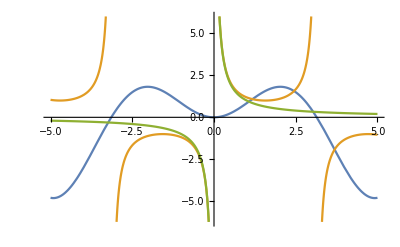

```mathematica
Plot[{x Sin[x],x/(x Sin[x]),Sin[x]/(x Sin[x])},{x,-5,5}]
```

```mathematica
Plot[
{x Sin[x],x/(x Sin[x]),Sin[x]/(x Sin[x])}
,{x,-10,10}
,PlotTheme->"Marketing",PlotLegends->"Expressions",ImageSize->Full,AspectRatio->1/2,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
x/500
```

x/500

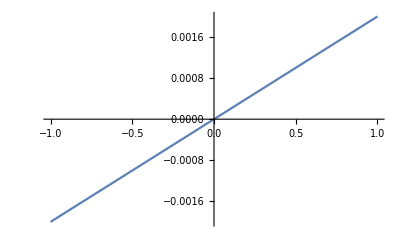

```mathematica
Plot[x/500,{x,-1,1}]
```

```mathematica
x/500+500
```

500+x/500

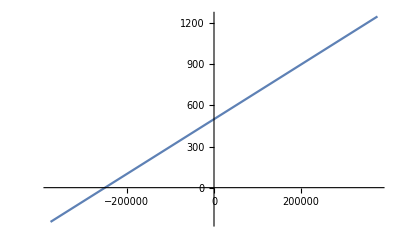

```mathematica
Plot[500+x/500,{x,-375000.,375000.}]
```

```mathematica
LaplaceTransform[t^4 Sin[t],t,s]
```

(24 (1-10 s^2+5 s^4))/((1+s^2)^5)

```mathematica
LaplaceTransform[Sin[t],t,s]
```

1/(1+s^2)

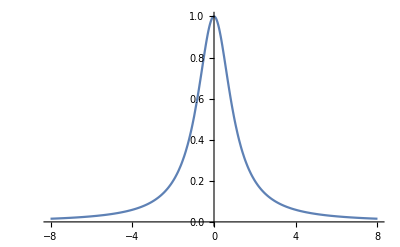

```mathematica
Plot[1/(1+s^2),{s,-8,8}]
```

```mathematica
FinancialData["NASDAQ:UBER","Close"]
```

FinancialData::notent: NASDAQ:UBER is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Missing[NotAvailable]

```mathematica
FinancialData["NYSE:UBER","Close"]
```

30.17 $

```mathematica
FinancialData["NASDAQ:LYFT","Close"]
```

45.84 $

```mathematica
With[{a=FinancialData["NYSE:UBER","Close",All],b=FinancialData["NASDAQ:LYFT","Close",All]},
Join[
Transpose[{
a["Dates"],
Ratios@a["Values"]
}],
Transpose[{
b["Dates"],
Ratios@b["Values"]
}]]
]
```

Transpose::nmtx: The first two levels of {{DateObject[{2019,5,10,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,5,13,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,5,14,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,5,15,0,0,0.},Instant,Gregorian,-8.],«43»,DateObject[{2019,7,18,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,7,19,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,7,22,0,0,0.},Instant,Gregorian,-8.],«111»},{0.892471,«49»,«110»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{DateObject[{2019,3,29,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,4,1,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,4,2,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,4,3,0,0,0.},Instant,Gregorian,-8.],«43»,DateObject[{2019,6,6,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,6,7,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,6,10,0,0,0.},Instant,Gregorian,-8.],«140»},{0.881466,«49»,«139»}} cannot be transposed.

Transpose::tperm: Permutation {{DateObject[{2019,3,29,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,4,1,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,4,2,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,4,3,0,0,0.},Instant,Gregorian,-8.],«43»,DateObject[{2019,6,6,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,6,7,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,6,10,0,0,0.},Instant,Gregorian,-8.],«140»},{0.881466,«49»,«139»}} is longer than the dimensions {2} of the expression.

Transpose[{{Fri 10 May 2019 00:00:00GMT-8.,Mon 13 May 2019 00:00:00GMT-8.,Tue 14 May 2019 00:00:00GMT-8.,Wed 15 May 2019 00:00:00GMT-8.,Thu 16 May 2019 00:00:00GMT-8.,Fri 17 May 2019 00:00:00GMT-8.,Mon 20 May 2019 00:00:00GMT-8.,Tue 21 May 2019 00:00:00GMT-8.,Wed 22 May 2019 00:00:00GMT-8.,Thu 23 May 2019 00:00:00GMT-8.,Fri 24 May 2019 00:00:00GMT-8.,Tue 28 May 2019 00:00:00GMT-8.,Wed 29 May 2019 00:00:00GMT-8.,Thu 30 May 2019 00:00:00GMT-8.,Fri 31 May 2019 00:00:00GMT-8.,Mon 3 Jun 2019 00:00:00GMT-8.,Tue 4 Jun 2019 00:00:00GMT-8.,Wed 5 Jun 2019 00:00:00GMT-8.,Thu 6 Jun 2019 00:00:00GMT-8.,Fri 7 Jun 2019 00:00:00GMT-8.,Mon 10 Jun 2019 00:00:00GMT-8.,Tue 11 Jun 2019 00:00:00GMT-8.,Wed 12 Jun 2019 00:00:00GMT-8.,Thu 13 Jun 2019 00:00:00GMT-8.,Fri 14 Jun 2019 00:00:00GMT-8.,Mon 17 Jun 2019 00:00:00GMT-8.,Tue 18 Jun 2019 00:00:00GMT-8.,Wed 19 Jun 2019 00:00:00GMT-8.,Thu 20 Jun 2019 00:00:00GMT-8.,Fri 21 Jun 2019 00:00:00GMT-8.,Mon 24 Jun 2019 00:00:00GMT-8.,Tue 25 Jun 2019 00:00:00GMT-8.,Wed 26 Jun 2019 00:00:00GMT-8.,Thu 27 Jun 2019 00:00:00GMT-8.,Fri 28 Jun 2019 00:00:00GMT-8.,Mon 1 Jul 2019 00:00:00GMT-8.,Tue 2 Jul 2019 00:00:00GMT-8.,Wed 3 Jul 2019 00:00:00GMT-8.,Fri 5 Jul 2019 00:00:00GMT-8.,Mon 8 Jul 2019 00:00:00GMT-8.,Tue 9 Jul 2019 00:00:00GMT-8.,Wed 10 Jul 2019 00:00:00GMT-8.,Thu 11 Jul 2019 00:00:00GMT-8.,Fri 12 Jul 2019 00:00:00GMT-8.,Mon 15 Jul 2019 00:00:00GMT-8.,Tue 16 Jul 2019 00:00:00GMT-8.,Wed 17 Jul 2019 00:00:00GMT-8.,Thu 18 Jul 2019 00:00:00GMT-8.,Fri 19 Jul 2019 00:00:00GMT-8.,Mon 22 Jul 2019 00:00:00GMT-8.,Tue 23 Jul 2019 00:00:00GMT-8.,Wed 24 Jul 2019 00:00:00GMT-8.,Thu 25 Jul 2019 00:00:00GMT-8.,Fri 26 Jul 2019 00:00:00GMT-8.,Mon 29 Jul 2019 00:00:00GMT-8.,Tue 30 Jul 2019 00:00:00GMT-8.,Wed 31 Jul 2019 00:00:00GMT-8.,Thu 1 Aug 2019 00:00:00GMT-8.,Fri 2 Aug 2019 00:00:00GMT-8.,Mon 5 Aug 2019 00:00:00GMT-8.,Tue 6 Aug 2019 00:00:00GMT-8.,Wed 7 Aug 2019 00:00:00GMT-8.,Thu 8 Aug 2019 00:00:00GMT-8.,Fri 9 Aug 2019 00:00:00GMT-8.,Mon 12 Aug 2019 00:00:00GMT-8.,Tue 13 Aug 2019 00:00:00GMT-8.,Wed 14 Aug 2019 00:00:00GMT-8.,Thu 15 Aug 2019 00:00:00GMT-8.,Fri 16 Aug 2019 00:00:00GMT-8.,Mon 19 Aug 2019 00:00:00GMT-8.,Tue 20 Aug 2019 00:00:00GMT-8.,Wed 21 Aug 2019 00:00:00GMT-8.,Thu 22 Aug 2019 00:00:00GMT-8.,Fri 23 Aug 2019 00:00:00GMT-8.,Mon 26 Aug 2019 00:00:00GMT-8.,Tue 27 Aug 2019 00:00:00GMT-8.,Wed 28 Aug 2019 00:00:00GMT-8.,Thu 29 Aug 2019 00:00:00GMT-8.,Fri 30 Aug 2019 00:00:00GMT-8.,Tue 3 Sep 2019 00:00:00GMT-8.,Wed 4 Sep 2019 00:00:00GMT-8.,Thu 5 Sep 2019 00:00:00GMT-8.,Fri 6 Sep 2019 00:00:00GMT-8.,Mon 9 Sep 2019 00:00:00GMT-8.,Tue 10 Sep 2019 00:00:00GMT-8.,Wed 11 Sep 2019 00:00:00GMT-8.,Thu 12 Sep 2019 00:00:00GMT-8.,Fri 13 Sep 2019 00:00:00GMT-8.,Mon 16 Sep 2019 00:00:00GMT-8.,Tue 17 Sep 2019 00:00:00GMT-8.,Wed 18 Sep 2019 00:00:00GMT-8.,Thu 19 Sep 2019 00:00:00GMT-8.,Fri 20 Sep 2019 00:00:00GMT-8.,Mon 23 Sep 2019 00:00:00GMT-8.,Tue 24 Sep 2019 00:00:00GMT-8.,Wed 25 Sep 2019 00:00:00GMT-8.,Thu 26 Sep 2019 00:00:00GMT-8.,Fri 27 Sep 2019 00:00:00GMT-8.,Mon 30 Sep 2019 00:00:00GMT-8.,Tue 1 Oct 2019 00:00:00GMT-8.,Wed 2 Oct 2019 00:00:00GMT-8.,Thu 3 Oct 2019 00:00:00GMT-8.,Fri 4 Oct 2019 00:00:00GMT-8.,Mon 7 Oct 2019 00:00:00GMT-8.,Tue 8 Oct 2019 00:00:00GMT-8.,Wed 9 Oct 2019 00:00:00GMT-8.,Thu 10 Oct 2019 00:00:00GMT-8.,Fri 11 Oct 2019 00:00:00GMT-8.,Mon 14 Oct 2019 00:00:00GMT-8.,Tue 15 Oct 2019 00:00:00GMT-8.,Wed 16 Oct 2019 00:00:00GMT-8.,Thu 17 Oct 2019 00:00:00GMT-8.,Fri 18 Oct 2019 00:00:00GMT-8.,Mon 21 Oct 2019 00:00:00GMT-8.,Tue 22 Oct 2019 00:00:00GMT-8.,Wed 23 Oct 2019 00:00:00GMT-8.,Thu 24 Oct 2019 00:00:00GMT-8.,Fri 25 Oct 2019 00:00:00GMT-8.,Mon 28 Oct 2019 00:00:00GMT-8.,Tue 29 Oct 2019 00:00:00GMT-8.,Wed 30 Oct 2019 00:00:00GMT-8.,Thu 31 Oct 2019 00:00:00GMT-8.,Fri 1 Nov 2019 00:00:00GMT-8.,Mon 4 Nov 2019 00:00:00GMT-8.,Tue 5 Nov 2019 00:00:00GMT-8.,Wed 6 Nov 2019 00:00:00GMT-8.,Thu 7 Nov 2019 00:00:00GMT-8.,Fri 8 Nov 2019 00:00:00GMT-8.,Mon 11 Nov 2019 00:00:00GMT-8.,Tue 12 Nov 2019 00:00:00GMT-8.,Wed 13 Nov 2019 00:00:00GMT-8.,Thu 14 Nov 2019 00:00:00GMT-8.,Fri 15 Nov 2019 00:00:00GMT-8.,Mon 18 Nov 2019 00:00:00GMT-8.,Tue 19 Nov 2019 00:00:00GMT-8.,Wed 20 Nov 2019 00:00:00GMT-8.,Thu 21 Nov 2019 00:00:00GMT-8.,Fri 22 Nov 2019 00:00:00GMT-8.,Mon 25 Nov 2019 00:00:00GMT-8.,Tue 26 Nov 2019 00:00:00GMT-8.,Wed 27 Nov 2019 00:00:00GMT-8.,Fri 29 Nov 2019 00:00:00GMT-8.,Mon 2 Dec 2019 00:00:00GMT-8.,Tue 3 Dec 2019 00:00:00GMT-8.,Wed 4 Dec 2019 00:00:00GMT-8.,Thu 5 Dec 2019 00:00:00GMT-8.,Fri 6 Dec 2019 00:00:00GMT-8.,Mon 9 Dec 2019 00:00:00GMT-8.,Tue 10 Dec 2019 00:00:00GMT-8.,Wed 11 Dec 2019 00:00:00GMT-8.,Thu 12 Dec 2019 00:00:00GMT-8.,Fri 13 Dec 2019 00:00:00GMT-8.,Mon 16 Dec 2019 00:00:00GMT-8.,Tue 17 Dec 2019 00:00:00GMT-8.,Wed 18 Dec 2019 00:00:00GMT-8.,Thu 19 Dec 2019 00:00:00GMT-8.,Fri 20 Dec 2019 00:00:00GMT-8.,Mon 23 Dec 2019 00:00:00GMT-8.,Tue 24 Dec 2019 00:00:00GMT-8.,Thu 26 Dec 2019 00:00:00GMT-8.,Fri 27 Dec 2019 00:00:00GMT-8.},{0.892471,1.07709,1.03328,1.04141,0.974651,0.992365,0.997836,0.993976,0.981091,1.0257,0.986509,0.975336,0.996495,1.01533,1.02079,1.03636,1.05263,0.998222,0.983081,0.9649,0.996245,0.993404,1.05075,0.975626,1.01272,1.00183,1.0228,0.977708,1.00319,0.979318,1.,0.986308,1.06188,1.0277,0.954506,0.993901,1.00523,0.984174,0.986676,1.0291,0.988688,1.00664,1.,1.01228,0.991017,0.988443,1.00206,0.987875,1.01181,0.992447,1.00923,0.991773,1.02581,0.985624,0.970602,0.989434,0.980304,0.977971,0.966584,1.00256,1.01405,1.08237,0.932046,0.923845,0.985135,0.931687,0.97821,1.06051,0.982401,1.01965,0.989232,0.973933,0.983235,0.99641,0.993996,0.984295,1.00522,0.9942,0.942585,1.04202,1.01626,0.980006,1.01193,1.03939,1.01462,1.00206,0.975932,1.03549,0.995934,0.999125,0.987157,0.963927,1.01227,0.948485,1.01214,0.996528,0.959455,1.00594,0.956679,0.994854,1.02483,0.998318,1.02359,0.964109,0.992828,0.99312,1.04364,1.03286,1.02828,0.995938,1.02353,0.982833,0.979725,1.03566,1.01599,1.00696,0.982873,1.01559,0.975918,1.04102,0.933333,0.995873,0.990755,0.901544,0.961456,1.01633,0.986487,1.00481,0.983788,1.00037,0.973044,1.03078,0.998507,1.01121,1.03623,1.05102,1.00339,0.984777,1.01443,0.998645,1.00373,0.979054,1.00138,1.00138,0.985891,0.972426,0.993539,1.00759,1.019,1.0095,0.993029,1.05476,0.990017,1.01277,0.995353,1.01534,0.996059,1.00363,1.00756,0.983697}},{{Fri 29 Mar 2019 00:00:00GMT-8.,Mon 1 Apr 2019 00:00:00GMT-8.,Tue 2 Apr 2019 00:00:00GMT-8.,Wed 3 Apr 2019 00:00:00GMT-8.,Thu 4 Apr 2019 00:00:00GMT-8.,Fri 5 Apr 2019 00:00:00GMT-8.,Mon 8 Apr 2019 00:00:00GMT-8.,Tue 9 Apr 2019 00:00:00GMT-8.,Wed 10 Apr 2019 00:00:00GMT-8.,Thu 11 Apr 2019 00:00:00GMT-8.,Fri 12 Apr 2019 00:00:00GMT-8.,Mon 15 Apr 2019 00:00:00GMT-8.,Tue 16 Apr 2019 00:00:00GMT-8.,Wed 17 Apr 2019 00:00:00GMT-8.,Thu 18 Apr 2019 00:00:00GMT-8.,Mon 22 Apr 2019 00:00:00GMT-8.,Tue 23 Apr 2019 00:00:00GMT-8.,Wed 24 Apr 2019 00:00:00GMT-8.,Thu 25 Apr 2019 00:00:00GMT-8.,Fri 26 Apr 2019 00:00:00GMT-8.,Mon 29 Apr 2019 00:00:00GMT-8.,Tue 30 Apr 2019 00:00:00GMT-8.,Wed 1 May 2019 00:00:00GMT-8.,Thu 2 May 2019 00:00:00GMT-8.,Fri 3 May 2019 00:00:00GMT-8.,Mon 6 May 2019 00:00:00GMT-8.,Tue 7 May 2019 00:00:00GMT-8.,Wed 8 May 2019 00:00:00GMT-8.,Thu 9 May 2019 00:00:00GMT-8.,Fri 10 May 2019 00:00:00GMT-8.,Mon 13 May 2019 00:00:00GMT-8.,Tue 14 May 2019 00:00:00GMT-8.,Wed 15 May 2019 00:00:00GMT-8.,Thu 16 May 2019 00:00:00GMT-8.,Fri 17 May 2019 00:00:00GMT-8.,Mon 20 May 2019 00:00:00GMT-8.,Tue 21 May 2019 00:00:00GMT-8.,Wed 22 May 2019 00:00:00GMT-8.,Thu 23 May 2019 00:00:00GMT-8.,Fri 24 May 2019 00:00:00GMT-8.,Tue 28 May 2019 00:00:00GMT-8.,Wed 29 May 2019 00:00:00GMT-8.,Thu 30 May 2019 00:00:00GMT-8.,Fri 31 May 2019 00:00:00GMT-8.,Mon 3 Jun 2019 00:00:00GMT-8.,Tue 4 Jun 2019 00:00:00GMT-8.,Wed 5 Jun 2019 00:00:00GMT-8.,Thu 6 Jun 2019 00:00:00GMT-8.,Fri 7 Jun 2019 00:00:00GMT-8.,Mon 10 Jun 2019 00:00:00GMT-8.,Tue 11 Jun 2019 00:00:00GMT-8.,Wed 12 Jun 2019 00:00:00GMT-8.,Thu 13 Jun 2019 00:00:00GMT-8.,Fri 14 Jun 2019 00:00:00GMT-8.,Mon 17 Jun 2019 00:00:00GMT-8.,Tue 18 Jun 2019 00:00:00GMT-8.,Wed 19 Jun 2019 00:00:00GMT-8.,Thu 20 Jun 2019 00:00:00GMT-8.,Fri 21 Jun 2019 00:00:00GMT-8.,Mon 24 Jun 2019 00:00:00GMT-8.,Tue 25 Jun 2019 00:00:00GMT-8.,Wed 26 Jun 2019 00:00:00GMT-8.,Thu 27 Jun 2019 00:00:00GMT-8.,Fri 28 Jun 2019 00:00:00GMT-8.,Mon 1 Jul 2019 00:00:00GMT-8.,Tue 2 Jul 2019 00:00:00GMT-8.,Wed 3 Jul 2019 00:00:00GMT-8.,Fri 5 Jul 2019 00:00:00GMT-8.,Mon 8 Jul 2019 00:00:00GMT-8.,Tue 9 Jul 2019 00:00:00GMT-8.,Wed 10 Jul 2019 00:00:00GMT-8.,Thu 11 Jul 2019 00:00:00GMT-8.,Fri 12 Jul 2019 00:00:00GMT-8.,Mon 15 Jul 2019 00:00:00GMT-8.,Tue 16 Jul 2019 00:00:00GMT-8.,Wed 17 Jul 2019 00:00:00GMT-8.,Thu 18 Jul 2019 00:00:00GMT-8.,Fri 19 Jul 2019 00:00:00GMT-8.,Mon 22 Jul 2019 00:00:00GMT-8.,Tue 23 Jul 2019 00:00:00GMT-8.,Wed 24 Jul 2019 00:00:00GMT-8.,Thu 25 Jul 2019 00:00:00GMT-8.,Fri 26 Jul 2019 00:00:00GMT-8.,Mon 29 Jul 2019 00:00:00GMT-8.,Tue 30 Jul 2019 00:00:00GMT-8.,Wed 31 Jul 2019 00:00:00GMT-8.,Thu 1 Aug 2019 00:00:00GMT-8.,Fri 2 Aug 2019 00:00:00GMT-8.,Mon 5 Aug 2019 00:00:00GMT-8.,Tue 6 Aug 2019 00:00:00GMT-8.,Wed 7 Aug 2019 00:00:00GMT-8.,Thu 8 Aug 2019 00:00:00GMT-8.,Fri 9 Aug 2019 00:00:00GMT-8.,Mon 12 Aug 2019 00:00:00GMT-8.,Tue 13 Aug 2019 00:00:00GMT-8.,Wed 14 Aug 2019 00:00:00GMT-8.,Thu 15 Aug 2019 00:00:00GMT-8.,Fri 16 Aug 2019 00:00:00GMT-8.,Mon 19 Aug 2019 00:00:00GMT-8.,Tue 20 Aug 2019 00:00:00GMT-8.,Wed 21 Aug 2019 00:00:00GMT-8.,Thu 22 Aug 2019 00:00:00GMT-8.,Fri 23 Aug 2019 00:00:00GMT-8.,Mon 26 Aug 2019 00:00:00GMT-8.,Tue 27 Aug 2019 00:00:00GMT-8.,Wed 28 Aug 2019 00:00:00GMT-8.,Thu 29 Aug 2019 00:00:00GMT-8.,Fri 30 Aug 2019 00:00:00GMT-8.,Tue 3 Sep 2019 00:00:00GMT-8.,Wed 4 Sep 2019 00:00:00GMT-8.,Thu 5 Sep 2019 00:00:00GMT-8.,Fri 6 Sep 2019 00:00:00GMT-8.,Mon 9 Sep 2019 00:00:00GMT-8.,Tue 10 Sep 2019 00:00:00GMT-8.,Wed 11 Sep 2019 00:00:00GMT-8.,Thu 12 Sep 2019 00:00:00GMT-8.,Fri 13 Sep 2019 00:00:00GMT-8.,Mon 16 Sep 2019 00:00:00GMT-8.,Tue 17 Sep 2019 00:00:00GMT-8.,Wed 18 Sep 2019 00:00:00GMT-8.,Thu 19 Sep 2019 00:00:00GMT-8.,Fri 20 Sep 2019 00:00:00GMT-8.,Mon 23 Sep 2019 00:00:00GMT-8.,Tue 24 Sep 2019 00:00:00GMT-8.,Wed 25 Sep 2019 00:00:00GMT-8.,Thu 26 Sep 2019 00:00:00GMT-8.,Fri 27 Sep 2019 00:00:00GMT-8.,Mon 30 Sep 2019 00:00:00GMT-8.,Tue 1 Oct 2019 00:00:00GMT-8.,Wed 2 Oct 2019 00:00:00GMT-8.,Thu 3 Oct 2019 00:00:00GMT-8.,Fri 4 Oct 2019 00:00:00GMT-8.,Mon 7 Oct 2019 00:00:00GMT-8.,Tue 8 Oct 2019 00:00:00GMT-8.,Wed 9 Oct 2019 00:00:00GMT-8.,Thu 10 Oct 2019 00:00:00GMT-8.,Fri 11 Oct 2019 00:00:00GMT-8.,Mon 14 Oct 2019 00:00:00GMT-8.,Tue 15 Oct 2019 00:00:00GMT-8.,Wed 16 Oct 2019 00:00:00GMT-8.,Thu 17 Oct 2019 00:00:00GMT-8.,Fri 18 Oct 2019 00:00:00GMT-8.,Mon 21 Oct 2019 00:00:00GMT-8.,Tue 22 Oct 2019 00:00:00GMT-8.,Wed 23 Oct 2019 00:00:00GMT-8.,Thu 24 Oct 2019 00:00:00GMT-8.,Fri 25 Oct 2019 00:00:00GMT-8.,Mon 28 Oct 2019 00:00:00GMT-8.,Tue 29 Oct 2019 00:00:00GMT-8.,Wed 30 Oct 2019 00:00:00GMT-8.,Thu 31 Oct 2019 00:00:00GMT-8.,Fri 1 Nov 2019 00:00:00GMT-8.,Mon 4 Nov 2019 00:00:00GMT-8.,Tue 5 Nov 2019 00:00:00GMT-8.,Wed 6 Nov 2019 00:00:00GMT-8.,Thu 7 Nov 2019 00:00:00GMT-8.,Fri 8 Nov 2019 00:00:00GMT-8.,Mon 11 Nov 2019 00:00:00GMT-8.,Tue 12 Nov 2019 00:00:00GMT-8.,Wed 13 Nov 2019 00:00:00GMT-8.,Thu 14 Nov 2019 00:00:00GMT-8.,Fri 15 Nov 2019 00:00:00GMT-8.,Mon 18 Nov 2019 00:00:00GMT-8.,Tue 19 Nov 2019 00:00:00GMT-8.,Wed 20 Nov 2019 00:00:00GMT-8.,Thu 21 Nov 2019 00:00:00GMT-8.,Fri 22 Nov 2019 00:00:00GMT-8.,Mon 25 Nov 2019 00:00:00GMT-8.,Tue 26 Nov 2019 00:00:00GMT-8.,Wed 27 Nov 2019 00:00:00GMT-8.,Fri 29 Nov 2019 00:00:00GMT-8.,Mon 2 Dec 2019 00:00:00GMT-8.,Tue 3 Dec 2019 00:00:00GMT-8.,Wed 4 Dec 2019 00:00:00GMT-8.,Thu 5 Dec 2019 00:00:00GMT-8.,Fri 6 Dec 2019 00:00:00GMT-8.,Mon 9 Dec 2019 00:00:00GMT-8.,Tue 10 Dec 2019 00:00:00GMT-8.,Wed 11 Dec 2019 00:00:00GMT-8.,Thu 12 Dec 2019 00:00:00GMT-8.,Fri 13 Dec 2019 00:00:00GMT-8.,Mon 16 Dec 2019 00:00:00GMT-8.,Tue 17 Dec 2019 00:00:00GMT-8.,Wed 18 Dec 2019 00:00:00GMT-8.,Thu 19 Dec 2019 00:00:00GMT-8.,Fri 20 Dec 2019 00:00:00GMT-8.,Mon 23 Dec 2019 00:00:00GMT-8.,Tue 24 Dec 2019 00:00:00GMT-8.,Thu 26 Dec 2019 00:00:00GMT-8.,Fri 27 Dec 2019 00:00:00GMT-8.},{0.881466,0.99942,1.01493,1.02857,1.03403,0.943318,0.960273,0.891459,1.0148,0.981724,0.936806,1.0025,1.05796,0.980676,1.04421,0.988677,0.959668,0.974403,1.01597,1.05853,0.986962,0.982441,1.04681,1.01642,0.968965,0.979693,0.891641,1.0429,0.925879,0.942455,1.04922,1.06968,1.02887,0.967446,1.01562,1.01611,1.0427,1.00397,0.982619,0.996322,0.988926,0.974582,1.05088,1.03332,0.993786,1.0649,0.978099,0.961545,0.957813,1.02308,1.00586,1.04794,0.995916,1.04331,1.01258,0.986801,0.988828,1.0226,0.992219,1.00439,0.983292,1.03653,1.00674,0.94354,0.973387,1.00414,0.980033,1.00674,1.03412,1.0076,0.992777,1.0388,1.0084,1.00015,1.00571,1.01274,1.02197,0.978503,0.983788,1.00462,0.996627,1.00784,0.977259,0.97548,0.974544,0.981929,0.980592,1.01536,0.986389,1.02709,1.03002,0.952013,0.950271,1.03382,0.938189,0.968985,0.99375,0.984944,1.03812,1.00932,0.948476,0.956192,1.04276,0.968756,0.984479,1.01822,0.984718,0.927507,1.02048,1.00108,0.959052,0.997303,1.02411,1.02376,1.00989,0.98106,1.03666,1.00565,0.970037,1.01416,0.982022,0.975878,0.924299,0.997612,1.00287,0.986873,0.987666,0.968903,0.970179,1.02943,0.990891,1.00204,0.985219,0.988101,0.986911,1.04735,1.00798,1.03216,0.986125,1.02863,0.978882,1.00221,1.06556,0.988981,1.01486,1.01876,0.997306,0.983341,1.00984,0.939469,1.03716,0.99651,0.965912,1.03747,1.00862,0.998614,0.993986,0.985106,1.02292,0.968129,1.02672,1.04229,0.984173,0.99547,1.06394,0.993584,1.05338,1.00123,1.00755,0.9921,0.967538,1.00253,0.995896,0.952446,1.003,1.00487,0.996477,1.0464,0.983953,1.00322,1.02524,0.991029,0.989684,0.984471,1.03544,0.950334,1.00351,1.00066,1.00241}}]

```mathematica
With[{a=FinancialData["NYSE:UBER","Close",All],b=FinancialData["NASDAQ:LYFT","Close",All]},
{Transpose[{
a["Dates"],
Ratios@a["Values"]
}],
Transpose[{
b["Dates"],
Ratios@b["Values"]
}]}
]
```

Transpose::nmtx: The first two levels of {{DateObject[{2019,5,10,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,5,13,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,5,14,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,5,15,0,0,0.},Instant,Gregorian,-8.],«43»,DateObject[{2019,7,18,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,7,19,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,7,22,0,0,0.},Instant,Gregorian,-8.],«111»},{0.892471,«49»,«110»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{DateObject[{2019,3,29,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,4,1,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,4,2,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,4,3,0,0,0.},Instant,Gregorian,-8.],«43»,DateObject[{2019,6,6,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,6,7,0,0,0.},Instant,Gregorian,-8.],DateObject[{2019,6,10,0,0,0.},Instant,Gregorian,-8.],«140»},{0.881466,«49»,«139»}} cannot be transposed.

{Transpose[{{Fri 10 May 2019 00:00:00GMT-8.,Mon 13 May 2019 00:00:00GMT-8.,Tue 14 May 2019 00:00:00GMT-8.,Wed 15 May 2019 00:00:00GMT-8.,Thu 16 May 2019 00:00:00GMT-8.,Fri 17 May 2019 00:00:00GMT-8.,Mon 20 May 2019 00:00:00GMT-8.,Tue 21 May 2019 00:00:00GMT-8.,Wed 22 May 2019 00:00:00GMT-8.,Thu 23 May 2019 00:00:00GMT-8.,Fri 24 May 2019 00:00:00GMT-8.,Tue 28 May 2019 00:00:00GMT-8.,Wed 29 May 2019 00:00:00GMT-8.,Thu 30 May 2019 00:00:00GMT-8.,Fri 31 May 2019 00:00:00GMT-8.,Mon 3 Jun 2019 00:00:00GMT-8.,Tue 4 Jun 2019 00:00:00GMT-8.,Wed 5 Jun 2019 00:00:00GMT-8.,Thu 6 Jun 2019 00:00:00GMT-8.,Fri 7 Jun 2019 00:00:00GMT-8.,Mon 10 Jun 2019 00:00:00GMT-8.,Tue 11 Jun 2019 00:00:00GMT-8.,Wed 12 Jun 2019 00:00:00GMT-8.,Thu 13 Jun 2019 00:00:00GMT-8.,Fri 14 Jun 2019 00:00:00GMT-8.,Mon 17 Jun 2019 00:00:00GMT-8.,Tue 18 Jun 2019 00:00:00GMT-8.,Wed 19 Jun 2019 00:00:00GMT-8.,Thu 20 Jun 2019 00:00:00GMT-8.,Fri 21 Jun 2019 00:00:00GMT-8.,Mon 24 Jun 2019 00:00:00GMT-8.,Tue 25 Jun 2019 00:00:00GMT-8.,Wed 26 Jun 2019 00:00:00GMT-8.,Thu 27 Jun 2019 00:00:00GMT-8.,Fri 28 Jun 2019 00:00:00GMT-8.,Mon 1 Jul 2019 00:00:00GMT-8.,Tue 2 Jul 2019 00:00:00GMT-8.,Wed 3 Jul 2019 00:00:00GMT-8.,Fri 5 Jul 2019 00:00:00GMT-8.,Mon 8 Jul 2019 00:00:00GMT-8.,Tue 9 Jul 2019 00:00:00GMT-8.,Wed 10 Jul 2019 00:00:00GMT-8.,Thu 11 Jul 2019 00:00:00GMT-8.,Fri 12 Jul 2019 00:00:00GMT-8.,Mon 15 Jul 2019 00:00:00GMT-8.,Tue 16 Jul 2019 00:00:00GMT-8.,Wed 17 Jul 2019 00:00:00GMT-8.,Thu 18 Jul 2019 00:00:00GMT-8.,Fri 19 Jul 2019 00:00:00GMT-8.,Mon 22 Jul 2019 00:00:00GMT-8.,Tue 23 Jul 2019 00:00:00GMT-8.,Wed 24 Jul 2019 00:00:00GMT-8.,Thu 25 Jul 2019 00:00:00GMT-8.,Fri 26 Jul 2019 00:00:00GMT-8.,Mon 29 Jul 2019 00:00:00GMT-8.,Tue 30 Jul 2019 00:00:00GMT-8.,Wed 31 Jul 2019 00:00:00GMT-8.,Thu 1 Aug 2019 00:00:00GMT-8.,Fri 2 Aug 2019 00:00:00GMT-8.,Mon 5 Aug 2019 00:00:00GMT-8.,Tue 6 Aug 2019 00:00:00GMT-8.,Wed 7 Aug 2019 00:00:00GMT-8.,Thu 8 Aug 2019 00:00:00GMT-8.,Fri 9 Aug 2019 00:00:00GMT-8.,Mon 12 Aug 2019 00:00:00GMT-8.,Tue 13 Aug 2019 00:00:00GMT-8.,Wed 14 Aug 2019 00:00:00GMT-8.,Thu 15 Aug 2019 00:00:00GMT-8.,Fri 16 Aug 2019 00:00:00GMT-8.,Mon 19 Aug 2019 00:00:00GMT-8.,Tue 20 Aug 2019 00:00:00GMT-8.,Wed 21 Aug 2019 00:00:00GMT-8.,Thu 22 Aug 2019 00:00:00GMT-8.,Fri 23 Aug 2019 00:00:00GMT-8.,Mon 26 Aug 2019 00:00:00GMT-8.,Tue 27 Aug 2019 00:00:00GMT-8.,Wed 28 Aug 2019 00:00:00GMT-8.,Thu 29 Aug 2019 00:00:00GMT-8.,Fri 30 Aug 2019 00:00:00GMT-8.,Tue 3 Sep 2019 00:00:00GMT-8.,Wed 4 Sep 2019 00:00:00GMT-8.,Thu 5 Sep 2019 00:00:00GMT-8.,Fri 6 Sep 2019 00:00:00GMT-8.,Mon 9 Sep 2019 00:00:00GMT-8.,Tue 10 Sep 2019 00:00:00GMT-8.,Wed 11 Sep 2019 00:00:00GMT-8.,Thu 12 Sep 2019 00:00:00GMT-8.,Fri 13 Sep 2019 00:00:00GMT-8.,Mon 16 Sep 2019 00:00:00GMT-8.,Tue 17 Sep 2019 00:00:00GMT-8.,Wed 18 Sep 2019 00:00:00GMT-8.,Thu 19 Sep 2019 00:00:00GMT-8.,Fri 20 Sep 2019 00:00:00GMT-8.,Mon 23 Sep 2019 00:00:00GMT-8.,Tue 24 Sep 2019 00:00:00GMT-8.,Wed 25 Sep 2019 00:00:00GMT-8.,Thu 26 Sep 2019 00:00:00GMT-8.,Fri 27 Sep 2019 00:00:00GMT-8.,Mon 30 Sep 2019 00:00:00GMT-8.,Tue 1 Oct 2019 00:00:00GMT-8.,Wed 2 Oct 2019 00:00:00GMT-8.,Thu 3 Oct 2019 00:00:00GMT-8.,Fri 4 Oct 2019 00:00:00GMT-8.,Mon 7 Oct 2019 00:00:00GMT-8.,Tue 8 Oct 2019 00:00:00GMT-8.,Wed 9 Oct 2019 00:00:00GMT-8.,Thu 10 Oct 2019 00:00:00GMT-8.,Fri 11 Oct 2019 00:00:00GMT-8.,Mon 14 Oct 2019 00:00:00GMT-8.,Tue 15 Oct 2019 00:00:00GMT-8.,Wed 16 Oct 2019 00:00:00GMT-8.,Thu 17 Oct 2019 00:00:00GMT-8.,Fri 18 Oct 2019 00:00:00GMT-8.,Mon 21 Oct 2019 00:00:00GMT-8.,Tue 22 Oct 2019 00:00:00GMT-8.,Wed 23 Oct 2019 00:00:00GMT-8.,Thu 24 Oct 2019 00:00:00GMT-8.,Fri 25 Oct 2019 00:00:00GMT-8.,Mon 28 Oct 2019 00:00:00GMT-8.,Tue 29 Oct 2019 00:00:00GMT-8.,Wed 30 Oct 2019 00:00:00GMT-8.,Thu 31 Oct 2019 00:00:00GMT-8.,Fri 1 Nov 2019 00:00:00GMT-8.,Mon 4 Nov 2019 00:00:00GMT-8.,Tue 5 Nov 2019 00:00:00GMT-8.,Wed 6 Nov 2019 00:00:00GMT-8.,Thu 7 Nov 2019 00:00:00GMT-8.,Fri 8 Nov 2019 00:00:00GMT-8.,Mon 11 Nov 2019 00:00:00GMT-8.,Tue 12 Nov 2019 00:00:00GMT-8.,Wed 13 Nov 2019 00:00:00GMT-8.,Thu 14 Nov 2019 00:00:00GMT-8.,Fri 15 Nov 2019 00:00:00GMT-8.,Mon 18 Nov 2019 00:00:00GMT-8.,Tue 19 Nov 2019 00:00:00GMT-8.,Wed 20 Nov 2019 00:00:00GMT-8.,Thu 21 Nov 2019 00:00:00GMT-8.,Fri 22 Nov 2019 00:00:00GMT-8.,Mon 25 Nov 2019 00:00:00GMT-8.,Tue 26 Nov 2019 00:00:00GMT-8.,Wed 27 Nov 2019 00:00:00GMT-8.,Fri 29 Nov 2019 00:00:00GMT-8.,Mon 2 Dec 2019 00:00:00GMT-8.,Tue 3 Dec 2019 00:00:00GMT-8.,Wed 4 Dec 2019 00:00:00GMT-8.,Thu 5 Dec 2019 00:00:00GMT-8.,Fri 6 Dec 2019 00:00:00GMT-8.,Mon 9 Dec 2019 00:00:00GMT-8.,Tue 10 Dec 2019 00:00:00GMT-8.,Wed 11 Dec 2019 00:00:00GMT-8.,Thu 12 Dec 2019 00:00:00GMT-8.,Fri 13 Dec 2019 00:00:00GMT-8.,Mon 16 Dec 2019 00:00:00GMT-8.,Tue 17 Dec 2019 00:00:00GMT-8.,Wed 18 Dec 2019 00:00:00GMT-8.,Thu 19 Dec 2019 00:00:00GMT-8.,Fri 20 Dec 2019 00:00:00GMT-8.,Mon 23 Dec 2019 00:00:00GMT-8.,Tue 24 Dec 2019 00:00:00GMT-8.,Thu 26 Dec 2019 00:00:00GMT-8.,Fri 27 Dec 2019 00:00:00GMT-8.},{0.892471,1.07709,1.03328,1.04141,0.974651,0.992365,0.997836,0.993976,0.981091,1.0257,0.986509,0.975336,0.996495,1.01533,1.02079,1.03636,1.05263,0.998222,0.983081,0.9649,0.996245,0.993404,1.05075,0.975626,1.01272,1.00183,1.0228,0.977708,1.00319,0.979318,1.,0.986308,1.06188,1.0277,0.954506,0.993901,1.00523,0.984174,0.986676,1.0291,0.988688,1.00664,1.,1.01228,0.991017,0.988443,1.00206,0.987875,1.01181,0.992447,1.00923,0.991773,1.02581,0.985624,0.970602,0.989434,0.980304,0.977971,0.966584,1.00256,1.01405,1.08237,0.932046,0.923845,0.985135,0.931687,0.97821,1.06051,0.982401,1.01965,0.989232,0.973933,0.983235,0.99641,0.993996,0.984295,1.00522,0.9942,0.942585,1.04202,1.01626,0.980006,1.01193,1.03939,1.01462,1.00206,0.975932,1.03549,0.995934,0.999125,0.987157,0.963927,1.01227,0.948485,1.01214,0.996528,0.959455,1.00594,0.956679,0.994854,1.02483,0.998318,1.02359,0.964109,0.992828,0.99312,1.04364,1.03286,1.02828,0.995938,1.02353,0.982833,0.979725,1.03566,1.01599,1.00696,0.982873,1.01559,0.975918,1.04102,0.933333,0.995873,0.990755,0.901544,0.961456,1.01633,0.986487,1.00481,0.983788,1.00037,0.973044,1.03078,0.998507,1.01121,1.03623,1.05102,1.00339,0.984777,1.01443,0.998645,1.00373,0.979054,1.00138,1.00138,0.985891,0.972426,0.993539,1.00759,1.019,1.0095,0.993029,1.05476,0.990017,1.01277,0.995353,1.01534,0.996059,1.00363,1.00756,0.983697}}],Transpose[{{Fri 29 Mar 2019 00:00:00GMT-8.,Mon 1 Apr 2019 00:00:00GMT-8.,Tue 2 Apr 2019 00:00:00GMT-8.,Wed 3 Apr 2019 00:00:00GMT-8.,Thu 4 Apr 2019 00:00:00GMT-8.,Fri 5 Apr 2019 00:00:00GMT-8.,Mon 8 Apr 2019 00:00:00GMT-8.,Tue 9 Apr 2019 00:00:00GMT-8.,Wed 10 Apr 2019 00:00:00GMT-8.,Thu 11 Apr 2019 00:00:00GMT-8.,Fri 12 Apr 2019 00:00:00GMT-8.,Mon 15 Apr 2019 00:00:00GMT-8.,Tue 16 Apr 2019 00:00:00GMT-8.,Wed 17 Apr 2019 00:00:00GMT-8.,Thu 18 Apr 2019 00:00:00GMT-8.,Mon 22 Apr 2019 00:00:00GMT-8.,Tue 23 Apr 2019 00:00:00GMT-8.,Wed 24 Apr 2019 00:00:00GMT-8.,Thu 25 Apr 2019 00:00:00GMT-8.,Fri 26 Apr 2019 00:00:00GMT-8.,Mon 29 Apr 2019 00:00:00GMT-8.,Tue 30 Apr 2019 00:00:00GMT-8.,Wed 1 May 2019 00:00:00GMT-8.,Thu 2 May 2019 00:00:00GMT-8.,Fri 3 May 2019 00:00:00GMT-8.,Mon 6 May 2019 00:00:00GMT-8.,Tue 7 May 2019 00:00:00GMT-8.,Wed 8 May 2019 00:00:00GMT-8.,Thu 9 May 2019 00:00:00GMT-8.,Fri 10 May 2019 00:00:00GMT-8.,Mon 13 May 2019 00:00:00GMT-8.,Tue 14 May 2019 00:00:00GMT-8.,Wed 15 May 2019 00:00:00GMT-8.,Thu 16 May 2019 00:00:00GMT-8.,Fri 17 May 2019 00:00:00GMT-8.,Mon 20 May 2019 00:00:00GMT-8.,Tue 21 May 2019 00:00:00GMT-8.,Wed 22 May 2019 00:00:00GMT-8.,Thu 23 May 2019 00:00:00GMT-8.,Fri 24 May 2019 00:00:00GMT-8.,Tue 28 May 2019 00:00:00GMT-8.,Wed 29 May 2019 00:00:00GMT-8.,Thu 30 May 2019 00:00:00GMT-8.,Fri 31 May 2019 00:00:00GMT-8.,Mon 3 Jun 2019 00:00:00GMT-8.,Tue 4 Jun 2019 00:00:00GMT-8.,Wed 5 Jun 2019 00:00:00GMT-8.,Thu 6 Jun 2019 00:00:00GMT-8.,Fri 7 Jun 2019 00:00:00GMT-8.,Mon 10 Jun 2019 00:00:00GMT-8.,Tue 11 Jun 2019 00:00:00GMT-8.,Wed 12 Jun 2019 00:00:00GMT-8.,Thu 13 Jun 2019 00:00:00GMT-8.,Fri 14 Jun 2019 00:00:00GMT-8.,Mon 17 Jun 2019 00:00:00GMT-8.,Tue 18 Jun 2019 00:00:00GMT-8.,Wed 19 Jun 2019 00:00:00GMT-8.,Thu 20 Jun 2019 00:00:00GMT-8.,Fri 21 Jun 2019 00:00:00GMT-8.,Mon 24 Jun 2019 00:00:00GMT-8.,Tue 25 Jun 2019 00:00:00GMT-8.,Wed 26 Jun 2019 00:00:00GMT-8.,Thu 27 Jun 2019 00:00:00GMT-8.,Fri 28 Jun 2019 00:00:00GMT-8.,Mon 1 Jul 2019 00:00:00GMT-8.,Tue 2 Jul 2019 00:00:00GMT-8.,Wed 3 Jul 2019 00:00:00GMT-8.,Fri 5 Jul 2019 00:00:00GMT-8.,Mon 8 Jul 2019 00:00:00GMT-8.,Tue 9 Jul 2019 00:00:00GMT-8.,Wed 10 Jul 2019 00:00:00GMT-8.,Thu 11 Jul 2019 00:00:00GMT-8.,Fri 12 Jul 2019 00:00:00GMT-8.,Mon 15 Jul 2019 00:00:00GMT-8.,Tue 16 Jul 2019 00:00:00GMT-8.,Wed 17 Jul 2019 00:00:00GMT-8.,Thu 18 Jul 2019 00:00:00GMT-8.,Fri 19 Jul 2019 00:00:00GMT-8.,Mon 22 Jul 2019 00:00:00GMT-8.,Tue 23 Jul 2019 00:00:00GMT-8.,Wed 24 Jul 2019 00:00:00GMT-8.,Thu 25 Jul 2019 00:00:00GMT-8.,Fri 26 Jul 2019 00:00:00GMT-8.,Mon 29 Jul 2019 00:00:00GMT-8.,Tue 30 Jul 2019 00:00:00GMT-8.,Wed 31 Jul 2019 00:00:00GMT-8.,Thu 1 Aug 2019 00:00:00GMT-8.,Fri 2 Aug 2019 00:00:00GMT-8.,Mon 5 Aug 2019 00:00:00GMT-8.,Tue 6 Aug 2019 00:00:00GMT-8.,Wed 7 Aug 2019 00:00:00GMT-8.,Thu 8 Aug 2019 00:00:00GMT-8.,Fri 9 Aug 2019 00:00:00GMT-8.,Mon 12 Aug 2019 00:00:00GMT-8.,Tue 13 Aug 2019 00:00:00GMT-8.,Wed 14 Aug 2019 00:00:00GMT-8.,Thu 15 Aug 2019 00:00:00GMT-8.,Fri 16 Aug 2019 00:00:00GMT-8.,Mon 19 Aug 2019 00:00:00GMT-8.,Tue 20 Aug 2019 00:00:00GMT-8.,Wed 21 Aug 2019 00:00:00GMT-8.,Thu 22 Aug 2019 00:00:00GMT-8.,Fri 23 Aug 2019 00:00:00GMT-8.,Mon 26 Aug 2019 00:00:00GMT-8.,Tue 27 Aug 2019 00:00:00GMT-8.,Wed 28 Aug 2019 00:00:00GMT-8.,Thu 29 Aug 2019 00:00:00GMT-8.,Fri 30 Aug 2019 00:00:00GMT-8.,Tue 3 Sep 2019 00:00:00GMT-8.,Wed 4 Sep 2019 00:00:00GMT-8.,Thu 5 Sep 2019 00:00:00GMT-8.,Fri 6 Sep 2019 00:00:00GMT-8.,Mon 9 Sep 2019 00:00:00GMT-8.,Tue 10 Sep 2019 00:00:00GMT-8.,Wed 11 Sep 2019 00:00:00GMT-8.,Thu 12 Sep 2019 00:00:00GMT-8.,Fri 13 Sep 2019 00:00:00GMT-8.,Mon 16 Sep 2019 00:00:00GMT-8.,Tue 17 Sep 2019 00:00:00GMT-8.,Wed 18 Sep 2019 00:00:00GMT-8.,Thu 19 Sep 2019 00:00:00GMT-8.,Fri 20 Sep 2019 00:00:00GMT-8.,Mon 23 Sep 2019 00:00:00GMT-8.,Tue 24 Sep 2019 00:00:00GMT-8.,Wed 25 Sep 2019 00:00:00GMT-8.,Thu 26 Sep 2019 00:00:00GMT-8.,Fri 27 Sep 2019 00:00:00GMT-8.,Mon 30 Sep 2019 00:00:00GMT-8.,Tue 1 Oct 2019 00:00:00GMT-8.,Wed 2 Oct 2019 00:00:00GMT-8.,Thu 3 Oct 2019 00:00:00GMT-8.,Fri 4 Oct 2019 00:00:00GMT-8.,Mon 7 Oct 2019 00:00:00GMT-8.,Tue 8 Oct 2019 00:00:00GMT-8.,Wed 9 Oct 2019 00:00:00GMT-8.,Thu 10 Oct 2019 00:00:00GMT-8.,Fri 11 Oct 2019 00:00:00GMT-8.,Mon 14 Oct 2019 00:00:00GMT-8.,Tue 15 Oct 2019 00:00:00GMT-8.,Wed 16 Oct 2019 00:00:00GMT-8.,Thu 17 Oct 2019 00:00:00GMT-8.,Fri 18 Oct 2019 00:00:00GMT-8.,Mon 21 Oct 2019 00:00:00GMT-8.,Tue 22 Oct 2019 00:00:00GMT-8.,Wed 23 Oct 2019 00:00:00GMT-8.,Thu 24 Oct 2019 00:00:00GMT-8.,Fri 25 Oct 2019 00:00:00GMT-8.,Mon 28 Oct 2019 00:00:00GMT-8.,Tue 29 Oct 2019 00:00:00GMT-8.,Wed 30 Oct 2019 00:00:00GMT-8.,Thu 31 Oct 2019 00:00:00GMT-8.,Fri 1 Nov 2019 00:00:00GMT-8.,Mon 4 Nov 2019 00:00:00GMT-8.,Tue 5 Nov 2019 00:00:00GMT-8.,Wed 6 Nov 2019 00:00:00GMT-8.,Thu 7 Nov 2019 00:00:00GMT-8.,Fri 8 Nov 2019 00:00:00GMT-8.,Mon 11 Nov 2019 00:00:00GMT-8.,Tue 12 Nov 2019 00:00:00GMT-8.,Wed 13 Nov 2019 00:00:00GMT-8.,Thu 14 Nov 2019 00:00:00GMT-8.,Fri 15 Nov 2019 00:00:00GMT-8.,Mon 18 Nov 2019 00:00:00GMT-8.,Tue 19 Nov 2019 00:00:00GMT-8.,Wed 20 Nov 2019 00:00:00GMT-8.,Thu 21 Nov 2019 00:00:00GMT-8.,Fri 22 Nov 2019 00:00:00GMT-8.,Mon 25 Nov 2019 00:00:00GMT-8.,Tue 26 Nov 2019 00:00:00GMT-8.,Wed 27 Nov 2019 00:00:00GMT-8.,Fri 29 Nov 2019 00:00:00GMT-8.,Mon 2 Dec 2019 00:00:00GMT-8.,Tue 3 Dec 2019 00:00:00GMT-8.,Wed 4 Dec 2019 00:00:00GMT-8.,Thu 5 Dec 2019 00:00:00GMT-8.,Fri 6 Dec 2019 00:00:00GMT-8.,Mon 9 Dec 2019 00:00:00GMT-8.,Tue 10 Dec 2019 00:00:00GMT-8.,Wed 11 Dec 2019 00:00:00GMT-8.,Thu 12 Dec 2019 00:00:00GMT-8.,Fri 13 Dec 2019 00:00:00GMT-8.,Mon 16 Dec 2019 00:00:00GMT-8.,Tue 17 Dec 2019 00:00:00GMT-8.,Wed 18 Dec 2019 00:00:00GMT-8.,Thu 19 Dec 2019 00:00:00GMT-8.,Fri 20 Dec 2019 00:00:00GMT-8.,Mon 23 Dec 2019 00:00:00GMT-8.,Tue 24 Dec 2019 00:00:00GMT-8.,Thu 26 Dec 2019 00:00:00GMT-8.,Fri 27 Dec 2019 00:00:00GMT-8.},{0.881466,0.99942,1.01493,1.02857,1.03403,0.943318,0.960273,0.891459,1.0148,0.981724,0.936806,1.0025,1.05796,0.980676,1.04421,0.988677,0.959668,0.974403,1.01597,1.05853,0.986962,0.982441,1.04681,1.01642,0.968965,0.979693,0.891641,1.0429,0.925879,0.942455,1.04922,1.06968,1.02887,0.967446,1.01562,1.01611,1.0427,1.00397,0.982619,0.996322,0.988926,0.974582,1.05088,1.03332,0.993786,1.0649,0.978099,0.961545,0.957813,1.02308,1.00586,1.04794,0.995916,1.04331,1.01258,0.986801,0.988828,1.0226,0.992219,1.00439,0.983292,1.03653,1.00674,0.94354,0.973387,1.00414,0.980033,1.00674,1.03412,1.0076,0.992777,1.0388,1.0084,1.00015,1.00571,1.01274,1.02197,0.978503,0.983788,1.00462,0.996627,1.00784,0.977259,0.97548,0.974544,0.981929,0.980592,1.01536,0.986389,1.02709,1.03002,0.952013,0.950271,1.03382,0.938189,0.968985,0.99375,0.984944,1.03812,1.00932,0.948476,0.956192,1.04276,0.968756,0.984479,1.01822,0.984718,0.927507,1.02048,1.00108,0.959052,0.997303,1.02411,1.02376,1.00989,0.98106,1.03666,1.00565,0.970037,1.01416,0.982022,0.975878,0.924299,0.997612,1.00287,0.986873,0.987666,0.968903,0.970179,1.02943,0.990891,1.00204,0.985219,0.988101,0.986911,1.04735,1.00798,1.03216,0.986125,1.02863,0.978882,1.00221,1.06556,0.988981,1.01486,1.01876,0.997306,0.983341,1.00984,0.939469,1.03716,0.99651,0.965912,1.03747,1.00862,0.998614,0.993986,0.985106,1.02292,0.968129,1.02672,1.04229,0.984173,0.99547,1.06394,0.993584,1.05338,1.00123,1.00755,0.9921,0.967538,1.00253,0.995896,0.952446,1.003,1.00487,0.996477,1.0464,0.983953,1.00322,1.02524,0.991029,0.989684,0.984471,1.03544,0.950334,1.00351,1.00066,1.00241}}]}

```mathematica
With[{a=FinancialData["NYSE:UBER","Close",All],b=FinancialData["NASDAQ:LYFT","Close",All]},
Join[
Transpose[{
a["Dates"][[;;-2]],
Ratios@a["Values"]
}],
Transpose[{
b["Dates"][[;;-2]],
Ratios@b["Values"]
}]]
]
```

{{Fri 10 May 2019 00:00:00GMT-8.,0.892471},{Mon 13 May 2019 00:00:00GMT-8.,1.07709},{Tue 14 May 2019 00:00:00GMT-8.,1.03328},{Wed 15 May 2019 00:00:00GMT-8.,1.04141},{Thu 16 May 2019 00:00:00GMT-8.,0.974651},{Fri 17 May 2019 00:00:00GMT-8.,0.992365},{Mon 20 May 2019 00:00:00GMT-8.,0.997836},{Tue 21 May 2019 00:00:00GMT-8.,0.993976},{Wed 22 May 2019 00:00:00GMT-8.,0.981091},{Thu 23 May 2019 00:00:00GMT-8.,1.0257},{Fri 24 May 2019 00:00:00GMT-8.,0.986509},{Tue 28 May 2019 00:00:00GMT-8.,0.975336},{Wed 29 May 2019 00:00:00GMT-8.,0.996495},{Thu 30 May 2019 00:00:00GMT-8.,1.01533},{Fri 31 May 2019 00:00:00GMT-8.,1.02079},{Mon 3 Jun 2019 00:00:00GMT-8.,1.03636},{Tue 4 Jun 2019 00:00:00GMT-8.,1.05263},{Wed 5 Jun 2019 00:00:00GMT-8.,0.998222},{Thu 6 Jun 2019 00:00:00GMT-8.,0.983081},{Fri 7 Jun 2019 00:00:00GMT-8.,0.9649},{Mon 10 Jun 2019 00:00:00GMT-8.,0.996245},{Tue 11 Jun 2019 00:00:00GMT-8.,0.993404},{Wed 12 Jun 2019 00:00:00GMT-8.,1.05075},{Thu 13 Jun 2019 00:00:00GMT-8.,0.975626},{Fri 14 Jun 2019 00:00:00GMT-8.,1.01272},{Mon 17 Jun 2019 00:00:00GMT-8.,1.00183},{Tue 18 Jun 2019 00:00:00GMT-8.,1.0228},{Wed 19 Jun 2019 00:00:00GMT-8.,0.977708},{Thu 20 Jun 2019 00:00:00GMT-8.,1.00319},{Fri 21 Jun 2019 00:00:00GMT-8.,0.979318},{Mon 24 Jun 2019 00:00:00GMT-8.,1.},{Tue 25 Jun 2019 00:00:00GMT-8.,0.986308},{Wed 26 Jun 2019 00:00:00GMT-8.,1.06188},{Thu 27 Jun 2019 00:00:00GMT-8.,1.0277},{Fri 28 Jun 2019 00:00:00GMT-8.,0.954506},{Mon 1 Jul 2019 00:00:00GMT-8.,0.993901},{Tue 2 Jul 2019 00:00:00GMT-8.,1.00523},{Wed 3 Jul 2019 00:00:00GMT-8.,0.984174},{Fri 5 Jul 2019 00:00:00GMT-8.,0.986676},{Mon 8 Jul 2019 00:00:00GMT-8.,1.0291},{Tue 9 Jul 2019 00:00:00GMT-8.,0.988688},{Wed 10 Jul 2019 00:00:00GMT-8.,1.00664},{Thu 11 Jul 2019 00:00:00GMT-8.,1.},{Fri 12 Jul 2019 00:00:00GMT-8.,1.01228},{Mon 15 Jul 2019 00:00:00GMT-8.,0.991017},{Tue 16 Jul 2019 00:00:00GMT-8.,0.988443},{Wed 17 Jul 2019 00:00:00GMT-8.,1.00206},{Thu 18 Jul 2019 00:00:00GMT-8.,0.987875},{Fri 19 Jul 2019 00:00:00GMT-8.,1.01181},{Mon 22 Jul 2019 00:00:00GMT-8.,0.992447},{Tue 23 Jul 2019 00:00:00GMT-8.,1.00923},{Wed 24 Jul 2019 00:00:00GMT-8.,0.991773},{Thu 25 Jul 2019 00:00:00GMT-8.,1.02581},{Fri 26 Jul 2019 00:00:00GMT-8.,0.985624},{Mon 29 Jul 2019 00:00:00GMT-8.,0.970602},{Tue 30 Jul 2019 00:00:00GMT-8.,0.989434},{Wed 31 Jul 2019 00:00:00GMT-8.,0.980304},{Thu 1 Aug 2019 00:00:00GMT-8.,0.977971},{Fri 2 Aug 2019 00:00:00GMT-8.,0.966584},{Mon 5 Aug 2019 00:00:00GMT-8.,1.00256},{Tue 6 Aug 2019 00:00:00GMT-8.,1.01405},{Wed 7 Aug 2019 00:00:00GMT-8.,1.08237},{Thu 8 Aug 2019 00:00:00GMT-8.,0.932046},{Fri 9 Aug 2019 00:00:00GMT-8.,0.923845},{Mon 12 Aug 2019 00:00:00GMT-8.,0.985135},{Tue 13 Aug 2019 00:00:00GMT-8.,0.931687},{Wed 14 Aug 2019 00:00:00GMT-8.,0.97821},{Thu 15 Aug 2019 00:00:00GMT-8.,1.06051},{Fri 16 Aug 2019 00:00:00GMT-8.,0.982401},{Mon 19 Aug 2019 00:00:00GMT-8.,1.01965},{Tue 20 Aug 2019 00:00:00GMT-8.,0.989232},{Wed 21 Aug 2019 00:00:00GMT-8.,0.973933},{Thu 22 Aug 2019 00:00:00GMT-8.,0.983235},{Fri 23 Aug 2019 00:00:00GMT-8.,0.99641},{Mon 26 Aug 2019 00:00:00GMT-8.,0.993996},{Tue 27 Aug 2019 00:00:00GMT-8.,0.984295},{Wed 28 Aug 2019 00:00:00GMT-8.,1.00522},{Thu 29 Aug 2019 00:00:00GMT-8.,0.9942},{Fri 30 Aug 2019 00:00:00GMT-8.,0.942585},{Tue 3 Sep 2019 00:00:00GMT-8.,1.04202},{Wed 4 Sep 2019 00:00:00GMT-8.,1.01626},{Thu 5 Sep 2019 00:00:00GMT-8.,0.980006},{Fri 6 Sep 2019 00:00:00GMT-8.,1.01193},{Mon 9 Sep 2019 00:00:00GMT-8.,1.03939},{Tue 10 Sep 2019 00:00:00GMT-8.,1.01462},{Wed 11 Sep 2019 00:00:00GMT-8.,1.00206},{Thu 12 Sep 2019 00:00:00GMT-8.,0.975932},{Fri 13 Sep 2019 00:00:00GMT-8.,1.03549},{Mon 16 Sep 2019 00:00:00GMT-8.,0.995934},{Tue 17 Sep 2019 00:00:00GMT-8.,0.999125},{Wed 18 Sep 2019 00:00:00GMT-8.,0.987157},{Thu 19 Sep 2019 00:00:00GMT-8.,0.963927},{Fri 20 Sep 2019 00:00:00GMT-8.,1.01227},{Mon 23 Sep 2019 00:00:00GMT-8.,0.948485},{Tue 24 Sep 2019 00:00:00GMT-8.,1.01214},{Wed 25 Sep 2019 00:00:00GMT-8.,0.996528},{Thu 26 Sep 2019 00:00:00GMT-8.,0.959455},{Fri 27 Sep 2019 00:00:00GMT-8.,1.00594},{Mon 30 Sep 2019 00:00:00GMT-8.,0.956679},{Tue 1 Oct 2019 00:00:00GMT-8.,0.994854},{Wed 2 Oct 2019 00:00:00GMT-8.,1.02483},{Thu 3 Oct 2019 00:00:00GMT-8.,0.998318},{Fri 4 Oct 2019 00:00:00GMT-8.,1.02359},{Mon 7 Oct 2019 00:00:00GMT-8.,0.964109},{Tue 8 Oct 2019 00:00:00GMT-8.,0.992828},{Wed 9 Oct 2019 00:00:00GMT-8.,0.99312},{Thu 10 Oct 2019 00:00:00GMT-8.,1.04364},{Fri 11 Oct 2019 00:00:00GMT-8.,1.03286},{Mon 14 Oct 2019 00:00:00GMT-8.,1.02828},{Tue 15 Oct 2019 00:00:00GMT-8.,0.995938},{Wed 16 Oct 2019 00:00:00GMT-8.,1.02353},{Thu 17 Oct 2019 00:00:00GMT-8.,0.982833},{Fri 18 Oct 2019 00:00:00GMT-8.,0.979725},{Mon 21 Oct 2019 00:00:00GMT-8.,1.03566},{Tue 22 Oct 2019 00:00:00GMT-8.,1.01599},{Wed 23 Oct 2019 00:00:00GMT-8.,1.00696},{Thu 24 Oct 2019 00:00:00GMT-8.,0.982873},{Fri 25 Oct 2019 00:00:00GMT-8.,1.01559},{Mon 28 Oct 2019 00:00:00GMT-8.,0.975918},{Tue 29 Oct 2019 00:00:00GMT-8.,1.04102},{Wed 30 Oct 2019 00:00:00GMT-8.,0.933333},{Thu 31 Oct 2019 00:00:00GMT-8.,0.995873},{Fri 1 Nov 2019 00:00:00GMT-8.,0.990755},{Mon 4 Nov 2019 00:00:00GMT-8.,0.901544},{Tue 5 Nov 2019 00:00:00GMT-8.,0.961456},{Wed 6 Nov 2019 00:00:00GMT-8.,1.01633},{Thu 7 Nov 2019 00:00:00GMT-8.,0.986487},{Fri 8 Nov 2019 00:00:00GMT-8.,1.00481},{Mon 11 Nov 2019 00:00:00GMT-8.,0.983788},{Tue 12 Nov 2019 00:00:00GMT-8.,1.00037},{Wed 13 Nov 2019 00:00:00GMT-8.,0.973044},{Thu 14 Nov 2019 00:00:00GMT-8.,1.03078},{Fri 15 Nov 2019 00:00:00GMT-8.,0.998507},{Mon 18 Nov 2019 00:00:00GMT-8.,1.01121},{Tue 19 Nov 2019 00:00:00GMT-8.,1.03623},{Wed 20 Nov 2019 00:00:00GMT-8.,1.05102},{Thu 21 Nov 2019 00:00:00GMT-8.,1.00339},{Fri 22 Nov 2019 00:00:00GMT-8.,0.984777},{Mon 25 Nov 2019 00:00:00GMT-8.,1.01443},{Tue 26 Nov 2019 00:00:00GMT-8.,0.998645},{Wed 27 Nov 2019 00:00:00GMT-8.,1.00373},{Fri 29 Nov 2019 00:00:00GMT-8.,0.979054},{Mon 2 Dec 2019 00:00:00GMT-8.,1.00138},{Tue 3 Dec 2019 00:00:00GMT-8.,1.00138},{Wed 4 Dec 2019 00:00:00GMT-8.,0.985891},{Thu 5 Dec 2019 00:00:00GMT-8.,0.972426},{Fri 6 Dec 2019 00:00:00GMT-8.,0.993539},{Mon 9 Dec 2019 00:00:00GMT-8.,1.00759},{Tue 10 Dec 2019 00:00:00GMT-8.,1.019},{Wed 11 Dec 2019 00:00:00GMT-8.,1.0095},{Thu 12 Dec 2019 00:00:00GMT-8.,0.993029},{Fri 13 Dec 2019 00:00:00GMT-8.,1.05476},{Mon 16 Dec 2019 00:00:00GMT-8.,0.990017},{Tue 17 Dec 2019 00:00:00GMT-8.,1.01277},{Wed 18 Dec 2019 00:00:00GMT-8.,0.995353},{Thu 19 Dec 2019 00:00:00GMT-8.,1.01534},{Fri 20 Dec 2019 00:00:00GMT-8.,0.996059},{Mon 23 Dec 2019 00:00:00GMT-8.,1.00363},{Tue 24 Dec 2019 00:00:00GMT-8.,1.00756},{Thu 26 Dec 2019 00:00:00GMT-8.,0.983697},{Fri 29 Mar 2019 00:00:00GMT-8.,0.881466},{Mon 1 Apr 2019 00:00:00GMT-8.,0.99942},{Tue 2 Apr 2019 00:00:00GMT-8.,1.01493},{Wed 3 Apr 2019 00:00:00GMT-8.,1.02857},{Thu 4 Apr 2019 00:00:00GMT-8.,1.03403},{Fri 5 Apr 2019 00:00:00GMT-8.,0.943318},{Mon 8 Apr 2019 00:00:00GMT-8.,0.960273},{Tue 9 Apr 2019 00:00:00GMT-8.,0.891459},{Wed 10 Apr 2019 00:00:00GMT-8.,1.0148},{Thu 11 Apr 2019 00:00:00GMT-8.,0.981724},{Fri 12 Apr 2019 00:00:00GMT-8.,0.936806},{Mon 15 Apr 2019 00:00:00GMT-8.,1.0025},{Tue 16 Apr 2019 00:00:00GMT-8.,1.05796},{Wed 17 Apr 2019 00:00:00GMT-8.,0.980676},{Thu 18 Apr 2019 00:00:00GMT-8.,1.04421},{Mon 22 Apr 2019 00:00:00GMT-8.,0.988677},{Tue 23 Apr 2019 00:00:00GMT-8.,0.959668},{Wed 24 Apr 2019 00:00:00GMT-8.,0.974403},{Thu 25 Apr 2019 00:00:00GMT-8.,1.01597},{Fri 26 Apr 2019 00:00:00GMT-8.,1.05853},{Mon 29 Apr 2019 00:00:00GMT-8.,0.986962},{Tue 30 Apr 2019 00:00:00GMT-8.,0.982441},{Wed 1 May 2019 00:00:00GMT-8.,1.04681},{Thu 2 May 2019 00:00:00GMT-8.,1.01642},{Fri 3 May 2019 00:00:00GMT-8.,0.968965},{Mon 6 May 2019 00:00:00GMT-8.,0.979693},{Tue 7 May 2019 00:00:00GMT-8.,0.891641},{Wed 8 May 2019 00:00:00GMT-8.,1.0429},{Thu 9 May 2019 00:00:00GMT-8.,0.925879},{Fri 10 May 2019 00:00:00GMT-8.,0.942455},{Mon 13 May 2019 00:00:00GMT-8.,1.04922},{Tue 14 May 2019 00:00:00GMT-8.,1.06968},{Wed 15 May 2019 00:00:00GMT-8.,1.02887},{Thu 16 May 2019 00:00:00GMT-8.,0.967446},{Fri 17 May 2019 00:00:00GMT-8.,1.01562},{Mon 20 May 2019 00:00:00GMT-8.,1.01611},{Tue 21 May 2019 00:00:00GMT-8.,1.0427},{Wed 22 May 2019 00:00:00GMT-8.,1.00397},{Thu 23 May 2019 00:00:00GMT-8.,0.982619},{Fri 24 May 2019 00:00:00GMT-8.,0.996322},{Tue 28 May 2019 00:00:00GMT-8.,0.988926},{Wed 29 May 2019 00:00:00GMT-8.,0.974582},{Thu 30 May 2019 00:00:00GMT-8.,1.05088},{Fri 31 May 2019 00:00:00GMT-8.,1.03332},{Mon 3 Jun 2019 00:00:00GMT-8.,0.993786},{Tue 4 Jun 2019 00:00:00GMT-8.,1.0649},{Wed 5 Jun 2019 00:00:00GMT-8.,0.978099},{Thu 6 Jun 2019 00:00:00GMT-8.,0.961545},{Fri 7 Jun 2019 00:00:00GMT-8.,0.957813},{Mon 10 Jun 2019 00:00:00GMT-8.,1.02308},{Tue 11 Jun 2019 00:00:00GMT-8.,1.00586},{Wed 12 Jun 2019 00:00:00GMT-8.,1.04794},{Thu 13 Jun 2019 00:00:00GMT-8.,0.995916},{Fri 14 Jun 2019 00:00:00GMT-8.,1.04331},{Mon 17 Jun 2019 00:00:00GMT-8.,1.01258},{Tue 18 Jun 2019 00:00:00GMT-8.,0.986801},{Wed 19 Jun 2019 00:00:00GMT-8.,0.988828},{Thu 20 Jun 2019 00:00:00GMT-8.,1.0226},{Fri 21 Jun 2019 00:00:00GMT-8.,0.992219},{Mon 24 Jun 2019 00:00:00GMT-8.,1.00439},{Tue 25 Jun 2019 00:00:00GMT-8.,0.983292},{Wed 26 Jun 2019 00:00:00GMT-8.,1.03653},{Thu 27 Jun 2019 00:00:00GMT-8.,1.00674},{Fri 28 Jun 2019 00:00:00GMT-8.,0.94354},{Mon 1 Jul 2019 00:00:00GMT-8.,0.973387},{Tue 2 Jul 2019 00:00:00GMT-8.,1.00414},{Wed 3 Jul 2019 00:00:00GMT-8.,0.980033},{Fri 5 Jul 2019 00:00:00GMT-8.,1.00674},{Mon 8 Jul 2019 00:00:00GMT-8.,1.03412},{Tue 9 Jul 2019 00:00:00GMT-8.,1.0076},{Wed 10 Jul 2019 00:00:00GMT-8.,0.992777},{Thu 11 Jul 2019 00:00:00GMT-8.,1.0388},{Fri 12 Jul 2019 00:00:00GMT-8.,1.0084},{Mon 15 Jul 2019 00:00:00GMT-8.,1.00015},{Tue 16 Jul 2019 00:00:00GMT-8.,1.00571},{Wed 17 Jul 2019 00:00:00GMT-8.,1.01274},{Thu 18 Jul 2019 00:00:00GMT-8.,1.02197},{Fri 19 Jul 2019 00:00:00GMT-8.,0.978503},{Mon 22 Jul 2019 00:00:00GMT-8.,0.983788},{Tue 23 Jul 2019 00:00:00GMT-8.,1.00462},{Wed 24 Jul 2019 00:00:00GMT-8.,0.996627},{Thu 25 Jul 2019 00:00:00GMT-8.,1.00784},{Fri 26 Jul 2019 00:00:00GMT-8.,0.977259},{Mon 29 Jul 2019 00:00:00GMT-8.,0.97548},{Tue 30 Jul 2019 00:00:00GMT-8.,0.974544},{Wed 31 Jul 2019 00:00:00GMT-8.,0.981929},{Thu 1 Aug 2019 00:00:00GMT-8.,0.980592},{Fri 2 Aug 2019 00:00:00GMT-8.,1.01536},{Mon 5 Aug 2019 00:00:00GMT-8.,0.986389},{Tue 6 Aug 2019 00:00:00GMT-8.,1.02709},{Wed 7 Aug 2019 00:00:00GMT-8.,1.03002},{Thu 8 Aug 2019 00:00:00GMT-8.,0.952013},{Fri 9 Aug 2019 00:00:00GMT-8.,0.950271},{Mon 12 Aug 2019 00:00:00GMT-8.,1.03382},{Tue 13 Aug 2019 00:00:00GMT-8.,0.938189},{Wed 14 Aug 2019 00:00:00GMT-8.,0.968985},{Thu 15 Aug 2019 00:00:00GMT-8.,0.99375},{Fri 16 Aug 2019 00:00:00GMT-8.,0.984944},{Mon 19 Aug 2019 00:00:00GMT-8.,1.03812},{Tue 20 Aug 2019 00:00:00GMT-8.,1.00932},{Wed 21 Aug 2019 00:00:00GMT-8.,0.948476},{Thu 22 Aug 2019 00:00:00GMT-8.,0.956192},{Fri 23 Aug 2019 00:00:00GMT-8.,1.04276},{Mon 26 Aug 2019 00:00:00GMT-8.,0.968756},{Tue 27 Aug 2019 00:00:00GMT-8.,0.984479},{Wed 28 Aug 2019 00:00:00GMT-8.,1.01822},{Thu 29 Aug 2019 00:00:00GMT-8.,0.984718},{Fri 30 Aug 2019 00:00:00GMT-8.,0.927507},{Tue 3 Sep 2019 00:00:00GMT-8.,1.02048},{Wed 4 Sep 2019 00:00:00GMT-8.,1.00108},{Thu 5 Sep 2019 00:00:00GMT-8.,0.959052},{Fri 6 Sep 2019 00:00:00GMT-8.,0.997303},{Mon 9 Sep 2019 00:00:00GMT-8.,1.02411},{Tue 10 Sep 2019 00:00:00GMT-8.,1.02376},{Wed 11 Sep 2019 00:00:00GMT-8.,1.00989},{Thu 12 Sep 2019 00:00:00GMT-8.,0.98106},{Fri 13 Sep 2019 00:00:00GMT-8.,1.03666},{Mon 16 Sep 2019 00:00:00GMT-8.,1.00565},{Tue 17 Sep 2019 00:00:00GMT-8.,0.970037},{Wed 18 Sep 2019 00:00:00GMT-8.,1.01416},{Thu 19 Sep 2019 00:00:00GMT-8.,0.982022},{Fri 20 Sep 2019 00:00:00GMT-8.,0.975878},{Mon 23 Sep 2019 00:00:00GMT-8.,0.924299},{Tue 24 Sep 2019 00:00:00GMT-8.,0.997612},{Wed 25 Sep 2019 00:00:00GMT-8.,1.00287},{Thu 26 Sep 2019 00:00:00GMT-8.,0.986873},{Fri 27 Sep 2019 00:00:00GMT-8.,0.987666},{Mon 30 Sep 2019 00:00:00GMT-8.,0.968903},{Tue 1 Oct 2019 00:00:00GMT-8.,0.970179},{Wed 2 Oct 2019 00:00:00GMT-8.,1.02943},{Thu 3 Oct 2019 00:00:00GMT-8.,0.990891},{Fri 4 Oct 2019 00:00:00GMT-8.,1.00204},{Mon 7 Oct 2019 00:00:00GMT-8.,0.985219},{Tue 8 Oct 2019 00:00:00GMT-8.,0.988101},{Wed 9 Oct 2019 00:00:00GMT-8.,0.986911},{Thu 10 Oct 2019 00:00:00GMT-8.,1.04735},{Fri 11 Oct 2019 00:00:00GMT-8.,1.00798},{Mon 14 Oct 2019 00:00:00GMT-8.,1.03216},{Tue 15 Oct 2019 00:00:00GMT-8.,0.986125},{Wed 16 Oct 2019 00:00:00GMT-8.,1.02863},{Thu 17 Oct 2019 00:00:00GMT-8.,0.978882},{Fri 18 Oct 2019 00:00:00GMT-8.,1.00221},{Mon 21 Oct 2019 00:00:00GMT-8.,1.06556},{Tue 22 Oct 2019 00:00:00GMT-8.,0.988981},{Wed 23 Oct 2019 00:00:00GMT-8.,1.01486},{Thu 24 Oct 2019 00:00:00GMT-8.,1.01876},{Fri 25 Oct 2019 00:00:00GMT-8.,0.997306},{Mon 28 Oct 2019 00:00:00GMT-8.,0.983341},{Tue 29 Oct 2019 00:00:00GMT-8.,1.00984},{Wed 30 Oct 2019 00:00:00GMT-8.,0.939469},{Thu 31 Oct 2019 00:00:00GMT-8.,1.03716},{Fri 1 Nov 2019 00:00:00GMT-8.,0.99651},{Mon 4 Nov 2019 00:00:00GMT-8.,0.965912},{Tue 5 Nov 2019 00:00:00GMT-8.,1.03747},{Wed 6 Nov 2019 00:00:00GMT-8.,1.00862},{Thu 7 Nov 2019 00:00:00GMT-8.,0.998614},{Fri 8 Nov 2019 00:00:00GMT-8.,0.993986},{Mon 11 Nov 2019 00:00:00GMT-8.,0.985106},{Tue 12 Nov 2019 00:00:00GMT-8.,1.02292},{Wed 13 Nov 2019 00:00:00GMT-8.,0.968129},{Thu 14 Nov 2019 00:00:00GMT-8.,1.02672},{Fri 15 Nov 2019 00:00:00GMT-8.,1.04229},{Mon 18 Nov 2019 00:00:00GMT-8.,0.984173},{Tue 19 Nov 2019 00:00:00GMT-8.,0.99547},{Wed 20 Nov 2019 00:00:00GMT-8.,1.06394},{Thu 21 Nov 2019 00:00:00GMT-8.,0.993584},{Fri 22 Nov 2019 00:00:00GMT-8.,1.05338},{Mon 25 Nov 2019 00:00:00GMT-8.,1.00123},{Tue 26 Nov 2019 00:00:00GMT-8.,1.00755},{Wed 27 Nov 2019 00:00:00GMT-8.,0.9921},{Fri 29 Nov 2019 00:00:00GMT-8.,0.967538},{Mon 2 Dec 2019 00:00:00GMT-8.,1.00253},{Tue 3 Dec 2019 00:00:00GMT-8.,0.995896},{Wed 4 Dec 2019 00:00:00GMT-8.,0.952446},{Thu 5 Dec 2019 00:00:00GMT-8.,1.003},{Fri 6 Dec 2019 00:00:00GMT-8.,1.00487},{Mon 9 Dec 2019 00:00:00GMT-8.,0.996477},{Tue 10 Dec 2019 00:00:00GMT-8.,1.0464},{Wed 11 Dec 2019 00:00:00GMT-8.,0.983953},{Thu 12 Dec 2019 00:00:00GMT-8.,1.00322},{Fri 13 Dec 2019 00:00:00GMT-8.,1.02524},{Mon 16 Dec 2019 00:00:00GMT-8.,0.991029},{Tue 17 Dec 2019 00:00:00GMT-8.,0.989684},{Wed 18 Dec 2019 00:00:00GMT-8.,0.984471},{Thu 19 Dec 2019 00:00:00GMT-8.,1.03544},{Fri 20 Dec 2019 00:00:00GMT-8.,0.950334},{Mon 23 Dec 2019 00:00:00GMT-8.,1.00351},{Tue 24 Dec 2019 00:00:00GMT-8.,1.00066},{Thu 26 Dec 2019 00:00:00GMT-8.,1.00241}}

```mathematica
Select[GatherBy[Out[22],First],Length@Last@#==2&]
```

{{{Fri 10 May 2019 00:00:00GMT-8.,0.892471},{Fri 10 May 2019 00:00:00GMT-8.,0.942455}},{{Mon 13 May 2019 00:00:00GMT-8.,1.07709},{Mon 13 May 2019 00:00:00GMT-8.,1.04922}},{{Tue 14 May 2019 00:00:00GMT-8.,1.03328},{Tue 14 May 2019 00:00:00GMT-8.,1.06968}},{{Wed 15 May 2019 00:00:00GMT-8.,1.04141},{Wed 15 May 2019 00:00:00GMT-8.,1.02887}},{{Thu 16 May 2019 00:00:00GMT-8.,0.974651},{Thu 16 May 2019 00:00:00GMT-8.,0.967446}},{{Fri 17 May 2019 00:00:00GMT-8.,0.992365},{Fri 17 May 2019 00:00:00GMT-8.,1.01562}},{{Mon 20 May 2019 00:00:00GMT-8.,0.997836},{Mon 20 May 2019 00:00:00GMT-8.,1.01611}},{{Tue 21 May 2019 00:00:00GMT-8.,0.993976},{Tue 21 May 2019 00:00:00GMT-8.,1.0427}},{{Wed 22 May 2019 00:00:00GMT-8.,0.981091},{Wed 22 May 2019 00:00:00GMT-8.,1.00397}},{{Thu 23 May 2019 00:00:00GMT-8.,1.0257},{Thu 23 May 2019 00:00:00GMT-8.,0.982619}},{{Fri 24 May 2019 00:00:00GMT-8.,0.986509},{Fri 24 May 2019 00:00:00GMT-8.,0.996322}},{{Tue 28 May 2019 00:00:00GMT-8.,0.975336},{Tue 28 May 2019 00:00:00GMT-8.,0.988926}},{{Wed 29 May 2019 00:00:00GMT-8.,0.996495},{Wed 29 May 2019 00:00:00GMT-8.,0.974582}},{{Thu 30 May 2019 00:00:00GMT-8.,1.01533},{Thu 30 May 2019 00:00:00GMT-8.,1.05088}},{{Fri 31 May 2019 00:00:00GMT-8.,1.02079},{Fri 31 May 2019 00:00:00GMT-8.,1.03332}},{{Mon 3 Jun 2019 00:00:00GMT-8.,1.03636},{Mon 3 Jun 2019 00:00:00GMT-8.,0.993786}},{{Tue 4 Jun 2019 00:00:00GMT-8.,1.05263},{Tue 4 Jun 2019 00:00:00GMT-8.,1.0649}},{{Wed 5 Jun 2019 00:00:00GMT-8.,0.998222},{Wed 5 Jun 2019 00:00:00GMT-8.,0.978099}},{{Thu 6 Jun 2019 00:00:00GMT-8.,0.983081},{Thu 6 Jun 2019 00:00:00GMT-8.,0.961545}},{{Fri 7 Jun 2019 00:00:00GMT-8.,0.9649},{Fri 7 Jun 2019 00:00:00GMT-8.,0.957813}},{{Mon 10 Jun 2019 00:00:00GMT-8.,0.996245},{Mon 10 Jun 2019 00:00:00GMT-8.,1.02308}},{{Tue 11 Jun 2019 00:00:00GMT-8.,0.993404},{Tue 11 Jun 2019 00:00:00GMT-8.,1.00586}},{{Wed 12 Jun 2019 00:00:00GMT-8.,1.05075},{Wed 12 Jun 2019 00:00:00GMT-8.,1.04794}},{{Thu 13 Jun 2019 00:00:00GMT-8.,0.975626},{Thu 13 Jun 2019 00:00:00GMT-8.,0.995916}},{{Fri 14 Jun 2019 00:00:00GMT-8.,1.01272},{Fri 14 Jun 2019 00:00:00GMT-8.,1.04331}},{{Mon 17 Jun 2019 00:00:00GMT-8.,1.00183},{Mon 17 Jun 2019 00:00:00GMT-8.,1.01258}},{{Tue 18 Jun 2019 00:00:00GMT-8.,1.0228},{Tue 18 Jun 2019 00:00:00GMT-8.,0.986801}},{{Wed 19 Jun 2019 00:00:00GMT-8.,0.977708},{Wed 19 Jun 2019 00:00:00GMT-8.,0.988828}},{{Thu 20 Jun 2019 00:00:00GMT-8.,1.00319},{Thu 20 Jun 2019 00:00:00GMT-8.,1.0226}},{{Fri 21 Jun 2019 00:00:00GMT-8.,0.979318},{Fri 21 Jun 2019 00:00:00GMT-8.,0.992219}},{{Mon 24 Jun 2019 00:00:00GMT-8.,1.},{Mon 24 Jun 2019 00:00:00GMT-8.,1.00439}},{{Tue 25 Jun 2019 00:00:00GMT-8.,0.986308},{Tue 25 Jun 2019 00:00:00GMT-8.,0.983292}},{{Wed 26 Jun 2019 00:00:00GMT-8.,1.06188},{Wed 26 Jun 2019 00:00:00GMT-8.,1.03653}},{{Thu 27 Jun 2019 00:00:00GMT-8.,1.0277},{Thu 27 Jun 2019 00:00:00GMT-8.,1.00674}},{{Fri 28 Jun 2019 00:00:00GMT-8.,0.954506},{Fri 28 Jun 2019 00:00:00GMT-8.,0.94354}},{{Mon 1 Jul 2019 00:00:00GMT-8.,0.993901},{Mon 1 Jul 2019 00:00:00GMT-8.,0.973387}},{{Tue 2 Jul 2019 00:00:00GMT-8.,1.00523},{Tue 2 Jul 2019 00:00:00GMT-8.,1.00414}},{{Wed 3 Jul 2019 00:00:00GMT-8.,0.984174},{Wed 3 Jul 2019 00:00:00GMT-8.,0.980033}},{{Fri 5 Jul 2019 00:00:00GMT-8.,0.986676},{Fri 5 Jul 2019 00:00:00GMT-8.,1.00674}},{{Mon 8 Jul 2019 00:00:00GMT-8.,1.0291},{Mon 8 Jul 2019 00:00:00GMT-8.,1.03412}},{{Tue 9 Jul 2019 00:00:00GMT-8.,0.988688},{Tue 9 Jul 2019 00:00:00GMT-8.,1.0076}},{{Wed 10 Jul 2019 00:00:00GMT-8.,1.00664},{Wed 10 Jul 2019 00:00:00GMT-8.,0.992777}},{{Thu 11 Jul 2019 00:00:00GMT-8.,1.},{Thu 11 Jul 2019 00:00:00GMT-8.,1.0388}},{{Fri 12 Jul 2019 00:00:00GMT-8.,1.01228},{Fri 12 Jul 2019 00:00:00GMT-8.,1.0084}},{{Mon 15 Jul 2019 00:00:00GMT-8.,0.991017},{Mon 15 Jul 2019 00:00:00GMT-8.,1.00015}},{{Tue 16 Jul 2019 00:00:00GMT-8.,0.988443},{Tue 16 Jul 2019 00:00:00GMT-8.,1.00571}},{{Wed 17 Jul 2019 00:00:00GMT-8.,1.00206},{Wed 17 Jul 2019 00:00:00GMT-8.,1.01274}},{{Thu 18 Jul 2019 00:00:00GMT-8.,0.987875},{Thu 18 Jul 2019 00:00:00GMT-8.,1.02197}},{{Fri 19 Jul 2019 00:00:00GMT-8.,1.01181},{Fri 19 Jul 2019 00:00:00GMT-8.,0.978503}},{{Mon 22 Jul 2019 00:00:00GMT-8.,0.992447},{Mon 22 Jul 2019 00:00:00GMT-8.,0.983788}},{{Tue 23 Jul 2019 00:00:00GMT-8.,1.00923},{Tue 23 Jul 2019 00:00:00GMT-8.,1.00462}},{{Wed 24 Jul 2019 00:00:00GMT-8.,0.991773},{Wed 24 Jul 2019 00:00:00GMT-8.,0.996627}},{{Thu 25 Jul 2019 00:00:00GMT-8.,1.02581},{Thu 25 Jul 2019 00:00:00GMT-8.,1.00784}},{{Fri 26 Jul 2019 00:00:00GMT-8.,0.985624},{Fri 26 Jul 2019 00:00:00GMT-8.,0.977259}},{{Mon 29 Jul 2019 00:00:00GMT-8.,0.970602},{Mon 29 Jul 2019 00:00:00GMT-8.,0.97548}},{{Tue 30 Jul 2019 00:00:00GMT-8.,0.989434},{Tue 30 Jul 2019 00:00:00GMT-8.,0.974544}},{{Wed 31 Jul 2019 00:00:00GMT-8.,0.980304},{Wed 31 Jul 2019 00:00:00GMT-8.,0.981929}},{{Thu 1 Aug 2019 00:00:00GMT-8.,0.977971},{Thu 1 Aug 2019 00:00:00GMT-8.,0.980592}},{{Fri 2 Aug 2019 00:00:00GMT-8.,0.966584},{Fri 2 Aug 2019 00:00:00GMT-8.,1.01536}},{{Mon 5 Aug 2019 00:00:00GMT-8.,1.00256},{Mon 5 Aug 2019 00:00:00GMT-8.,0.986389}},{{Tue 6 Aug 2019 00:00:00GMT-8.,1.01405},{Tue 6 Aug 2019 00:00:00GMT-8.,1.02709}},{{Wed 7 Aug 2019 00:00:00GMT-8.,1.08237},{Wed 7 Aug 2019 00:00:00GMT-8.,1.03002}},{{Thu 8 Aug 2019 00:00:00GMT-8.,0.932046},{Thu 8 Aug 2019 00:00:00GMT-8.,0.952013}},{{Fri 9 Aug 2019 00:00:00GMT-8.,0.923845},{Fri 9 Aug 2019 00:00:00GMT-8.,0.950271}},{{Mon 12 Aug 2019 00:00:00GMT-8.,0.985135},{Mon 12 Aug 2019 00:00:00GMT-8.,1.03382}},{{Tue 13 Aug 2019 00:00:00GMT-8.,0.931687},{Tue 13 Aug 2019 00:00:00GMT-8.,0.938189}},{{Wed 14 Aug 2019 00:00:00GMT-8.,0.97821},{Wed 14 Aug 2019 00:00:00GMT-8.,0.968985}},{{Thu 15 Aug 2019 00:00:00GMT-8.,1.06051},{Thu 15 Aug 2019 00:00:00GMT-8.,0.99375}},{{Fri 16 Aug 2019 00:00:00GMT-8.,0.982401},{Fri 16 Aug 2019 00:00:00GMT-8.,0.984944}},{{Mon 19 Aug 2019 00:00:00GMT-8.,1.01965},{Mon 19 Aug 2019 00:00:00GMT-8.,1.03812}},{{Tue 20 Aug 2019 00:00:00GMT-8.,0.989232},{Tue 20 Aug 2019 00:00:00GMT-8.,1.00932}},{{Wed 21 Aug 2019 00:00:00GMT-8.,0.973933},{Wed 21 Aug 2019 00:00:00GMT-8.,0.948476}},{{Thu 22 Aug 2019 00:00:00GMT-8.,0.983235},{Thu 22 Aug 2019 00:00:00GMT-8.,0.956192}},{{Fri 23 Aug 2019 00:00:00GMT-8.,0.99641},{Fri 23 Aug 2019 00:00:00GMT-8.,1.04276}},{{Mon 26 Aug 2019 00:00:00GMT-8.,0.993996},{Mon 26 Aug 2019 00:00:00GMT-8.,0.968756}},{{Tue 27 Aug 2019 00:00:00GMT-8.,0.984295},{Tue 27 Aug 2019 00:00:00GMT-8.,0.984479}},{{Wed 28 Aug 2019 00:00:00GMT-8.,1.00522},{Wed 28 Aug 2019 00:00:00GMT-8.,1.01822}},{{Thu 29 Aug 2019 00:00:00GMT-8.,0.9942},{Thu 29 Aug 2019 00:00:00GMT-8.,0.984718}},{{Fri 30 Aug 2019 00:00:00GMT-8.,0.942585},{Fri 30 Aug 2019 00:00:00GMT-8.,0.927507}},{{Tue 3 Sep 2019 00:00:00GMT-8.,1.04202},{Tue 3 Sep 2019 00:00:00GMT-8.,1.02048}},{{Wed 4 Sep 2019 00:00:00GMT-8.,1.01626},{Wed 4 Sep 2019 00:00:00GMT-8.,1.00108}},{{Thu 5 Sep 2019 00:00:00GMT-8.,0.980006},{Thu 5 Sep 2019 00:00:00GMT-8.,0.959052}},{{Fri 6 Sep 2019 00:00:00GMT-8.,1.01193},{Fri 6 Sep 2019 00:00:00GMT-8.,0.997303}},{{Mon 9 Sep 2019 00:00:00GMT-8.,1.03939},{Mon 9 Sep 2019 00:00:00GMT-8.,1.02411}},{{Tue 10 Sep 2019 00:00:00GMT-8.,1.01462},{Tue 10 Sep 2019 00:00:00GMT-8.,1.02376}},{{Wed 11 Sep 2019 00:00:00GMT-8.,1.00206},{Wed 11 Sep 2019 00:00:00GMT-8.,1.00989}},{{Thu 12 Sep 2019 00:00:00GMT-8.,0.975932},{Thu 12 Sep 2019 00:00:00GMT-8.,0.98106}},{{Fri 13 Sep 2019 00:00:00GMT-8.,1.03549},{Fri 13 Sep 2019 00:00:00GMT-8.,1.03666}},{{Mon 16 Sep 2019 00:00:00GMT-8.,0.995934},{Mon 16 Sep 2019 00:00:00GMT-8.,1.00565}},{{Tue 17 Sep 2019 00:00:00GMT-8.,0.999125},{Tue 17 Sep 2019 00:00:00GMT-8.,0.970037}},{{Wed 18 Sep 2019 00:00:00GMT-8.,0.987157},{Wed 18 Sep 2019 00:00:00GMT-8.,1.01416}},{{Thu 19 Sep 2019 00:00:00GMT-8.,0.963927},{Thu 19 Sep 2019 00:00:00GMT-8.,0.982022}},{{Fri 20 Sep 2019 00:00:00GMT-8.,1.01227},{Fri 20 Sep 2019 00:00:00GMT-8.,0.975878}},{{Mon 23 Sep 2019 00:00:00GMT-8.,0.948485},{Mon 23 Sep 2019 00:00:00GMT-8.,0.924299}},{{Tue 24 Sep 2019 00:00:00GMT-8.,1.01214},{Tue 24 Sep 2019 00:00:00GMT-8.,0.997612}},{{Wed 25 Sep 2019 00:00:00GMT-8.,0.996528},{Wed 25 Sep 2019 00:00:00GMT-8.,1.00287}},{{Thu 26 Sep 2019 00:00:00GMT-8.,0.959455},{Thu 26 Sep 2019 00:00:00GMT-8.,0.986873}},{{Fri 27 Sep 2019 00:00:00GMT-8.,1.00594},{Fri 27 Sep 2019 00:00:00GMT-8.,0.987666}},{{Mon 30 Sep 2019 00:00:00GMT-8.,0.956679},{Mon 30 Sep 2019 00:00:00GMT-8.,0.968903}},{{Tue 1 Oct 2019 00:00:00GMT-8.,0.994854},{Tue 1 Oct 2019 00:00:00GMT-8.,0.970179}},{{Wed 2 Oct 2019 00:00:00GMT-8.,1.02483},{Wed 2 Oct 2019 00:00:00GMT-8.,1.02943}},{{Thu 3 Oct 2019 00:00:00GMT-8.,0.998318},{Thu 3 Oct 2019 00:00:00GMT-8.,0.990891}},{{Fri 4 Oct 2019 00:00:00GMT-8.,1.02359},{Fri 4 Oct 2019 00:00:00GMT-8.,1.00204}},{{Mon 7 Oct 2019 00:00:00GMT-8.,0.964109},{Mon 7 Oct 2019 00:00:00GMT-8.,0.985219}},{{Tue 8 Oct 2019 00:00:00GMT-8.,0.992828},{Tue 8 Oct 2019 00:00:00GMT-8.,0.988101}},{{Wed 9 Oct 2019 00:00:00GMT-8.,0.99312},{Wed 9 Oct 2019 00:00:00GMT-8.,0.986911}},{{Thu 10 Oct 2019 00:00:00GMT-8.,1.04364},{Thu 10 Oct 2019 00:00:00GMT-8.,1.04735}},{{Fri 11 Oct 2019 00:00:00GMT-8.,1.03286},{Fri 11 Oct 2019 00:00:00GMT-8.,1.00798}},{{Mon 14 Oct 2019 00:00:00GMT-8.,1.02828},{Mon 14 Oct 2019 00:00:00GMT-8.,1.03216}},{{Tue 15 Oct 2019 00:00:00GMT-8.,0.995938},{Tue 15 Oct 2019 00:00:00GMT-8.,0.986125}},{{Wed 16 Oct 2019 00:00:00GMT-8.,1.02353},{Wed 16 Oct 2019 00:00:00GMT-8.,1.02863}},{{Thu 17 Oct 2019 00:00:00GMT-8.,0.982833},{Thu 17 Oct 2019 00:00:00GMT-8.,0.978882}},{{Fri 18 Oct 2019 00:00:00GMT-8.,0.979725},{Fri 18 Oct 2019 00:00:00GMT-8.,1.00221}},{{Mon 21 Oct 2019 00:00:00GMT-8.,1.03566},{Mon 21 Oct 2019 00:00:00GMT-8.,1.06556}},{{Tue 22 Oct 2019 00:00:00GMT-8.,1.01599},{Tue 22 Oct 2019 00:00:00GMT-8.,0.988981}},{{Wed 23 Oct 2019 00:00:00GMT-8.,1.00696},{Wed 23 Oct 2019 00:00:00GMT-8.,1.01486}},{{Thu 24 Oct 2019 00:00:00GMT-8.,0.982873},{Thu 24 Oct 2019 00:00:00GMT-8.,1.01876}},{{Fri 25 Oct 2019 00:00:00GMT-8.,1.01559},{Fri 25 Oct 2019 00:00:00GMT-8.,0.997306}},{{Mon 28 Oct 2019 00:00:00GMT-8.,0.975918},{Mon 28 Oct 2019 00:00:00GMT-8.,0.983341}},{{Tue 29 Oct 2019 00:00:00GMT-8.,1.04102},{Tue 29 Oct 2019 00:00:00GMT-8.,1.00984}},{{Wed 30 Oct 2019 00:00:00GMT-8.,0.933333},{Wed 30 Oct 2019 00:00:00GMT-8.,0.939469}},{{Thu 31 Oct 2019 00:00:00GMT-8.,0.995873},{Thu 31 Oct 2019 00:00:00GMT-8.,1.03716}},{{Fri 1 Nov 2019 00:00:00GMT-8.,0.990755},{Fri 1 Nov 2019 00:00:00GMT-8.,0.99651}},{{Mon 4 Nov 2019 00:00:00GMT-8.,0.901544},{Mon 4 Nov 2019 00:00:00GMT-8.,0.965912}},{{Tue 5 Nov 2019 00:00:00GMT-8.,0.961456},{Tue 5 Nov 2019 00:00:00GMT-8.,1.03747}},{{Wed 6 Nov 2019 00:00:00GMT-8.,1.01633},{Wed 6 Nov 2019 00:00:00GMT-8.,1.00862}},{{Thu 7 Nov 2019 00:00:00GMT-8.,0.986487},{Thu 7 Nov 2019 00:00:00GMT-8.,0.998614}},{{Fri 8 Nov 2019 00:00:00GMT-8.,1.00481},{Fri 8 Nov 2019 00:00:00GMT-8.,0.993986}},{{Mon 11 Nov 2019 00:00:00GMT-8.,0.983788},{Mon 11 Nov 2019 00:00:00GMT-8.,0.985106}},{{Tue 12 Nov 2019 00:00:00GMT-8.,1.00037},{Tue 12 Nov 2019 00:00:00GMT-8.,1.02292}},{{Wed 13 Nov 2019 00:00:00GMT-8.,0.973044},{Wed 13 Nov 2019 00:00:00GMT-8.,0.968129}},{{Thu 14 Nov 2019 00:00:00GMT-8.,1.03078},{Thu 14 Nov 2019 00:00:00GMT-8.,1.02672}},{{Fri 15 Nov 2019 00:00:00GMT-8.,0.998507},{Fri 15 Nov 2019 00:00:00GMT-8.,1.04229}},{{Mon 18 Nov 2019 00:00:00GMT-8.,1.01121},{Mon 18 Nov 2019 00:00:00GMT-8.,0.984173}},{{Tue 19 Nov 2019 00:00:00GMT-8.,1.03623},{Tue 19 Nov 2019 00:00:00GMT-8.,0.99547}},{{Wed 20 Nov 2019 00:00:00GMT-8.,1.05102},{Wed 20 Nov 2019 00:00:00GMT-8.,1.06394}},{{Thu 21 Nov 2019 00:00:00GMT-8.,1.00339},{Thu 21 Nov 2019 00:00:00GMT-8.,0.993584}},{{Fri 22 Nov 2019 00:00:00GMT-8.,0.984777},{Fri 22 Nov 2019 00:00:00GMT-8.,1.05338}},{{Mon 25 Nov 2019 00:00:00GMT-8.,1.01443},{Mon 25 Nov 2019 00:00:00GMT-8.,1.00123}},{{Tue 26 Nov 2019 00:00:00GMT-8.,0.998645},{Tue 26 Nov 2019 00:00:00GMT-8.,1.00755}},{{Wed 27 Nov 2019 00:00:00GMT-8.,1.00373},{Wed 27 Nov 2019 00:00:00GMT-8.,0.9921}},{{Fri 29 Nov 2019 00:00:00GMT-8.,0.979054},{Fri 29 Nov 2019 00:00:00GMT-8.,0.967538}},{{Mon 2 Dec 2019 00:00:00GMT-8.,1.00138},{Mon 2 Dec 2019 00:00:00GMT-8.,1.00253}},{{Tue 3 Dec 2019 00:00:00GMT-8.,1.00138},{Tue 3 Dec 2019 00:00:00GMT-8.,0.995896}},{{Wed 4 Dec 2019 00:00:00GMT-8.,0.985891},{Wed 4 Dec 2019 00:00:00GMT-8.,0.952446}},{{Thu 5 Dec 2019 00:00:00GMT-8.,0.972426},{Thu 5 Dec 2019 00:00:00GMT-8.,1.003}},{{Fri 6 Dec 2019 00:00:00GMT-8.,0.993539},{Fri 6 Dec 2019 00:00:00GMT-8.,1.00487}},{{Mon 9 Dec 2019 00:00:00GMT-8.,1.00759},{Mon 9 Dec 2019 00:00:00GMT-8.,0.996477}},{{Tue 10 Dec 2019 00:00:00GMT-8.,1.019},{Tue 10 Dec 2019 00:00:00GMT-8.,1.0464}},{{Wed 11 Dec 2019 00:00:00GMT-8.,1.0095},{Wed 11 Dec 2019 00:00:00GMT-8.,0.983953}},{{Thu 12 Dec 2019 00:00:00GMT-8.,0.993029},{Thu 12 Dec 2019 00:00:00GMT-8.,1.00322}},{{Fri 13 Dec 2019 00:00:00GMT-8.,1.05476},{Fri 13 Dec 2019 00:00:00GMT-8.,1.02524}},{{Mon 16 Dec 2019 00:00:00GMT-8.,0.990017},{Mon 16 Dec 2019 00:00:00GMT-8.,0.991029}},{{Tue 17 Dec 2019 00:00:00GMT-8.,1.01277},{Tue 17 Dec 2019 00:00:00GMT-8.,0.989684}},{{Wed 18 Dec 2019 00:00:00GMT-8.,0.995353},{Wed 18 Dec 2019 00:00:00GMT-8.,0.984471}},{{Thu 19 Dec 2019 00:00:00GMT-8.,1.01534},{Thu 19 Dec 2019 00:00:00GMT-8.,1.03544}},{{Fri 20 Dec 2019 00:00:00GMT-8.,0.996059},{Fri 20 Dec 2019 00:00:00GMT-8.,0.950334}},{{Mon 23 Dec 2019 00:00:00GMT-8.,1.00363},{Mon 23 Dec 2019 00:00:00GMT-8.,1.00351}},{{Tue 24 Dec 2019 00:00:00GMT-8.,1.00756},{Tue 24 Dec 2019 00:00:00GMT-8.,1.00066}},{{Thu 26 Dec 2019 00:00:00GMT-8.,0.983697},{Thu 26 Dec 2019 00:00:00GMT-8.,1.00241}},{{Fri 29 Mar 2019 00:00:00GMT-8.,0.881466}},{{Mon 1 Apr 2019 00:00:00GMT-8.,0.99942}},{{Tue 2 Apr 2019 00:00:00GMT-8.,1.01493}},{{Wed 3 Apr 2019 00:00:00GMT-8.,1.02857}},{{Thu 4 Apr 2019 00:00:00GMT-8.,1.03403}},{{Fri 5 Apr 2019 00:00:00GMT-8.,0.943318}},{{Mon 8 Apr 2019 00:00:00GMT-8.,0.960273}},{{Tue 9 Apr 2019 00:00:00GMT-8.,0.891459}},{{Wed 10 Apr 2019 00:00:00GMT-8.,1.0148}},{{Thu 11 Apr 2019 00:00:00GMT-8.,0.981724}},{{Fri 12 Apr 2019 00:00:00GMT-8.,0.936806}},{{Mon 15 Apr 2019 00:00:00GMT-8.,1.0025}},{{Tue 16 Apr 2019 00:00:00GMT-8.,1.05796}},{{Wed 17 Apr 2019 00:00:00GMT-8.,0.980676}},{{Thu 18 Apr 2019 00:00:00GMT-8.,1.04421}},{{Mon 22 Apr 2019 00:00:00GMT-8.,0.988677}},{{Tue 23 Apr 2019 00:00:00GMT-8.,0.959668}},{{Wed 24 Apr 2019 00:00:00GMT-8.,0.974403}},{{Thu 25 Apr 2019 00:00:00GMT-8.,1.01597}},{{Fri 26 Apr 2019 00:00:00GMT-8.,1.05853}},{{Mon 29 Apr 2019 00:00:00GMT-8.,0.986962}},{{Tue 30 Apr 2019 00:00:00GMT-8.,0.982441}},{{Wed 1 May 2019 00:00:00GMT-8.,1.04681}},{{Thu 2 May 2019 00:00:00GMT-8.,1.01642}},{{Fri 3 May 2019 00:00:00GMT-8.,0.968965}},{{Mon 6 May 2019 00:00:00GMT-8.,0.979693}},{{Tue 7 May 2019 00:00:00GMT-8.,0.891641}},{{Wed 8 May 2019 00:00:00GMT-8.,1.0429}},{{Thu 9 May 2019 00:00:00GMT-8.,0.925879}}}

```mathematica
GatherBy[Out[22],First]
```

{{{Fri 10 May 2019 00:00:00GMT-8.,0.892471},{Fri 10 May 2019 00:00:00GMT-8.,0.942455}},{{Mon 13 May 2019 00:00:00GMT-8.,1.07709},{Mon 13 May 2019 00:00:00GMT-8.,1.04922}},{{Tue 14 May 2019 00:00:00GMT-8.,1.03328},{Tue 14 May 2019 00:00:00GMT-8.,1.06968}},{{Wed 15 May 2019 00:00:00GMT-8.,1.04141},{Wed 15 May 2019 00:00:00GMT-8.,1.02887}},{{Thu 16 May 2019 00:00:00GMT-8.,0.974651},{Thu 16 May 2019 00:00:00GMT-8.,0.967446}},{{Fri 17 May 2019 00:00:00GMT-8.,0.992365},{Fri 17 May 2019 00:00:00GMT-8.,1.01562}},{{Mon 20 May 2019 00:00:00GMT-8.,0.997836},{Mon 20 May 2019 00:00:00GMT-8.,1.01611}},{{Tue 21 May 2019 00:00:00GMT-8.,0.993976},{Tue 21 May 2019 00:00:00GMT-8.,1.0427}},{{Wed 22 May 2019 00:00:00GMT-8.,0.981091},{Wed 22 May 2019 00:00:00GMT-8.,1.00397}},{{Thu 23 May 2019 00:00:00GMT-8.,1.0257},{Thu 23 May 2019 00:00:00GMT-8.,0.982619}},{{Fri 24 May 2019 00:00:00GMT-8.,0.986509},{Fri 24 May 2019 00:00:00GMT-8.,0.996322}},{{Tue 28 May 2019 00:00:00GMT-8.,0.975336},{Tue 28 May 2019 00:00:00GMT-8.,0.988926}},{{Wed 29 May 2019 00:00:00GMT-8.,0.996495},{Wed 29 May 2019 00:00:00GMT-8.,0.974582}},{{Thu 30 May 2019 00:00:00GMT-8.,1.01533},{Thu 30 May 2019 00:00:00GMT-8.,1.05088}},{{Fri 31 May 2019 00:00:00GMT-8.,1.02079},{Fri 31 May 2019 00:00:00GMT-8.,1.03332}},{{Mon 3 Jun 2019 00:00:00GMT-8.,1.03636},{Mon 3 Jun 2019 00:00:00GMT-8.,0.993786}},{{Tue 4 Jun 2019 00:00:00GMT-8.,1.05263},{Tue 4 Jun 2019 00:00:00GMT-8.,1.0649}},{{Wed 5 Jun 2019 00:00:00GMT-8.,0.998222},{Wed 5 Jun 2019 00:00:00GMT-8.,0.978099}},{{Thu 6 Jun 2019 00:00:00GMT-8.,0.983081},{Thu 6 Jun 2019 00:00:00GMT-8.,0.961545}},{{Fri 7 Jun 2019 00:00:00GMT-8.,0.9649},{Fri 7 Jun 2019 00:00:00GMT-8.,0.957813}},{{Mon 10 Jun 2019 00:00:00GMT-8.,0.996245},{Mon 10 Jun 2019 00:00:00GMT-8.,1.02308}},{{Tue 11 Jun 2019 00:00:00GMT-8.,0.993404},{Tue 11 Jun 2019 00:00:00GMT-8.,1.00586}},{{Wed 12 Jun 2019 00:00:00GMT-8.,1.05075},{Wed 12 Jun 2019 00:00:00GMT-8.,1.04794}},{{Thu 13 Jun 2019 00:00:00GMT-8.,0.975626},{Thu 13 Jun 2019 00:00:00GMT-8.,0.995916}},{{Fri 14 Jun 2019 00:00:00GMT-8.,1.01272},{Fri 14 Jun 2019 00:00:00GMT-8.,1.04331}},{{Mon 17 Jun 2019 00:00:00GMT-8.,1.00183},{Mon 17 Jun 2019 00:00:00GMT-8.,1.01258}},{{Tue 18 Jun 2019 00:00:00GMT-8.,1.0228},{Tue 18 Jun 2019 00:00:00GMT-8.,0.986801}},{{Wed 19 Jun 2019 00:00:00GMT-8.,0.977708},{Wed 19 Jun 2019 00:00:00GMT-8.,0.988828}},{{Thu 20 Jun 2019 00:00:00GMT-8.,1.00319},{Thu 20 Jun 2019 00:00:00GMT-8.,1.0226}},{{Fri 21 Jun 2019 00:00:00GMT-8.,0.979318},{Fri 21 Jun 2019 00:00:00GMT-8.,0.992219}},{{Mon 24 Jun 2019 00:00:00GMT-8.,1.},{Mon 24 Jun 2019 00:00:00GMT-8.,1.00439}},{{Tue 25 Jun 2019 00:00:00GMT-8.,0.986308},{Tue 25 Jun 2019 00:00:00GMT-8.,0.983292}},{{Wed 26 Jun 2019 00:00:00GMT-8.,1.06188},{Wed 26 Jun 2019 00:00:00GMT-8.,1.03653}},{{Thu 27 Jun 2019 00:00:00GMT-8.,1.0277},{Thu 27 Jun 2019 00:00:00GMT-8.,1.00674}},{{Fri 28 Jun 2019 00:00:00GMT-8.,0.954506},{Fri 28 Jun 2019 00:00:00GMT-8.,0.94354}},{{Mon 1 Jul 2019 00:00:00GMT-8.,0.993901},{Mon 1 Jul 2019 00:00:00GMT-8.,0.973387}},{{Tue 2 Jul 2019 00:00:00GMT-8.,1.00523},{Tue 2 Jul 2019 00:00:00GMT-8.,1.00414}},{{Wed 3 Jul 2019 00:00:00GMT-8.,0.984174},{Wed 3 Jul 2019 00:00:00GMT-8.,0.980033}},{{Fri 5 Jul 2019 00:00:00GMT-8.,0.986676},{Fri 5 Jul 2019 00:00:00GMT-8.,1.00674}},{{Mon 8 Jul 2019 00:00:00GMT-8.,1.0291},{Mon 8 Jul 2019 00:00:00GMT-8.,1.03412}},{{Tue 9 Jul 2019 00:00:00GMT-8.,0.988688},{Tue 9 Jul 2019 00:00:00GMT-8.,1.0076}},{{Wed 10 Jul 2019 00:00:00GMT-8.,1.00664},{Wed 10 Jul 2019 00:00:00GMT-8.,0.992777}},{{Thu 11 Jul 2019 00:00:00GMT-8.,1.},{Thu 11 Jul 2019 00:00:00GMT-8.,1.0388}},{{Fri 12 Jul 2019 00:00:00GMT-8.,1.01228},{Fri 12 Jul 2019 00:00:00GMT-8.,1.0084}},{{Mon 15 Jul 2019 00:00:00GMT-8.,0.991017},{Mon 15 Jul 2019 00:00:00GMT-8.,1.00015}},{{Tue 16 Jul 2019 00:00:00GMT-8.,0.988443},{Tue 16 Jul 2019 00:00:00GMT-8.,1.00571}},{{Wed 17 Jul 2019 00:00:00GMT-8.,1.00206},{Wed 17 Jul 2019 00:00:00GMT-8.,1.01274}},{{Thu 18 Jul 2019 00:00:00GMT-8.,0.987875},{Thu 18 Jul 2019 00:00:00GMT-8.,1.02197}},{{Fri 19 Jul 2019 00:00:00GMT-8.,1.01181},{Fri 19 Jul 2019 00:00:00GMT-8.,0.978503}},{{Mon 22 Jul 2019 00:00:00GMT-8.,0.992447},{Mon 22 Jul 2019 00:00:00GMT-8.,0.983788}},{{Tue 23 Jul 2019 00:00:00GMT-8.,1.00923},{Tue 23 Jul 2019 00:00:00GMT-8.,1.00462}},{{Wed 24 Jul 2019 00:00:00GMT-8.,0.991773},{Wed 24 Jul 2019 00:00:00GMT-8.,0.996627}},{{Thu 25 Jul 2019 00:00:00GMT-8.,1.02581},{Thu 25 Jul 2019 00:00:00GMT-8.,1.00784}},{{Fri 26 Jul 2019 00:00:00GMT-8.,0.985624},{Fri 26 Jul 2019 00:00:00GMT-8.,0.977259}},{{Mon 29 Jul 2019 00:00:00GMT-8.,0.970602},{Mon 29 Jul 2019 00:00:00GMT-8.,0.97548}},{{Tue 30 Jul 2019 00:00:00GMT-8.,0.989434},{Tue 30 Jul 2019 00:00:00GMT-8.,0.974544}},{{Wed 31 Jul 2019 00:00:00GMT-8.,0.980304},{Wed 31 Jul 2019 00:00:00GMT-8.,0.981929}},{{Thu 1 Aug 2019 00:00:00GMT-8.,0.977971},{Thu 1 Aug 2019 00:00:00GMT-8.,0.980592}},{{Fri 2 Aug 2019 00:00:00GMT-8.,0.966584},{Fri 2 Aug 2019 00:00:00GMT-8.,1.01536}},{{Mon 5 Aug 2019 00:00:00GMT-8.,1.00256},{Mon 5 Aug 2019 00:00:00GMT-8.,0.986389}},{{Tue 6 Aug 2019 00:00:00GMT-8.,1.01405},{Tue 6 Aug 2019 00:00:00GMT-8.,1.02709}},{{Wed 7 Aug 2019 00:00:00GMT-8.,1.08237},{Wed 7 Aug 2019 00:00:00GMT-8.,1.03002}},{{Thu 8 Aug 2019 00:00:00GMT-8.,0.932046},{Thu 8 Aug 2019 00:00:00GMT-8.,0.952013}},{{Fri 9 Aug 2019 00:00:00GMT-8.,0.923845},{Fri 9 Aug 2019 00:00:00GMT-8.,0.950271}},{{Mon 12 Aug 2019 00:00:00GMT-8.,0.985135},{Mon 12 Aug 2019 00:00:00GMT-8.,1.03382}},{{Tue 13 Aug 2019 00:00:00GMT-8.,0.931687},{Tue 13 Aug 2019 00:00:00GMT-8.,0.938189}},{{Wed 14 Aug 2019 00:00:00GMT-8.,0.97821},{Wed 14 Aug 2019 00:00:00GMT-8.,0.968985}},{{Thu 15 Aug 2019 00:00:00GMT-8.,1.06051},{Thu 15 Aug 2019 00:00:00GMT-8.,0.99375}},{{Fri 16 Aug 2019 00:00:00GMT-8.,0.982401},{Fri 16 Aug 2019 00:00:00GMT-8.,0.984944}},{{Mon 19 Aug 2019 00:00:00GMT-8.,1.01965},{Mon 19 Aug 2019 00:00:00GMT-8.,1.03812}},{{Tue 20 Aug 2019 00:00:00GMT-8.,0.989232},{Tue 20 Aug 2019 00:00:00GMT-8.,1.00932}},{{Wed 21 Aug 2019 00:00:00GMT-8.,0.973933},{Wed 21 Aug 2019 00:00:00GMT-8.,0.948476}},{{Thu 22 Aug 2019 00:00:00GMT-8.,0.983235},{Thu 22 Aug 2019 00:00:00GMT-8.,0.956192}},{{Fri 23 Aug 2019 00:00:00GMT-8.,0.99641},{Fri 23 Aug 2019 00:00:00GMT-8.,1.04276}},{{Mon 26 Aug 2019 00:00:00GMT-8.,0.993996},{Mon 26 Aug 2019 00:00:00GMT-8.,0.968756}},{{Tue 27 Aug 2019 00:00:00GMT-8.,0.984295},{Tue 27 Aug 2019 00:00:00GMT-8.,0.984479}},{{Wed 28 Aug 2019 00:00:00GMT-8.,1.00522},{Wed 28 Aug 2019 00:00:00GMT-8.,1.01822}},{{Thu 29 Aug 2019 00:00:00GMT-8.,0.9942},{Thu 29 Aug 2019 00:00:00GMT-8.,0.984718}},{{Fri 30 Aug 2019 00:00:00GMT-8.,0.942585},{Fri 30 Aug 2019 00:00:00GMT-8.,0.927507}},{{Tue 3 Sep 2019 00:00:00GMT-8.,1.04202},{Tue 3 Sep 2019 00:00:00GMT-8.,1.02048}},{{Wed 4 Sep 2019 00:00:00GMT-8.,1.01626},{Wed 4 Sep 2019 00:00:00GMT-8.,1.00108}},{{Thu 5 Sep 2019 00:00:00GMT-8.,0.980006},{Thu 5 Sep 2019 00:00:00GMT-8.,0.959052}},{{Fri 6 Sep 2019 00:00:00GMT-8.,1.01193},{Fri 6 Sep 2019 00:00:00GMT-8.,0.997303}},{{Mon 9 Sep 2019 00:00:00GMT-8.,1.03939},{Mon 9 Sep 2019 00:00:00GMT-8.,1.02411}},{{Tue 10 Sep 2019 00:00:00GMT-8.,1.01462},{Tue 10 Sep 2019 00:00:00GMT-8.,1.02376}},{{Wed 11 Sep 2019 00:00:00GMT-8.,1.00206},{Wed 11 Sep 2019 00:00:00GMT-8.,1.00989}},{{Thu 12 Sep 2019 00:00:00GMT-8.,0.975932},{Thu 12 Sep 2019 00:00:00GMT-8.,0.98106}},{{Fri 13 Sep 2019 00:00:00GMT-8.,1.03549},{Fri 13 Sep 2019 00:00:00GMT-8.,1.03666}},{{Mon 16 Sep 2019 00:00:00GMT-8.,0.995934},{Mon 16 Sep 2019 00:00:00GMT-8.,1.00565}},{{Tue 17 Sep 2019 00:00:00GMT-8.,0.999125},{Tue 17 Sep 2019 00:00:00GMT-8.,0.970037}},{{Wed 18 Sep 2019 00:00:00GMT-8.,0.987157},{Wed 18 Sep 2019 00:00:00GMT-8.,1.01416}},{{Thu 19 Sep 2019 00:00:00GMT-8.,0.963927},{Thu 19 Sep 2019 00:00:00GMT-8.,0.982022}},{{Fri 20 Sep 2019 00:00:00GMT-8.,1.01227},{Fri 20 Sep 2019 00:00:00GMT-8.,0.975878}},{{Mon 23 Sep 2019 00:00:00GMT-8.,0.948485},{Mon 23 Sep 2019 00:00:00GMT-8.,0.924299}},{{Tue 24 Sep 2019 00:00:00GMT-8.,1.01214},{Tue 24 Sep 2019 00:00:00GMT-8.,0.997612}},{{Wed 25 Sep 2019 00:00:00GMT-8.,0.996528},{Wed 25 Sep 2019 00:00:00GMT-8.,1.00287}},{{Thu 26 Sep 2019 00:00:00GMT-8.,0.959455},{Thu 26 Sep 2019 00:00:00GMT-8.,0.986873}},{{Fri 27 Sep 2019 00:00:00GMT-8.,1.00594},{Fri 27 Sep 2019 00:00:00GMT-8.,0.987666}},{{Mon 30 Sep 2019 00:00:00GMT-8.,0.956679},{Mon 30 Sep 2019 00:00:00GMT-8.,0.968903}},{{Tue 1 Oct 2019 00:00:00GMT-8.,0.994854},{Tue 1 Oct 2019 00:00:00GMT-8.,0.970179}},{{Wed 2 Oct 2019 00:00:00GMT-8.,1.02483},{Wed 2 Oct 2019 00:00:00GMT-8.,1.02943}},{{Thu 3 Oct 2019 00:00:00GMT-8.,0.998318},{Thu 3 Oct 2019 00:00:00GMT-8.,0.990891}},{{Fri 4 Oct 2019 00:00:00GMT-8.,1.02359},{Fri 4 Oct 2019 00:00:00GMT-8.,1.00204}},{{Mon 7 Oct 2019 00:00:00GMT-8.,0.964109},{Mon 7 Oct 2019 00:00:00GMT-8.,0.985219}},{{Tue 8 Oct 2019 00:00:00GMT-8.,0.992828},{Tue 8 Oct 2019 00:00:00GMT-8.,0.988101}},{{Wed 9 Oct 2019 00:00:00GMT-8.,0.99312},{Wed 9 Oct 2019 00:00:00GMT-8.,0.986911}},{{Thu 10 Oct 2019 00:00:00GMT-8.,1.04364},{Thu 10 Oct 2019 00:00:00GMT-8.,1.04735}},{{Fri 11 Oct 2019 00:00:00GMT-8.,1.03286},{Fri 11 Oct 2019 00:00:00GMT-8.,1.00798}},{{Mon 14 Oct 2019 00:00:00GMT-8.,1.02828},{Mon 14 Oct 2019 00:00:00GMT-8.,1.03216}},{{Tue 15 Oct 2019 00:00:00GMT-8.,0.995938},{Tue 15 Oct 2019 00:00:00GMT-8.,0.986125}},{{Wed 16 Oct 2019 00:00:00GMT-8.,1.02353},{Wed 16 Oct 2019 00:00:00GMT-8.,1.02863}},{{Thu 17 Oct 2019 00:00:00GMT-8.,0.982833},{Thu 17 Oct 2019 00:00:00GMT-8.,0.978882}},{{Fri 18 Oct 2019 00:00:00GMT-8.,0.979725},{Fri 18 Oct 2019 00:00:00GMT-8.,1.00221}},{{Mon 21 Oct 2019 00:00:00GMT-8.,1.03566},{Mon 21 Oct 2019 00:00:00GMT-8.,1.06556}},{{Tue 22 Oct 2019 00:00:00GMT-8.,1.01599},{Tue 22 Oct 2019 00:00:00GMT-8.,0.988981}},{{Wed 23 Oct 2019 00:00:00GMT-8.,1.00696},{Wed 23 Oct 2019 00:00:00GMT-8.,1.01486}},{{Thu 24 Oct 2019 00:00:00GMT-8.,0.982873},{Thu 24 Oct 2019 00:00:00GMT-8.,1.01876}},{{Fri 25 Oct 2019 00:00:00GMT-8.,1.01559},{Fri 25 Oct 2019 00:00:00GMT-8.,0.997306}},{{Mon 28 Oct 2019 00:00:00GMT-8.,0.975918},{Mon 28 Oct 2019 00:00:00GMT-8.,0.983341}},{{Tue 29 Oct 2019 00:00:00GMT-8.,1.04102},{Tue 29 Oct 2019 00:00:00GMT-8.,1.00984}},{{Wed 30 Oct 2019 00:00:00GMT-8.,0.933333},{Wed 30 Oct 2019 00:00:00GMT-8.,0.939469}},{{Thu 31 Oct 2019 00:00:00GMT-8.,0.995873},{Thu 31 Oct 2019 00:00:00GMT-8.,1.03716}},{{Fri 1 Nov 2019 00:00:00GMT-8.,0.990755},{Fri 1 Nov 2019 00:00:00GMT-8.,0.99651}},{{Mon 4 Nov 2019 00:00:00GMT-8.,0.901544},{Mon 4 Nov 2019 00:00:00GMT-8.,0.965912}},{{Tue 5 Nov 2019 00:00:00GMT-8.,0.961456},{Tue 5 Nov 2019 00:00:00GMT-8.,1.03747}},{{Wed 6 Nov 2019 00:00:00GMT-8.,1.01633},{Wed 6 Nov 2019 00:00:00GMT-8.,1.00862}},{{Thu 7 Nov 2019 00:00:00GMT-8.,0.986487},{Thu 7 Nov 2019 00:00:00GMT-8.,0.998614}},{{Fri 8 Nov 2019 00:00:00GMT-8.,1.00481},{Fri 8 Nov 2019 00:00:00GMT-8.,0.993986}},{{Mon 11 Nov 2019 00:00:00GMT-8.,0.983788},{Mon 11 Nov 2019 00:00:00GMT-8.,0.985106}},{{Tue 12 Nov 2019 00:00:00GMT-8.,1.00037},{Tue 12 Nov 2019 00:00:00GMT-8.,1.02292}},{{Wed 13 Nov 2019 00:00:00GMT-8.,0.973044},{Wed 13 Nov 2019 00:00:00GMT-8.,0.968129}},{{Thu 14 Nov 2019 00:00:00GMT-8.,1.03078},{Thu 14 Nov 2019 00:00:00GMT-8.,1.02672}},{{Fri 15 Nov 2019 00:00:00GMT-8.,0.998507},{Fri 15 Nov 2019 00:00:00GMT-8.,1.04229}},{{Mon 18 Nov 2019 00:00:00GMT-8.,1.01121},{Mon 18 Nov 2019 00:00:00GMT-8.,0.984173}},{{Tue 19 Nov 2019 00:00:00GMT-8.,1.03623},{Tue 19 Nov 2019 00:00:00GMT-8.,0.99547}},{{Wed 20 Nov 2019 00:00:00GMT-8.,1.05102},{Wed 20 Nov 2019 00:00:00GMT-8.,1.06394}},{{Thu 21 Nov 2019 00:00:00GMT-8.,1.00339},{Thu 21 Nov 2019 00:00:00GMT-8.,0.993584}},{{Fri 22 Nov 2019 00:00:00GMT-8.,0.984777},{Fri 22 Nov 2019 00:00:00GMT-8.,1.05338}},{{Mon 25 Nov 2019 00:00:00GMT-8.,1.01443},{Mon 25 Nov 2019 00:00:00GMT-8.,1.00123}},{{Tue 26 Nov 2019 00:00:00GMT-8.,0.998645},{Tue 26 Nov 2019 00:00:00GMT-8.,1.00755}},{{Wed 27 Nov 2019 00:00:00GMT-8.,1.00373},{Wed 27 Nov 2019 00:00:00GMT-8.,0.9921}},{{Fri 29 Nov 2019 00:00:00GMT-8.,0.979054},{Fri 29 Nov 2019 00:00:00GMT-8.,0.967538}},{{Mon 2 Dec 2019 00:00:00GMT-8.,1.00138},{Mon 2 Dec 2019 00:00:00GMT-8.,1.00253}},{{Tue 3 Dec 2019 00:00:00GMT-8.,1.00138},{Tue 3 Dec 2019 00:00:00GMT-8.,0.995896}},{{Wed 4 Dec 2019 00:00:00GMT-8.,0.985891},{Wed 4 Dec 2019 00:00:00GMT-8.,0.952446}},{{Thu 5 Dec 2019 00:00:00GMT-8.,0.972426},{Thu 5 Dec 2019 00:00:00GMT-8.,1.003}},{{Fri 6 Dec 2019 00:00:00GMT-8.,0.993539},{Fri 6 Dec 2019 00:00:00GMT-8.,1.00487}},{{Mon 9 Dec 2019 00:00:00GMT-8.,1.00759},{Mon 9 Dec 2019 00:00:00GMT-8.,0.996477}},{{Tue 10 Dec 2019 00:00:00GMT-8.,1.019},{Tue 10 Dec 2019 00:00:00GMT-8.,1.0464}},{{Wed 11 Dec 2019 00:00:00GMT-8.,1.0095},{Wed 11 Dec 2019 00:00:00GMT-8.,0.983953}},{{Thu 12 Dec 2019 00:00:00GMT-8.,0.993029},{Thu 12 Dec 2019 00:00:00GMT-8.,1.00322}},{{Fri 13 Dec 2019 00:00:00GMT-8.,1.05476},{Fri 13 Dec 2019 00:00:00GMT-8.,1.02524}},{{Mon 16 Dec 2019 00:00:00GMT-8.,0.990017},{Mon 16 Dec 2019 00:00:00GMT-8.,0.991029}},{{Tue 17 Dec 2019 00:00:00GMT-8.,1.01277},{Tue 17 Dec 2019 00:00:00GMT-8.,0.989684}},{{Wed 18 Dec 2019 00:00:00GMT-8.,0.995353},{Wed 18 Dec 2019 00:00:00GMT-8.,0.984471}},{{Thu 19 Dec 2019 00:00:00GMT-8.,1.01534},{Thu 19 Dec 2019 00:00:00GMT-8.,1.03544}},{{Fri 20 Dec 2019 00:00:00GMT-8.,0.996059},{Fri 20 Dec 2019 00:00:00GMT-8.,0.950334}},{{Mon 23 Dec 2019 00:00:00GMT-8.,1.00363},{Mon 23 Dec 2019 00:00:00GMT-8.,1.00351}},{{Tue 24 Dec 2019 00:00:00GMT-8.,1.00756},{Tue 24 Dec 2019 00:00:00GMT-8.,1.00066}},{{Thu 26 Dec 2019 00:00:00GMT-8.,0.983697},{Thu 26 Dec 2019 00:00:00GMT-8.,1.00241}},{{Fri 29 Mar 2019 00:00:00GMT-8.,0.881466}},{{Mon 1 Apr 2019 00:00:00GMT-8.,0.99942}},{{Tue 2 Apr 2019 00:00:00GMT-8.,1.01493}},{{Wed 3 Apr 2019 00:00:00GMT-8.,1.02857}},{{Thu 4 Apr 2019 00:00:00GMT-8.,1.03403}},{{Fri 5 Apr 2019 00:00:00GMT-8.,0.943318}},{{Mon 8 Apr 2019 00:00:00GMT-8.,0.960273}},{{Tue 9 Apr 2019 00:00:00GMT-8.,0.891459}},{{Wed 10 Apr 2019 00:00:00GMT-8.,1.0148}},{{Thu 11 Apr 2019 00:00:00GMT-8.,0.981724}},{{Fri 12 Apr 2019 00:00:00GMT-8.,0.936806}},{{Mon 15 Apr 2019 00:00:00GMT-8.,1.0025}},{{Tue 16 Apr 2019 00:00:00GMT-8.,1.05796}},{{Wed 17 Apr 2019 00:00:00GMT-8.,0.980676}},{{Thu 18 Apr 2019 00:00:00GMT-8.,1.04421}},{{Mon 22 Apr 2019 00:00:00GMT-8.,0.988677}},{{Tue 23 Apr 2019 00:00:00GMT-8.,0.959668}},{{Wed 24 Apr 2019 00:00:00GMT-8.,0.974403}},{{Thu 25 Apr 2019 00:00:00GMT-8.,1.01597}},{{Fri 26 Apr 2019 00:00:00GMT-8.,1.05853}},{{Mon 29 Apr 2019 00:00:00GMT-8.,0.986962}},{{Tue 30 Apr 2019 00:00:00GMT-8.,0.982441}},{{Wed 1 May 2019 00:00:00GMT-8.,1.04681}},{{Thu 2 May 2019 00:00:00GMT-8.,1.01642}},{{Fri 3 May 2019 00:00:00GMT-8.,0.968965}},{{Mon 6 May 2019 00:00:00GMT-8.,0.979693}},{{Tue 7 May 2019 00:00:00GMT-8.,0.891641}},{{Wed 8 May 2019 00:00:00GMT-8.,1.0429}},{{Thu 9 May 2019 00:00:00GMT-8.,0.925879}}}

```mathematica
Table[{First@First@o,{Last@Last@o,Last@First@o}},{o,Out[23]}]
```

{{Fri 10 May 2019 00:00:00GMT-8.,{0.942455,0.892471}},{Mon 13 May 2019 00:00:00GMT-8.,{1.04922,1.07709}},{Tue 14 May 2019 00:00:00GMT-8.,{1.06968,1.03328}},{Wed 15 May 2019 00:00:00GMT-8.,{1.02887,1.04141}},{Thu 16 May 2019 00:00:00GMT-8.,{0.967446,0.974651}},{Fri 17 May 2019 00:00:00GMT-8.,{1.01562,0.992365}},{Mon 20 May 2019 00:00:00GMT-8.,{1.01611,0.997836}},{Tue 21 May 2019 00:00:00GMT-8.,{1.0427,0.993976}},{Wed 22 May 2019 00:00:00GMT-8.,{1.00397,0.981091}},{Thu 23 May 2019 00:00:00GMT-8.,{0.982619,1.0257}},{Fri 24 May 2019 00:00:00GMT-8.,{0.996322,0.986509}},{Tue 28 May 2019 00:00:00GMT-8.,{0.988926,0.975336}},{Wed 29 May 2019 00:00:00GMT-8.,{0.974582,0.996495}},{Thu 30 May 2019 00:00:00GMT-8.,{1.05088,1.01533}},{Fri 31 May 2019 00:00:00GMT-8.,{1.03332,1.02079}},{Mon 3 Jun 2019 00:00:00GMT-8.,{0.993786,1.03636}},{Tue 4 Jun 2019 00:00:00GMT-8.,{1.0649,1.05263}},{Wed 5 Jun 2019 00:00:00GMT-8.,{0.978099,0.998222}},{Thu 6 Jun 2019 00:00:00GMT-8.,{0.961545,0.983081}},{Fri 7 Jun 2019 00:00:00GMT-8.,{0.957813,0.9649}},{Mon 10 Jun 2019 00:00:00GMT-8.,{1.02308,0.996245}},{Tue 11 Jun 2019 00:00:00GMT-8.,{1.00586,0.993404}},{Wed 12 Jun 2019 00:00:00GMT-8.,{1.04794,1.05075}},{Thu 13 Jun 2019 00:00:00GMT-8.,{0.995916,0.975626}},{Fri 14 Jun 2019 00:00:00GMT-8.,{1.04331,1.01272}},{Mon 17 Jun 2019 00:00:00GMT-8.,{1.01258,1.00183}},{Tue 18 Jun 2019 00:00:00GMT-8.,{0.986801,1.0228}},{Wed 19 Jun 2019 00:00:00GMT-8.,{0.988828,0.977708}},{Thu 20 Jun 2019 00:00:00GMT-8.,{1.0226,1.00319}},{Fri 21 Jun 2019 00:00:00GMT-8.,{0.992219,0.979318}},{Mon 24 Jun 2019 00:00:00GMT-8.,{1.00439,1.}},{Tue 25 Jun 2019 00:00:00GMT-8.,{0.983292,0.986308}},{Wed 26 Jun 2019 00:00:00GMT-8.,{1.03653,1.06188}},{Thu 27 Jun 2019 00:00:00GMT-8.,{1.00674,1.0277}},{Fri 28 Jun 2019 00:00:00GMT-8.,{0.94354,0.954506}},{Mon 1 Jul 2019 00:00:00GMT-8.,{0.973387,0.993901}},{Tue 2 Jul 2019 00:00:00GMT-8.,{1.00414,1.00523}},{Wed 3 Jul 2019 00:00:00GMT-8.,{0.980033,0.984174}},{Fri 5 Jul 2019 00:00:00GMT-8.,{1.00674,0.986676}},{Mon 8 Jul 2019 00:00:00GMT-8.,{1.03412,1.0291}},{Tue 9 Jul 2019 00:00:00GMT-8.,{1.0076,0.988688}},{Wed 10 Jul 2019 00:00:00GMT-8.,{0.992777,1.00664}},{Thu 11 Jul 2019 00:00:00GMT-8.,{1.0388,1.}},{Fri 12 Jul 2019 00:00:00GMT-8.,{1.0084,1.01228}},{Mon 15 Jul 2019 00:00:00GMT-8.,{1.00015,0.991017}},{Tue 16 Jul 2019 00:00:00GMT-8.,{1.00571,0.988443}},{Wed 17 Jul 2019 00:00:00GMT-8.,{1.01274,1.00206}},{Thu 18 Jul 2019 00:00:00GMT-8.,{1.02197,0.987875}},{Fri 19 Jul 2019 00:00:00GMT-8.,{0.978503,1.01181}},{Mon 22 Jul 2019 00:00:00GMT-8.,{0.983788,0.992447}},{Tue 23 Jul 2019 00:00:00GMT-8.,{1.00462,1.00923}},{Wed 24 Jul 2019 00:00:00GMT-8.,{0.996627,0.991773}},{Thu 25 Jul 2019 00:00:00GMT-8.,{1.00784,1.02581}},{Fri 26 Jul 2019 00:00:00GMT-8.,{0.977259,0.985624}},{Mon 29 Jul 2019 00:00:00GMT-8.,{0.97548,0.970602}},{Tue 30 Jul 2019 00:00:00GMT-8.,{0.974544,0.989434}},{Wed 31 Jul 2019 00:00:00GMT-8.,{0.981929,0.980304}},{Thu 1 Aug 2019 00:00:00GMT-8.,{0.980592,0.977971}},{Fri 2 Aug 2019 00:00:00GMT-8.,{1.01536,0.966584}},{Mon 5 Aug 2019 00:00:00GMT-8.,{0.986389,1.00256}},{Tue 6 Aug 2019 00:00:00GMT-8.,{1.02709,1.01405}},{Wed 7 Aug 2019 00:00:00GMT-8.,{1.03002,1.08237}},{Thu 8 Aug 2019 00:00:00GMT-8.,{0.952013,0.932046}},{Fri 9 Aug 2019 00:00:00GMT-8.,{0.950271,0.923845}},{Mon 12 Aug 2019 00:00:00GMT-8.,{1.03382,0.985135}},{Tue 13 Aug 2019 00:00:00GMT-8.,{0.938189,0.931687}},{Wed 14 Aug 2019 00:00:00GMT-8.,{0.968985,0.97821}},{Thu 15 Aug 2019 00:00:00GMT-8.,{0.99375,1.06051}},{Fri 16 Aug 2019 00:00:00GMT-8.,{0.984944,0.982401}},{Mon 19 Aug 2019 00:00:00GMT-8.,{1.03812,1.01965}},{Tue 20 Aug 2019 00:00:00GMT-8.,{1.00932,0.989232}},{Wed 21 Aug 2019 00:00:00GMT-8.,{0.948476,0.973933}},{Thu 22 Aug 2019 00:00:00GMT-8.,{0.956192,0.983235}},{Fri 23 Aug 2019 00:00:00GMT-8.,{1.04276,0.99641}},{Mon 26 Aug 2019 00:00:00GMT-8.,{0.968756,0.993996}},{Tue 27 Aug 2019 00:00:00GMT-8.,{0.984479,0.984295}},{Wed 28 Aug 2019 00:00:00GMT-8.,{1.01822,1.00522}},{Thu 29 Aug 2019 00:00:00GMT-8.,{0.984718,0.9942}},{Fri 30 Aug 2019 00:00:00GMT-8.,{0.927507,0.942585}},{Tue 3 Sep 2019 00:00:00GMT-8.,{1.02048,1.04202}},{Wed 4 Sep 2019 00:00:00GMT-8.,{1.00108,1.01626}},{Thu 5 Sep 2019 00:00:00GMT-8.,{0.959052,0.980006}},{Fri 6 Sep 2019 00:00:00GMT-8.,{0.997303,1.01193}},{Mon 9 Sep 2019 00:00:00GMT-8.,{1.02411,1.03939}},{Tue 10 Sep 2019 00:00:00GMT-8.,{1.02376,1.01462}},{Wed 11 Sep 2019 00:00:00GMT-8.,{1.00989,1.00206}},{Thu 12 Sep 2019 00:00:00GMT-8.,{0.98106,0.975932}},{Fri 13 Sep 2019 00:00:00GMT-8.,{1.03666,1.03549}},{Mon 16 Sep 2019 00:00:00GMT-8.,{1.00565,0.995934}},{Tue 17 Sep 2019 00:00:00GMT-8.,{0.970037,0.999125}},{Wed 18 Sep 2019 00:00:00GMT-8.,{1.01416,0.987157}},{Thu 19 Sep 2019 00:00:00GMT-8.,{0.982022,0.963927}},{Fri 20 Sep 2019 00:00:00GMT-8.,{0.975878,1.01227}},{Mon 23 Sep 2019 00:00:00GMT-8.,{0.924299,0.948485}},{Tue 24 Sep 2019 00:00:00GMT-8.,{0.997612,1.01214}},{Wed 25 Sep 2019 00:00:00GMT-8.,{1.00287,0.996528}},{Thu 26 Sep 2019 00:00:00GMT-8.,{0.986873,0.959455}},{Fri 27 Sep 2019 00:00:00GMT-8.,{0.987666,1.00594}},{Mon 30 Sep 2019 00:00:00GMT-8.,{0.968903,0.956679}},{Tue 1 Oct 2019 00:00:00GMT-8.,{0.970179,0.994854}},{Wed 2 Oct 2019 00:00:00GMT-8.,{1.02943,1.02483}},{Thu 3 Oct 2019 00:00:00GMT-8.,{0.990891,0.998318}},{Fri 4 Oct 2019 00:00:00GMT-8.,{1.00204,1.02359}},{Mon 7 Oct 2019 00:00:00GMT-8.,{0.985219,0.964109}},{Tue 8 Oct 2019 00:00:00GMT-8.,{0.988101,0.992828}},{Wed 9 Oct 2019 00:00:00GMT-8.,{0.986911,0.99312}},{Thu 10 Oct 2019 00:00:00GMT-8.,{1.04735,1.04364}},{Fri 11 Oct 2019 00:00:00GMT-8.,{1.00798,1.03286}},{Mon 14 Oct 2019 00:00:00GMT-8.,{1.03216,1.02828}},{Tue 15 Oct 2019 00:00:00GMT-8.,{0.986125,0.995938}},{Wed 16 Oct 2019 00:00:00GMT-8.,{1.02863,1.02353}},{Thu 17 Oct 2019 00:00:00GMT-8.,{0.978882,0.982833}},{Fri 18 Oct 2019 00:00:00GMT-8.,{1.00221,0.979725}},{Mon 21 Oct 2019 00:00:00GMT-8.,{1.06556,1.03566}},{Tue 22 Oct 2019 00:00:00GMT-8.,{0.988981,1.01599}},{Wed 23 Oct 2019 00:00:00GMT-8.,{1.01486,1.00696}},{Thu 24 Oct 2019 00:00:00GMT-8.,{1.01876,0.982873}},{Fri 25 Oct 2019 00:00:00GMT-8.,{0.997306,1.01559}},{Mon 28 Oct 2019 00:00:00GMT-8.,{0.983341,0.975918}},{Tue 29 Oct 2019 00:00:00GMT-8.,{1.00984,1.04102}},{Wed 30 Oct 2019 00:00:00GMT-8.,{0.939469,0.933333}},{Thu 31 Oct 2019 00:00:00GMT-8.,{1.03716,0.995873}},{Fri 1 Nov 2019 00:00:00GMT-8.,{0.99651,0.990755}},{Mon 4 Nov 2019 00:00:00GMT-8.,{0.965912,0.901544}},{Tue 5 Nov 2019 00:00:00GMT-8.,{1.03747,0.961456}},{Wed 6 Nov 2019 00:00:00GMT-8.,{1.00862,1.01633}},{Thu 7 Nov 2019 00:00:00GMT-8.,{0.998614,0.986487}},{Fri 8 Nov 2019 00:00:00GMT-8.,{0.993986,1.00481}},{Mon 11 Nov 2019 00:00:00GMT-8.,{0.985106,0.983788}},{Tue 12 Nov 2019 00:00:00GMT-8.,{1.02292,1.00037}},{Wed 13 Nov 2019 00:00:00GMT-8.,{0.968129,0.973044}},{Thu 14 Nov 2019 00:00:00GMT-8.,{1.02672,1.03078}},{Fri 15 Nov 2019 00:00:00GMT-8.,{1.04229,0.998507}},{Mon 18 Nov 2019 00:00:00GMT-8.,{0.984173,1.01121}},{Tue 19 Nov 2019 00:00:00GMT-8.,{0.99547,1.03623}},{Wed 20 Nov 2019 00:00:00GMT-8.,{1.06394,1.05102}},{Thu 21 Nov 2019 00:00:00GMT-8.,{0.993584,1.00339}},{Fri 22 Nov 2019 00:00:00GMT-8.,{1.05338,0.984777}},{Mon 25 Nov 2019 00:00:00GMT-8.,{1.00123,1.01443}},{Tue 26 Nov 2019 00:00:00GMT-8.,{1.00755,0.998645}},{Wed 27 Nov 2019 00:00:00GMT-8.,{0.9921,1.00373}},{Fri 29 Nov 2019 00:00:00GMT-8.,{0.967538,0.979054}},{Mon 2 Dec 2019 00:00:00GMT-8.,{1.00253,1.00138}},{Tue 3 Dec 2019 00:00:00GMT-8.,{0.995896,1.00138}},{Wed 4 Dec 2019 00:00:00GMT-8.,{0.952446,0.985891}},{Thu 5 Dec 2019 00:00:00GMT-8.,{1.003,0.972426}},{Fri 6 Dec 2019 00:00:00GMT-8.,{1.00487,0.993539}},{Mon 9 Dec 2019 00:00:00GMT-8.,{0.996477,1.00759}},{Tue 10 Dec 2019 00:00:00GMT-8.,{1.0464,1.019}},{Wed 11 Dec 2019 00:00:00GMT-8.,{0.983953,1.0095}},{Thu 12 Dec 2019 00:00:00GMT-8.,{1.00322,0.993029}},{Fri 13 Dec 2019 00:00:00GMT-8.,{1.02524,1.05476}},{Mon 16 Dec 2019 00:00:00GMT-8.,{0.991029,0.990017}},{Tue 17 Dec 2019 00:00:00GMT-8.,{0.989684,1.01277}},{Wed 18 Dec 2019 00:00:00GMT-8.,{0.984471,0.995353}},{Thu 19 Dec 2019 00:00:00GMT-8.,{1.03544,1.01534}},{Fri 20 Dec 2019 00:00:00GMT-8.,{0.950334,0.996059}},{Mon 23 Dec 2019 00:00:00GMT-8.,{1.00351,1.00363}},{Tue 24 Dec 2019 00:00:00GMT-8.,{1.00066,1.00756}},{Thu 26 Dec 2019 00:00:00GMT-8.,{1.00241,0.983697}},{Fri 29 Mar 2019 00:00:00GMT-8.,{0.881466,0.881466}},{Mon 1 Apr 2019 00:00:00GMT-8.,{0.99942,0.99942}},{Tue 2 Apr 2019 00:00:00GMT-8.,{1.01493,1.01493}},{Wed 3 Apr 2019 00:00:00GMT-8.,{1.02857,1.02857}},{Thu 4 Apr 2019 00:00:00GMT-8.,{1.03403,1.03403}},{Fri 5 Apr 2019 00:00:00GMT-8.,{0.943318,0.943318}},{Mon 8 Apr 2019 00:00:00GMT-8.,{0.960273,0.960273}},{Tue 9 Apr 2019 00:00:00GMT-8.,{0.891459,0.891459}},{Wed 10 Apr 2019 00:00:00GMT-8.,{1.0148,1.0148}},{Thu 11 Apr 2019 00:00:00GMT-8.,{0.981724,0.981724}},{Fri 12 Apr 2019 00:00:00GMT-8.,{0.936806,0.936806}},{Mon 15 Apr 2019 00:00:00GMT-8.,{1.0025,1.0025}},{Tue 16 Apr 2019 00:00:00GMT-8.,{1.05796,1.05796}},{Wed 17 Apr 2019 00:00:00GMT-8.,{0.980676,0.980676}},{Thu 18 Apr 2019 00:00:00GMT-8.,{1.04421,1.04421}},{Mon 22 Apr 2019 00:00:00GMT-8.,{0.988677,0.988677}},{Tue 23 Apr 2019 00:00:00GMT-8.,{0.959668,0.959668}},{Wed 24 Apr 2019 00:00:00GMT-8.,{0.974403,0.974403}},{Thu 25 Apr 2019 00:00:00GMT-8.,{1.01597,1.01597}},{Fri 26 Apr 2019 00:00:00GMT-8.,{1.05853,1.05853}},{Mon 29 Apr 2019 00:00:00GMT-8.,{0.986962,0.986962}},{Tue 30 Apr 2019 00:00:00GMT-8.,{0.982441,0.982441}},{Wed 1 May 2019 00:00:00GMT-8.,{1.04681,1.04681}},{Thu 2 May 2019 00:00:00GMT-8.,{1.01642,1.01642}},{Fri 3 May 2019 00:00:00GMT-8.,{0.968965,0.968965}},{Mon 6 May 2019 00:00:00GMT-8.,{0.979693,0.979693}},{Tue 7 May 2019 00:00:00GMT-8.,{0.891641,0.891641}},{Wed 8 May 2019 00:00:00GMT-8.,{1.0429,1.0429}},{Thu 9 May 2019 00:00:00GMT-8.,{0.925879,0.925879}}}

```mathematica
Partition[Out[25],5,1]
```

{{{Fri 10 May 2019 00:00:00GMT-8.,{0.942455,0.892471}},{Mon 13 May 2019 00:00:00GMT-8.,{1.04922,1.07709}},{Tue 14 May 2019 00:00:00GMT-8.,{1.06968,1.03328}},{Wed 15 May 2019 00:00:00GMT-8.,{1.02887,1.04141}},{Thu 16 May 2019 00:00:00GMT-8.,{0.967446,0.974651}}},{1},181,{1},{1}}
 |  |  |  |

```mathematica
Table[{First@First@o,Covariance[Map[Composition[Last,Last],o],Map[Composition[First,Last],o]]},{o,Out[26]}]
```

{{Fri 10 May 2019 00:00:00GMT-8.,0.00352598},{Mon 13 May 2019 00:00:00GMT-8.,0.00122661},{Tue 14 May 2019 00:00:00GMT-8.,0.00085319},{Wed 15 May 2019 00:00:00GMT-8.,0.000401503},{Thu 16 May 2019 00:00:00GMT-8.,0.000222398},{Fri 17 May 2019 00:00:00GMT-8.,-0.000205711},{Mon 20 May 2019 00:00:00GMT-8.,-0.00016},{Tue 21 May 2019 00:00:00GMT-8.,-0.0000868855},{Wed 22 May 2019 00:00:00GMT-8.,-0.000120902},{Thu 23 May 2019 00:00:00GMT-8.,0.000186058},{Fri 24 May 2019 00:00:00GMT-8.,0.00048331},{Tue 28 May 2019 00:00:00GMT-8.,0.00031026},{Wed 29 May 2019 00:00:00GMT-8.,0.000473583},{Thu 30 May 2019 00:00:00GMT-8.,0.000429213},{Fri 31 May 2019 00:00:00GMT-8.,0.000998842},{Mon 3 Jun 2019 00:00:00GMT-8.,0.00141719},{Tue 4 Jun 2019 00:00:00GMT-8.,0.00137125},{Wed 5 Jun 2019 00:00:00GMT-8.,0.000275165},{Thu 6 Jun 2019 00:00:00GMT-8.,0.0011075},{Fri 7 Jun 2019 00:00:00GMT-8.,0.00100111},{Mon 10 Jun 2019 00:00:00GMT-8.,0.000572621},{Tue 11 Jun 2019 00:00:00GMT-8.,0.000585653},{Wed 12 Jun 2019 00:00:00GMT-8.,0.000425583},{Thu 13 Jun 2019 00:00:00GMT-8.,0.000168185},{Fri 14 Jun 2019 00:00:00GMT-8.,0.0000991756},{Mon 17 Jun 2019 00:00:00GMT-8.,0.0000533303},{Tue 18 Jun 2019 00:00:00GMT-8.,0.0000409086},{Wed 19 Jun 2019 00:00:00GMT-8.,0.00015453},{Thu 20 Jun 2019 00:00:00GMT-8.,0.000620621},{Fri 21 Jun 2019 00:00:00GMT-8.,0.000645219},{Mon 24 Jun 2019 00:00:00GMT-8.,0.00134986},{Tue 25 Jun 2019 00:00:00GMT-8.,0.00142032},{Wed 26 Jun 2019 00:00:00GMT-8.,0.00137695},{Thu 27 Jun 2019 00:00:00GMT-8.,0.000654876},{Fri 28 Jun 2019 00:00:00GMT-8.,0.000396717},{Mon 1 Jul 2019 00:00:00GMT-8.,0.000350734},{Tue 2 Jul 2019 00:00:00GMT-8.,0.000298737},{Wed 3 Jul 2019 00:00:00GMT-8.,0.000276357},{Fri 5 Jul 2019 00:00:00GMT-8.,0.0001479},{Mon 8 Jul 2019 00:00:00GMT-8.,0.0000906188},{Tue 9 Jul 2019 00:00:00GMT-8.,-4.73277×10^-6},{Wed 10 Jul 2019 00:00:00GMT-8.,6.97652×10^-7},{Thu 11 Jul 2019 00:00:00GMT-8.,0.0000359219},{Fri 12 Jul 2019 00:00:00GMT-8.,-6.20307×10^-6},{Mon 15 Jul 2019 00:00:00GMT-8.,-0.000122429},{Tue 16 Jul 2019 00:00:00GMT-8.,-0.000107039},{Wed 17 Jul 2019 00:00:00GMT-8.,-0.0000825116},{Thu 18 Jul 2019 00:00:00GMT-8.,-0.0000868455},{Fri 19 Jul 2019 00:00:00GMT-8.,0.0000797871},{Mon 22 Jul 2019 00:00:00GMT-8.,0.000187827},{Tue 23 Jul 2019 00:00:00GMT-8.,0.00029776},{Wed 24 Jul 2019 00:00:00GMT-8.,0.000261295},{Thu 25 Jul 2019 00:00:00GMT-8.,0.00026876},{Fri 26 Jul 2019 00:00:00GMT-8.,-4.25114×10^-6},{Mon 29 Jul 2019 00:00:00GMT-8.,-0.0000999134},{Tue 30 Jul 2019 00:00:00GMT-8.,-0.000128275},{Wed 31 Jul 2019 00:00:00GMT-8.,0.000128695},{Thu 1 Aug 2019 00:00:00GMT-8.,0.000597362},{Fri 2 Aug 2019 00:00:00GMT-8.,0.00139287},{Mon 5 Aug 2019 00:00:00GMT-8.,0.00234428},{Tue 6 Aug 2019 00:00:00GMT-8.,0.00232844},{Wed 7 Aug 2019 00:00:00GMT-8.,0.00261682},{Thu 8 Aug 2019 00:00:00GMT-8.,0.000909113},{Fri 9 Aug 2019 00:00:00GMT-8.,0.00125768},{Mon 12 Aug 2019 00:00:00GMT-8.,0.000821389},{Tue 13 Aug 2019 00:00:00GMT-8.,0.00127882},{Wed 14 Aug 2019 00:00:00GMT-8.,0.00031013},{Thu 15 Aug 2019 00:00:00GMT-8.,0.00050227},{Fri 16 Aug 2019 00:00:00GMT-8.,0.000585512},{Mon 19 Aug 2019 00:00:00GMT-8.,0.000633517},{Tue 20 Aug 2019 00:00:00GMT-8.,0.000267432},{Wed 21 Aug 2019 00:00:00GMT-8.,0.00025045},{Thu 22 Aug 2019 00:00:00GMT-8.,0.000222323},{Fri 23 Aug 2019 00:00:00GMT-8.,0.000114012},{Mon 26 Aug 2019 00:00:00GMT-8.,0.000730738},{Tue 27 Aug 2019 00:00:00GMT-8.,0.00126017},{Wed 28 Aug 2019 00:00:00GMT-8.,0.00130661},{Thu 29 Aug 2019 00:00:00GMT-8.,0.00135325},{Fri 30 Aug 2019 00:00:00GMT-8.,0.00142258},{Tue 3 Sep 2019 00:00:00GMT-8.,0.000644502},{Wed 4 Sep 2019 00:00:00GMT-8.,0.000508819},{Thu 5 Sep 2019 00:00:00GMT-8.,0.000492149},{Fri 6 Sep 2019 00:00:00GMT-8.,0.000355967},{Mon 9 Sep 2019 00:00:00GMT-8.,0.000513889},{Tue 10 Sep 2019 00:00:00GMT-8.,0.000456902},{Wed 11 Sep 2019 00:00:00GMT-8.,0.000443707},{Thu 12 Sep 2019 00:00:00GMT-8.,0.000396977},{Fri 13 Sep 2019 00:00:00GMT-8.,0.000450568},{Mon 16 Sep 2019 00:00:00GMT-8.,-0.0000651672},{Tue 17 Sep 2019 00:00:00GMT-8.,0.000429377},{Wed 18 Sep 2019 00:00:00GMT-8.,0.000607337},{Thu 19 Sep 2019 00:00:00GMT-8.,0.000662371},{Fri 20 Sep 2019 00:00:00GMT-8.,0.000624317},{Mon 23 Sep 2019 00:00:00GMT-8.,0.000690058},{Tue 24 Sep 2019 00:00:00GMT-8.,0.000247613},{Wed 25 Sep 2019 00:00:00GMT-8.,0.000126054},{Thu 26 Sep 2019 00:00:00GMT-8.,0.000506758},{Fri 27 Sep 2019 00:00:00GMT-8.,0.000492076},{Mon 30 Sep 2019 00:00:00GMT-8.,0.0005704},{Tue 1 Oct 2019 00:00:00GMT-8.,0.000375904},{Wed 2 Oct 2019 00:00:00GMT-8.,0.00035333},{Thu 3 Oct 2019 00:00:00GMT-8.,0.000126708},{Fri 4 Oct 2019 00:00:00GMT-8.,0.000696808},{Mon 7 Oct 2019 00:00:00GMT-8.,0.000737952},{Tue 8 Oct 2019 00:00:00GMT-8.,0.000569829},{Wed 9 Oct 2019 00:00:00GMT-8.,0.000562144},{Thu 10 Oct 2019 00:00:00GMT-8.,0.000356857},{Fri 11 Oct 2019 00:00:00GMT-8.,0.000458938},{Mon 14 Oct 2019 00:00:00GMT-8.,0.000474936},{Tue 15 Oct 2019 00:00:00GMT-8.,0.000792114},{Wed 16 Oct 2019 00:00:00GMT-8.,0.000667045},{Thu 17 Oct 2019 00:00:00GMT-8.,0.000592256},{Fri 18 Oct 2019 00:00:00GMT-8.,0.000378944},{Mon 21 Oct 2019 00:00:00GMT-8.,0.000231572},{Tue 22 Oct 2019 00:00:00GMT-8.,-8.27221×10^-6},{Wed 23 Oct 2019 00:00:00GMT-8.,0.000109342},{Thu 24 Oct 2019 00:00:00GMT-8.,0.00098785},{Fri 25 Oct 2019 00:00:00GMT-8.,0.00109836},{Mon 28 Oct 2019 00:00:00GMT-8.,0.00107359},{Tue 29 Oct 2019 00:00:00GMT-8.,0.00156733},{Wed 30 Oct 2019 00:00:00GMT-8.,0.00120178},{Thu 31 Oct 2019 00:00:00GMT-8.,0.000789028},{Fri 1 Nov 2019 00:00:00GMT-8.,0.000577048},{Mon 4 Nov 2019 00:00:00GMT-8.,0.00054041},{Tue 5 Nov 2019 00:00:00GMT-8.,-0.000211955},{Wed 6 Nov 2019 00:00:00GMT-8.,0.0000989488},{Thu 7 Nov 2019 00:00:00GMT-8.,0.000194276},{Fri 8 Nov 2019 00:00:00GMT-8.,0.00047452},{Mon 11 Nov 2019 00:00:00GMT-8.,0.000497597},{Tue 12 Nov 2019 00:00:00GMT-8.,0.000331583},{Wed 13 Nov 2019 00:00:00GMT-8.,0.000277436},{Thu 14 Nov 2019 00:00:00GMT-8.,0.000200746},{Fri 15 Nov 2019 00:00:00GMT-8.,0.000310133},{Mon 18 Nov 2019 00:00:00GMT-8.,0.000129259},{Tue 19 Nov 2019 00:00:00GMT-8.,0.0000869027},{Wed 20 Nov 2019 00:00:00GMT-8.,0.000296},{Thu 21 Nov 2019 00:00:00GMT-8.,-0.000225997},{Fri 22 Nov 2019 00:00:00GMT-8.,-0.000017561},{Mon 25 Nov 2019 00:00:00GMT-8.,0.000161348},{Tue 26 Nov 2019 00:00:00GMT-8.,0.000132341},{Wed 27 Nov 2019 00:00:00GMT-8.,0.000201997},{Fri 29 Nov 2019 00:00:00GMT-8.,0.0000812599},{Mon 2 Dec 2019 00:00:00GMT-8.,0.0000450409},{Tue 3 Dec 2019 00:00:00GMT-8.,0.0000384295},{Wed 4 Dec 2019 00:00:00GMT-8.,0.0003564},{Thu 5 Dec 2019 00:00:00GMT-8.,0.000143558},{Fri 6 Dec 2019 00:00:00GMT-8.,0.000122609},{Mon 9 Dec 2019 00:00:00GMT-8.,0.00028368},{Tue 10 Dec 2019 00:00:00GMT-8.,0.000379387},{Wed 11 Dec 2019 00:00:00GMT-8.,0.000311897},{Thu 12 Dec 2019 00:00:00GMT-8.,0.000361995},{Fri 13 Dec 2019 00:00:00GMT-8.,0.000400658},{Mon 16 Dec 2019 00:00:00GMT-8.,0.000215703},{Tue 17 Dec 2019 00:00:00GMT-8.,0.000215421},{Wed 18 Dec 2019 00:00:00GMT-8.,0.000230226},{Thu 19 Dec 2019 00:00:00GMT-8.,0.000181842},{Fri 20 Dec 2019 00:00:00GMT-8.,0.00252499},{Mon 23 Dec 2019 00:00:00GMT-8.,0.00280821},{Tue 24 Dec 2019 00:00:00GMT-8.,0.00298889},{Thu 26 Dec 2019 00:00:00GMT-8.,0.00342627},{Fri 29 Mar 2019 00:00:00GMT-8.,0.0039755},{Mon 1 Apr 2019 00:00:00GMT-8.,0.00133207},{Tue 2 Apr 2019 00:00:00GMT-8.,0.00172927},{Wed 3 Apr 2019 00:00:00GMT-8.,0.00362342},{Thu 4 Apr 2019 00:00:00GMT-8.,0.00326867},{Fri 5 Apr 2019 00:00:00GMT-8.,0.00210936},{Mon 8 Apr 2019 00:00:00GMT-8.,0.00216667},{Tue 9 Apr 2019 00:00:00GMT-8.,0.00259203},{Wed 10 Apr 2019 00:00:00GMT-8.,0.00197599},{Thu 11 Apr 2019 00:00:00GMT-8.,0.00193511},{Fri 12 Apr 2019 00:00:00GMT-8.,0.00239708},{Mon 15 Apr 2019 00:00:00GMT-8.,0.00118138},{Tue 16 Apr 2019 00:00:00GMT-8.,0.00181176},{Wed 17 Apr 2019 00:00:00GMT-8.,0.00104735},{Thu 18 Apr 2019 00:00:00GMT-8.,0.00114034},{Mon 22 Apr 2019 00:00:00GMT-8.,0.00152224},{Tue 23 Apr 2019 00:00:00GMT-8.,0.00153207},{Wed 24 Apr 2019 00:00:00GMT-8.,0.00118672},{Thu 25 Apr 2019 00:00:00GMT-8.,0.00117601},{Fri 26 Apr 2019 00:00:00GMT-8.,0.00117556},{Mon 29 Apr 2019 00:00:00GMT-8.,0.000975427},{Tue 30 Apr 2019 00:00:00GMT-8.,0.00103454},{Wed 1 May 2019 00:00:00GMT-8.,0.00342915},{Thu 2 May 2019 00:00:00GMT-8.,0.00330312},{Fri 3 May 2019 00:00:00GMT-8.,0.00329044}}

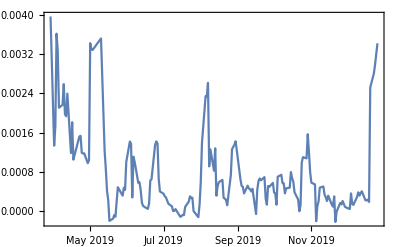

```mathematica
DateListPlot@Out[27]
```

```mathematica
Table[{First@First@o,Correlation[Map[Composition[Last,Last],o],Map[Composition[First,Last],o]]},{o,Out[26]}]
```

{{Fri 10 May 2019 00:00:00GMT-8.,0.897476},{Mon 13 May 2019 00:00:00GMT-8.,0.777684},{Tue 14 May 2019 00:00:00GMT-8.,0.823456},{Wed 15 May 2019 00:00:00GMT-8.,0.571099},{Thu 16 May 2019 00:00:00GMT-8.,0.838594},{Fri 17 May 2019 00:00:00GMT-8.,-0.569004},{Mon 20 May 2019 00:00:00GMT-8.,-0.40708},{Tue 21 May 2019 00:00:00GMT-8.,-0.185846},{Wed 22 May 2019 00:00:00GMT-8.,-0.530921},{Thu 23 May 2019 00:00:00GMT-8.,0.298363},{Fri 24 May 2019 00:00:00GMT-8.,0.789814},{Tue 28 May 2019 00:00:00GMT-8.,0.408509},{Wed 29 May 2019 00:00:00GMT-8.,0.582177},{Thu 30 May 2019 00:00:00GMT-8.,0.558025},{Fri 31 May 2019 00:00:00GMT-8.,0.843103},{Mon 3 Jun 2019 00:00:00GMT-8.,0.887457},{Tue 4 Jun 2019 00:00:00GMT-8.,0.910391},{Wed 5 Jun 2019 00:00:00GMT-8.,0.705269},{Thu 6 Jun 2019 00:00:00GMT-8.,0.88174},{Fri 7 Jun 2019 00:00:00GMT-8.,0.903959},{Mon 10 Jun 2019 00:00:00GMT-8.,0.888518},{Tue 11 Jun 2019 00:00:00GMT-8.,0.900708},{Wed 12 Jun 2019 00:00:00GMT-8.,0.561179},{Thu 13 Jun 2019 00:00:00GMT-8.,0.342094},{Fri 14 Jun 2019 00:00:00GMT-8.,0.248856},{Mon 17 Jun 2019 00:00:00GMT-8.,0.177176},{Tue 18 Jun 2019 00:00:00GMT-8.,0.147236},{Wed 19 Jun 2019 00:00:00GMT-8.,0.841864},{Thu 20 Jun 2019 00:00:00GMT-8.,0.87213},{Fri 21 Jun 2019 00:00:00GMT-8.,0.941956},{Mon 24 Jun 2019 00:00:00GMT-8.,0.960794},{Tue 25 Jun 2019 00:00:00GMT-8.,0.98459},{Wed 26 Jun 2019 00:00:00GMT-8.,0.97319},{Thu 27 Jun 2019 00:00:00GMT-8.,0.941124},{Fri 28 Jun 2019 00:00:00GMT-8.,0.81626},{Mon 1 Jul 2019 00:00:00GMT-8.,0.793636},{Tue 2 Jul 2019 00:00:00GMT-8.,0.826219},{Wed 3 Jul 2019 00:00:00GMT-8.,0.721401},{Fri 5 Jul 2019 00:00:00GMT-8.,0.439803},{Mon 8 Jul 2019 00:00:00GMT-8.,0.310343},{Tue 9 Jul 2019 00:00:00GMT-8.,-0.0268834},{Wed 10 Jul 2019 00:00:00GMT-8.,0.00392008},{Thu 11 Jul 2019 00:00:00GMT-8.,0.251206},{Fri 12 Jul 2019 00:00:00GMT-8.,-0.0714663},{Mon 15 Jul 2019 00:00:00GMT-8.,-0.71934},{Tue 16 Jul 2019 00:00:00GMT-8.,-0.557428},{Wed 17 Jul 2019 00:00:00GMT-8.,-0.426512},{Thu 18 Jul 2019 00:00:00GMT-8.,-0.454766},{Fri 19 Jul 2019 00:00:00GMT-8.,0.434713},{Mon 22 Jul 2019 00:00:00GMT-8.,0.867535},{Tue 23 Jul 2019 00:00:00GMT-8.,0.916765},{Wed 24 Jul 2019 00:00:00GMT-8.,0.855025},{Thu 25 Jul 2019 00:00:00GMT-8.,0.915445},{Fri 26 Jul 2019 00:00:00GMT-8.,-0.183244},{Mon 29 Jul 2019 00:00:00GMT-8.,-0.663479},{Tue 30 Jul 2019 00:00:00GMT-8.,-0.595508},{Wed 31 Jul 2019 00:00:00GMT-8.,0.308726},{Thu 1 Aug 2019 00:00:00GMT-8.,0.572492},{Fri 2 Aug 2019 00:00:00GMT-8.,0.750231},{Mon 5 Aug 2019 00:00:00GMT-8.,0.927896},{Tue 6 Aug 2019 00:00:00GMT-8.,0.826318},{Wed 7 Aug 2019 00:00:00GMT-8.,0.833767},{Thu 8 Aug 2019 00:00:00GMT-8.,0.823024},{Fri 9 Aug 2019 00:00:00GMT-8.,0.605514},{Mon 12 Aug 2019 00:00:00GMT-8.,0.507122},{Tue 13 Aug 2019 00:00:00GMT-8.,0.723673},{Wed 14 Aug 2019 00:00:00GMT-8.,0.341807},{Thu 15 Aug 2019 00:00:00GMT-8.,0.430862},{Fri 16 Aug 2019 00:00:00GMT-8.,0.892668},{Mon 19 Aug 2019 00:00:00GMT-8.,0.823329},{Tue 20 Aug 2019 00:00:00GMT-8.,0.742323},{Wed 21 Aug 2019 00:00:00GMT-8.,0.736419},{Thu 22 Aug 2019 00:00:00GMT-8.,0.681658},{Fri 23 Aug 2019 00:00:00GMT-8.,0.508832},{Mon 26 Aug 2019 00:00:00GMT-8.,0.912351},{Tue 27 Aug 2019 00:00:00GMT-8.,0.933048},{Wed 28 Aug 2019 00:00:00GMT-8.,0.936574},{Thu 29 Aug 2019 00:00:00GMT-8.,0.991502},{Fri 30 Aug 2019 00:00:00GMT-8.,0.996131},{Tue 3 Sep 2019 00:00:00GMT-8.,0.991501},{Wed 4 Sep 2019 00:00:00GMT-8.,0.903},{Thu 5 Sep 2019 00:00:00GMT-8.,0.851492},{Fri 6 Sep 2019 00:00:00GMT-8.,0.844989},{Mon 9 Sep 2019 00:00:00GMT-8.,0.931069},{Tue 10 Sep 2019 00:00:00GMT-8.,0.988294},{Wed 11 Sep 2019 00:00:00GMT-8.,0.790978},{Thu 12 Sep 2019 00:00:00GMT-8.,0.666335},{Fri 13 Sep 2019 00:00:00GMT-8.,0.66052},{Mon 16 Sep 2019 00:00:00GMT-8.,-0.188212},{Tue 17 Sep 2019 00:00:00GMT-8.,0.513589},{Wed 18 Sep 2019 00:00:00GMT-8.,0.627591},{Thu 19 Sep 2019 00:00:00GMT-8.,0.730386},{Fri 20 Sep 2019 00:00:00GMT-8.,0.661011},{Mon 23 Sep 2019 00:00:00GMT-8.,0.756616},{Tue 24 Sep 2019 00:00:00GMT-8.,0.725318},{Wed 25 Sep 2019 00:00:00GMT-8.,0.390718},{Thu 26 Sep 2019 00:00:00GMT-8.,0.697565},{Fri 27 Sep 2019 00:00:00GMT-8.,0.806768},{Mon 30 Sep 2019 00:00:00GMT-8.,0.820363},{Tue 1 Oct 2019 00:00:00GMT-8.,0.681028},{Wed 2 Oct 2019 00:00:00GMT-8.,0.779021},{Thu 3 Oct 2019 00:00:00GMT-8.,0.893529},{Fri 4 Oct 2019 00:00:00GMT-8.,0.86214},{Mon 7 Oct 2019 00:00:00GMT-8.,0.859463},{Tue 8 Oct 2019 00:00:00GMT-8.,0.899431},{Wed 9 Oct 2019 00:00:00GMT-8.,0.903054},{Thu 10 Oct 2019 00:00:00GMT-8.,0.843374},{Fri 11 Oct 2019 00:00:00GMT-8.,0.863913},{Mon 14 Oct 2019 00:00:00GMT-8.,0.866299},{Tue 15 Oct 2019 00:00:00GMT-8.,0.89825},{Wed 16 Oct 2019 00:00:00GMT-8.,0.764869},{Thu 17 Oct 2019 00:00:00GMT-8.,0.747655},{Fri 18 Oct 2019 00:00:00GMT-8.,0.558484},{Mon 21 Oct 2019 00:00:00GMT-8.,0.407457},{Tue 22 Oct 2019 00:00:00GMT-8.,-0.0281091},{Wed 23 Oct 2019 00:00:00GMT-8.,0.288229},{Thu 24 Oct 2019 00:00:00GMT-8.,0.774795},{Fri 25 Oct 2019 00:00:00GMT-8.,0.74499},{Mon 28 Oct 2019 00:00:00GMT-8.,0.767589},{Tue 29 Oct 2019 00:00:00GMT-8.,0.747412},{Wed 30 Oct 2019 00:00:00GMT-8.,0.698468},{Thu 31 Oct 2019 00:00:00GMT-8.,0.588447},{Fri 1 Nov 2019 00:00:00GMT-8.,0.514916},{Mon 4 Nov 2019 00:00:00GMT-8.,0.458723},{Tue 5 Nov 2019 00:00:00GMT-8.,-0.498977},{Wed 6 Nov 2019 00:00:00GMT-8.,0.507534},{Thu 7 Nov 2019 00:00:00GMT-8.,0.752055},{Fri 8 Nov 2019 00:00:00GMT-8.,0.857852},{Mon 11 Nov 2019 00:00:00GMT-8.,0.734718},{Tue 12 Nov 2019 00:00:00GMT-8.,0.505604},{Wed 13 Nov 2019 00:00:00GMT-8.,0.354934},{Thu 14 Nov 2019 00:00:00GMT-8.,0.293801},{Fri 15 Nov 2019 00:00:00GMT-8.,0.391318},{Mon 18 Nov 2019 00:00:00GMT-8.,0.130848},{Tue 19 Nov 2019 00:00:00GMT-8.,0.0968039},{Wed 20 Nov 2019 00:00:00GMT-8.,0.365887},{Thu 21 Nov 2019 00:00:00GMT-8.,-0.832046},{Fri 22 Nov 2019 00:00:00GMT-8.,-0.0391489},{Mon 25 Nov 2019 00:00:00GMT-8.,0.787769},{Tue 26 Nov 2019 00:00:00GMT-8.,0.845532},{Wed 27 Nov 2019 00:00:00GMT-8.,0.858513},{Fri 29 Nov 2019 00:00:00GMT-8.,0.270227},{Mon 2 Dec 2019 00:00:00GMT-8.,0.166408},{Tue 3 Dec 2019 00:00:00GMT-8.,0.1293},{Wed 4 Dec 2019 00:00:00GMT-8.,0.586201},{Thu 5 Dec 2019 00:00:00GMT-8.,0.337105},{Fri 6 Dec 2019 00:00:00GMT-8.,0.467831},{Mon 9 Dec 2019 00:00:00GMT-8.,0.493662},{Tue 10 Dec 2019 00:00:00GMT-8.,0.566299},{Wed 11 Dec 2019 00:00:00GMT-8.,0.732757},{Thu 12 Dec 2019 00:00:00GMT-8.,0.821672},{Fri 13 Dec 2019 00:00:00GMT-8.,0.6738},{Mon 16 Dec 2019 00:00:00GMT-8.,0.626428},{Tue 17 Dec 2019 00:00:00GMT-8.,0.754924},{Wed 18 Dec 2019 00:00:00GMT-8.,0.890181},{Thu 19 Dec 2019 00:00:00GMT-8.,0.495023},{Fri 20 Dec 2019 00:00:00GMT-8.,0.899529},{Mon 23 Dec 2019 00:00:00GMT-8.,0.983839},{Tue 24 Dec 2019 00:00:00GMT-8.,0.984804},{Thu 26 Dec 2019 00:00:00GMT-8.,0.989971},{Fri 29 Mar 2019 00:00:00GMT-8.,1.},{Mon 1 Apr 2019 00:00:00GMT-8.,1.},{Tue 2 Apr 2019 00:00:00GMT-8.,1.},{Wed 3 Apr 2019 00:00:00GMT-8.,1.},{Thu 4 Apr 2019 00:00:00GMT-8.,1.},{Fri 5 Apr 2019 00:00:00GMT-8.,1.},{Mon 8 Apr 2019 00:00:00GMT-8.,1.},{Tue 9 Apr 2019 00:00:00GMT-8.,1.},{Wed 10 Apr 2019 00:00:00GMT-8.,1.},{Thu 11 Apr 2019 00:00:00GMT-8.,1.},{Fri 12 Apr 2019 00:00:00GMT-8.,1.},{Mon 15 Apr 2019 00:00:00GMT-8.,1.},{Tue 16 Apr 2019 00:00:00GMT-8.,1.},{Wed 17 Apr 2019 00:00:00GMT-8.,1.},{Thu 18 Apr 2019 00:00:00GMT-8.,1.},{Mon 22 Apr 2019 00:00:00GMT-8.,1.},{Tue 23 Apr 2019 00:00:00GMT-8.,1.},{Wed 24 Apr 2019 00:00:00GMT-8.,1.},{Thu 25 Apr 2019 00:00:00GMT-8.,1.},{Fri 26 Apr 2019 00:00:00GMT-8.,1.},{Mon 29 Apr 2019 00:00:00GMT-8.,1.},{Tue 30 Apr 2019 00:00:00GMT-8.,1.},{Wed 1 May 2019 00:00:00GMT-8.,1.},{Thu 2 May 2019 00:00:00GMT-8.,1.},{Fri 3 May 2019 00:00:00GMT-8.,1.}}

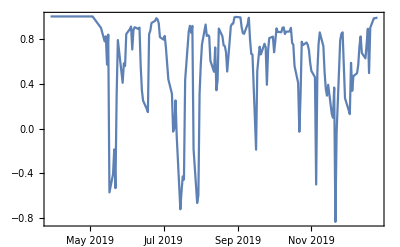

```mathematica
DateListPlot[Out[29]]
```

```mathematica
FinancialData["NYSE:CVX","Name"]
```

Chevron

```mathematica
FinancialData["NYSE:CVX","Dividend"]
```

Missing[NotAvailable]

```mathematica
FinancialData["NYSE:CVX","Close"]
```

120.30 $

```mathematica
FinancialData["NYSE:CVX","Lookup"]
```

{NYSE:CVX}

```mathematica
FinancialData["NYSE:CVX","Company"]
```

Chevron

```mathematica
Entity["Company","ChevronCorporation::tj685"]["TotalRevenue"]
```

1.52955×10^11 $

```mathematica
FinancialData["Nasdaq"]
```

{NASDAQ:AABA,NASDAQ:AAL,NASDAQ:AAME,NASDAQ:AAOI,NASDAQ:AAON,NASDAQ:AAPL,NASDAQ:AAWW,NASDAQ:AAXJ,NASDAQ:AAXN,NASDAQ:ABCB,NASDAQ:ABDC,NASDAQ:ABEO,NASDAQ:ABIL,NASDAQ:ABIO,NASDAQ:ABMD,NASDAQ:ABTX,NASDAQ:ABUS,NASDAQ:ACAD,NASDAQ:ACAM,NASDAQ:ACAMU,NASDAQ:ACBI,NASDAQ:ACER,NASDAQ:ACGL,NASDAQ:ACGLO,NASDAQ:ACGLP,NASDAQ:ACHC,NASDAQ:ACHN,NASDAQ:ACHV,NASDAQ:ACIA,NASDAQ:ACIU,NASDAQ:ACIW,NASDAQ:ACLS,NASDAQ:ACMR,NASDAQ:ACNB,NASDAQ:ACOR,NASDAQ:ACRS,NASDAQ:ACRX,NASDAQ:ACST,NASDAQ:ACT,NASDAQ:ACTG,NASDAQ:ACTT,NASDAQ:ACTTU,NASDAQ:ACWI,NASDAQ:ACWX,NASDAQ:ADAP,NASDAQ:ADBE,NASDAQ:ADES,NASDAQ:ADI,NASDAQ:ADIL,NASDAQ:ADMA,NASDAQ:ADMP,NASDAQ:ADMS,NASDAQ:ADOM,NASDAQ:ADP,NASDAQ:ADRA,NASDAQ:ADRD,NASDAQ:ADRE,NASDAQ:ADRO,NASDAQ:ADRU,NASDAQ:ADSK,NASDAQ:ADTN,NASDAQ:ADUS,NASDAQ:ADVM,NASDAQ:ADXS,NASDAQ:ADYX,NASDAQ:AEGN,NASDAQ:AEHR,NASDAQ:AEIS,NASDAQ:AEMD,NASDAQ:AERI,NASDAQ:AETI,NASDAQ:AEY,NASDAQ:AEYE,NASDAQ:AEZS,NASDAQ:AFH,NASDAQ:AFIN,NASDAQ:AFINP,NASDAQ:AFMD,NASDAQ:AGBAU,NASDAQ:AGEN,NASDAQ:AGFS,NASDAQ:AGIO,NASDAQ:AGLE,NASDAQ:AGMH,NASDAQ:AGNC,NASDAQ:AGNCB,NASDAQ:AGNCM,NASDAQ:AGNCN,NASDAQ:AGND,NASDAQ:AGRX,NASDAQ:AGTC,NASDAQ:AGYS,NASDAQ:AGZD,NASDAQ:AHPI,NASDAQ:AIA,NASDAQ:AIHS,NASDAQ:AIMC,NASDAQ:AIMT,NASDAQ:AINV,NASDAQ:AIPT,NASDAQ:AIQ,NASDAQ:AIRG,NASDAQ:AIRR,NASDAQ:AIRT,NASDAQ:AITB,NASDAQ:AKAM,NASDAQ:AKBA,NASDAQ:AKCA,NASDAQ:AKER,NASDAQ:AKRX,NASDAQ:AKTS,NASDAQ:AKTX,NASDAQ:ALAC,NASDAQ:ALACU,NASDAQ:ALBO,NASDAQ:ALCO,NASDAQ:ALDR,NASDAQ:ALDX,NASDAQ:ALEC,NASDAQ:ALGN,NASDAQ:ALGR,NASDAQ:ALGRU,NASDAQ:ALGT,NASDAQ:ALIM,NASDAQ:ALIT,NASDAQ:ALJJ,NASDAQ:ALKS,NASDAQ:ALLK,NASDAQ:ALLO,NASDAQ:ALLT,NASDAQ:ALNA,NASDAQ:ALNY,NASDAQ:ALOT,NASDAQ:ALPN,NASDAQ:ALRM,NASDAQ:ALRN,NASDAQ:ALSK,NASDAQ:ALT,NASDAQ:ALTM,NASDAQ:ALTR,NASDAQ:ALTY,NASDAQ:ALXN,NASDAQ:ALYA,NASDAQ:AMAG,NASDAQ:AMAL,NASDAQ:AMAT,NASDAQ:AMBA,NASDAQ:AMBC,NASDAQ:AMCA,NASDAQ:AMCI,NASDAQ:AMCIU,NASDAQ:AMCN,NASDAQ:AMCX,NASDAQ:AMD,NASDAQ:AMED,NASDAQ:AMEH,NASDAQ:AMGN,NASDAQ:AMKR,NASDAQ:AMNB,NASDAQ:AMOT,NASDAQ:AMPH,NASDAQ:AMR,NASDAQ:AMRB,NASDAQ:AMRH,NASDAQ:AMRK,NASDAQ:AMRN,NASDAQ:AMRS,NASDAQ:AMSC,NASDAQ:AMSF,NASDAQ:AMSWA,NASDAQ:AMTB,NASDAQ:AMTBB,NASDAQ:AMTD,NASDAQ:AMTX,NASDAQ:AMWD,NASDAQ:AMZN,NASDAQ:ANAB,NASDAQ:ANAT,NASDAQ:ANCN,NASDAQ:ANDA,NASDAQ:ANDAU,NASDAQ:ANDE,NASDAQ:ANGI,NASDAQ:ANGO,NASDAQ:ANIK,NASDAQ:ANIP,NASDAQ:ANIX,NASDAQ:ANSS,NASDAQ:ANY,NASDAQ:AOBC,NASDAQ:AOSL,NASDAQ:APDN,NASDAQ:APEI,NASDAQ:APEN,NASDAQ:APLS,NASDAQ:APLT,NASDAQ:APM,NASDAQ:APOG,NASDAQ:APOP,NASDAQ:APPF,NASDAQ:APPN,NASDAQ:APPS,NASDAQ:APTO,NASDAQ:APTX,NASDAQ:APVO,NASDAQ:APWC,NASDAQ:APYX,NASDAQ:AQB,NASDAQ:AQMS,NASDAQ:AQST,NASDAQ:AQXP,NASDAQ:ARAV,NASDAQ:ARAY,NASDAQ:ARCB,NASDAQ:ARCC,NASDAQ:ARCE,NASDAQ:ARCI,NASDAQ:ARCT,NASDAQ:ARCW,NASDAQ:ARDS,NASDAQ:ARDX,NASDAQ:AREC,NASDAQ:AREX,NASDAQ:ARGX,NASDAQ:ARKR,NASDAQ:ARLP,NASDAQ:ARNA,NASDAQ:AROW,NASDAQ:ARPO,NASDAQ:ARQL,NASDAQ:ARRY,NASDAQ:ARTNA,NASDAQ:ARTW,NASDAQ:ARTX,NASDAQ:ARVN,NASDAQ:ARWR,NASDAQ:ARYA,NASDAQ:ARYAU,NASDAQ:ASCMA,NASDAQ:ASET,NASDAQ:ASFI,NASDAQ:ASLN,NASDAQ:ASMB,NASDAQ:ASML,NASDAQ:ASNA,NASDAQ:ASND,NASDAQ:ASPS,NASDAQ:ASPU,NASDAQ:ASRT,NASDAQ:ASRV,NASDAQ:ASRVP,NASDAQ:ASTC,NASDAQ:ASTE,NASDAQ:ASUR,NASDAQ:ASV,NASDAQ:ASYS,NASDAQ:ATAI,NASDAQ:ATAX,NASDAQ:ATEC,NASDAQ:ATHE,NASDAQ:ATHX,NASDAQ:ATIF,NASDAQ:ATIS,NASDAQ:ATLC,NASDAQ:ATLO,NASDAQ:ATNI,NASDAQ:ATNX,NASDAQ:ATOM,NASDAQ:ATOS,NASDAQ:ATRA,NASDAQ:ATRC,NASDAQ:ATRI,NASDAQ:ATRO,NASDAQ:ATRS,NASDAQ:ATSG,NASDAQ:ATVI,NASDAQ:ATXI,NASDAQ:AUBN,NASDAQ:AUDC,NASDAQ:AUPH,NASDAQ:AUTL,NASDAQ:AUTO,NASDAQ:AVAV,NASDAQ:AVCO,NASDAQ:AVDL,NASDAQ:AVDR,NASDAQ:AVEO,NASDAQ:AVGO,NASDAQ:AVGR,NASDAQ:AVID,NASDAQ:AVNW,NASDAQ:AVRO,NASDAQ:AVT,NASDAQ:AVXL,NASDAQ:AWRE,NASDAQ:AWSM,NASDAQ:AXAS,NASDAQ:AXDX,NASDAQ:AXGN,NASDAQ:AXGT,NASDAQ:AXLA,NASDAQ:AXNX,NASDAQ:AXSM,NASDAQ:AXTI,NASDAQ:AY,NASDAQ:AYTU,NASDAQ:AZPN,NASDAQ:AZRX,NASDAQ:BABY,NASDAQ:BAND,NASDAQ:BANF,NASDAQ:BANFP,NASDAQ:BANR,NASDAQ:BANX,NASDAQ:BASI,NASDAQ:BATRA,NASDAQ:BATRK,NASDAQ:BBBY,NASDAQ:BBCP,NASDAQ:BBGI,NASDAQ:BBH,NASDAQ:BBSI,NASDAQ:BCACU,NASDAQ:BCBP,NASDAQ:BCLI,NASDAQ:BCML,NASDAQ:BCNA,NASDAQ:BCOM,NASDAQ:BCOR,NASDAQ:BCOV,NASDAQ:BCOW,NASDAQ:BCPC,NASDAQ:BCRX,NASDAQ:BCTF,NASDAQ:BCYC,NASDAQ:BDGE,NASDAQ:BDSI,NASDAQ:BEAT,NASDAQ:BECN,NASDAQ:BEER,NASDAQ:BELFA,NASDAQ:BELFB,NASDAQ:BFC,NASDAQ:BFIN,NASDAQ:BFIT,NASDAQ:BFL,NASDAQ:BFRA,NASDAQ:BFST,NASDAQ:BGCP,NASDAQ:BGFV,NASDAQ:BGNE,NASDAQ:BGRN,NASDAQ:BHAT,NASDAQ:BHF,NASDAQ:BHFAP,NASDAQ:BHTG,NASDAQ:BIB,NASDAQ:BICK,NASDAQ:BIDU,NASDAQ:BIIB,NASDAQ:BILI,NASDAQ:BIMI,NASDAQ:BIOC,NASDAQ:BIOL,NASDAQ:BIOS,NASDAQ:BIQI,NASDAQ:BIS,NASDAQ:BJRI,NASDAQ:BKCC,NASDAQ:BKCH,NASDAQ:BKEP,NASDAQ:BKEPP,NASDAQ:BKNG,NASDAQ:BKSC,NASDAQ:BKYI,NASDAQ:BL,NASDAQ:BLBD,NASDAQ:BLCM,NASDAQ:BLCN,NASDAQ:BLDP,NASDAQ:BLDR,NASDAQ:BLFS,NASDAQ:BLIN,NASDAQ:BLKB,NASDAQ:BLMN,NASDAQ:BLNK,NASDAQ:BLPH,NASDAQ:BLRX,NASDAQ:BLUE,NASDAQ:BMCH,NASDAQ:BMLP,NASDAQ:BMRA,NASDAQ:BMRC,NASDAQ:BMRN,NASDAQ:BMTC,NASDAQ:BND,NASDAQ:BNDW,NASDAQ:BNDX,NASDAQ:BNFT,NASDAQ:BNGO,NASDAQ:BNKL,NASDAQ:BNSO,NASDAQ:BNTC,NASDAQ:BOCH,NASDAQ:BOKF,NASDAQ:BOLD,NASDAQ:BOMN,NASDAQ:BOOM,NASDAQ:BOSC,NASDAQ:BOTJ,NASDAQ:BOTZ,NASDAQ:BOXL,NASDAQ:BPFH,NASDAQ:BPMC,NASDAQ:BPOP,NASDAQ:BPOPM,NASDAQ:BPOPN,NASDAQ:BPR,NASDAQ:BPRAP,NASDAQ:BPRN,NASDAQ:BPTH,NASDAQ:BPY,NASDAQ:BPYPP,NASDAQ:BRAC,NASDAQ:BRACU,NASDAQ:BREW,NASDAQ:BRID,NASDAQ:BRKL,NASDAQ:BRKR,NASDAQ:BRKS,NASDAQ:BROG,NASDAQ:BROGU,NASDAQ:BRPA,NASDAQ:BRPAU,NASDAQ:BRQS,NASDAQ:BRY,NASDAQ:BSET,NASDAQ:BSGM,NASDAQ:BSPCU,NASDAQ:BSQR,NASDAQ:BSRR,NASDAQ:BSTC,NASDAQ:BSVN,NASDAQ:BTAI,NASDAQ:BTEC,NASDAQ:BURG,NASDAQ:BUSE,NASDAQ:BVNSC,NASDAQ:BVSN,NASDAQ:BVXV,NASDAQ:BWAY,NASDAQ:BWB,NASDAQ:BWEN,NASDAQ:BWFG,NASDAQ:BWMC,NASDAQ:BWMCU,NASDAQ:BYFC,NASDAQ:BYND,NASDAQ:BYSI,NASDAQ:BZUN,NASDAQ:CAAS,NASDAQ:CAC,NASDAQ:CACC,NASDAQ:CACG,NASDAQ:CADC,NASDAQ:CAKE,NASDAQ:CALA,NASDAQ:CALM,NASDAQ:CAMP,NASDAQ:CAMT,NASDAQ:CAPR,NASDAQ:CAR,NASDAQ:CARA,NASDAQ:CARB,NASDAQ:CARE,NASDAQ:CARG,NASDAQ:CARO,NASDAQ:CART,NASDAQ:CARV,NASDAQ:CARZ,NASDAQ:CASA,NASDAQ:CASH,NASDAQ:CASI,NASDAQ:CASS,NASDAQ:CASY,NASDAQ:CATB,NASDAQ:CATC,NASDAQ:CATH,NASDAQ:CATM,NASDAQ:CATS,NASDAQ:CATY,NASDAQ:CBAN,NASDAQ:CBAT,NASDAQ:CBAY,NASDAQ:CBFV,NASDAQ:CBIO,NASDAQ:CBLI,NASDAQ:CBLK,NASDAQ:CBMB,NASDAQ:CBMG,NASDAQ:CBNK,NASDAQ:CBPO,NASDAQ:CBRL,NASDAQ:CBSH,NASDAQ:CBSHP,NASDAQ:CBTX,NASDAQ:CBUS,NASDAQ:CCB,NASDAQ:CCBG,NASDAQ:CCCL,NASDAQ:CCD,NASDAQ:CCIH,NASDAQ:CCLP,NASDAQ:CCMP,NASDAQ:CCNE,NASDAQ:CCNI,NASDAQ:CCOI,NASDAQ:CCRC,NASDAQ:CCRN,NASDAQ:CCXI,NASDAQ:CDC,NASDAQ:CDEV,NASDAQ:CDK,NASDAQ:CDL,NASDAQ:CDLX,NASDAQ:CDMO,NASDAQ:CDMOP,NASDAQ:CDNA,NASDAQ:CDNS,NASDAQ:CDTX,NASDAQ:CDW,NASDAQ:CDXC,NASDAQ:CDXS,NASDAQ:CDZI,NASDAQ:CECE,NASDAQ:CECO,NASDAQ:CELC,NASDAQ:CELG,NASDAQ:CELH,NASDAQ:CEMI,NASDAQ:CENT,NASDAQ:CENTA,NASDAQ:CENX,NASDAQ:CERC,NASDAQ:CERN,NASDAQ:CERS,NASDAQ:CETV,NASDAQ:CETX,NASDAQ:CETXP,NASDAQ:CEVA,NASDAQ:CEY,NASDAQ:CEZ,NASDAQ:CFA,NASDAQ:CFBI,NASDAQ:CFBK,NASDAQ:CFFA,NASDAQ:CFFAU,NASDAQ:CFFI,NASDAQ:CFFN,NASDAQ:CFMS,NASDAQ:CFO,NASDAQ:CFRX,NASDAQ:CG,NASDAQ:CGBD,NASDAQ:CGEN,NASDAQ:CGIX,NASDAQ:CGNX,NASDAQ:CGO,NASDAQ:CHCI,NASDAQ:CHCO,NASDAQ:CHDN,NASDAQ:CHEF,NASDAQ:CHEK,NASDAQ:CHFC,NASDAQ:CHFS,NASDAQ:CHI,NASDAQ:CHKE,NASDAQ:CHKP,NASDAQ:CHMA,NASDAQ:CHMG,NASDAQ:CHNA,NASDAQ:CHNR,NASDAQ:CHRS,NASDAQ:CHRW,NASDAQ:CHSCL,NASDAQ:CHSCM,NASDAQ:CHSCN,NASDAQ:CHSCO,NASDAQ:CHSCP,NASDAQ:CHTR,NASDAQ:CHUY,NASDAQ:CHW,NASDAQ:CHY,NASDAQ:CIBR,NASDAQ:CID,NASDAQ:CIDM,NASDAQ:CIFS,NASDAQ:CIGI,NASDAQ:CIL,NASDAQ:CINF,NASDAQ:CIVB,NASDAQ:CIVBP,NASDAQ:CIZ,NASDAQ:CIZN,NASDAQ:CJJD,NASDAQ:CKPT,NASDAQ:CLAR,NASDAQ:CLBK,NASDAQ:CLBS,NASDAQ:CLCT,NASDAQ:CLDB,NASDAQ:CLDC,NASDAQ:CLDX,NASDAQ:CLFD,NASDAQ:CLGN,NASDAQ:CLIR,NASDAQ:CLLS,NASDAQ:CLMT,NASDAQ:CLNE,NASDAQ:CLOU,NASDAQ:CLPS,NASDAQ:CLRB,NASDAQ:CLRG,NASDAQ:CLRO,NASDAQ:CLSD,NASDAQ:CLSN,NASDAQ:CLUB,NASDAQ:CLVS,NASDAQ:CLWT,NASDAQ:CLXT,NASDAQ:CMCO,NASDAQ:CMCSA,NASDAQ:CMCT,NASDAQ:CMCTP,NASDAQ:CME,NASDAQ:CMFN,NASDAQ:CMLS,NASDAQ:CMPR,NASDAQ:CMRX,NASDAQ:CMTL,NASDAQ:CNAC,NASDAQ:CNACU,NASDAQ:CNAT,NASDAQ:CNBKA,NASDAQ:CNCE,NASDAQ:CNCR,NASDAQ:CNET,NASDAQ:CNFR,NASDAQ:CNMD,NASDAQ:CNOB,NASDAQ:CNSL,NASDAQ:CNST,NASDAQ:CNTF,NASDAQ:CNTY,NASDAQ:CNXN,NASDAQ:COCP,NASDAQ:CODA,NASDAQ:CODX,NASDAQ:COHR,NASDAQ:COHU,NASDAQ:COKE,NASDAQ:COLB,NASDAQ:COLL,NASDAQ:COLM,NASDAQ:COMM,NASDAQ:COMT,NASDAQ:CONE,NASDAQ:CONN,NASDAQ:COOP,NASDAQ:CORE,NASDAQ:CORT,NASDAQ:CORV,NASDAQ:COST,NASDAQ:COUP,NASDAQ:COWN,NASDAQ:CPAH,NASDAQ:CPHC,NASDAQ:CPIX,NASDAQ:CPLP,NASDAQ:CPRT,NASDAQ:CPRX,NASDAQ:CPSH,NASDAQ:CPSI,NASDAQ:CPSS,NASDAQ:CPST,NASDAQ:CPTA,NASDAQ:CPTI,NASDAQ:CRAI,NASDAQ:CRAY,NASDAQ:CRBP,NASDAQ:CREE,NASDAQ:CREG,NASDAQ:CRESY,NASDAQ:CREX,NASDAQ:CRIS,NASDAQ:CRMT,NASDAQ:CRNT,NASDAQ:CRNX,NASDAQ:CRON,NASDAQ:CROX,NASDAQ:CRSA,NASDAQ:CRSAU,NASDAQ:CRSP,NASDAQ:CRTO,NASDAQ:CRTX,NASDAQ:CRUS,NASDAQ:CRUSC,NASDAQ:CRVL,NASDAQ:CRVS,NASDAQ:CRWD,NASDAQ:CRWS,NASDAQ:CRZO,NASDAQ:CSA,NASDAQ:CSB,NASDAQ:CSBR,NASDAQ:CSCO,NASDAQ:CSF,NASDAQ:CSFL,NASDAQ:CSGP,NASDAQ:CSGS,NASDAQ:CSII,NASDAQ:CSIQ,NASDAQ:CSML,NASDAQ:CSOD,NASDAQ:CSPI,NASDAQ:CSQ,NASDAQ:CSSE,NASDAQ:CSSEP,NASDAQ:CSTE,NASDAQ:CSTR,NASDAQ:CSWC,NASDAQ:CSWI,NASDAQ:CSX,NASDAQ:CTAC,NASDAQ:CTACU,NASDAQ:CTAS,NASDAQ:CTBI,NASDAQ:CTG,NASDAQ:CTHR,NASDAQ:CTIB,NASDAQ:CTIC,NASDAQ:CTMX,NASDAQ:CTRC,NASDAQ:CTRE,NASDAQ:CTRL,NASDAQ:CTRM,NASDAQ:CTRN,NASDAQ:CTRP,NASDAQ:CTRV,NASDAQ:CTSH,NASDAQ:CTSO,NASDAQ:CTWS,NASDAQ:CTXR,NASDAQ:CTXS,NASDAQ:CUBA,NASDAQ:CUE,NASDAQ:CUI,NASDAQ:CUR,NASDAQ:CUTR,NASDAQ:CVBF,NASDAQ:CVCO,NASDAQ:CVCY,NASDAQ:CVET,NASDAQ:CVGI,NASDAQ:CVGW,NASDAQ:CVLT,NASDAQ:CVLY,NASDAQ:CVTI,NASDAQ:CVV,NASDAQ:CWBC,NASDAQ:CWBR,NASDAQ:CWCO,NASDAQ:CWST,NASDAQ:CXDC,NASDAQ:CXSE,NASDAQ:CY,NASDAQ:CYAD,NASDAQ:CYAN,NASDAQ:CYBE,NASDAQ:CYBR,NASDAQ:CYCC,NASDAQ:CYCCP,NASDAQ:CYCN,NASDAQ:CYOU,NASDAQ:CYRN,NASDAQ:CYRX,NASDAQ:CYTK,NASDAQ:CYTR,NASDAQ:CYTX,NASDAQ:CZFC,NASDAQ:CZNC,NASDAQ:CZR,NASDAQ:CZWI,NASDAQ:DAIO,NASDAQ:DAKT,NASDAQ:DALI,NASDAQ:DARE,NASDAQ:DAVE,NASDAQ:DAX,NASDAQ:DBVT,NASDAQ:DBX,NASDAQ:DCAR,NASDAQ:DCIX,NASDAQ:DCLN,NASDAQ:DCOM,NASDAQ:DCPH,NASDAQ:DDIV,NASDAQ:DDMX,NASDAQ:DDMXU,NASDAQ:DEACU,NASDAQ:DENN,NASDAQ:DERM,NASDAQ:DEST,NASDAQ:DFBH,NASDAQ:DFBHU,NASDAQ:DFFN,NASDAQ:DFNL,NASDAQ:DFRG,NASDAQ:DGICA,NASDAQ:DGICB,NASDAQ:DGII,NASDAQ:DGLD,NASDAQ:DGLY,NASDAQ:DGRE,NASDAQ:DGRS,NASDAQ:DGRW,NASDAQ:DHIL,NASDAQ:DHXM,NASDAQ:DINT,NASDAQ:DIOD,NASDAQ:DISCA,NASDAQ:DISCB,NASDAQ:DISCK,NASDAQ:DISH,NASDAQ:DJCO,NASDAQ:DLHC,NASDAQ:DLPN,NASDAQ:DLTH,NASDAQ:DLTR,NASDAQ:DMAC,NASDAQ:DMLP,NASDAQ:DMPI,NASDAQ:DMRC,NASDAQ:DNBF,NASDAQ:DNJR,NASDAQ:DNKN,NASDAQ:DNLI,NASDAQ:DOCU,NASDAQ:DOGZ,NASDAQ:DOMO,NASDAQ:DOOO,NASDAQ:DORM,NASDAQ:DOVA,NASDAQ:DOX,NASDAQ:DPHC,NASDAQ:DPHCU,NASDAQ:DRAD,NASDAQ:DRIO,NASDAQ:DRIV,NASDAQ:DRNA,NASDAQ:DRRX,NASDAQ:DRYS,NASDAQ:DSGX,NASDAQ:DSKE,NASDAQ:DSLV,NASDAQ:DSPG,NASDAQ:DSWL,NASDAQ:DTEA,NASDAQ:DTIL,NASDAQ:DTSS,NASDAQ:DUSA,NASDAQ:DVAX,NASDAQ:DVCR,NASDAQ:DVLU,NASDAQ:DVOL,NASDAQ:DVY,NASDAQ:DWAQ,NASDAQ:DWAS,NASDAQ:DWAT,NASDAQ:DWCR,NASDAQ:DWFI,NASDAQ:DWIN,NASDAQ:DWLD,NASDAQ:DWMC,NASDAQ:DWPP,NASDAQ:DWSH,NASDAQ:DWSN,NASDAQ:DWTR,NASDAQ:DXCM,NASDAQ:DXGE,NASDAQ:DXJS,NASDAQ:DXLG,NASDAQ:DXPE,NASDAQ:DXYN,NASDAQ:DYAI,NASDAQ:DYNT,NASDAQ:DYSL,NASDAQ:DZSI,NASDAQ:EA,NASDAQ:EARS,NASDAQ:EAST,NASDAQ:EBAY,NASDAQ:EBAYL,NASDAQ:EBIX,NASDAQ:EBIZ,NASDAQ:EBMT,NASDAQ:EBSB,NASDAQ:EBTC,NASDAQ:ECHO,NASDAQ:ECOL,NASDAQ:ECOR,NASDAQ:ECOW,NASDAQ:ECPG,NASDAQ:EDAP,NASDAQ:EDIT,NASDAQ:EDNT,NASDAQ:EDRY,NASDAQ:EDTX,NASDAQ:EDTXU,NASDAQ:EDUC,NASDAQ:EEFT,NASDAQ:EEI,NASDAQ:EEMA,NASDAQ:EFAS,NASDAQ:EFBI,NASDAQ:EFII,NASDAQ:EFOI,NASDAQ:EFSC,NASDAQ:EGAN,NASDAQ:EGBN,NASDAQ:EGLE,NASDAQ:EGOV,NASDAQ:EGRX,NASDAQ:EHR,NASDAQ:EHTH,NASDAQ:EIDX,NASDAQ:EIGI,NASDAQ:EIGR,NASDAQ:EKSO,NASDAQ:ELGX,NASDAQ:ELOX,NASDAQ:ELSE,NASDAQ:ELTK,NASDAQ:EMB,NASDAQ:EMCB,NASDAQ:EMCF,NASDAQ:EMCG,NASDAQ:EMCI,NASDAQ:EMIF,NASDAQ:EMKR,NASDAQ:EML,NASDAQ:EMMS,NASDAQ:EMXC,NASDAQ:ENDP,NASDAQ:ENFC,NASDAQ:ENG,NASDAQ:ENLV,NASDAQ:ENOB,NASDAQ:ENPH,NASDAQ:ENSG,NASDAQ:ENT,NASDAQ:ENTA,NASDAQ:ENTG,NASDAQ:ENTX,NASDAQ:ENZL,NASDAQ:EOLS,NASDAQ:EPAY,NASDAQ:EPIX,NASDAQ:EPSN,NASDAQ:EPZM,NASDAQ:EQ,NASDAQ:EQBK,NASDAQ:EQIX,NASDAQ:EQRR,NASDAQ:ERI,NASDAQ:ERIC,NASDAQ:ERIE,NASDAQ:ERII,NASDAQ:ERYP,NASDAQ:ESBK,NASDAQ:ESCA,NASDAQ:ESEA,NASDAQ:ESGD,NASDAQ:ESGE,NASDAQ:ESGG,NASDAQ:ESGR,NASDAQ:ESGRO,NASDAQ:ESGRP,NASDAQ:ESGU,NASDAQ:ESLT,NASDAQ:ESPR,NASDAQ:ESQ,NASDAQ:ESSA,NASDAQ:ESTA,NASDAQ:ESTR,NASDAQ:ESXB,NASDAQ:ETFC,NASDAQ:ETON,NASDAQ:ETSY,NASDAQ:ETTX,NASDAQ:EUFN,NASDAQ:EVBG,NASDAQ:EVER,NASDAQ:EVFM,NASDAQ:EVFTC,NASDAQ:EVGBC,NASDAQ:EVGN,NASDAQ:EVK,NASDAQ:EVLMC,NASDAQ:EVLO,NASDAQ:EVLV,NASDAQ:EVOK,NASDAQ:EVOL,NASDAQ:EVOP,NASDAQ:EVSI,NASDAQ:EVSTC,NASDAQ:EWBC,NASDAQ:EWJE,NASDAQ:EWJV,NASDAQ:EWZS,NASDAQ:EXAS,NASDAQ:EXDX,NASDAQ:EXEL,NASDAQ:EXFO,NASDAQ:EXLS,NASDAQ:EXPD,NASDAQ:EXPE,NASDAQ:EXPI,NASDAQ:EXPO,NASDAQ:EXTR,NASDAQ:EYE,NASDAQ:EYEG,NASDAQ:EYEN,NASDAQ:EYES,NASDAQ:EYPT,NASDAQ:EZPW,NASDAQ:FAAR,NASDAQ:FAB,NASDAQ:FAD,NASDAQ:FALN,NASDAQ:FAMI,NASDAQ:FANG,NASDAQ:FANH,NASDAQ:FARM,NASDAQ:FARO,NASDAQ:FAST,NASDAQ:FAT,NASDAQ:FATE,NASDAQ:FB,NASDAQ:FBIO,NASDAQ:FBIOP,NASDAQ:FBIZ,NASDAQ:FBMS,NASDAQ:FBNC,NASDAQ:FBSS,NASDAQ:FBZ,NASDAQ:FCA,NASDAQ:FCAL,NASDAQ:FCAN,NASDAQ:FCAP,NASDAQ:FCBC,NASDAQ:FCBP,NASDAQ:FCCO,NASDAQ:FCCY,NASDAQ:FCEF,NASDAQ:FCEL,NASDAQ:FCFS,NASDAQ:FCNCA,NASDAQ:FCSC,NASDAQ:FCVT,NASDAQ:FDBC,NASDAQ:FDEF,NASDAQ:FDIV,NASDAQ:FDNI,NASDAQ:FDT,NASDAQ:FDTS,NASDAQ:FDUS,NASDAQ:FEG,NASDAQ:FEIM,NASDAQ:FELE,NASDAQ:FEM,NASDAQ:FEMB,NASDAQ:FEMS,NASDAQ:FENC,NASDAQ:FEP,NASDAQ:FEUZ,NASDAQ:FEX,NASDAQ:FEYE,NASDAQ:FFBC,NASDAQ:FFBW,NASDAQ:FFHL,NASDAQ:FFIC,NASDAQ:FFIN,NASDAQ:FFIV,NASDAQ:FFNW,NASDAQ:FFWM,NASDAQ:FGBI,NASDAQ:FGEN,NASDAQ:FGM,NASDAQ:FHB,NASDAQ:FHK,NASDAQ:FHL,NASDAQ:FIBK,NASDAQ:FID,NASDAQ:FINX,NASDAQ:FISI,NASDAQ:FISV,NASDAQ:FITB,NASDAQ:FITBI,NASDAQ:FIVE,NASDAQ:FIVN,NASDAQ:FIXD,NASDAQ:FIXX,NASDAQ:FIZZ,NASDAQ:FJP,NASDAQ:FKO,NASDAQ:FKU,NASDAQ:FLDM,NASDAQ:FLEX,NASDAQ:FLGT,NASDAQ:FLIC,NASDAQ:FLIR,NASDAQ:FLKS,NASDAQ:FLL,NASDAQ:FLMN,NASDAQ:FLN,NASDAQ:FLNT,NASDAQ:FLWS,NASDAQ:FLXN,NASDAQ:FLXS,NASDAQ:FMAO,NASDAQ:FMB,NASDAQ:FMBH,NASDAQ:FMBI,NASDAQ:FMCI,NASDAQ:FMCIU,NASDAQ:FMHI,NASDAQ:FMK,NASDAQ:FMNB,NASDAQ:FNCB,NASDAQ:FNHC,NASDAQ:FNJN,NASDAQ:FNK,NASDAQ:FNKO,NASDAQ:FNLC,NASDAQ:FNSR,NASDAQ:FNWB,NASDAQ:FNX,NASDAQ:FNY,NASDAQ:FOCS,NASDAQ:FOLD,NASDAQ:FOMX,NASDAQ:FONR,NASDAQ:FORD,NASDAQ:FORK,NASDAQ:FORM,NASDAQ:FORR,NASDAQ:FORTY,NASDAQ:FOSL,NASDAQ:FOX,NASDAQ:FOXA,NASDAQ:FOXF,NASDAQ:FPA,NASDAQ:FPAY,NASDAQ:FPRX,NASDAQ:FPXE,NASDAQ:FPXI,NASDAQ:FRAF,NASDAQ:FRAN,NASDAQ:FRBA,NASDAQ:FRBK,NASDAQ:FRED,NASDAQ:FRGI,NASDAQ:FRME,NASDAQ:FRPH,NASDAQ:FRPT,NASDAQ:FRSX,NASDAQ:FRTA,NASDAQ:FSBC,NASDAQ:FSBW,NASDAQ:FSCT,NASDAQ:FSFG,NASDAQ:FSLR,NASDAQ:FSTR,NASDAQ:FSV,NASDAQ:FSZ,NASDAQ:FTA,NASDAQ:FTAC,NASDAQ:FTACU,NASDAQ:FTAG,NASDAQ:FTC,NASDAQ:FTCS,NASDAQ:FTD,NASDAQ:FTDR,NASDAQ:FTEK,NASDAQ:FTEO,NASDAQ:FTFT,NASDAQ:FTGC,NASDAQ:FTHI,NASDAQ:FTLB,NASDAQ:FTNT,NASDAQ:FTR,NASDAQ:FTRI,NASDAQ:FTSL,NASDAQ:FTSM,NASDAQ:FTSV,NASDAQ:FTXD,NASDAQ:FTXG,NASDAQ:FTXH,NASDAQ:FTXL,NASDAQ:FTXN,NASDAQ:FTXO,NASDAQ:FTXR,NASDAQ:FULT,NASDAQ:FUNC,NASDAQ:FUND,NASDAQ:FUSB,NASDAQ:FUV,NASDAQ:FV,NASDAQ:FVC,NASDAQ:FVCB,NASDAQ:FVE,NASDAQ:FWONA,NASDAQ:FWONK,NASDAQ:FWP,NASDAQ:FWRD,NASDAQ:FXNC,NASDAQ:FYC,NASDAQ:FYT,NASDAQ:FYX,NASDAQ:GABC,NASDAQ:GAIA,NASDAQ:GAIN,NASDAQ:GAINL,NASDAQ:GAINM,NASDAQ:GALT,NASDAQ:GARS,NASDAQ:GASS,NASDAQ:GBCI,NASDAQ:GBDC,NASDAQ:GBLI,NASDAQ:GBT,NASDAQ:GCBC,NASDAQ:GDEN,NASDAQ:GDS,NASDAQ:GEC,NASDAQ:GECC,NASDAQ:GEMP,NASDAQ:GENC,NASDAQ:GENE,NASDAQ:GENY,NASDAQ:GEOS,NASDAQ:GERN,NASDAQ:GEVO,NASDAQ:GFED,NASDAQ:GFN,NASDAQ:GFNCP,NASDAQ:GGAL,NASDAQ:GH,NASDAQ:GHDX,NASDAQ:GHSI,NASDAQ:GIFI,NASDAQ:GIGM,NASDAQ:GIII,NASDAQ:GILD,NASDAQ:GILT,NASDAQ:GLAC,NASDAQ:GLACU,NASDAQ:GLAD,NASDAQ:GLADN,NASDAQ:GLBS,NASDAQ:GLBZ,NASDAQ:GLDD,NASDAQ:GLDI,NASDAQ:GLG,NASDAQ:GLIBA,NASDAQ:GLIBP,NASDAQ:GLMD,NASDAQ:GLNG,NASDAQ:GLPG,NASDAQ:GLPI,NASDAQ:GLRE,NASDAQ:GLUU,NASDAQ:GLYC,NASDAQ:GMDA,NASDAQ:GMHI,NASDAQ:GMHIU,NASDAQ:GMLP,NASDAQ:GMLPP,NASDAQ:GNCA,NASDAQ:GNFT,NASDAQ:GNLN,NASDAQ:GNMA,NASDAQ:GNMK,NASDAQ:GNMX,NASDAQ:GNOM,NASDAQ:GNPX,NASDAQ:GNTX,NASDAQ:GNTY,NASDAQ:GNUS,NASDAQ:GOGL,NASDAQ:GOGO,NASDAQ:GOOD,NASDAQ:GOODM,NASDAQ:GOODO,NASDAQ:GOODP,NASDAQ:GOOG,NASDAQ:GOOGL,NASDAQ:GOSS,NASDAQ:GPAQ,NASDAQ:GPAQU,NASDAQ:GPOR,NASDAQ:GPP,NASDAQ:GPRE,NASDAQ:GPRO,NASDAQ:GRBK,NASDAQ:GRFS,NASDAQ:GRID,NASDAQ:GRIF,NASDAQ:GRIN,NASDAQ:GRMN,NASDAQ:GRNQ,NASDAQ:GROW,NASDAQ:GRPN,NASDAQ:GRSH,NASDAQ:GRSHU,NASDAQ:GRTS,NASDAQ:GRVY,NASDAQ:GSBC,NASDAQ:GSHD,NASDAQ:GSIT,NASDAQ:GSKY,NASDAQ:GSM,NASDAQ:GSUM,NASDAQ:GSVC,NASDAQ:GT,NASDAQ:GTHX,NASDAQ:GTIM,NASDAQ:GTLS,NASDAQ:GTXI,NASDAQ:GTYH,NASDAQ:GULF,NASDAQ:GURE,NASDAQ:GVP,NASDAQ:GWGH,NASDAQ:GWPH,NASDAQ:GWRS,NASDAQ:GXGXU,NASDAQ:GYRO,NASDAQ:HA,NASDAQ:HABT,NASDAQ:HAFC,NASDAQ:HAIN,NASDAQ:HAIR,NASDAQ:HALL,NASDAQ:HALO,NASDAQ:HARP,NASDAQ:HAS,NASDAQ:HAYN,NASDAQ:HBAN,NASDAQ:HBANN,NASDAQ:HBANO,NASDAQ:HBCP,NASDAQ:HBIO,NASDAQ:HBMD,NASDAQ:HBNC,NASDAQ:HBP,NASDAQ:HCAC,NASDAQ:HCACU,NASDAQ:HCAP,NASDAQ:HCCH,NASDAQ:HCCHU,NASDAQ:HCCI,NASDAQ:HCKT,NASDAQ:HCM,NASDAQ:HCSG,NASDAQ:HDS,NASDAQ:HDSN,NASDAQ:HEAR,NASDAQ:HEBT,NASDAQ:HEES,NASDAQ:HELE,NASDAQ:HERD,NASDAQ:HEWG,NASDAQ:HFBC,NASDAQ:HFBL,NASDAQ:HFFG,NASDAQ:HFWA,NASDAQ:HGSH,NASDAQ:HHHH,NASDAQ:HHHHU,NASDAQ:HHR,NASDAQ:HIBB,NASDAQ:HIFS,NASDAQ:HIHO,NASDAQ:HIIQ,NASDAQ:HIMX,NASDAQ:HJLI,NASDAQ:HLG,NASDAQ:HLIT,NASDAQ:HLNE,NASDAQ:HMHC,NASDAQ:HMNF,NASDAQ:HMST,NASDAQ:HMSY,NASDAQ:HMTV,NASDAQ:HNDL,NASDAQ:HNNA,NASDAQ:HNRG,NASDAQ:HOFT,NASDAQ:HOLI,NASDAQ:HOLX,NASDAQ:HOMB,NASDAQ:HONE,NASDAQ:HOOK,NASDAQ:HOPE,NASDAQ:HOTH,NASDAQ:HOVNP,NASDAQ:HPJ,NASDAQ:HPT,NASDAQ:HQY,NASDAQ:HROW,NASDAQ:HRTX,NASDAQ:HRZN,NASDAQ:HSACU,NASDAQ:HSDT,NASDAQ:HSGX,NASDAQ:HSIC,NASDAQ:HSII,NASDAQ:HSKA,NASDAQ:HSON,NASDAQ:HSTM,NASDAQ:HTBI,NASDAQ:HTBK,NASDAQ:HTBX,NASDAQ:HTGM,NASDAQ:HTHT,NASDAQ:HTLD,NASDAQ:HTLF,NASDAQ:HUBG,NASDAQ:HURC,NASDAQ:HURN,NASDAQ:HVBC,NASDAQ:HWBK,NASDAQ:HWC,NASDAQ:HWCC,NASDAQ:HWKN,NASDAQ:HX,NASDAQ:HYACU,NASDAQ:HYGS,NASDAQ:HYLS,NASDAQ:HYND,NASDAQ:HYRE,NASDAQ:HYXE,NASDAQ:HYZD,NASDAQ:HZNP,NASDAQ:IAC,NASDAQ:IART,NASDAQ:IBB,NASDAQ:IBCP,NASDAQ:IBEX,NASDAQ:IBKC,NASDAQ:IBKCN,NASDAQ:IBKCO,NASDAQ:IBKCP,NASDAQ:IBOC,NASDAQ:IBTX,NASDAQ:IBUY,NASDAQ:ICAD,NASDAQ:ICBK,NASDAQ:ICCC,NASDAQ:ICCH,NASDAQ:ICFI,NASDAQ:ICHR,NASDAQ:ICLK,NASDAQ:ICLN,NASDAQ:ICLR,NASDAQ:ICON,NASDAQ:ICPT,NASDAQ:ICUI,NASDAQ:IDCC,NASDAQ:IDEX,NASDAQ:IDLB,NASDAQ:IDRA,NASDAQ:IDSA,NASDAQ:IDSY,NASDAQ:IDXG,NASDAQ:IDXX,NASDAQ:IDYA,NASDAQ:IEA,NASDAQ:IEF,NASDAQ:IEI,NASDAQ:IEP,NASDAQ:IESC,NASDAQ:IEUS,NASDAQ:IFEU,NASDAQ:IFGL,NASDAQ:IFMK,NASDAQ:IFRX,NASDAQ:IFV,NASDAQ:IGF,NASDAQ:IGIB,NASDAQ:IGLD,NASDAQ:IGOV,NASDAQ:IGSB,NASDAQ:III,NASDAQ:IIIN,NASDAQ:IIIV,NASDAQ:IIN,NASDAQ:IIVI,NASDAQ:IJT,NASDAQ:IKNX,NASDAQ:ILMN,NASDAQ:ILPT,NASDAQ:ILSAP,NASDAQ:IMAC,NASDAQ:IMGN,NASDAQ:IMI,NASDAQ:IMKTA,NASDAQ:IMMP,NASDAQ:IMMR,NASDAQ:IMMU,NASDAQ:IMOS,NASDAQ:IMRN,NASDAQ:IMTE,NASDAQ:IMUX,NASDAQ:IMV,NASDAQ:IMXI,NASDAQ:INAP,NASDAQ:INBK,NASDAQ:INCY,NASDAQ:INDB,NASDAQ:INDY,NASDAQ:INFI,NASDAQ:INFN,NASDAQ:INFO,NASDAQ:INFR,NASDAQ:INGN,NASDAQ:INMB,NASDAQ:INNT,NASDAQ:INO,NASDAQ:INOD,NASDAQ:INOV,NASDAQ:INPX,NASDAQ:INSE,NASDAQ:INSG,NASDAQ:INSM,NASDAQ:INSU,NASDAQ:INSUU,NASDAQ:INSY,NASDAQ:INTC,NASDAQ:INTG,NASDAQ:INTL,NASDAQ:INTU,NASDAQ:INVA,NASDAQ:INVE,NASDAQ:INWK,NASDAQ:IONS,NASDAQ:IOSP,NASDAQ:IOTS,NASDAQ:IOVA,NASDAQ:IPAR,NASDAQ:IPDN,NASDAQ:IPGP,NASDAQ:IPHS,NASDAQ:IPIC,NASDAQ:IPKW,NASDAQ:IPLDP,NASDAQ:IPWR,NASDAQ:IQ,NASDAQ:IRBT,NASDAQ:IRCP,NASDAQ:IRDM,NASDAQ:IRIX,NASDAQ:IRMD,NASDAQ:IROQ,NASDAQ:IRTC,NASDAQ:IRWD,NASDAQ:ISBC,NASDAQ:ISCA,NASDAQ:ISDS,NASDAQ:ISDX,NASDAQ:ISEE,NASDAQ:ISEM,NASDAQ:ISHG,NASDAQ:ISIG,NASDAQ:ISNS,NASDAQ:ISRG,NASDAQ:ISRL,NASDAQ:ISSC,NASDAQ:ISTB,NASDAQ:ISTR,NASDAQ:ITCI,NASDAQ:ITI,NASDAQ:ITIC,NASDAQ:ITMR,NASDAQ:ITRI,NASDAQ:ITRM,NASDAQ:ITRN,NASDAQ:IUS,NASDAQ:IUSB,NASDAQ:IUSG,NASDAQ:IUSS,NASDAQ:IUSV,NASDAQ:IVAC,NASDAQ:IVENC,NASDAQ:IVFGC,NASDAQ:IVFVC,NASDAQ:IXUS,NASDAQ:IZEA,NASDAQ:JACK,NASDAQ:JAGX,NASDAQ:JAKK,NASDAQ:JASN,NASDAQ:JAZZ,NASDAQ:JBHT,NASDAQ:JBLU,NASDAQ:JBSS,NASDAQ:JCOM,NASDAQ:JCS,NASDAQ:JCTCF,NASDAQ:JD,NASDAQ:JFIN,NASDAQ:JFK,NASDAQ:JFKKU,NASDAQ:JG,NASDAQ:JJSF,NASDAQ:JKHY,NASDAQ:JKI,NASDAQ:JMU,NASDAQ:JNCE,NASDAQ:JOBS,NASDAQ:JOUT,NASDAQ:JRJC,NASDAQ:JRSH,NASDAQ:JRVR,NASDAQ:JSMD,NASDAQ:JSML,NASDAQ:JSYN,NASDAQ:JSYNU,NASDAQ:JVA,NASDAQ:JYNT,NASDAQ:KALA,NASDAQ:KALU,NASDAQ:KALV,NASDAQ:KBAL,NASDAQ:KBLM,NASDAQ:KBLMU,NASDAQ:KBSF,NASDAQ:KBWB,NASDAQ:KBWD,NASDAQ:KBWP,NASDAQ:KBWR,NASDAQ:KBWY,NASDAQ:KE,NASDAQ:KELYA,NASDAQ:KELYB,NASDAQ:KEQU,NASDAQ:KEYW,NASDAQ:KFFB,NASDAQ:KFRC,NASDAQ:KGJI,NASDAQ:KHC,NASDAQ:KIDS,NASDAQ:KIN,NASDAQ:KINS,NASDAQ:KIRK,NASDAQ:KLAC,NASDAQ:KLDO,NASDAQ:KLIC,NASDAQ:KLXE,NASDAQ:KMDA,NASDAQ:KMPH,NASDAQ:KNDI,NASDAQ:KNSA,NASDAQ:KNSL,NASDAQ:KOD,NASDAQ:KOOL,NASDAQ:KOPN,NASDAQ:KOSS,NASDAQ:KPFS,NASDAQ:KPTI,NASDAQ:KRMA,NASDAQ:KRNT,NASDAQ:KRNY,NASDAQ:KRYS,NASDAQ:KTCC,NASDAQ:KTOS,NASDAQ:KTOV,NASDAQ:KURA,NASDAQ:KVHI,NASDAQ:KXIN,NASDAQ:KZIA,NASDAQ:KZR,NASDAQ:LABL,NASDAQ:LACQ,NASDAQ:LACQU,NASDAQ:LAKE,NASDAQ:LAMR,NASDAQ:LANC,NASDAQ:LAND,NASDAQ:LANDP,NASDAQ:LARK,NASDAQ:LASR,NASDAQ:LAUR,NASDAQ:LAWS,NASDAQ:LAZY,NASDAQ:LBAI,NASDAQ:LBC,NASDAQ:LBRDA,NASDAQ:LBRDK,NASDAQ:LBTYA,NASDAQ:LBTYB,NASDAQ:LBTYK,NASDAQ:LCAHU,NASDAQ:LCNB,NASDAQ:LCUT,NASDAQ:LDRI,NASDAQ:LDSF,NASDAQ:LE,NASDAQ:LECO,NASDAQ:LEDS,NASDAQ:LEGH,NASDAQ:LEGR,NASDAQ:LEVL,NASDAQ:LEXEA,NASDAQ:LEXEB,NASDAQ:LFAC,NASDAQ:LFACU,NASDAQ:LFUS,NASDAQ:LFVN,NASDAQ:LGCY,NASDAQ:LGIH,NASDAQ:LGND,NASDAQ:LHCG,NASDAQ:LIFE,NASDAQ:LILA,NASDAQ:LILAK,NASDAQ:LINC,NASDAQ:LIND,NASDAQ:LION,NASDAQ:LIQT,NASDAQ:LITE,NASDAQ:LIVE,NASDAQ:LIVN,NASDAQ:LIVX,NASDAQ:LJPC,NASDAQ:LK,NASDAQ:LKCO,NASDAQ:LKFN,NASDAQ:LKOR,NASDAQ:LKQ,NASDAQ:LLIT,NASDAQ:LLNW,NASDAQ:LMAT,NASDAQ:LMB,NASDAQ:LMBS,NASDAQ:LMFA,NASDAQ:LMNR,NASDAQ:LMNX,NASDAQ:LMRK,NASDAQ:LMRKN,NASDAQ:LMRKO,NASDAQ:LMRKP,NASDAQ:LMST,NASDAQ:LNDC,NASDAQ:LNGR,NASDAQ:LNT,NASDAQ:LNTH,NASDAQ:LOAC,NASDAQ:LOACU,NASDAQ:LOAN,NASDAQ:LOB,NASDAQ:LOCO,NASDAQ:LOGC,NASDAQ:LOGI,NASDAQ:LOGM,NASDAQ:LONE,NASDAQ:LOOP,NASDAQ:LOPE,NASDAQ:LORL,NASDAQ:LOVE,NASDAQ:LPCN,NASDAQ:LPLA,NASDAQ:LPSN,NASDAQ:LPTH,NASDAQ:LPTX,NASDAQ:LQDA,NASDAQ:LQDT,NASDAQ:LRAD,NASDAQ:LRCX,NASDAQ:LRGE,NASDAQ:LSBK,NASDAQ:LSCC,NASDAQ:LSTR,NASDAQ:LSXMA,NASDAQ:LSXMB,NASDAQ:LSXMK,NASDAQ:LTBR,NASDAQ:LTRPA,NASDAQ:LTRPB,NASDAQ:LTRX,NASDAQ:LTXB,NASDAQ:LULU,NASDAQ:LUNA,NASDAQ:LUNG,NASDAQ:LVHD,NASDAQ:LWAY,NASDAQ:LX,NASDAQ:LXRX,NASDAQ:LYFT,NASDAQ:LYL,NASDAQ:LYTS,NASDAQ:MACK,NASDAQ:MAGS,NASDAQ:MAMS,NASDAQ:MANH,NASDAQ:MANT,NASDAQ:MAR,NASDAQ:MARA,NASDAQ:MARK,NASDAQ:MARPS,NASDAQ:MASI,NASDAQ:MAT,NASDAQ:MATW,NASDAQ:MAYS,NASDAQ:MBB,NASDAQ:MBCN,NASDAQ:MBII,NASDAQ:MBIN,NASDAQ:MBINP,NASDAQ:MBIO,NASDAQ:MBOT,NASDAQ:MBRX,NASDAQ:MBSD,NASDAQ:MBTF,NASDAQ:MBUU,NASDAQ:MBVC,NASDAQ:MBWM,NASDAQ:MCBC,NASDAQ:MCEF,NASDAQ:MCEP,NASDAQ:MCFT,NASDAQ:MCHI,NASDAQ:MCHP,NASDAQ:MCHX,NASDAQ:MCRB,NASDAQ:MCRI,NASDAQ:MDB,NASDAQ:MDCA,NASDAQ:MDCO,NASDAQ:MDGL,NASDAQ:MDGS,NASDAQ:MDIV,NASDAQ:MDJH,NASDAQ:MDLZ,NASDAQ:MDRR,NASDAQ:MDRX,NASDAQ:MDSO,NASDAQ:MDWD,NASDAQ:MEDP,NASDAQ:MEET,NASDAQ:MEIP,NASDAQ:MELI,NASDAQ:MELR,NASDAQ:MEOH,NASDAQ:MERC,NASDAQ:MESA,NASDAQ:MESO,NASDAQ:METC,NASDAQ:MFIN,NASDAQ:MFNC,NASDAQ:MFSF,NASDAQ:MGEE,NASDAQ:MGEN,NASDAQ:MGI,NASDAQ:MGIC,NASDAQ:MGLN,NASDAQ:MGNX,NASDAQ:MGPI,NASDAQ:MGRC,NASDAQ:MGTA,NASDAQ:MGTX,NASDAQ:MGYR,NASDAQ:MHLD,NASDAQ:MICT,NASDAQ:MIDD,NASDAQ:MIK,NASDAQ:MILN,NASDAQ:MIME,NASDAQ:MIND,NASDAQ:MINDP,NASDAQ:MINI,NASDAQ:MIST,NASDAQ:MITK,NASDAQ:MITO,NASDAQ:MJCO,NASDAQ:MKGI,NASDAQ:MKSI,NASDAQ:MKTX,NASDAQ:MLAB,NASDAQ:MLCO,NASDAQ:MLHR,NASDAQ:MLND,NASDAQ:MLNT,NASDAQ:MLNX,NASDAQ:MLVF,NASDAQ:MMAC,NASDAQ:MMDM,NASDAQ:MMDMU,NASDAQ:MMLP,NASDAQ:MMSI,NASDAQ:MMYT,NASDAQ:MNCL,NASDAQ:MNCLU,NASDAQ:MNDO,NASDAQ:MNKD,NASDAQ:MNLO,NASDAQ:MNOV,NASDAQ:MNRO,NASDAQ:MNSB,NASDAQ:MNST,NASDAQ:MNTA,NASDAQ:MNTX,NASDAQ:MOBL,NASDAQ:MOFG,NASDAQ:MOGO,NASDAQ:MOMO,NASDAQ:MOR,NASDAQ:MORN,NASDAQ:MOSY,NASDAQ:MOTS,NASDAQ:MOXC,NASDAQ:MPAA,NASDAQ:MPB,NASDAQ:MPVD,NASDAQ:MPWR,NASDAQ:MRAM,NASDAQ:MRBK,NASDAQ:MRCC,NASDAQ:MRCY,NASDAQ:MREO,NASDAQ:MRIN,NASDAQ:MRKR,NASDAQ:MRLN,NASDAQ:MRNA,NASDAQ:MRNS,NASDAQ:MRSN,NASDAQ:MRTN,NASDAQ:MRTX,NASDAQ:MRUS,NASDAQ:MRVL,NASDAQ:MSBF,NASDAQ:MSBI,NASDAQ:MSEX,NASDAQ:MSFT,NASDAQ:MSON,NASDAQ:MSTR,NASDAQ:MSVB,NASDAQ:MTBC,NASDAQ:MTBCP,NASDAQ:MTC,NASDAQ:MTCH,NASDAQ:MTEC,NASDAQ:MTECU,NASDAQ:MTEM,NASDAQ:MTEX,NASDAQ:MTFB,NASDAQ:MTLS,NASDAQ:MTP,NASDAQ:MTRX,NASDAQ:MTSC,NASDAQ:MTSI,NASDAQ:MTSL,NASDAQ:MU,NASDAQ:MUDS,NASDAQ:MUDSU,NASDAQ:MVBF,NASDAQ:MVIS,NASDAQ:MWK,NASDAQ:MXIM,NASDAQ:MYFW,NASDAQ:MYGN,NASDAQ:MYL,NASDAQ:MYND,NASDAQ:MYOK,NASDAQ:MYOS,NASDAQ:MYRG,NASDAQ:MYSZ,NASDAQ:MYT,NASDAQ:NAII,NASDAQ:NAKD,NASDAQ:NANO,NASDAQ:NAOV,NASDAQ:NATH,NASDAQ:NATI,NASDAQ:NATR,NASDAQ:NAVI,NASDAQ:NBEV,NASDAQ:NBIX,NASDAQ:NBN,NASDAQ:NBRV,NASDAQ:NBTB,NASDAQ:NCBS,NASDAQ:NCMI,NASDAQ:NCNA,NASDAQ:NCSM,NASDAQ:NCTY,NASDAQ:NDAQ,NASDAQ:NDLS,NASDAQ:NDRA,NASDAQ:NDSN,NASDAQ:NEBU,NASDAQ:NEBUU,NASDAQ:NEO,NASDAQ:NEOG,NASDAQ:NEON,NASDAQ:NEOS,NASDAQ:NEPT,NASDAQ:NERV,NASDAQ:NESR,NASDAQ:NETE,NASDAQ:NEWA,NASDAQ:NEWT,NASDAQ:NEXT,NASDAQ:NFBK,NASDAQ:NFE,NASDAQ:NFLX,NASDAQ:NFTY,NASDAQ:NGHC,NASDAQ:NGHCN,NASDAQ:NGHCO,NASDAQ:NGHCP,NASDAQ:NGM,NASDAQ:NH,NASDAQ:NHLD,NASDAQ:NHTC,NASDAQ:NICE,NASDAQ:NICK,NASDAQ:NIHD,NASDAQ:NITE,NASDAQ:NIU,NASDAQ:NK,NASDAQ:NKSH,NASDAQ:NKTR,NASDAQ:NLNK,NASDAQ:NMCI,NASDAQ:NMIH,NASDAQ:NMRD,NASDAQ:NMRK,NASDAQ:NNBR,NASDAQ:NNDM,NASDAQ:NODK,NASDAQ:NOVN,NASDAQ:NOVT,NASDAQ:NRC,NASDAQ:NRIM,NASDAQ:NSEC,NASDAQ:NSIT,NASDAQ:NSSC,NASDAQ:NSTG,NASDAQ:NSYS,NASDAQ:NTAP,NASDAQ:NTCT,NASDAQ:NTEC,NASDAQ:NTES,NASDAQ:NTGN,NASDAQ:NTGR,NASDAQ:NTIC,NASDAQ:NTLA,NASDAQ:NTNX,NASDAQ:NTRA,NASDAQ:NTRP,NASDAQ:NTRS,NASDAQ:NTRSP,NASDAQ:NTWK,NASDAQ:NUAN,NASDAQ:NURO,NASDAQ:NUVA,NASDAQ:NVAX,NASDAQ:NVCN,NASDAQ:NVCR,NASDAQ:NVDA,NASDAQ:NVEC,NASDAQ:NVEE,NASDAQ:NVFY,NASDAQ:NVIV,NASDAQ:NVLN,NASDAQ:NVMI,NASDAQ:NVTR,NASDAQ:NVUS,NASDAQ:NWBI,NASDAQ:NWFL,NASDAQ:NWL,NASDAQ:NWLI,NASDAQ:NWPX,NASDAQ:NWS,NASDAQ:NWSA,NASDAQ:NXGN,NASDAQ:NXMD,NASDAQ:NXPI,NASDAQ:NXST,NASDAQ:NXTC,NASDAQ:NXTD,NASDAQ:NYMT,NASDAQ:NYMTN,NASDAQ:NYMTO,NASDAQ:NYMTP,NASDAQ:NYMX,NASDAQ:NYNY,NASDAQ:OASM,NASDAQ:OBAS,NASDAQ:OBCI,NASDAQ:OBLN,NASDAQ:OBNK,NASDAQ:OBSV,NASDAQ:OCC,NASDAQ:OCCI,NASDAQ:OCCIP,NASDAQ:OCFC,NASDAQ:OCSI,NASDAQ:OCSL,NASDAQ:OCUL,NASDAQ:ODFL,NASDAQ:ODP,NASDAQ:ODT,NASDAQ:OESX,NASDAQ:OFED,NASDAQ:OFIX,NASDAQ:OFLX,NASDAQ:OFS,NASDAQ:OHAI,NASDAQ:OHRP,NASDAQ:OIIM,NASDAQ:OKDCC,NASDAQ:OKTA,NASDAQ:OLBK,NASDAQ:OLD,NASDAQ:OLED,NASDAQ:OLLI,NASDAQ:OMAB,NASDAQ:OMCL,NASDAQ:OMER,NASDAQ:OMEX,NASDAQ:ON,NASDAQ:ONB,NASDAQ:ONCE,NASDAQ:ONCS,NASDAQ:ONCY,NASDAQ:ONEQ,NASDAQ:ONTX,NASDAQ:ONVO,NASDAQ:OPB,NASDAQ:OPBK,NASDAQ:OPES,NASDAQ:OPESU,NASDAQ:OPGN,NASDAQ:OPHC,NASDAQ:OPI,NASDAQ:OPK,NASDAQ:OPNT,NASDAQ:OPOF,NASDAQ:OPRA,NASDAQ:OPRX,NASDAQ:OPTN,NASDAQ:OPTT,NASDAQ:ORBC,NASDAQ:ORG,NASDAQ:ORGO,NASDAQ:ORGS,NASDAQ:ORIT,NASDAQ:ORLY,NASDAQ:ORMP,NASDAQ:ORRF,NASDAQ:ORTX,NASDAQ:OSBC,NASDAQ:OSBCP,NASDAQ:OSIS,NASDAQ:OSMT,NASDAQ:OSN,NASDAQ:OSPN,NASDAQ:OSS,NASDAQ:OSTK,NASDAQ:OSUR,NASDAQ:OSW,NASDAQ:OTEL,NASDAQ:OTEX,NASDAQ:OTIC,NASDAQ:OTIV,NASDAQ:OTLK,NASDAQ:OTTR,NASDAQ:OTTW,NASDAQ:OVBC,NASDAQ:OVID,NASDAQ:OVLY,NASDAQ:OXBR,NASDAQ:OXFD,NASDAQ:OXLC,NASDAQ:OXLCM,NASDAQ:OXLCO,NASDAQ:OXSQ,NASDAQ:OZK,NASDAQ:PAACU,NASDAQ:PAAS,NASDAQ:PACB,NASDAQ:PACQ,NASDAQ:PACQU,NASDAQ:PACW,NASDAQ:PAHC,NASDAQ:PANL,NASDAQ:PATI,NASDAQ:PATK,NASDAQ:PAVM,NASDAQ:PAYS,NASDAQ:PAYX,NASDAQ:PBBI,NASDAQ:PBCT,NASDAQ:PBCTP,NASDAQ:PBHC,NASDAQ:PBIP,NASDAQ:PBPB,NASDAQ:PBTS,NASDAQ:PBYI,NASDAQ:PCAR,NASDAQ:PCB,NASDAQ:PCH,NASDAQ:PCMI,NASDAQ:PCOM,NASDAQ:PCRX,NASDAQ:PCSB,NASDAQ:PCTI,NASDAQ:PCTY,NASDAQ:PCYG,NASDAQ:PCYO,NASDAQ:PDBC,NASDAQ:PDCE,NASDAQ:PDCO,NASDAQ:PDD,NASDAQ:PDEX,NASDAQ:PDFS,NASDAQ:PDLB,NASDAQ:PDLI,NASDAQ:PDP,NASDAQ:PDSB,NASDAQ:PDVW,NASDAQ:PEBK,NASDAQ:PEBO,NASDAQ:PEGA,NASDAQ:PEGI,NASDAQ:PEIX,NASDAQ:PENN,NASDAQ:PEP,NASDAQ:PERI,NASDAQ:PESI,NASDAQ:PETQ,NASDAQ:PETS,NASDAQ:PETX,NASDAQ:PETZ,NASDAQ:PEY,NASDAQ:PEZ,NASDAQ:PFBC,NASDAQ:PFBI,NASDAQ:PFF,NASDAQ:PFG,NASDAQ:PFI,NASDAQ:PFIE,NASDAQ:PFIN,NASDAQ:PFIS,NASDAQ:PFLT,NASDAQ:PFM,NASDAQ:PFMT,NASDAQ:PFPT,NASDAQ:PFSW,NASDAQ:PGC,NASDAQ:PGJ,NASDAQ:PGNX,NASDAQ:PHAS,NASDAQ:PHCF,NASDAQ:PHIO,NASDAQ:PHO,NASDAQ:PHUN,NASDAQ:PI,NASDAQ:PICO,NASDAQ:PID,NASDAQ:PIE,NASDAQ:PIH,NASDAQ:PIHPP,NASDAQ:PINC,NASDAQ:PIO,NASDAQ:PIRS,NASDAQ:PIXY,NASDAQ:PIZ,NASDAQ:PKBK,NASDAQ:PKOH,NASDAQ:PKW,NASDAQ:PLAB,NASDAQ:PLAY,NASDAQ:PLBC,NASDAQ:PLCE,NASDAQ:PLL,NASDAQ:PLMR,NASDAQ:PLPC,NASDAQ:PLSE,NASDAQ:PLTX,NASDAQ:PLUG,NASDAQ:PLUS,NASDAQ:PLW,NASDAQ:PLXP,NASDAQ:PLXS,NASDAQ:PLYA,NASDAQ:PMBC,NASDAQ:PMD,NASDAQ:PME,NASDAQ:PMOM,NASDAQ:PMTS,NASDAQ:PNBK,NASDAQ:PNFP,NASDAQ:PNNT,NASDAQ:PNQI,NASDAQ:PNRG,NASDAQ:PNRL,NASDAQ:PNTR,NASDAQ:PODD,NASDAQ:POLA,NASDAQ:POOL,NASDAQ:POPE,NASDAQ:POWI,NASDAQ:POWL,NASDAQ:PPBI,NASDAQ:PPC,NASDAQ:PPH,NASDAQ:PPHI,NASDAQ:PPIH,NASDAQ:PPSI,NASDAQ:PRAA,NASDAQ:PRAH,NASDAQ:PRCP,NASDAQ:PRFT,NASDAQ:PRFZ,NASDAQ:PRGS,NASDAQ:PRGX,NASDAQ:PRIM,NASDAQ:PRMW,NASDAQ:PRN,NASDAQ:PRNB,NASDAQ:PROV,NASDAQ:PRPH,NASDAQ:PRPL,NASDAQ:PRPO,NASDAQ:PRQR,NASDAQ:PRSC,NASDAQ:PRTA,NASDAQ:PRTH,NASDAQ:PRTK,NASDAQ:PRTO,NASDAQ:PRTS,NASDAQ:PRVB,NASDAQ:PS,NASDAQ:PSC,NASDAQ:PSCC,NASDAQ:PSCD,NASDAQ:PSCE,NASDAQ:PSCF,NASDAQ:PSCH,NASDAQ:PSCI,NASDAQ:PSCM,NASDAQ:PSCT,NASDAQ:PSCU,NASDAQ:PSDO,NASDAQ:PSEC,NASDAQ:PSET,NASDAQ:PSL,NASDAQ:PSMT,NASDAQ:PSTI,NASDAQ:PT,NASDAQ:PTC,NASDAQ:PTCT,NASDAQ:PTE,NASDAQ:PTEN,NASDAQ:PTF,NASDAQ:PTGX,NASDAQ:PTH,NASDAQ:PTI,NASDAQ:PTLA,NASDAQ:PTMN,NASDAQ:PTNR,NASDAQ:PTSI,NASDAQ:PTVCA,NASDAQ:PTVCB,NASDAQ:PUB,NASDAQ:PUI,NASDAQ:PULM,NASDAQ:PUYI,NASDAQ:PVAC,NASDAQ:PVAL,NASDAQ:PVBC,NASDAQ:PWOD,NASDAQ:PXI,NASDAQ:PXLW,NASDAQ:PXS,NASDAQ:PXUS,NASDAQ:PY,NASDAQ:PYDS,NASDAQ:PYPL,NASDAQ:PYZ,NASDAQ:PZZA,NASDAQ:QABA,NASDAQ:QADA,NASDAQ:QADB,NASDAQ:QAT,NASDAQ:QBAK,NASDAQ:QCLN,NASDAQ:QCOM,NASDAQ:QCRH,NASDAQ:QDEL,NASDAQ:QFIN,NASDAQ:QIWI,NASDAQ:QLC,NASDAQ:QLYS,NASDAQ:QNST,NASDAQ:QQEW,NASDAQ:QQQ,NASDAQ:QQQX,NASDAQ:QQXT,NASDAQ:QRHC,NASDAQ:QRTEA,NASDAQ:QRTEB,NASDAQ:QRVO,NASDAQ:QTEC,NASDAQ:QTNA,NASDAQ:QTNT,NASDAQ:QTRH,NASDAQ:QTRX,NASDAQ:QTT,NASDAQ:QUIK,NASDAQ:QUMU,NASDAQ:QURE,NASDAQ:QYLD,NASDAQ:RADA,NASDAQ:RAIL,NASDAQ:RAND,NASDAQ:RARE,NASDAQ:RARX,NASDAQ:RAVE,NASDAQ:RAVN,NASDAQ:RBB,NASDAQ:RBBN,NASDAQ:RBCAA,NASDAQ:RBCN,NASDAQ:RBKB,NASDAQ:RBNC,NASDAQ:RBZ,NASDAQ:RCII,NASDAQ:RCKT,NASDAQ:RCKY,NASDAQ:RCM,NASDAQ:RCMT,NASDAQ:RCON,NASDAQ:RDCM,NASDAQ:RDFN,NASDAQ:RDHL,NASDAQ:RDI,NASDAQ:RDIB,NASDAQ:RDNT,NASDAQ:RDUS,NASDAQ:RDVT,NASDAQ:RDVY,NASDAQ:RDWR,NASDAQ:RECN,NASDAQ:REDU,NASDAQ:REFR,NASDAQ:REG,NASDAQ:REGI,NASDAQ:REGN,NASDAQ:REKR,NASDAQ:RELL,NASDAQ:RELV,NASDAQ:REPH,NASDAQ:REPL,NASDAQ:RESN,NASDAQ:RETA,NASDAQ:RETO,NASDAQ:RFAP,NASDAQ:RFDI,NASDAQ:RFEM,NASDAQ:RFEU,NASDAQ:RFIL,NASDAQ:RGCO,NASDAQ:RGEN,NASDAQ:RGLD,NASDAQ:RGLS,NASDAQ:RGNX,NASDAQ:RIBT,NASDAQ:RICK,NASDAQ:RIGL,NASDAQ:RILY,NASDAQ:RING,NASDAQ:RIOT,NASDAQ:RIVE,NASDAQ:RKDA,NASDAQ:RLM,NASDAQ:RMBL,NASDAQ:RMBS,NASDAQ:RMCF,NASDAQ:RMNI,NASDAQ:RMR,NASDAQ:RMTI,NASDAQ:RNDB,NASDAQ:RNDM,NASDAQ:RNDV,NASDAQ:RNEM,NASDAQ:RNET,NASDAQ:RNLC,NASDAQ:RNMC,NASDAQ:RNSC,NASDAQ:RNST,NASDAQ:RNWK,NASDAQ:ROAD,NASDAQ:ROBT,NASDAQ:ROCK,NASDAQ:ROIC,NASDAQ:ROKU,NASDAQ:ROLL,NASDAQ:ROSE,NASDAQ:ROSEU,NASDAQ:ROST,NASDAQ:RP,NASDAQ:RPD,NASDAQ:RRBI,NASDAQ:RRGB,NASDAQ:RRR,NASDAQ:RTIX,NASDAQ:RTLR,NASDAQ:RTRX,NASDAQ:RTTR,NASDAQ:RUBY,NASDAQ:RUHN,NASDAQ:RUN,NASDAQ:RUSHA,NASDAQ:RUSHB,NASDAQ:RUTH,NASDAQ:RVEN,NASDAQ:RVLT,NASDAQ:RVNC,NASDAQ:RVSB,NASDAQ:RWLK,NASDAQ:RYAAY,NASDAQ:RYTM,NASDAQ:SABR,NASDAQ:SAEX,NASDAQ:SAFM,NASDAQ:SAFT,NASDAQ:SAGE,NASDAQ:SAIA,NASDAQ:SAL,NASDAQ:SALM,NASDAQ:SAMA,NASDAQ:SAMAU,NASDAQ:SAMG,NASDAQ:SANM,NASDAQ:SANW,NASDAQ:SASR,NASDAQ:SATS,NASDAQ:SAUC,NASDAQ:SAVA,NASDAQ:SBAC,NASDAQ:SBBP,NASDAQ:SBBX,NASDAQ:SBCF,NASDAQ:SBFG,NASDAQ:SBFGP,NASDAQ:SBGI,NASDAQ:SBLK,NASDAQ:SBNY,NASDAQ:SBOT,NASDAQ:SBPH,NASDAQ:SBRA,NASDAQ:SBSI,NASDAQ:SBT,NASDAQ:SBUX,NASDAQ:SCHL,NASDAQ:SCHN,NASDAQ:SCKT,NASDAQ:SCON,NASDAQ:SCOR,NASDAQ:SCPH,NASDAQ:SCPL,NASDAQ:SCSC,NASDAQ:SCVL,NASDAQ:SCWX,NASDAQ:SCYX,NASDAQ:SCZ,NASDAQ:SDG,NASDAQ:SDVY,NASDAQ:SEAC,NASDAQ:SECO,NASDAQ:SEDG,NASDAQ:SEED,NASDAQ:SEEL,NASDAQ:SEIC,NASDAQ:SELB,NASDAQ:SELF,NASDAQ:SENEA,NASDAQ:SENEB,NASDAQ:SES,NASDAQ:SESN,NASDAQ:SFBC,NASDAQ:SFBS,NASDAQ:SFET,NASDAQ:SFIX,NASDAQ:SFLY,NASDAQ:SFM,NASDAQ:SFNC,NASDAQ:SFST,NASDAQ:SG,NASDAQ:SGA,NASDAQ:SGBX,NASDAQ:SGC,NASDAQ:SGEN,NASDAQ:SGH,NASDAQ:SGLB,NASDAQ:SGMA,NASDAQ:SGMO,NASDAQ:SGMS,NASDAQ:SGOC,NASDAQ:SGRP,NASDAQ:SGRY,NASDAQ:SHBI,NASDAQ:SHEN,NASDAQ:SHIP,NASDAQ:SHLO,NASDAQ:SHOO,NASDAQ:SHOS,NASDAQ:SHSP,NASDAQ:SHV,NASDAQ:SHY,NASDAQ:SIBN,NASDAQ:SIC,NASDAQ:SIEB,NASDAQ:SIEN,NASDAQ:SIFY,NASDAQ:SIGA,NASDAQ:SIGI,NASDAQ:SILC,NASDAQ:SILK,NASDAQ:SIMO,NASDAQ:SINA,NASDAQ:SINO,NASDAQ:SINT,NASDAQ:SIRI,NASDAQ:SITO,NASDAQ:SIVB,NASDAQ:SKIS,NASDAQ:SKOR,NASDAQ:SKYS,NASDAQ:SKYW,NASDAQ:SKYY,NASDAQ:SLAB,NASDAQ:SLCT,NASDAQ:SLDB,NASDAQ:SLGG,NASDAQ:SLGL,NASDAQ:SLGN,NASDAQ:SLIM,NASDAQ:SLM,NASDAQ:SLMBP,NASDAQ:SLNO,NASDAQ:SLP,NASDAQ:SLQD,NASDAQ:SLRC,NASDAQ:SLS,NASDAQ:SLVO,NASDAQ:SMBC,NASDAQ:SMBK,NASDAQ:SMCP,NASDAQ:SMED,NASDAQ:SMIT,NASDAQ:SMMF,NASDAQ:SMMT,NASDAQ:SMPL,NASDAQ:SMRT,NASDAQ:SMSI,NASDAQ:SMTC,NASDAQ:SMTX,NASDAQ:SNBR,NASDAQ:SNCR,NASDAQ:SND,NASDAQ:SNDE,NASDAQ:SNDX,NASDAQ:SNES,NASDAQ:SNFCA,NASDAQ:SNGX,NASDAQ:SNH,NASDAQ:SNHY,NASDAQ:SNLN,NASDAQ:SNNA,NASDAQ:SNOA,NASDAQ:SNPS,NASDAQ:SNSR,NASDAQ:SNSS,NASDAQ:SNY,NASDAQ:SOCL,NASDAQ:SOHO,NASDAQ:SOHOB,NASDAQ:SOHON,NASDAQ:SOHOO,NASDAQ:SOHU,NASDAQ:SOLO,NASDAQ:SOLY,NASDAQ:SONA,NASDAQ:SONM,NASDAQ:SONO,NASDAQ:SORL,NASDAQ:SOXX,NASDAQ:SP,NASDAQ:SPAR,NASDAQ:SPCB,NASDAQ:SPEX,NASDAQ:SPFI,NASDAQ:SPHS,NASDAQ:SPI,NASDAQ:SPKE,NASDAQ:SPKEP,NASDAQ:SPLK,NASDAQ:SPNE,NASDAQ:SPNS,NASDAQ:SPOK,NASDAQ:SPPI,NASDAQ:SPRO,NASDAQ:SPRT,NASDAQ:SPSC,NASDAQ:SPTN,NASDAQ:SPWH,NASDAQ:SPWR,NASDAQ:SQBG,NASDAQ:SQLV,NASDAQ:SQQQ,NASDAQ:SRAX,NASDAQ:SRCE,NASDAQ:SRCL,NASDAQ:SRDX,NASDAQ:SRET,NASDAQ:SREV,NASDAQ:SRNE,NASDAQ:SRPT,NASDAQ:SRRA,NASDAQ:SRRK,NASDAQ:SRTS,NASDAQ:SSB,NASDAQ:SSBI,NASDAQ:SSFN,NASDAQ:SSKN,NASDAQ:SSLP,NASDAQ:SSNC,NASDAQ:SSNT,NASDAQ:SSP,NASDAQ:SSRM,NASDAQ:SSTI,NASDAQ:SSYS,NASDAQ:STAA,NASDAQ:STAF,NASDAQ:STAY,NASDAQ:STBA,NASDAQ:STCN,NASDAQ:STFC,NASDAQ:STIM,NASDAQ:STKL,NASDAQ:STKS,NASDAQ:STLD,NASDAQ:STML,NASDAQ:STMP,NASDAQ:STND,NASDAQ:STNE,NASDAQ:STNL,NASDAQ:STNLU,NASDAQ:STRA,NASDAQ:STRL,NASDAQ:STRM,NASDAQ:STRO,NASDAQ:STRS,NASDAQ:STRT,NASDAQ:STX,NASDAQ:STXB,NASDAQ:SUMR,NASDAQ:SUNS,NASDAQ:SUNW,NASDAQ:SUPN,NASDAQ:SURF,NASDAQ:SUSB,NASDAQ:SUSC,NASDAQ:SVA,NASDAQ:SVBI,NASDAQ:SVMK,NASDAQ:SVRA,NASDAQ:SVVC,NASDAQ:SWAV,NASDAQ:SWIR,NASDAQ:SWKS,NASDAQ:SXTC,NASDAQ:SY,NASDAQ:SYBT,NASDAQ:SYBX,NASDAQ:SYKE,NASDAQ:SYMC,NASDAQ:SYNA,NASDAQ:SYNC,NASDAQ:SYNH,NASDAQ:SYNL,NASDAQ:SYPR,NASDAQ:SYRS,NASDAQ:TA,NASDAQ:TACO,NASDAQ:TACT,NASDAQ:TAIT,NASDAQ:TANH,NASDAQ:TAOP,NASDAQ:TAST,NASDAQ:TATT,NASDAQ:TAYD,NASDAQ:TBBK,NASDAQ:TBIO,NASDAQ:TBK,NASDAQ:TBLT,NASDAQ:TBLTU,NASDAQ:TBNK,NASDAQ:TBPH,NASDAQ:TBRG,NASDAQ:TBRGU,NASDAQ:TC,NASDAQ:TCBI,NASDAQ:TCBIP,NASDAQ:TCBK,NASDAQ:TCCO,NASDAQ:TCDA,NASDAQ:TCFC,NASDAQ:TCGP,NASDAQ:TCMD,NASDAQ:TCON,NASDAQ:TCPC,NASDAQ:TCRD,NASDAQ:TCRR,NASDAQ:TCX,NASDAQ:TDAC,NASDAQ:TDACU,NASDAQ:TDIV,NASDAQ:TEAM,NASDAQ:TECD,NASDAQ:TECH,NASDAQ:TECTP,NASDAQ:TEDU,NASDAQ:TELL,NASDAQ:TENB,NASDAQ:TENX,NASDAQ:TER,NASDAQ:TERP,NASDAQ:TESS,NASDAQ:TEUM,NASDAQ:TFIG,NASDAQ:TFSL,NASDAQ:TGA,NASDAQ:TGEN,NASDAQ:TGLS,NASDAQ:TGTX,NASDAQ:TH,NASDAQ:THCB,NASDAQ:THCBU,NASDAQ:THFF,NASDAQ:THOR,NASDAQ:THRM,NASDAQ:TIBR,NASDAQ:TIBRU,NASDAQ:TIGO,NASDAQ:TIGR,NASDAQ:TILE,NASDAQ:TIPT,NASDAQ:TITN,NASDAQ:TIVO,NASDAQ:TKKS,NASDAQ:TKKSU,NASDAQ:TLC,NASDAQ:TLF,NASDAQ:TLGT,NASDAQ:TLND,NASDAQ:TLRY,NASDAQ:TLSA,NASDAQ:TLT,NASDAQ:TMCX,NASDAQ:TMCXU,NASDAQ:TMDI,NASDAQ:TMDX,NASDAQ:TMSR,NASDAQ:TMUS,NASDAQ:TNAV,NASDAQ:TNDM,NASDAQ:TNXP,NASDAQ:TOCA,NASDAQ:TOPS,NASDAQ:TORC,NASDAQ:TOTA,NASDAQ:TOTAU,NASDAQ:TOUR,NASDAQ:TOWN,NASDAQ:TPCO,NASDAQ:TPIC,NASDAQ:TPTX,NASDAQ:TPWR,NASDAQ:TQQQ,NASDAQ:TRCB,NASDAQ:TRCH,NASDAQ:TREE,NASDAQ:TRHC,NASDAQ:TRIB,NASDAQ:TRIL,NASDAQ:TRIP,NASDAQ:TRMB,NASDAQ:TRMD,NASDAQ:TRMK,NASDAQ:TRMT,NASDAQ:TRNS,NASDAQ:TRNX,NASDAQ:TROV,NASDAQ:TROW,NASDAQ:TRPX,NASDAQ:TRS,NASDAQ:TRST,NASDAQ:TRUE,NASDAQ:TRUP,NASDAQ:TRVG,NASDAQ:TRVI,NASDAQ:TRVN,NASDAQ:TSBK,NASDAQ:TSC,NASDAQ:TSCAP,NASDAQ:TSCO,NASDAQ:TSEM,NASDAQ:TSG,NASDAQ:TSLA,NASDAQ:TSRI,NASDAQ:TST,NASDAQ:TTD,NASDAQ:TTEC,NASDAQ:TTEK,NASDAQ:TTGT,NASDAQ:TTMI,NASDAQ:TTNP,NASDAQ:TTOO,NASDAQ:TTPH,NASDAQ:TTS,NASDAQ:TTTN,NASDAQ:TTWO,NASDAQ:TUES,NASDAQ:TUR,NASDAQ:TURN,NASDAQ:TUSA,NASDAQ:TUSK,NASDAQ:TVIX,NASDAQ:TVTY,NASDAQ:TW,NASDAQ:TWIN,NASDAQ:TWMC,NASDAQ:TWNK,NASDAQ:TWOU,NASDAQ:TWST,NASDAQ:TXMD,NASDAQ:TXN,NASDAQ:TXRH,NASDAQ:TYHT,NASDAQ:TYME,NASDAQ:TYPE,NASDAQ:TZAC,NASDAQ:TZACU,NASDAQ:TZOO,NASDAQ:UAE,NASDAQ:UAL,NASDAQ:UBCP,NASDAQ:UBFO,NASDAQ:UBIO,NASDAQ:UBNK,NASDAQ:UBNT,NASDAQ:UBOH,NASDAQ:UBSI,NASDAQ:UBX,NASDAQ:UCBI,NASDAQ:UCFC,NASDAQ:UCTT,NASDAQ:UEIC,NASDAQ:UEPS,NASDAQ:UFCS,NASDAQ:UFPI,NASDAQ:UFPT,NASDAQ:UG,NASDAQ:UGLD,NASDAQ:UHAL,NASDAQ:UIHC,NASDAQ:ULBI,NASDAQ:ULH,NASDAQ:ULTA,NASDAQ:UMBF,NASDAQ:UMPQ,NASDAQ:UMRX,NASDAQ:UNAM,NASDAQ:UNB,NASDAQ:UNIT,NASDAQ:UNTY,NASDAQ:UONE,NASDAQ:UONEK,NASDAQ:UPL,NASDAQ:UPLD,NASDAQ:UPWK,NASDAQ:URBN,NASDAQ:URGN,NASDAQ:UROV,NASDAQ:USAK,NASDAQ:USAP,NASDAQ:USAT,NASDAQ:USATP,NASDAQ:USAU,NASDAQ:USCR,NASDAQ:USEG,NASDAQ:USIG,NASDAQ:USLB,NASDAQ:USLM,NASDAQ:USLV,NASDAQ:USMC,NASDAQ:USOI,NASDAQ:USWS,NASDAQ:UTHR,NASDAQ:UTMD,NASDAQ:UTSI,NASDAQ:UVSP,NASDAQ:UXIN,NASDAQ:VALU,NASDAQ:VALX,NASDAQ:VBFC,NASDAQ:VBIV,NASDAQ:VBLT,NASDAQ:VBTX,NASDAQ:VC,NASDAQ:VCEL,NASDAQ:VCIT,NASDAQ:VCLT,NASDAQ:VCNX,NASDAQ:VCSH,NASDAQ:VCTR,NASDAQ:VCYT,NASDAQ:VECO,NASDAQ:VEON,NASDAQ:VERB,NASDAQ:VERI,NASDAQ:VERU,NASDAQ:VETS,NASDAQ:VFF,NASDAQ:VGIT,NASDAQ:VGLT,NASDAQ:VGSH,NASDAQ:VIA,NASDAQ:VIAB,NASDAQ:VIAV,NASDAQ:VICL,NASDAQ:VICR,NASDAQ:VIGI,NASDAQ:VIIX,NASDAQ:VIOT,NASDAQ:VIRC,NASDAQ:VIRT,NASDAQ:VISL,NASDAQ:VIVE,NASDAQ:VIVO,NASDAQ:VKTX,NASDAQ:VLGEA,NASDAQ:VLRX,NASDAQ:VLY,NASDAQ:VLYPO,NASDAQ:VLYPP,NASDAQ:VMBS,NASDAQ:VNDA,NASDAQ:VNET,NASDAQ:VNOM,NASDAQ:VNQI,NASDAQ:VOD,NASDAQ:VONE,NASDAQ:VONG,NASDAQ:VONV,NASDAQ:VOXX,NASDAQ:VRA,NASDAQ:VRAY,NASDAQ:VRCA,NASDAQ:VREX,NASDAQ:VRIG,NASDAQ:VRML,NASDAQ:VRNA,NASDAQ:VRNS,NASDAQ:VRNT,NASDAQ:VRRM,NASDAQ:VRSK,NASDAQ:VRSN,NASDAQ:VRTS,NASDAQ:VRTSP,NASDAQ:VRTU,NASDAQ:VRTX,NASDAQ:VSAT,NASDAQ:VSDA,NASDAQ:VSEC,NASDAQ:VSMV,NASDAQ:VSTM,NASDAQ:VTC,NASDAQ:VTEC,NASDAQ:VTGN,NASDAQ:VTHR,NASDAQ:VTIP,NASDAQ:VTIQ,NASDAQ:VTIQU,NASDAQ:VTIQW,NASDAQ:VTNR,NASDAQ:VTSI,NASDAQ:VTVT,NASDAQ:VTWG,NASDAQ:VTWO,NASDAQ:VTWV,NASDAQ:VUZI,NASDAQ:VVPR,NASDAQ:VVUS,NASDAQ:VWOB,NASDAQ:VXRT,NASDAQ:VXUS,NASDAQ:VYGR,NASDAQ:VYMI,NASDAQ:WABC,NASDAQ:WAFD,NASDAQ:WAFU,NASDAQ:WASH,NASDAQ:WATT,NASDAQ:WB,NASDAQ:WBA,NASDAQ:WBND,NASDAQ:WCFB,NASDAQ:WDAY,NASDAQ:WDC,NASDAQ:WDFC,NASDAQ:WEBK,NASDAQ:WEN,NASDAQ:WERN,NASDAQ:WETF,NASDAQ:WEYS,NASDAQ:WHF,NASDAQ:WHLM,NASDAQ:WHLR,NASDAQ:WHLRD,NASDAQ:WHLRP,NASDAQ:WIFI,NASDAQ:WILC,NASDAQ:WINA,NASDAQ:WINC,NASDAQ:WING,NASDAQ:WINS,NASDAQ:WIRE,NASDAQ:WISA,NASDAQ:WIX,NASDAQ:WKHS,NASDAQ:WLDN,NASDAQ:WLFC,NASDAQ:WLTW,NASDAQ:WMGI,NASDAQ:WNEB,NASDAQ:WOOD,NASDAQ:WORX,NASDAQ:WPRT,NASDAQ:WRLD,NASDAQ:WRLS,NASDAQ:WRLSU,NASDAQ:WRTC,NASDAQ:WSBC,NASDAQ:WSBF,NASDAQ:WSC,NASDAQ:WSFS,NASDAQ:WSTG,NASDAQ:WSTL,NASDAQ:WTBA,NASDAQ:WTER,NASDAQ:WTFC,NASDAQ:WTFCM,NASDAQ:WTRE,NASDAQ:WTRH,NASDAQ:WVE,NASDAQ:WVFC,NASDAQ:WVVI,NASDAQ:WVVIP,NASDAQ:WW,NASDAQ:WWD,NASDAQ:WWR,NASDAQ:WYNN,NASDAQ:XBIO,NASDAQ:XBIT,NASDAQ:XEL,NASDAQ:XELA,NASDAQ:XELB,NASDAQ:XENE,NASDAQ:XENT,NASDAQ:XERS,NASDAQ:XFOR,NASDAQ:XLNX,NASDAQ:XLRN,NASDAQ:XNCR,NASDAQ:XNET,NASDAQ:XOG,NASDAQ:XOMA,NASDAQ:XON,NASDAQ:XONE,NASDAQ:XPER,NASDAQ:XRAY,NASDAQ:XSPA,NASDAQ:XT,NASDAQ:XTLB,NASDAQ:YGYI,NASDAQ:YI,NASDAQ:YIN,NASDAQ:YJ,NASDAQ:YLCO,NASDAQ:YLDE,NASDAQ:YMAB,NASDAQ:YNDX,NASDAQ:YOGA,NASDAQ:YORW,NASDAQ:YRCW,NASDAQ:YRIV,NASDAQ:YTEN,NASDAQ:YTRA,NASDAQ:YVR,NASDAQ:YY,NASDAQ:Z,NASDAQ:ZAGG,NASDAQ:ZBIO,NASDAQ:ZBRA,NASDAQ:ZEAL,NASDAQ:ZEUS,NASDAQ:ZFGN,NASDAQ:ZG,NASDAQ:ZGNX,NASDAQ:ZION,NASDAQ:ZIOP,NASDAQ:ZIV,NASDAQ:ZIXI,NASDAQ:ZKIN,NASDAQ:ZLAB,NASDAQ:ZLIG,NASDAQ:ZM,NASDAQ:ZN,NASDAQ:ZNGA,NASDAQ:ZRPTAX,NASDAQ:ZRPTIX,NASDAQ:ZRPTTX,NASDAQ:ZS,NASDAQ:ZSAN,NASDAQ:ZUMZ,NASDAQ:ZVO,NASDAQ:ZYNE,NASDAQ:ZYXI}

```mathematica
ParallelTable[
{f,FinancialData[f,"MarketCap"]},
{f,FinancialData["Nasdaq"]}
]
```

Initializing FinancialData indices ....

Initializing FinancialData indices ....

Initializing FinancialData indices ....

«5 more identical outputs»

{{NASDAQ:AABA,1.019800767858871e10 $},{NASDAQ:AAL,1.2663499742120224e10 $},{NASDAQ:AAME,3.7297589630672336e7 $},{NASDAQ:AAOI,2.3073327124851608e8 $},{NASDAQ:AAON,2.5954523814881477e9 $},{NASDAQ:AAPL,1.3096583088342285e12 $},{NASDAQ:AAWW,6.947007634976578e8 $},{NASDAQ:AAXJ,Missing[NotAvailable]},{NASDAQ:AAXN,4.319709565016373e9 $},{NASDAQ:ABCB,2.968499313339466e9 $},3237,{NASDAQ:ZNGA,5.88521808125e9 $},{NASDAQ:ZRPTAX,Missing[NotAvailable]},{NASDAQ:ZRPTIX,Missing[NotAvailable]},{NASDAQ:ZRPTTX,Missing[NotAvailable]},{NASDAQ:ZS,5.982764468777954e9 $},{NASDAQ:ZSAN,2.4280563514510036e7 $},{NASDAQ:ZUMZ,8.409547638270264e8 $},{NASDAQ:ZVO,6.082240876141906e7 $},{NASDAQ:ZYNE,1.3362054290960312e8 $},{NASDAQ:ZYXI,2.6128701889087486e8 $}}
 |  |  |  |

```mathematica
Select[Out[38],Composition[Not,MissingQ,Last]]
```

{{NASDAQ:AABA,1.019800767858871e10 $},{NASDAQ:AAL,1.2663499742120224e10 $},{NASDAQ:AAME,3.7297589630672336e7 $},{NASDAQ:AAOI,2.3073327124851608e8 $},{NASDAQ:AAON,2.5954523814881477e9 $},{NASDAQ:AAPL,1.3096583088342285e12 $},{NASDAQ:AAWW,6.947007634976578e8 $},{NASDAQ:AAXN,4.319709565016373e9 $},{NASDAQ:ABCB,2.968499313339466e9 $},{NASDAQ:ABDC,1.183264461371975e8 $},{NASDAQ:ABEO,1.684132877837534e8 $},{NASDAQ:ABIL,2.89406207499969e6 $},{NASDAQ:ABIO,8.267557830137253e6 $},2684,{NASDAQ:ZIOP,8.371477749522586e8 $},{NASDAQ:ZIXI,3.780754478047304e8 $},{NASDAQ:ZKIN,2.1359867098361015e7 $},{NASDAQ:ZLAB,2.71186431775e9 $},{NASDAQ:ZM,1.8156233833948196e10 $},{NASDAQ:ZN,1.3121868811297178e7 $},{NASDAQ:ZNGA,5.88521808125e9 $},{NASDAQ:ZS,5.982764468777954e9 $},{NASDAQ:ZSAN,2.4280563514510036e7 $},{NASDAQ:ZUMZ,8.409547638270264e8 $},{NASDAQ:ZVO,6.082240876141906e7 $},{NASDAQ:ZYNE,1.3362054290960312e8 $},{NASDAQ:ZYXI,2.6128701889087486e8 $}}
 |  |  |  |

```mathematica
Grid@
TakeLargestBy[
Out[39]
,Last,10]
```

NASDAQ:AAPL | 1.3096583088342285e12 $
NASDAQ:MSFT | 1.2137247294871245e12 $
NASDAQ:GOOGL | 9.393051510012024e11 $
NASDAQ:GOOG | 9.373983055387024e11 $
NASDAQ:AMZN | 9.249078410001257e11 $
NASDAQ:FB | 5.936990160468279e11 $
NASDAQ:INTC | 2.6615440811157227e11 $
NASDAQ:CMCSA | 2.049788331617027e11 $
NASDAQ:CSCO | 2.0449061775172406e11 $
NASDAQ:PEP | 1.9230422405549567e11 $

```mathematica
Grid@
TakeSmallestBy[
Out[39]
,Last,10]
```

NASDAQ:SGBX | 848 900.83 $
NASDAQ:SCON | 885 920.04 $
NASDAQ:AWSM | 1.064903535535857e6 $
NASDAQ:CYTX | 1.128258844321251e6 $
NASDAQ:TOPS | 1.3470981831243634e6 $
NASDAQ:RTTR | 1.4611772612378001e6 $
NASDAQ:DEST | 1.5773764514528215e6 $
NASDAQ:NVIV | 1.6668158277323842e6 $
NASDAQ:XSPA | 1.779320631726861e6 $
NASDAQ:MTFB | 1.7982662461119741e6 $

```mathematica
Table[
{First@t,FinancialData[First@t,"Name"],Last@t},
{t,TakeSmallestBy[
Out[39]
,Last,10]}]
```

{{NASDAQ:SGBX,SG Blocks Inc,848 900.83 $},{NASDAQ:SCON,Superconductor Technologies,885 920.04 $},{NASDAQ:AWSM,Cool Holdings Inc,1.064903535535857e6 $},{NASDAQ:CYTX,Cytori,1.128258844321251e6 $},{NASDAQ:TOPS,TOP Ships Inc,1.3470981831243634e6 $},{NASDAQ:RTTR,Ritter Pharmaceuticals Inc,1.4611772612378001e6 $},{NASDAQ:DEST,Destination Maternity Corp,1.5773764514528215e6 $},{NASDAQ:NVIV,InVivo Therapeutics Holdings Corp,1.6668158277323842e6 $},{NASDAQ:XSPA,XpresSpa Group Inc,1.779320631726861e6 $},{NASDAQ:MTFB,Motif Bio PLC,1.7982662461119741e6 $}}

```mathematica
ParallelTable[
FinancialData[f,"MarketCap"],
{f,FinancialData["Nasdaq"]}
]
```

$Aborted

```mathematica
ParallelTable[
FinancialData[f,"Sector"],
{f,FinancialData["Nasdaq"]}
]
```

{AssetManagement,Airlines,Insurance-Life,Semiconductors,BuildingMaterials,ConsumerElectronics,AirportsAndAirServices,Missing[NotAvailable],AerospaceAndDefense,Banks-Regional-UnitedStates,AssetManagement,Biotechnology,CommunicationEquipment,Biotechnology,MedicalDevices,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,Biotechnology,Insurance-Diversified,Insurance-Diversified,Insurance-Diversified,MedicalCare,Biotechnology,Biotechnology,CommunicationEquipment,Biotechnology,Software-Application,SemiconductorEquipmentAndMaterials,SemiconductorEquipmentAndMaterials,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,MedicalDevices,Biotechnology,Missing[NotAvailable],BusinessServices,Conglomerates,Conglomerates,Missing[NotAvailable],Missing[NotAvailable],Biotechnology,Software-Application,PollutionAndTreatmentControls,Semiconductors,Biotechnology,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,DrugManufacturers-SpecialtyAndGeneric,AutoParts,BusinessServices,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Biotechnology,Missing[NotAvailable],Software-Application,CommunicationEquipment,MedicalCare,Biotechnology,Biotechnology,DrugManufacturers-Major,EngineeringAndConstruction,SemiconductorEquipmentAndMaterials,ElectronicComponents,ScientificAndTechnicalInstruments,DrugManufacturers-Major,DiversifiedIndustrials,ElectronicsDistribution,Software-Application,Biotechnology,Insurance-PropertyAndCasualty,REIT-Diversified,REIT-Diversified,Biotechnology,Conglomerates,Biotechnology,AgriculturalInputs,Biotechnology,Biotechnology,Software-Application,REIT-Residential,REIT-Residential,REIT-Residential,REIT-Residential,Missing[NotAvailable],DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Software-Application,Missing[NotAvailable],MedicalDevices,Missing[NotAvailable],CreditServices,DiversifiedIndustrials,Biotechnology,AssetManagement,MedicalInstrumentsAndSupplies,Missing[NotAvailable],CommunicationEquipment,Missing[NotAvailable],IntegratedShippingAndLogistics,Conglomerates,Software-Application,Biotechnology,Biotechnology,MedicalInstrumentsAndSupplies,DrugManufacturers-SpecialtyAndGeneric,CommunicationEquipment,Biotechnology,Conglomerates,Conglomerates,Biotechnology,FarmProducts,Biotechnology,Biotechnology,Biotechnology,MedicalDevices,Conglomerates,Conglomerates,Airlines,DrugManufacturers-Major,Missing[NotAvailable],BusinessServices,Biotechnology,Biotechnology,Biotechnology,CommunicationEquipment,Biotechnology,Biotechnology,ComputerSystems,Biotechnology,Software-Application,Biotechnology,TelecomServices,Biotechnology,OilAndGasMidstream,Software-Infrastructure,Missing[NotAvailable],Biotechnology,InformationTechnologyServices,Biotechnology,Banks-Regional-UnitedStates,SemiconductorEquipmentAndMaterials,SemiconductorEquipmentAndMaterials,Insurance-Specialty,Missing[NotAvailable],Conglomerates,Conglomerates,MarketingServices,Broadcasting-TV,Semiconductors,MedicalCare,MedicalCare,DrugManufacturers-Major,Semiconductors,Banks-Regional-UnitedStates,ElectronicComponents,DrugManufacturers-SpecialtyAndGeneric,Conglomerates,Banks-Regional-UnitedStates,InformationTechnologyServices,CapitalMarkets,Biotechnology,SpecialtyChemicals,DiversifiedIndustrials,Insurance-PropertyAndCasualty,Software-Application,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,CapitalMarkets,SpecialtyChemicals,HomeFurnishingsAndFixtures,SpecialtyRetail,Biotechnology,Insurance-PropertyAndCasualty,Biotechnology,Conglomerates,Conglomerates,FoodDistribution,InternetContentAndInformation,MedicalInstrumentsAndSupplies,Biotechnology,Biotechnology,DiagnosticsAndResearch,Software-Application,Software-Application,AerospaceAndDefense,Semiconductors,SecurityAndProtectionServices,EducationAndTrainingServices,MedicalDevices,Biotechnology,Biotechnology,Biotechnology,BuildingMaterials,Biotechnology,Software-Application,Software-Infrastructure,Software-Application,Biotechnology,Biotechnology,Biotechnology,ElectronicsDistribution,MedicalInstrumentsAndSupplies,Biotechnology,WasteManagement,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,MedicalDevices,Trucking,AssetManagement,Software-Application,SpecialtyRetail,Biotechnology,MetalFabrication,Biotechnology,Biotechnology,Coal,OilAndGasExplorationAndProduction,Biotechnology,Restaurants,Coal,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,Biotechnology,Utilities-RegulatedWater,FarmAndConstructionEquipment,DiversifiedIndustrials,Biotechnology,Biotechnology,Conglomerates,Conglomerates,SecurityAndProtectionServices,Missing[NotAvailable],CreditServices,Biotechnology,Biotechnology,SemiconductorEquipmentAndMaterials,ApparelStores,Biotechnology,BusinessServices,EducationAndTrainingServices,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,AssetManagement,AerospaceAndDefense,FarmAndConstructionEquipment,Software-Application,FarmAndConstructionEquipment,SemiconductorEquipmentAndMaterials,EducationAndTrainingServices,SpecialtyFinance,MedicalInstrumentsAndSupplies,Biotechnology,Biotechnology,CapitalMarkets,WasteManagement,CreditServices,Banks-Regional-UnitedStates,TelecomServices,Biotechnology,SemiconductorEquipmentAndMaterials,DiagnosticsAndResearch,Biotechnology,MedicalInstrumentsAndSupplies,MedicalInstrumentsAndSupplies,AerospaceAndDefense,MedicalInstrumentsAndSupplies,AirportsAndAirServices,ElectronicGamingAndMultimedia,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,CommunicationEquipment,Biotechnology,Biotechnology,InternetContentAndInformation,AerospaceAndDefense,MedicalCare,Biotechnology,MedicalDevices,Biotechnology,Semiconductors,MedicalDevices,ElectronicGamingAndMultimedia,CommunicationEquipment,Biotechnology,ElectronicsDistribution,Biotechnology,Software-Application,CommunicationEquipment,OilAndGasExplorationAndProduction,DiagnosticsAndResearch,MedicalDevices,Biotechnology,Biotechnology,MedicalDevices,Biotechnology,SemiconductorEquipmentAndMaterials,Utilities-RegulatedElectric,Biotechnology,Software-Application,Biotechnology,MedicalDevices,Software-Infrastructure,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,AssetManagement,DiagnosticsAndResearch,Media-Diversified,Media-Diversified,SpecialtyRetail,EngineeringAndConstruction,Broadcasting-Radio,Missing[NotAvailable],StaffingAndOutsourcingServices,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Missing[NotAvailable],TelecomServices,AssetManagement,Software-Application,Banks-Regional-UnitedStates,SpecialtyChemicals,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,DiagnosticsAndResearch,BuildingMaterials,Restaurants,ElectronicComponents,ElectronicComponents,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],Missing[NotAvailable],Biotechnology,Banks-Regional-UnitedStates,CapitalMarkets,SpecialtyRetail,Biotechnology,Missing[NotAvailable],ElectronicGamingAndMultimedia,Insurance-Life,Insurance-Life,PollutionAndTreatmentControls,Missing[NotAvailable],Missing[NotAvailable],InternetContentAndInformation,DrugManufacturers-Major,InternetContentAndInformation,DiversifiedIndustrials,DiagnosticsAndResearch,MedicalInstrumentsAndSupplies,MedicalCare,FarmProducts,Missing[NotAvailable],Restaurants,AssetManagement,Missing[NotAvailable],OilAndGasMidstream,OilAndGasMidstream,Leisure,Banks-Regional-UnitedStates,SecurityAndProtectionServices,Software-Infrastructure,AutoManufacturers,Biotechnology,Missing[NotAvailable],DiversifiedIndustrials,BuildingMaterials,MedicalInstrumentsAndSupplies,Software-Application,Software-Application,Restaurants,SpecialtyRetail,Biotechnology,Biotechnology,Biotechnology,BuildingMaterials,Missing[NotAvailable],DiagnosticsAndResearch,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Software-Application,DiagnosticsAndResearch,Missing[NotAvailable],ScientificAndTechnicalInstruments,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Conglomerates,OilAndGasEquipmentAndServices,AerospaceAndDefense,Banks-Regional-UnitedStates,Missing[NotAvailable],CommunicationEquipment,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,REIT-Retail,REIT-Retail,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,RealEstateServices,RealEstateServices,Conglomerates,Conglomerates,Beverages-Brewers,PackagedFoods,Banks-Regional-UnitedStates,DiagnosticsAndResearch,SemiconductorEquipmentAndMaterials,Conglomerates,Conglomerates,Conglomerates,Conglomerates,Software-Application,OilAndGasExplorationAndProduction,HomeFurnishingsAndFixtures,MedicalDevices,Missing[NotAvailable],Software-Application,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Missing[NotAvailable],Restaurants,Banks-Regional-UnitedStates,Missing[NotAvailable],Software-Application,Biotechnology,DiagnosticsAndResearch,Banks-Regional-UnitedStates,DiversifiedIndustrials,Banks-Regional-UnitedStates,Conglomerates,Conglomerates,SavingsAndCooperativeBanks,PackagedFoods,Biotechnology,SpecialtyRetail,AutoParts,Banks-Regional-UnitedStates,CreditServices,Missing[NotAvailable],BuildingMaterials,Restaurants,Biotechnology,PackagedFoods,CommunicationEquipment,SemiconductorEquipmentAndMaterials,Biotechnology,RentalAndLeasingServices,Biotechnology,Software-Infrastructure,Banks-Regional-UnitedStates,InternetContentAndInformation,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,Missing[NotAvailable],CommunicationEquipment,SavingsAndCooperativeBanks,Biotechnology,BusinessServices,GroceryStores,Biotechnology,Banks-Regional-UnitedStates,Missing[NotAvailable],BusinessEquipment,MedicalCare,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,ElectronicComponents,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,Software-Application,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Restaurants,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,BuildingMaterials,AssetManagement,InternetContentAndInformation,OilAndGasEquipmentAndServices,Semiconductors,Banks-Regional-UnitedStates,StaffingAndOutsourcingServices,TelecomServices,BusinessServices,StaffingAndOutsourcingServices,Biotechnology,Missing[NotAvailable],OilAndGasExplorationAndProduction,Software-Application,Missing[NotAvailable],InternetContentAndInformation,Biotechnology,Biotechnology,DiagnosticsAndResearch,Software-Application,Biotechnology,InformationTechnologyServices,Biotechnology,Biotechnology,Utilities-RegulatedWater,PollutionAndTreatmentControls,EducationAndTrainingServices,DiagnosticsAndResearch,DrugManufacturers-Major,Beverages-SoftDrinks,DiagnosticsAndResearch,PackagedFoods,PackagedFoods,Aluminum,Biotechnology,HealthInformationServices,Biotechnology,Broadcasting-TV,PollutionAndTreatmentControls,PollutionAndTreatmentControls,Semiconductors,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,MedicalDevices,Missing[NotAvailable],Biotechnology,AssetManagement,AssetManagement,Biotechnology,DiagnosticsAndResearch,ScientificAndTechnicalInstruments,AssetManagement,RealEstateServices,Banks-Regional-UnitedStates,Gambling,FoodDistribution,DiagnosticsAndResearch,Banks-Regional-UnitedStates,MedicalDevices,AssetManagement,ApparelStores,Software-Application,Biotechnology,Banks-Regional-UnitedStates,Missing[NotAvailable],IndustrialMetalsAndMinerals,Biotechnology,IntegratedShippingAndLogistics,FarmProducts,FarmProducts,FarmProducts,FarmProducts,FarmProducts,PayTV,Restaurants,AssetManagement,AssetManagement,Missing[NotAvailable],Missing[NotAvailable],Media-Diversified,CapitalMarkets,RealEstateServices,Missing[NotAvailable],Insurance-PropertyAndCasualty,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],Banks-Regional-UnitedStates,PharmaceuticalRetailers,Biotechnology,Leisure,Banks-Regional-UnitedStates,Biotechnology,BusinessServices,Banks-Regional-UnitedStates,CreditServices,Biotechnology,CommunicationEquipment,Biotechnology,PollutionAndTreatmentControls,Biotechnology,OilAndGasRefiningAndMarketing,OilAndGasRefiningAndMarketing,Missing[NotAvailable],InformationTechnologyServices,Biotechnology,Missing[NotAvailable],CommunicationEquipment,Biotechnology,Biotechnology,Leisure,Biotechnology,PollutionAndTreatmentControls,FarmProducts,FarmAndConstructionEquipment,PayTV,REIT-Office,REIT-Office,FinancialExchanges,AssetManagement,Broadcasting-Radio,MarketingServices,Biotechnology,CommunicationEquipment,Conglomerates,Conglomerates,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Missing[NotAvailable],AdvertisingAgencies,Insurance-PropertyAndCasualty,MedicalDevices,Banks-Regional-UnitedStates,TelecomServices,Biotechnology,CommunicationEquipment,ResortsAndCasinos,ComputerDistribution,Biotechnology,AerospaceAndDefense,DiagnosticsAndResearch,ScientificAndTechnicalInstruments,SemiconductorEquipmentAndMaterials,Beverages-SoftDrinks,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,ApparelManufacturing,CommunicationEquipment,Missing[NotAvailable],REIT-Diversified,SpecialtyRetail,SpecialtyFinance,FoodDistribution,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,DiscountStores,Software-Infrastructure,CapitalMarkets,Software-Application,Gambling,DrugManufacturers-SpecialtyAndGeneric,ShippingAndPorts,AutoAndTruckDealerships,DrugManufacturers-SpecialtyAndGeneric,ElectronicComponents,HealthInformationServices,CreditServices,DiversifiedIndustrials,AssetManagement,Missing[NotAvailable],BusinessServices,ComputerSystems,Biotechnology,Semiconductors,WasteManagement,FarmProducts,Software-Application,Biotechnology,AutoAndTruckDealerships,CommunicationEquipment,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,FootwearAndAccessories,Conglomerates,Conglomerates,Biotechnology,InternetContentAndInformation,Biotechnology,Semiconductors,Missing[NotAvailable],InsuranceBrokers,Biotechnology,Software-Infrastructure,ApparelManufacturing,OilAndGasExplorationAndProduction,Missing[NotAvailable],Missing[NotAvailable],Biotechnology,CommunicationEquipment,Missing[NotAvailable],Banks-Regional-UnitedStates,RealEstateServices,Software-Infrastructure,MedicalDevices,Solar,Missing[NotAvailable],Software-Application,InformationTechnologyServices,AssetManagement,Broadcasting-TV,Broadcasting-TV,BuildingMaterials,Banks-Regional-UnitedStates,AssetManagement,DiversifiedIndustrials,Railroads,Conglomerates,Conglomerates,BusinessServices,Banks-Regional-UnitedStates,InformationTechnologyServices,LuxuryGoods,RubberAndPlastics,Biotechnology,Biotechnology,ApparelManufacturing,REIT-HealthcareFacilities,ElectronicComponents,ShippingAndPorts,ApparelStores,Leisure,Biotechnology,InformationTechnologyServices,DiagnosticsAndResearch,Utilities-RegulatedWater,Biotechnology,Software-Infrastructure,AssetManagement,Biotechnology,ElectronicComponents,Biotechnology,MedicalDevices,Banks-Regional-UnitedStates,ResidentialConstruction,Banks-Regional-UnitedStates,HealthInformationServices,AutoParts,PackagedFoods,Software-Application,Banks-Regional-UnitedStates,Trucking,DiversifiedIndustrials,Banks-Regional-UnitedStates,Biotechnology,Utilities-RegulatedWater,WasteManagement,RubberAndPlastics,Missing[NotAvailable],Semiconductors,Biotechnology,PackagedFoods,ScientificAndTechnicalInstruments,Software-Infrastructure,Biotechnology,Biotechnology,Biotechnology,ElectronicGamingAndMultimedia,Software-Infrastructure,PackagingAndContainers,Biotechnology,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,ResortsAndCasinos,Banks-Regional-UnitedStates,ElectronicComponents,ComputerSystems,Missing[NotAvailable],Biotechnology,Restaurants,Missing[NotAvailable],Biotechnology,Software-Infrastructure,Software-Application,IntegratedShippingAndLogistics,Missing[NotAvailable],SavingsAndCooperativeBanks,Biotechnology,Missing[NotAvailable],Conglomerates,Conglomerates,Conglomerates,Restaurants,Biotechnology,ApparelStores,Conglomerates,Conglomerates,Biotechnology,Missing[NotAvailable],Restaurants,Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,CommunicationEquipment,Missing[NotAvailable],SecurityAndProtectionServices,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],AssetManagement,Broadcasting-TV,Missing[NotAvailable],Semiconductors,Media-Diversified,Media-Diversified,Media-Diversified,PayTV,Publishing,StaffingAndOutsourcingServices,InternetContentAndInformation,ApparelStores,DiscountStores,Biotechnology,OilAndGasExplorationAndProduction,Biotechnology,InformationTechnologyServices,Banks-Regional-UnitedStates,CreditServices,Restaurants,Biotechnology,Software-Application,HouseholdAndPersonalProducts,Software-Application,RecreationalVehicles,AutoParts,Biotechnology,Software-Infrastructure,Conglomerates,Conglomerates,MedicalDevices,DiagnosticsAndResearch,Missing[NotAvailable],Biotechnology,DrugManufacturers-SpecialtyAndGeneric,ShippingAndPorts,Software-Application,Trucking,Missing[NotAvailable],Semiconductors,ElectronicComponents,PackagedFoods,Biotechnology,Conglomerates,Missing[NotAvailable],Biotechnology,LongTermCareFacilities,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],OilAndGasEquipmentAndServices,Missing[NotAvailable],DiagnosticsAndResearch,Missing[NotAvailable],Missing[NotAvailable],ApparelStores,IndustrialDistribution,TextileManufacturing,Biotechnology,MedicalDevices,ScientificAndTechnicalInstruments,CommunicationEquipment,ElectronicGamingAndMultimedia,Biotechnology,Beverages-WineriesAndDistilleries,SpecialtyRetail,SpecialtyRetail,Software-Application,Missing[NotAvailable],Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,SavingsAndCooperativeBanks,IntegratedShippingAndLogistics,WasteManagement,MedicalInstrumentsAndSupplies,Missing[NotAvailable],AssetManagement,MedicalDevices,Biotechnology,Leisure,ShippingAndPorts,Conglomerates,Conglomerates,Publishing,BusinessServices,WasteManagement,Missing[NotAvailable],Missing[NotAvailable],SavingsAndCooperativeBanks,ComputerSystems,HomeFurnishingsAndFixtures,Banks-Regional-UnitedStates,Software-Application,Banks-Regional-UnitedStates,ShippingAndPorts,Software-Application,DrugManufacturers-SpecialtyAndGeneric,Missing[NotAvailable],InsuranceBrokers,Biotechnology,Software-Application,Biotechnology,MedicalInstrumentsAndSupplies,MedicalInstrumentsAndSupplies,Biotechnology,ScientificAndTechnicalInstruments,ContractManufacturers,Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,Missing[NotAvailable],Insurance-PropertyAndCasualty,Missing[NotAvailable],Semiconductors,ToolsAndAccessories,Broadcasting-Radio,Missing[NotAvailable],DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,EngineeringAndConstruction,Biotechnology,Biotechnology,SemiconductorEquipmentAndMaterials,LongTermCareFacilities,Media-Diversified,Biotechnology,SemiconductorEquipmentAndMaterials,Biotechnology,Missing[NotAvailable],DrugManufacturers-SpecialtyAndGeneric,Software-Application,DrugManufacturers-SpecialtyAndGeneric,OilAndGasExplorationAndProduction,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,REIT-Diversified,Missing[NotAvailable],ResortsAndCasinos,CommunicationEquipment,InsuranceBrokers,PollutionAndTreatmentControls,Biotechnology,Banks-Regional-UnitedStates,Leisure,ShippingAndPorts,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Insurance-Diversified,Insurance-Diversified,Insurance-Diversified,Missing[NotAvailable],AerospaceAndDefense,Biotechnology,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,MedicalDevices,WasteManagement,Banks-Regional-UnitedStates,CapitalMarkets,Biotechnology,SpecialtyRetail,Biotechnology,Missing[NotAvailable],Software-Application,InternetContentAndInformation,Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Biotechnology,ApparelManufacturing,Missing[NotAvailable],Biotechnology,SpecialtyRetail,DrugManufacturers-SpecialtyAndGeneric,Software-Application,Software-Infrastructure,Solar,Missing[NotAvailable],Banks-Global,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],DiagnosticsAndResearch,Missing[NotAvailable],Biotechnology,CommunicationEquipment,BusinessServices,IntegratedShippingAndLogistics,Leisure,RealEstateServices,BusinessServices,CommunicationEquipment,SpecialtyRetail,Biotechnology,Biotechnology,MedicalDevices,Biotechnology,CreditServices,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],PackagedFoods,OilAndGasExplorationAndProduction,InsuranceBrokers,PackagedFoods,ScientificAndTechnicalInstruments,IndustrialDistribution,Restaurants,Biotechnology,InternetContentAndInformation,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,SpecialtyFinance,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],Utilities-IndependentPowerProducers,CreditServices,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,Missing[NotAvailable],Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],AssetManagement,Missing[NotAvailable],CommunicationEquipment,DiversifiedIndustrials,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Software-Application,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,PackagingAndContainers,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Software-Infrastructure,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Missing[NotAvailable],Banks-Regional-UnitedStates,Missing[NotAvailable],CapitalMarkets,Banks-Regional-UnitedStates,Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,BusinessServices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SpecialtyRetail,Software-Infrastructure,Missing[NotAvailable],Biotechnology,Beverages-SoftDrinks,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],DiagnosticsAndResearch,ContractManufacturers,DiagnosticsAndResearch,Banks-Regional-UnitedStates,ScientificAndTechnicalInstruments,Biotechnology,ResortsAndCasinos,OilAndGasExplorationAndProduction,Missing[NotAvailable],MarketingServices,SpecialtyRetail,DrugManufacturers-SpecialtyAndGeneric,HomeFurnishingsAndFixtures,Banks-Regional-UnitedStates,Missing[NotAvailable],Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Conglomerates,Conglomerates,Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Insurance-PropertyAndCasualty,Software-Application,Missing[NotAvailable],Leisure,Banks-Regional-UnitedStates,CommunicationEquipment,SavingsAndCooperativeBanks,Missing[NotAvailable],Missing[NotAvailable],AssetManagement,Biotechnology,Biotechnology,MedicalDevices,FootwearAndAccessories,HomeFurnishingsAndFixtures,Semiconductors,BusinessServices,InformationTechnologyServices,FootwearAndAccessories,Broadcasting-TV,Broadcasting-TV,RecreationalVehicles,Missing[NotAvailable],CreditServices,Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,ApparelStores,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,DiscountStores,Restaurants,Banks-Regional-UnitedStates,RealEstateServices,PackagedFoods,ScientificAndTechnicalInstruments,BuildingMaterials,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Software-Application,Banks-Regional-UnitedStates,Solar,Railroads,RealEstateServices,Missing[NotAvailable],Missing[NotAvailable],Conglomerates,Conglomerates,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],SpecialtyRetail,BusinessServices,PollutionAndTreatmentControls,InformationTechnologyServices,Beverages-SoftDrinks,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Software-Application,TelecomServices,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,AssetManagement,Banks-Regional-UnitedStates,RecreationalVehicles,Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,LongTermCareFacilities,Broadcasting-TV,Broadcasting-TV,Biotechnology,IntegratedShippingAndLogistics,Banks-Regional-UnitedStates,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,SpecialtyRetail,AssetManagement,AssetManagement,AssetManagement,DrugManufacturers-SpecialtyAndGeneric,AssetManagement,ShippingAndPorts,Banks-Regional-UnitedStates,AssetManagement,Insurance-PropertyAndCasualty,Biotechnology,SavingsAndCooperativeBanks,Gambling,DataStorage,AssetManagement,AssetManagement,Biotechnology,FarmAndConstructionEquipment,DiagnosticsAndResearch,Missing[NotAvailable],OilAndGasEquipmentAndServices,Biotechnology,SpecialtyChemicals,Banks-Regional-UnitedStates,RentalAndLeasingServices,RentalAndLeasingServices,Banks-Regional-LatinAmerica,DiagnosticsAndResearch,DiagnosticsAndResearch,DrugManufacturers-SpecialtyAndGeneric,OilAndGasEquipmentAndServices,ElectronicGamingAndMultimedia,ApparelManufacturing,DrugManufacturers-Major,CommunicationEquipment,Conglomerates,Conglomerates,AssetManagement,AssetManagement,ShippingAndPorts,Banks-Regional-UnitedStates,EngineeringAndConstruction,Missing[NotAvailable],CreditServices,TelecomServices,TelecomServices,Biotechnology,ShippingAndPorts,Biotechnology,REIT-Diversified,Insurance-Reinsurance,ElectronicGamingAndMultimedia,Biotechnology,Biotechnology,Conglomerates,Conglomerates,ShippingAndPorts,ShippingAndPorts,Biotechnology,Biotechnology,Tobacco,Missing[NotAvailable],MedicalDevices,Biotechnology,Missing[NotAvailable],Biotechnology,AutoParts,Banks-Regional-UnitedStates,Media-Diversified,ShippingAndPorts,TelecomServices,REIT-Diversified,REIT-Diversified,REIT-Diversified,REIT-Diversified,InternetContentAndInformation,InternetContentAndInformation,Biotechnology,Conglomerates,Conglomerates,OilAndGasExplorationAndProduction,OilAndGasMidstream,SpecialtyChemicals,ConsumerElectronics,RealEstate-General,DrugManufacturers-Major,Missing[NotAvailable],RealEstateServices,ShippingAndPorts,ScientificAndTechnicalInstruments,BusinessServices,AssetManagement,InternetContentAndInformation,Conglomerates,Conglomerates,Biotechnology,ElectronicGamingAndMultimedia,Banks-Regional-UnitedStates,Insurance-Diversified,Semiconductors,Software-Infrastructure,IndustrialMetalsAndMinerals,Software-Application,AssetManagement,RubberAndPlastics,Biotechnology,Restaurants,MetalFabrication,Biotechnology,Conglomerates,Missing[NotAvailable],SpecialtyChemicals,Software-Application,Insurance-Life,DrugManufacturers-Major,Utilities-RegulatedWater,Conglomerates,REIT-Diversified,Airlines,Restaurants,Banks-Regional-UnitedStates,PackagedFoods,MedicalDevices,Insurance-PropertyAndCasualty,Biotechnology,Biotechnology,Leisure,MetalFabrication,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,MedicalInstrumentsAndSupplies,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,IndustrialDistribution,Conglomerates,Conglomerates,AssetManagement,Conglomerates,Conglomerates,PollutionAndTreatmentControls,BusinessServices,DrugManufacturers-Major,BusinessServices,IndustrialDistribution,DiversifiedIndustrials,CommunicationEquipment,DiversifiedIndustrials,RentalAndLeasingServices,HouseholdAndPersonalProducts,Missing[NotAvailable],Missing[NotAvailable],SavingsAndCooperativeBanks,SavingsAndCooperativeBanks,FoodDistribution,Banks-Regional-UnitedStates,RealEstate-General,Conglomerates,Conglomerates,StaffingAndOutsourcingServices,SpecialtyRetail,SavingsAndCooperativeBanks,MetalFabrication,HealthCarePlans,Semiconductors,MedicalDevices,EducationAndTrainingServices,CommunicationEquipment,AssetManagement,EducationAndTrainingServices,SavingsAndCooperativeBanks,SavingsAndCooperativeBanks,BusinessServices,PayTV,Missing[NotAvailable],AssetManagement,Coal,HomeFurnishingsAndFixtures,DiversifiedIndustrials,MedicalInstrumentsAndSupplies,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,ResidentialConstruction,ElectronicComponents,REIT-HotelAndMotel,HealthInformationServices,DrugManufacturers-SpecialtyAndGeneric,DrugManufacturers-SpecialtyAndGeneric,AssetManagement,Conglomerates,MedicalDevices,Biotechnology,MedicalDistribution,StaffingAndOutsourcingServices,DiagnosticsAndResearch,StaffingAndOutsourcingServices,HealthInformationServices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,DiagnosticsAndResearch,Lodging,Trucking,Banks-Regional-UnitedStates,IntegratedShippingAndLogistics,ScientificAndTechnicalInstruments,BusinessServices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,IndustrialDistribution,SpecialtyChemicals,CreditServices,Missing[NotAvailable],DiversifiedIndustrials,Missing[NotAvailable],Missing[NotAvailable],RentalAndLeasingServices,Missing[NotAvailable],Missing[NotAvailable],DrugManufacturers-SpecialtyAndGeneric,InternetContentAndInformation,MedicalDevices,Missing[NotAvailable],Banks-Regional-UnitedStates,Software-Infrastructure,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],HealthInformationServices,SavingsAndCooperativeBanks,Biotechnology,Insurance-Specialty,BusinessServices,SemiconductorEquipmentAndMaterials,MarketingServices,Missing[NotAvailable],DiagnosticsAndResearch,ApparelManufacturing,Biotechnology,MedicalInstrumentsAndSupplies,TelecomServices,Software-Application,Missing[NotAvailable],Biotechnology,WasteManagement,CommunicationEquipment,DiagnosticsAndResearch,DiagnosticsAndResearch,Biotechnology,EngineeringAndConstruction,Missing[NotAvailable],Missing[NotAvailable],Conglomerates,EngineeringAndConstruction,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],GroceryStores,Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],TelecomServices,Missing[NotAvailable],Missing[NotAvailable],BusinessServices,MetalFabrication,Software-Infrastructure,ElectronicComponents,ScientificAndTechnicalInstruments,Missing[NotAvailable],SpecialtyChemicals,DiagnosticsAndResearch,REIT-Industrial,Missing[NotAvailable],MedicalCare,Biotechnology,SemiconductorEquipmentAndMaterials,GroceryStores,Biotechnology,Software-Application,Biotechnology,Semiconductors,Biotechnology,ElectronicGamingAndMultimedia,Biotechnology,Biotechnology,BusinessServices,Software-Application,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Missing[NotAvailable],Biotechnology,CommunicationEquipment,BusinessServices,Missing[NotAvailable],MedicalDevices,Biotechnology,Biotechnology,Biotechnology,InformationTechnologyServices,HealthInformationServices,Software-Application,Gambling,CommunicationEquipment,Biotechnology,Conglomerates,Conglomerates,Biotechnology,Semiconductors,RealEstateServices,CapitalMarkets,Software-Application,Biotechnology,ComputerSystems,MarketingServices,Biotechnology,SpecialtyChemicals,SemiconductorMemory,Biotechnology,HouseholdAndPersonalProducts,InternetContentAndInformation,SemiconductorEquipmentAndMaterials,SpecialtyChemicals,Media-Diversified,Missing[NotAvailable],Utilities-RegulatedElectric,DiversifiedIndustrials,InternetContentAndInformation,ConsumerElectronics,RealEstateServices,TelecomServices,MedicalDevices,MedicalDevices,SavingsAndCooperativeBanks,MedicalInstrumentsAndSupplies,DrugManufacturers-SpecialtyAndGeneric,SavingsAndCooperativeBanks,Leisure,Missing[NotAvailable],Missing[NotAvailable],Biotechnology,Missing[NotAvailable],Missing[NotAvailable],MarketingServices,ScientificAndTechnicalInstruments,MedicalInstrumentsAndSupplies,OilAndGasExplorationAndProduction,AerospaceAndDefense,Missing[NotAvailable],Banks-Regional-UnitedStates,Biotechnology,CommunicationEquipment,Insurance-Specialty,MedicalDevices,ScientificAndTechnicalInstruments,Biotechnology,CommunicationEquipment,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],ElectronicComponents,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],InternetContentAndInformation,Restaurants,Biotechnology,Leisure,DiversifiedIndustrials,Biotechnology,IntegratedShippingAndLogistics,Airlines,PackagedFoods,Software-Infrastructure,CommunicationEquipment,LumberAndWoodProduction,SpecialtyRetail,InternetContentAndInformation,Conglomerates,Conglomerates,Software-Application,PackagedFoods,BusinessServices,Missing[NotAvailable],SpecialtyRetail,Biotechnology,StaffingAndOutsourcingServices,Leisure,CapitalMarkets,ApparelManufacturing,Insurance-PropertyAndCasualty,Missing[NotAvailable],Missing[NotAvailable],Conglomerates,Conglomerates,PackagedFoods,MedicalCare,Biotechnology,Aluminum,Biotechnology,BusinessEquipment,Conglomerates,Conglomerates,ApparelManufacturing,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],ElectronicComponents,StaffingAndOutsourcingServices,StaffingAndOutsourcingServices,BusinessEquipment,Software-Application,SavingsAndCooperativeBanks,StaffingAndOutsourcingServices,LuxuryGoods,PackagedFoods,MedicalDevices,Biotechnology,InsuranceBrokers,SpecialtyRetail,SemiconductorEquipmentAndMaterials,Biotechnology,SemiconductorEquipmentAndMaterials,OilAndGasEquipmentAndServices,Biotechnology,Biotechnology,AutoManufacturers,Biotechnology,Insurance-PropertyAndCasualty,Biotechnology,MedicalDevices,Semiconductors,ConsumerElectronics,Restaurants,Biotechnology,Missing[NotAvailable],DiversifiedIndustrials,SavingsAndCooperativeBanks,Biotechnology,ComputerSystems,SecurityAndProtectionServices,Biotechnology,Biotechnology,CommunicationEquipment,Conglomerates,Biotechnology,Biotechnology,BusinessServices,Conglomerates,Conglomerates,MedicalInstrumentsAndSupplies,REIT-Diversified,PackagedFoods,REIT-Industrial,REIT-Industrial,Banks-Regional-UnitedStates,Semiconductors,EducationAndTrainingServices,IndustrialDistribution,AutoAndTruckDealerships,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,PayTV,PayTV,PayTV,PayTV,PayTV,Conglomerates,Banks-Regional-UnitedStates,HomeFurnishingsAndFixtures,Missing[NotAvailable],Missing[NotAvailable],SpecialtyRetail,ToolsAndAccessories,SemiconductorMemory,ResidentialConstruction,Missing[NotAvailable],Banks-Regional-UnitedStates,InternetContentAndInformation,InternetContentAndInformation,Conglomerates,Conglomerates,ElectronicsDistribution,HouseholdAndPersonalProducts,OilAndGasExplorationAndProduction,ResidentialConstruction,Biotechnology,MedicalCare,Biotechnology,PayTV,PayTV,EducationAndTrainingServices,Leisure,Banks-Regional-UnitedStates,PollutionAndTreatmentControls,CommunicationEquipment,SpecialtyRetail,MedicalDevices,Media-Diversified,Biotechnology,Restaurants,InternetContentAndInformation,Banks-Regional-UnitedStates,Missing[NotAvailable],AutoParts,MedicalDevices,InternetContentAndInformation,MedicalInstrumentsAndSupplies,EngineeringAndConstruction,Missing[NotAvailable],CreditServices,FarmProducts,MedicalInstrumentsAndSupplies,RealEstateServices,RealEstateServices,RealEstateServices,RealEstateServices,Banks-Regional-UnitedStates,FarmProducts,Missing[NotAvailable],Utilities-RegulatedElectric,DiagnosticsAndResearch,Conglomerates,Conglomerates,REIT-Diversified,SavingsAndCooperativeBanks,Restaurants,Biotechnology,ComputerSystems,Software-Application,OilAndGasExplorationAndProduction,WasteManagement,EducationAndTrainingServices,CommunicationEquipment,HomeFurnishingsAndFixtures,DrugManufacturers-SpecialtyAndGeneric,CapitalMarkets,Software-Infrastructure,ElectronicComponents,Biotechnology,Biotechnology,SpecialtyRetail,ScientificAndTechnicalInstruments,SemiconductorEquipmentAndMaterials,Missing[NotAvailable],SavingsAndCooperativeBanks,Semiconductors,IntegratedShippingAndLogistics,Broadcasting-Radio,Broadcasting-Radio,Broadcasting-Radio,BusinessServices,InternetContentAndInformation,InternetContentAndInformation,CommunicationEquipment,Banks-Regional-UnitedStates,ApparelStores,ScientificAndTechnicalInstruments,Missing[NotAvailable],Missing[NotAvailable],PackagedFoods,CreditServices,Biotechnology,Software-Application,CreditServices,ElectronicComponents,Biotechnology,SecurityAndProtectionServices,Software-Infrastructure,Software-Application,Software-Application,Lodging,BusinessServices,InternetContentAndInformation,OilAndGasEquipmentAndServices,MedicalInstrumentsAndSupplies,Leisure,Conglomerates,RealEstate-General,Missing[NotAvailable],Banks-Regional-UnitedStates,AgriculturalInputs,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,MedicalInstrumentsAndSupplies,Biotechnology,Missing[NotAvailable],Banks-Regional-UnitedStates,RecreationalVehicles,Missing[NotAvailable],Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],OilAndGasExplorationAndProduction,RecreationalVehicles,Missing[NotAvailable],Semiconductors,MarketingServices,Biotechnology,ResortsAndCasinos,Software-Application,MarketingServices,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,MedicalDevices,Missing[NotAvailable],RealEstateServices,Confectioners,REIT-Diversified,Software-Application,HealthInformationServices,Biotechnology,DiagnosticsAndResearch,InternetContentAndInformation,DrugManufacturers-SpecialtyAndGeneric,SpecialtyRetail,Banks-Regional-UnitedStates,Chemicals,PaperAndPaperProducts,Airlines,Biotechnology,Coal,CreditServices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Utilities-Diversified,DiagnosticsAndResearch,CreditServices,Software-Application,HealthCarePlans,Biotechnology,PackagedFoods,RentalAndLeasingServices,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,Insurance-Reinsurance,AerospaceAndDefense,DiversifiedIndustrials,SpecialtyRetail,Missing[NotAvailable],Software-Infrastructure,ScientificAndTechnicalInstruments,ScientificAndTechnicalInstruments,RentalAndLeasingServices,Biotechnology,Software-Application,Biotechnology,Software-Application,MarketingServices,ScientificAndTechnicalInstruments,CapitalMarkets,ScientificAndTechnicalInstruments,ResortsAndCasinos,BusinessEquipment,Biotechnology,Biotechnology,Semiconductors,SavingsAndCooperativeBanks,SpecialtyFinance,Conglomerates,Conglomerates,OilAndGasMidstream,MedicalInstrumentsAndSupplies,Leisure,Conglomerates,Conglomerates,Software-Infrastructure,Biotechnology,Biotechnology,Biotechnology,AutoParts,Banks-Regional-UnitedStates,Beverages-SoftDrinks,DrugManufacturers-SpecialtyAndGeneric,DiversifiedIndustrials,Software-Application,Banks-Regional-UnitedStates,CreditServices,InternetContentAndInformation,Biotechnology,BusinessServices,Semiconductors,DiagnosticsAndResearch,InternetContentAndInformation,AutoParts,Banks-Regional-UnitedStates,IndustrialMetalsAndMinerals,Semiconductors,SemiconductorMemory,Banks-Regional-UnitedStates,SpecialtyFinance,ComputerSystems,Biotechnology,Software-Application,Biotechnology,CreditServices,Biotechnology,Biotechnology,Biotechnology,Trucking,Biotechnology,Biotechnology,Semiconductors,SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,Utilities-RegulatedWater,Software-Infrastructure,MedicalDevices,Software-Application,Banks-Regional-UnitedStates,HealthInformationServices,HealthInformationServices,Software-Application,InternetContentAndInformation,Conglomerates,Conglomerates,Biotechnology,HouseholdAndPersonalProducts,Biotechnology,Software-Application,Biotechnology,OilAndGasEquipmentAndServices,ScientificAndTechnicalInstruments,Semiconductors,TelecomServices,SemiconductorMemory,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,ElectronicComponents,ConsumerElectronics,Semiconductors,Banks-Regional-UnitedStates,DiagnosticsAndResearch,DrugManufacturers-SpecialtyAndGeneric,DiagnosticsAndResearch,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,EngineeringAndConstruction,Software-Application,Restaurants,HouseholdAndPersonalProducts,ApparelManufacturing,SemiconductorEquipmentAndMaterials,MedicalDevices,Restaurants,Software-Application,HouseholdAndPersonalProducts,CreditServices,Beverages-SoftDrinks,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,MarketingServices,Biotechnology,OilAndGasEquipmentAndServices,ElectronicGamingAndMultimedia,FinancialExchanges,Restaurants,DiagnosticsAndResearch,DiversifiedIndustrials,Conglomerates,Conglomerates,DiagnosticsAndResearch,DiagnosticsAndResearch,ElectronicComponents,DrugManufacturers-SpecialtyAndGeneric,PackagedFoods,Biotechnology,Conglomerates,Software-Infrastructure,WasteManagement,AssetManagement,OilAndGasExplorationAndProduction,Banks-Regional-UnitedStates,Utilities-RegulatedGas,Media-Diversified,Missing[NotAvailable],Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,Biotechnology,HealthInformationServices,CapitalMarkets,HouseholdAndPersonalProducts,Software-Application,CreditServices,TelecomServices,Biotechnology,AutoManufacturers,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,ShippingAndPorts,Insurance-PropertyAndCasualty,MedicalDevices,RealEstateServices,ToolsAndAccessories,ComputerSystems,Insurance-PropertyAndCasualty,Biotechnology,ScientificAndTechnicalInstruments,DiagnosticsAndResearch,Banks-Regional-UnitedStates,Insurance-PropertyAndCasualty,InformationTechnologyServices,SecurityAndProtectionServices,Biotechnology,ElectronicComponents,DataStorage,Software-Application,Biotechnology,InternetContentAndInformation,Biotechnology,CommunicationEquipment,SpecialtyChemicals,Biotechnology,Software-Infrastructure,DiagnosticsAndResearch,Biotechnology,AssetManagement,AssetManagement,Software-Application,Software-Application,MedicalInstrumentsAndSupplies,MedicalDevices,Biotechnology,MedicalDevices,MedicalInstrumentsAndSupplies,Semiconductors,Semiconductors,EngineeringAndConstruction,HomeFurnishingsAndFixtures,Biotechnology,Biotechnology,SemiconductorEquipmentAndMaterials,MedicalDevices,Biotechnology,SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,HouseholdAndPersonalProducts,Insurance-Life,MetalFabrication,Broadcasting-TV,Broadcasting-TV,HealthInformationServices,Missing[NotAvailable],Semiconductors,Broadcasting-TV,Biotechnology,SecurityAndProtectionServices,REIT-Residential,REIT-Residential,REIT-Residential,REIT-Residential,Biotechnology,ResortsAndCasinos,DrugManufacturers-Major,RealEstateServices,Conglomerates,MedicalDevices,Banks-Regional-UnitedStates,Biotechnology,CommunicationEquipment,AssetManagement,AssetManagement,SavingsAndCooperativeBanks,AssetManagement,CreditServices,Biotechnology,Trucking,SpecialtyRetail,Biotechnology,ElectronicComponents,SavingsAndCooperativeBanks,MedicalDevices,DiversifiedIndustrials,AssetManagement,AssetManagement,Biotechnology,ElectronicComponents,Missing[NotAvailable],Software-Infrastructure,Banks-Regional-UnitedStates,Missing[NotAvailable],SemiconductorEquipmentAndMaterials,DiscountStores,AirportsAndAirServices,HealthInformationServices,Biotechnology,BusinessServices,Semiconductors,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,Biotechnology,Missing[NotAvailable],Biotechnology,DiagnosticsAndResearch,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Conglomerates,Conglomerates,DiagnosticsAndResearch,Banks-Regional-UnitedStates,REIT-Office,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Banks-Regional-UnitedStates,InternetContentAndInformation,HealthInformationServices,DrugManufacturers-SpecialtyAndGeneric,DiversifiedIndustrials,TelecomServices,Missing[NotAvailable],DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Banks-Regional-UnitedStates,SpecialtyRetail,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,ElectronicComponents,Biotechnology,Steel,Software-Application,ComputerSystems,SpecialtyRetail,MedicalInstrumentsAndSupplies,Leisure,TelecomServices,Software-Application,Biotechnology,BusinessEquipment,Biotechnology,Utilities-Diversified,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Insurance-Reinsurance,DiagnosticsAndResearch,AssetManagement,AssetManagement,AssetManagement,AssetManagement,Banks-Regional-UnitedStates,Conglomerates,Silver,DiagnosticsAndResearch,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,ShippingAndPorts,Trucking,HomeFurnishingsAndFixtures,MedicalDevices,BusinessServices,BusinessServices,SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,SavingsAndCooperativeBanks,Restaurants,Software-Application,Biotechnology,TruckManufacturing,Banks-Regional-UnitedStates,REIT-Diversified,ElectronicsDistribution,InternetContentAndInformation,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,CommunicationEquipment,Software-Application,Software-Application,Utilities-RegulatedWater,Missing[NotAvailable],OilAndGasExplorationAndProduction,MedicalDistribution,SpecialtyRetail,MedicalInstrumentsAndSupplies,Software-Application,Banks-Regional-UnitedStates,Biotechnology,Missing[NotAvailable],Biotechnology,TelecomServices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Software-Application,Utilities-IndependentPowerProducers,OilAndGasRefiningAndMarketing,ResortsAndCasinos,Beverages-SoftDrinks,InternetContentAndInformation,WasteManagement,DrugManufacturers-SpecialtyAndGeneric,PharmaceuticalRetailers,Biotechnology,PackagedFoods,Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],Insurance-Life,Missing[NotAvailable],OilAndGasEquipmentAndServices,ToolsAndAccessories,Banks-Regional-UnitedStates,AssetManagement,Missing[NotAvailable],BusinessServices,Software-Application,BusinessServices,Banks-Regional-UnitedStates,Missing[NotAvailable],Biotechnology,Biotechnology,AssetManagement,Biotechnology,Missing[NotAvailable],Software-Application,ElectronicComponents,RealEstate-General,Missing[NotAvailable],Missing[NotAvailable],Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,HealthInformationServices,Missing[NotAvailable],Biotechnology,StaffingAndOutsourcingServices,Missing[NotAvailable],Banks-Regional-UnitedStates,IndustrialDistribution,Missing[NotAvailable],SemiconductorEquipmentAndMaterials,Restaurants,Banks-Regional-UnitedStates,ApparelStores,IndustrialMetalsAndMinerals,Insurance-PropertyAndCasualty,ElectronicComponents,MedicalInstrumentsAndSupplies,Biotechnology,ElectronicComponents,Software-Application,Missing[NotAvailable],Biotechnology,ContractManufacturers,ResortsAndCasinos,Banks-Regional-UnitedStates,DiagnosticsAndResearch,FarmProducts,Missing[NotAvailable],BusinessEquipment,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,AssetManagement,Missing[NotAvailable],OilAndGasExplorationAndProduction,IndustrialMetalsAndMinerals,CommunicationEquipment,MedicalDevices,DiversifiedIndustrials,Leisure,LumberAndWoodProduction,Semiconductors,DiversifiedIndustrials,Banks-Regional-UnitedStates,PackagedFoods,Missing[NotAvailable],Insurance-Specialty,PollutionAndTreatmentControls,ElectronicComponents,CreditServices,DiagnosticsAndResearch,ScientificAndTechnicalInstruments,InformationTechnologyServices,Missing[NotAvailable],Software-Application,BusinessServices,EngineeringAndConstruction,Beverages-SoftDrinks,Missing[NotAvailable],Biotechnology,SavingsAndCooperativeBanks,DrugManufacturers-Major,HomeFurnishingsAndFixtures,DiagnosticsAndResearch,Biotechnology,MedicalCare,Biotechnology,Software-Infrastructure,Biotechnology,Biotechnology,SpecialtyRetail,Biotechnology,Software-Application,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],InformationTechnologyServices,AssetManagement,Missing[NotAvailable],Missing[NotAvailable],DiscountStores,Biotechnology,Software-Application,Software-Application,Biotechnology,Biotechnology,OilAndGasDrilling,Missing[NotAvailable],Biotechnology,Missing[NotAvailable],Biotechnology,Biotechnology,AssetManagement,TelecomServices,Trucking,Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,Banks-Regional-UnitedStates,Missing[NotAvailable],Biotechnology,AssetManagement,OilAndGasExplorationAndProduction,Missing[NotAvailable],Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],Semiconductors,ShippingAndPorts,Missing[NotAvailable],Missing[NotAvailable],Software-Infrastructure,CreditServices,Missing[NotAvailable],Restaurants,Missing[NotAvailable],Software-Application,Software-Application,Missing[NotAvailable],ElectronicComponents,Missing[NotAvailable],Semiconductors,Banks-Regional-UnitedStates,DiagnosticsAndResearch,CreditServices,CreditServices,Missing[NotAvailable],Software-Application,InternetContentAndInformation,Missing[NotAvailable],Missing[NotAvailable],AssetManagement,Missing[NotAvailable],WasteManagement,SpecialtyRetail,SpecialtyRetail,Semiconductors,Missing[NotAvailable],Semiconductors,DiagnosticsAndResearch,CommunicationEquipment,Biotechnology,InternetContentAndInformation,Semiconductors,Software-Application,Biotechnology,Missing[NotAvailable],AerospaceAndDefense,Railroads,AssetManagement,Biotechnology,Biotechnology,Restaurants,DiversifiedIndustrials,Banks-Regional-UnitedStates,TelecomServices,Banks-Regional-UnitedStates,SemiconductorEquipmentAndMaterials,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SpecialtyRetail,RentalAndLeasingServices,Biotechnology,FootwearAndAccessories,HealthInformationServices,EngineeringAndConstruction,OilAndGasEquipmentAndServices,TelecomServices,RealEstateServices,Biotechnology,Media-Diversified,Media-Diversified,DiagnosticsAndResearch,DrugManufacturers-SpecialtyAndGeneric,Software-Application,Missing[NotAvailable],CommunicationEquipment,BusinessServices,EducationAndTrainingServices,ElectronicComponents,REIT-Retail,OilAndGasRefiningAndMarketing,Biotechnology,SecurityAndProtectionServices,ElectronicsDistribution,PackagedFoods,Biotechnology,Biotechnology,Semiconductors,Biotechnology,BuildingMaterials,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],ElectronicComponents,Utilities-RegulatedGas,Biotechnology,Gold,Biotechnology,Biotechnology,PackagedFoods,Restaurants,Biotechnology,AssetManagement,Missing[NotAvailable],CapitalMarkets,Banks-Regional-UnitedStates,AgriculturalInputs,Conglomerates,SpecialtyRetail,SemiconductorMemory,Confectioners,Software-Application,RealEstateServices,DrugManufacturers-Major,Banks-Regional-UnitedStates,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],CommunicationEquipment,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,ElectronicGamingAndMultimedia,EngineeringAndConstruction,Missing[NotAvailable],BuildingMaterials,REIT-Retail,PayTV,ToolsAndAccessories,OilAndGasExplorationAndProduction,OilAndGasExplorationAndProduction,ApparelStores,Software-Application,Software-Application,Banks-Regional-UnitedStates,Restaurants,ResortsAndCasinos,MedicalDevices,OilAndGasMidstream,DrugManufacturers-Major,Biotechnology,Biotechnology,SpecialtyRetail,Solar,AutoAndTruckDealerships,AutoAndTruckDealerships,Restaurants,REIT-Residential,ElectronicComponents,Biotechnology,SavingsAndCooperativeBanks,MedicalDevices,Airlines,Biotechnology,InformationTechnologyServices,OilAndGasEquipmentAndServices,PackagedFoods,Insurance-PropertyAndCasualty,Biotechnology,Trucking,Banks-Regional-UnitedStates,Broadcasting-Radio,Conglomerates,Conglomerates,AssetManagement,ElectronicComponents,FarmProducts,Banks-Regional-UnitedStates,CommunicationEquipment,Restaurants,Biotechnology,REIT-Diversified,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Broadcasting-TV,ShippingAndPorts,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,REIT-HealthcareFacilities,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Restaurants,Publishing,Steel,ComputerSystems,SemiconductorEquipmentAndMaterials,AdvertisingAgencies,Biotechnology,ElectronicGamingAndMultimedia,ComputerDistribution,ApparelStores,Software-Application,DrugManufacturers-SpecialtyAndGeneric,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Software-Application,SpecialtyRetail,Solar,FarmProducts,Biotechnology,AssetManagement,Biotechnology,REIT-Industrial,PackagedFoods,PackagedFoods,OilAndGasEquipmentAndServices,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Software-Application,SpecialtyRetail,PersonalServices,GroceryStores,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Insurance-PropertyAndCasualty,Broadcasting-Radio,MetalFabrication,ApparelManufacturing,Biotechnology,SemiconductorMemory,InformationTechnologyServices,ContractManufacturers,Biotechnology,Gambling,ConsumerElectronics,BusinessServices,MedicalCare,Banks-Regional-UnitedStates,TelecomServices,ShippingAndPorts,AutoParts,FootwearAndAccessories,DepartmentStores,MarketingServices,Missing[NotAvailable],Missing[NotAvailable],MedicalDevices,ResidentialConstruction,CapitalMarkets,MedicalInstrumentsAndSupplies,TelecomServices,Biotechnology,Insurance-PropertyAndCasualty,CommunicationEquipment,MedicalDevices,Semiconductors,InternetContentAndInformation,IntegratedShippingAndLogistics,MedicalDevices,Broadcasting-Radio,TelecomServices,Banks-Regional-UnitedStates,Leisure,Missing[NotAvailable],Utilities-IndependentPowerProducers,Airlines,Missing[NotAvailable],Semiconductors,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,ElectronicGamingAndMultimedia,Biotechnology,PackagingAndContainers,Missing[NotAvailable],CreditServices,CreditServices,DiagnosticsAndResearch,HealthInformationServices,Missing[NotAvailable],AssetManagement,Biotechnology,Missing[NotAvailable],SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,Missing[NotAvailable],WasteManagement,ScientificAndTechnicalInstruments,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,PackagedFoods,ApparelStores,Software-Application,Semiconductors,ContractManufacturers,HomeFurnishingsAndFixtures,Software-Application,IndustrialMetalsAndMinerals,OilAndGasExplorationAndProduction,Biotechnology,AgriculturalInputs,CreditServices,Biotechnology,REIT-HealthcareFacilities,DiversifiedIndustrials,Missing[NotAvailable],Biotechnology,DrugManufacturers-SpecialtyAndGeneric,Software-Application,Missing[NotAvailable],Biotechnology,DrugManufacturers-Major,Missing[NotAvailable],REIT-HotelAndMotel,REIT-HotelAndMotel,REIT-HotelAndMotel,REIT-HotelAndMotel,InternetContentAndInformation,AutoManufacturers,MedicalDevices,Banks-Regional-UnitedStates,CommunicationEquipment,ConsumerElectronics,AutoParts,Missing[NotAvailable],BusinessServices,TruckManufacturing,SecurityAndProtectionServices,BusinessServices,Banks-Regional-UnitedStates,Biotechnology,Solar,Utilities-RegulatedElectric,Utilities-RegulatedElectric,Software-Application,MedicalDevices,Software-Infrastructure,TelecomServices,Biotechnology,Biotechnology,Software-Infrastructure,Software-Application,FoodDistribution,Leisure,Solar,ApparelManufacturing,Missing[NotAvailable],Missing[NotAvailable],AdvertisingAgencies,Banks-Regional-UnitedStates,WasteManagement,DiagnosticsAndResearch,Missing[NotAvailable],Software-Infrastructure,Biotechnology,Biotechnology,Biotechnology,Biotechnology,MedicalDevices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,MedicalInstrumentsAndSupplies,Missing[NotAvailable],Software-Infrastructure,Software-Application,Broadcasting-TV,Gold,Software-Application,ComputerSystems,MedicalInstrumentsAndSupplies,StaffingAndOutsourcingServices,Lodging,Banks-Regional-UnitedStates,IntegratedShippingAndLogistics,Insurance-PropertyAndCasualty,DiagnosticsAndResearch,PackagedFoods,Restaurants,Steel,Biotechnology,Software-Application,Banks-Regional-UnitedStates,Software-Application,Conglomerates,Conglomerates,EducationAndTrainingServices,EngineeringAndConstruction,HealthInformationServices,Biotechnology,RealEstate-General,AutoParts,DataStorage,Banks-Regional-UnitedStates,HouseholdAndPersonalProducts,AssetManagement,Solar,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Biotechnology,Banks-Regional-UnitedStates,Software-Application,Biotechnology,AssetManagement,MedicalDevices,CommunicationEquipment,Semiconductors,DrugManufacturers-SpecialtyAndGeneric,HealthInformationServices,Banks-Regional-UnitedStates,Biotechnology,InformationTechnologyServices,Software-Application,Software-Application,InternetContentAndInformation,DiagnosticsAndResearch,Steel,AutoParts,Biotechnology,SpecialtyRetail,Restaurants,ComputerSystems,ElectronicsDistribution,Coal,InformationTechnologyServices,Restaurants,AerospaceAndDefense,DiversifiedIndustrials,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,ToolsAndAccessories,ToolsAndAccessories,SavingsAndCooperativeBanks,Biotechnology,Conglomerates,Conglomerates,InternetContentAndInformation,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,CommunicationEquipment,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,AssetManagement,MedicalDevices,Biotechnology,AssetManagement,AssetManagement,Biotechnology,InternetContentAndInformation,Conglomerates,Conglomerates,Missing[NotAvailable],Software-Application,ComputerDistribution,Biotechnology,Banks-Regional-UnitedStates,EducationAndTrainingServices,OilAndGasExplorationAndProduction,Software-Infrastructure,Biotechnology,SemiconductorEquipmentAndMaterials,Utilities-IndependentPowerProducers,CommunicationEquipment,TelecomServices,Restaurants,Banks-Regional-UnitedStates,OilAndGasExplorationAndProduction,BuildingMaterials,BuildingMaterials,Biotechnology,Conglomerates,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,Biotechnology,AutoParts,Conglomerates,Conglomerates,TelecomServices,CapitalMarkets,TextileManufacturing,Insurance-Specialty,IndustrialDistribution,Software-Application,Conglomerates,Conglomerates,Biotechnology,FootwearAndAccessories,DrugManufacturers-SpecialtyAndGeneric,Software-Infrastructure,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Missing[NotAvailable],Conglomerates,Conglomerates,MedicalDevices,MedicalDevices,WasteManagement,TelecomServices,InternetContentAndInformation,MedicalDevices,Biotechnology,Biotechnology,ShippingAndPorts,Biotechnology,Conglomerates,Conglomerates,Leisure,Banks-Regional-UnitedStates,Publishing,DiversifiedIndustrials,Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Banks-Regional-UnitedStates,OilAndGasExplorationAndProduction,SpecialtyFinance,HealthInformationServices,DiagnosticsAndResearch,Biotechnology,Leisure,ScientificAndTechnicalInstruments,ShippingAndPorts,Banks-Regional-UnitedStates,REIT-Diversified,ScientificAndTechnicalInstruments,OilAndGasIntegrated,Biotechnology,AssetManagement,Biotechnology,DiversifiedIndustrials,Banks-Regional-UnitedStates,InternetContentAndInformation,Insurance-Specialty,Leisure,Biotechnology,Biotechnology,SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SpecialtyRetail,Semiconductors,Gambling,AutoManufacturers,Software-Application,CapitalMarkets,Software-Application,BusinessServices,EngineeringAndConstruction,InternetContentAndInformation,ContractManufacturers,Biotechnology,DiagnosticsAndResearch,Biotechnology,HomeImprovementStores,Missing[NotAvailable],ElectronicGamingAndMultimedia,DiscountStores,Missing[NotAvailable],AssetManagement,Missing[NotAvailable],OilAndGasIntegrated,Missing[NotAvailable],MedicalCare,CapitalMarkets,DiversifiedIndustrials,SpecialtyRetail,PackagedFoods,Software-Infrastructure,DiagnosticsAndResearch,DrugManufacturers-Major,Semiconductors,Restaurants,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Software-Application,AssetManagement,AssetManagement,InternetContentAndInformation,Missing[NotAvailable],Airlines,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],SavingsAndCooperativeBanks,CommunicationEquipment,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,SemiconductorEquipmentAndMaterials,ConsumerElectronics,BusinessServices,Insurance-PropertyAndCasualty,LumberAndWoodProduction,PackagingAndContainers,HouseholdAndPersonalProducts,Missing[NotAvailable],RentalAndLeasingServices,Insurance-PropertyAndCasualty,DiversifiedIndustrials,Trucking,SpecialtyRetail,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Insurance-PropertyAndCasualty,Banks-Regional-UnitedStates,REIT-Industrial,Banks-Regional-UnitedStates,Broadcasting-Radio,Broadcasting-Radio,OilAndGasExplorationAndProduction,Software-Application,InternetContentAndInformation,ApparelStores,Biotechnology,Biotechnology,Trucking,Steel,Software-Infrastructure,Software-Infrastructure,Gold,BuildingMaterials,OilAndGasExplorationAndProduction,Missing[NotAvailable],Missing[NotAvailable],BuildingMaterials,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],DiversifiedIndustrials,Biotechnology,MedicalInstrumentsAndSupplies,TelecomServices,Banks-Regional-UnitedStates,InternetContentAndInformation,Publishing,Missing[NotAvailable],Banks-Regional-UnitedStates,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,AutoParts,Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Biotechnology,Missing[NotAvailable],AssetManagement,Biotechnology,SemiconductorEquipmentAndMaterials,TelecomServices,Software-Application,Software-Infrastructure,DrugManufacturers-SpecialtyAndGeneric,Missing[NotAvailable],FarmProducts,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Media-Diversified,Media-Diversified,CommunicationEquipment,Biotechnology,ElectronicComponents,Missing[NotAvailable],Missing[NotAvailable],ConsumerElectronics,BusinessEquipment,CapitalMarkets,CommunicationEquipment,MedicalDevices,DiagnosticsAndResearch,Biotechnology,GroceryStores,MedicalInstrumentsAndSupplies,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Missing[NotAvailable],Biotechnology,InformationTechnologyServices,OilAndGasMidstream,Missing[NotAvailable],TelecomServices,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],AutoParts,FootwearAndAccessories,MedicalDevices,Biotechnology,DiagnosticsAndResearch,Missing[NotAvailable],DiagnosticsAndResearch,Biotechnology,Software-Infrastructure,Software-Application,SecurityAndProtectionServices,BusinessServices,InternetContentAndInformation,AssetManagement,AssetManagement,InformationTechnologyServices,Biotechnology,CommunicationEquipment,Missing[NotAvailable],EngineeringAndConstruction,Missing[NotAvailable],Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Conglomerates,Conglomerates,Conglomerates,WasteManagement,AerospaceAndDefense,Biotechnology,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],ConsumerElectronics,Solar,Biotechnology,Missing[NotAvailable],Biotechnology,Missing[NotAvailable],Biotechnology,Missing[NotAvailable],Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,EducationAndTrainingServices,Banks-Regional-UnitedStates,ElectronicComponents,InternetContentAndInformation,PharmaceuticalRetailers,Missing[NotAvailable],Banks-Regional-UnitedStates,Software-Application,DataStorage,SpecialtyChemicals,Banks-Regional-UnitedStates,Restaurants,Trucking,AssetManagement,FootwearAndAccessories,AssetManagement,BusinessServices,REIT-Retail,REIT-Retail,REIT-Retail,TelecomServices,FoodDistribution,SpecialtyRetail,Missing[NotAvailable],Restaurants,AssetManagement,ElectronicComponents,Semiconductors,InternetContentAndInformation,AutoParts,EngineeringAndConstruction,RentalAndLeasingServices,InsuranceBrokers,MedicalDevices,Banks-Regional-UnitedStates,Missing[NotAvailable],HealthInformationServices,AutoParts,CreditServices,Conglomerates,Conglomerates,SecurityAndProtectionServices,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,RentalAndLeasingServices,Banks-Regional-UnitedStates,ComputerDistribution,CommunicationEquipment,Banks-Regional-UnitedStates,Beverages-SoftDrinks,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Insurance-Diversified,Restaurants,Biotechnology,SavingsAndCooperativeBanks,Beverages-WineriesAndDistilleries,Beverages-WineriesAndDistilleries,PersonalServices,AerospaceAndDefense,IndustrialMetalsAndMinerals,ResortsAndCasinos,Biotechnology,Biotechnology,Utilities-RegulatedElectric,Software-Infrastructure,ApparelManufacturing,Biotechnology,MedicalDevices,Biotechnology,Biotechnology,Semiconductors,Biotechnology,Biotechnology,Software-Application,OilAndGasExplorationAndProduction,Biotechnology,Biotechnology,DiversifiedIndustrials,SemiconductorEquipmentAndMaterials,MedicalInstrumentsAndSupplies,PersonalServices,Missing[NotAvailable],Biotechnology,PackagedFoods,PharmaceuticalRetailers,CapitalMarkets,SpecialtyRetail,Missing[NotAvailable],Missing[NotAvailable],Biotechnology,InternetContentAndInformation,PersonalServices,Utilities-RegulatedWater,Trucking,RealEstate-General,SpecialtyChemicals,Leisure,Media-Diversified,InternetContentAndInformation,RealEstateServices,SpecialtyRetail,Missing[NotAvailable],DiversifiedIndustrials,Biotechnology,Steel,Biotechnology,RealEstateServices,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Missing[NotAvailable],Software-Application,Steel,Biotechnology,Missing[NotAvailable],TelecomServices,OilAndGasExplorationAndProduction,ElectronicGamingAndMultimedia,REIT-Diversified,REIT-Diversified,REIT-Diversified,Software-Infrastructure,Biotechnology,SpecialtyRetail,EducationAndTrainingServices,Biotechnology,MedicalDevices}

```mathematica
DeleteMissing@Out@45
```

{AssetManagement,Airlines,Insurance-Life,Semiconductors,BuildingMaterials,ConsumerElectronics,AirportsAndAirServices,AerospaceAndDefense,Banks-Regional-UnitedStates,AssetManagement,Biotechnology,CommunicationEquipment,Biotechnology,MedicalDevices,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,Biotechnology,Insurance-Diversified,Insurance-Diversified,Insurance-Diversified,MedicalCare,Biotechnology,Biotechnology,CommunicationEquipment,Biotechnology,Software-Application,SemiconductorEquipmentAndMaterials,SemiconductorEquipmentAndMaterials,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,MedicalDevices,Biotechnology,BusinessServices,Conglomerates,Conglomerates,Biotechnology,Software-Application,PollutionAndTreatmentControls,Semiconductors,Biotechnology,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,DrugManufacturers-SpecialtyAndGeneric,AutoParts,BusinessServices,Biotechnology,Software-Application,CommunicationEquipment,MedicalCare,Biotechnology,Biotechnology,DrugManufacturers-Major,EngineeringAndConstruction,SemiconductorEquipmentAndMaterials,ElectronicComponents,ScientificAndTechnicalInstruments,DrugManufacturers-Major,DiversifiedIndustrials,ElectronicsDistribution,Software-Application,Biotechnology,Insurance-PropertyAndCasualty,REIT-Diversified,REIT-Diversified,Biotechnology,Conglomerates,Biotechnology,AgriculturalInputs,Biotechnology,Biotechnology,Software-Application,REIT-Residential,REIT-Residential,REIT-Residential,REIT-Residential,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Software-Application,MedicalDevices,CreditServices,DiversifiedIndustrials,Biotechnology,AssetManagement,MedicalInstrumentsAndSupplies,CommunicationEquipment,IntegratedShippingAndLogistics,Conglomerates,Software-Application,Biotechnology,Biotechnology,MedicalInstrumentsAndSupplies,DrugManufacturers-SpecialtyAndGeneric,CommunicationEquipment,Biotechnology,Conglomerates,Conglomerates,Biotechnology,FarmProducts,Biotechnology,Biotechnology,Biotechnology,MedicalDevices,Conglomerates,Conglomerates,Airlines,DrugManufacturers-Major,BusinessServices,Biotechnology,Biotechnology,Biotechnology,CommunicationEquipment,Biotechnology,Biotechnology,ComputerSystems,Biotechnology,Software-Application,Biotechnology,TelecomServices,Biotechnology,OilAndGasMidstream,Software-Infrastructure,Biotechnology,InformationTechnologyServices,Biotechnology,Banks-Regional-UnitedStates,SemiconductorEquipmentAndMaterials,SemiconductorEquipmentAndMaterials,Insurance-Specialty,Conglomerates,Conglomerates,MarketingServices,Broadcasting-TV,Semiconductors,MedicalCare,MedicalCare,DrugManufacturers-Major,Semiconductors,Banks-Regional-UnitedStates,ElectronicComponents,DrugManufacturers-SpecialtyAndGeneric,Conglomerates,Banks-Regional-UnitedStates,InformationTechnologyServices,CapitalMarkets,Biotechnology,SpecialtyChemicals,DiversifiedIndustrials,Insurance-PropertyAndCasualty,Software-Application,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,CapitalMarkets,SpecialtyChemicals,HomeFurnishingsAndFixtures,SpecialtyRetail,Biotechnology,Insurance-PropertyAndCasualty,Biotechnology,Conglomerates,Conglomerates,FoodDistribution,InternetContentAndInformation,MedicalInstrumentsAndSupplies,Biotechnology,Biotechnology,DiagnosticsAndResearch,Software-Application,Software-Application,AerospaceAndDefense,Semiconductors,SecurityAndProtectionServices,EducationAndTrainingServices,MedicalDevices,Biotechnology,Biotechnology,Biotechnology,BuildingMaterials,Biotechnology,Software-Application,Software-Infrastructure,Software-Application,Biotechnology,Biotechnology,Biotechnology,ElectronicsDistribution,MedicalInstrumentsAndSupplies,Biotechnology,WasteManagement,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,MedicalDevices,Trucking,AssetManagement,Software-Application,SpecialtyRetail,Biotechnology,MetalFabrication,Biotechnology,Biotechnology,Coal,OilAndGasExplorationAndProduction,Biotechnology,Restaurants,Coal,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,Biotechnology,Utilities-RegulatedWater,FarmAndConstructionEquipment,DiversifiedIndustrials,Biotechnology,Biotechnology,Conglomerates,Conglomerates,SecurityAndProtectionServices,CreditServices,Biotechnology,Biotechnology,SemiconductorEquipmentAndMaterials,ApparelStores,Biotechnology,BusinessServices,EducationAndTrainingServices,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,AssetManagement,AerospaceAndDefense,FarmAndConstructionEquipment,Software-Application,FarmAndConstructionEquipment,SemiconductorEquipmentAndMaterials,EducationAndTrainingServices,SpecialtyFinance,MedicalInstrumentsAndSupplies,Biotechnology,Biotechnology,CapitalMarkets,WasteManagement,CreditServices,Banks-Regional-UnitedStates,TelecomServices,Biotechnology,SemiconductorEquipmentAndMaterials,DiagnosticsAndResearch,Biotechnology,MedicalInstrumentsAndSupplies,MedicalInstrumentsAndSupplies,AerospaceAndDefense,MedicalInstrumentsAndSupplies,AirportsAndAirServices,ElectronicGamingAndMultimedia,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,CommunicationEquipment,Biotechnology,Biotechnology,InternetContentAndInformation,AerospaceAndDefense,MedicalCare,Biotechnology,MedicalDevices,Biotechnology,Semiconductors,MedicalDevices,ElectronicGamingAndMultimedia,CommunicationEquipment,Biotechnology,ElectronicsDistribution,Biotechnology,Software-Application,CommunicationEquipment,OilAndGasExplorationAndProduction,DiagnosticsAndResearch,MedicalDevices,Biotechnology,Biotechnology,MedicalDevices,Biotechnology,SemiconductorEquipmentAndMaterials,Utilities-RegulatedElectric,Biotechnology,Software-Application,Biotechnology,MedicalDevices,Software-Infrastructure,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,AssetManagement,DiagnosticsAndResearch,Media-Diversified,Media-Diversified,SpecialtyRetail,EngineeringAndConstruction,Broadcasting-Radio,StaffingAndOutsourcingServices,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,TelecomServices,AssetManagement,Software-Application,Banks-Regional-UnitedStates,SpecialtyChemicals,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,DiagnosticsAndResearch,BuildingMaterials,Restaurants,ElectronicComponents,ElectronicComponents,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,CapitalMarkets,SpecialtyRetail,Biotechnology,ElectronicGamingAndMultimedia,Insurance-Life,Insurance-Life,PollutionAndTreatmentControls,InternetContentAndInformation,DrugManufacturers-Major,InternetContentAndInformation,DiversifiedIndustrials,DiagnosticsAndResearch,MedicalInstrumentsAndSupplies,MedicalCare,FarmProducts,Restaurants,AssetManagement,OilAndGasMidstream,OilAndGasMidstream,Leisure,Banks-Regional-UnitedStates,SecurityAndProtectionServices,Software-Infrastructure,AutoManufacturers,Biotechnology,DiversifiedIndustrials,BuildingMaterials,MedicalInstrumentsAndSupplies,Software-Application,Software-Application,Restaurants,SpecialtyRetail,Biotechnology,Biotechnology,Biotechnology,BuildingMaterials,DiagnosticsAndResearch,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Software-Application,DiagnosticsAndResearch,ScientificAndTechnicalInstruments,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Conglomerates,OilAndGasEquipmentAndServices,AerospaceAndDefense,Banks-Regional-UnitedStates,CommunicationEquipment,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,REIT-Retail,REIT-Retail,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,RealEstateServices,RealEstateServices,Conglomerates,Conglomerates,Beverages-Brewers,PackagedFoods,Banks-Regional-UnitedStates,DiagnosticsAndResearch,SemiconductorEquipmentAndMaterials,Conglomerates,Conglomerates,Conglomerates,Conglomerates,Software-Application,OilAndGasExplorationAndProduction,HomeFurnishingsAndFixtures,MedicalDevices,Software-Application,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Restaurants,Banks-Regional-UnitedStates,Software-Application,Biotechnology,DiagnosticsAndResearch,Banks-Regional-UnitedStates,DiversifiedIndustrials,Banks-Regional-UnitedStates,Conglomerates,Conglomerates,SavingsAndCooperativeBanks,PackagedFoods,Biotechnology,SpecialtyRetail,AutoParts,Banks-Regional-UnitedStates,CreditServices,BuildingMaterials,Restaurants,Biotechnology,PackagedFoods,CommunicationEquipment,SemiconductorEquipmentAndMaterials,Biotechnology,RentalAndLeasingServices,Biotechnology,Software-Infrastructure,Banks-Regional-UnitedStates,InternetContentAndInformation,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,CommunicationEquipment,SavingsAndCooperativeBanks,Biotechnology,BusinessServices,GroceryStores,Biotechnology,Banks-Regional-UnitedStates,BusinessEquipment,MedicalCare,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,ElectronicComponents,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,Software-Application,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Restaurants,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,BuildingMaterials,AssetManagement,InternetContentAndInformation,OilAndGasEquipmentAndServices,Semiconductors,Banks-Regional-UnitedStates,StaffingAndOutsourcingServices,TelecomServices,BusinessServices,StaffingAndOutsourcingServices,Biotechnology,OilAndGasExplorationAndProduction,Software-Application,InternetContentAndInformation,Biotechnology,Biotechnology,DiagnosticsAndResearch,Software-Application,Biotechnology,InformationTechnologyServices,Biotechnology,Biotechnology,Utilities-RegulatedWater,PollutionAndTreatmentControls,EducationAndTrainingServices,DiagnosticsAndResearch,DrugManufacturers-Major,Beverages-SoftDrinks,DiagnosticsAndResearch,PackagedFoods,PackagedFoods,Aluminum,Biotechnology,HealthInformationServices,Biotechnology,Broadcasting-TV,PollutionAndTreatmentControls,PollutionAndTreatmentControls,Semiconductors,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,MedicalDevices,Biotechnology,AssetManagement,AssetManagement,Biotechnology,DiagnosticsAndResearch,ScientificAndTechnicalInstruments,AssetManagement,RealEstateServices,Banks-Regional-UnitedStates,Gambling,FoodDistribution,DiagnosticsAndResearch,Banks-Regional-UnitedStates,MedicalDevices,AssetManagement,ApparelStores,Software-Application,Biotechnology,Banks-Regional-UnitedStates,IndustrialMetalsAndMinerals,Biotechnology,IntegratedShippingAndLogistics,FarmProducts,FarmProducts,FarmProducts,FarmProducts,FarmProducts,PayTV,Restaurants,AssetManagement,AssetManagement,Media-Diversified,CapitalMarkets,RealEstateServices,Insurance-PropertyAndCasualty,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,PharmaceuticalRetailers,Biotechnology,Leisure,Banks-Regional-UnitedStates,Biotechnology,BusinessServices,Banks-Regional-UnitedStates,CreditServices,Biotechnology,CommunicationEquipment,Biotechnology,PollutionAndTreatmentControls,Biotechnology,OilAndGasRefiningAndMarketing,OilAndGasRefiningAndMarketing,InformationTechnologyServices,Biotechnology,CommunicationEquipment,Biotechnology,Biotechnology,Leisure,Biotechnology,PollutionAndTreatmentControls,FarmProducts,FarmAndConstructionEquipment,PayTV,REIT-Office,REIT-Office,FinancialExchanges,AssetManagement,Broadcasting-Radio,MarketingServices,Biotechnology,CommunicationEquipment,Conglomerates,Conglomerates,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,AdvertisingAgencies,Insurance-PropertyAndCasualty,MedicalDevices,Banks-Regional-UnitedStates,TelecomServices,Biotechnology,CommunicationEquipment,ResortsAndCasinos,ComputerDistribution,Biotechnology,AerospaceAndDefense,DiagnosticsAndResearch,ScientificAndTechnicalInstruments,SemiconductorEquipmentAndMaterials,Beverages-SoftDrinks,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,ApparelManufacturing,CommunicationEquipment,REIT-Diversified,SpecialtyRetail,SpecialtyFinance,FoodDistribution,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,DiscountStores,Software-Infrastructure,CapitalMarkets,Software-Application,Gambling,DrugManufacturers-SpecialtyAndGeneric,ShippingAndPorts,AutoAndTruckDealerships,DrugManufacturers-SpecialtyAndGeneric,ElectronicComponents,HealthInformationServices,CreditServices,DiversifiedIndustrials,AssetManagement,BusinessServices,ComputerSystems,Biotechnology,Semiconductors,WasteManagement,FarmProducts,Software-Application,Biotechnology,AutoAndTruckDealerships,CommunicationEquipment,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,FootwearAndAccessories,Conglomerates,Conglomerates,Biotechnology,InternetContentAndInformation,Biotechnology,Semiconductors,InsuranceBrokers,Biotechnology,Software-Infrastructure,ApparelManufacturing,OilAndGasExplorationAndProduction,Biotechnology,CommunicationEquipment,Banks-Regional-UnitedStates,RealEstateServices,Software-Infrastructure,MedicalDevices,Solar,Software-Application,InformationTechnologyServices,AssetManagement,Broadcasting-TV,Broadcasting-TV,BuildingMaterials,Banks-Regional-UnitedStates,AssetManagement,DiversifiedIndustrials,Railroads,Conglomerates,Conglomerates,BusinessServices,Banks-Regional-UnitedStates,InformationTechnologyServices,LuxuryGoods,RubberAndPlastics,Biotechnology,Biotechnology,ApparelManufacturing,REIT-HealthcareFacilities,ElectronicComponents,ShippingAndPorts,ApparelStores,Leisure,Biotechnology,InformationTechnologyServices,DiagnosticsAndResearch,Utilities-RegulatedWater,Biotechnology,Software-Infrastructure,AssetManagement,Biotechnology,ElectronicComponents,Biotechnology,MedicalDevices,Banks-Regional-UnitedStates,ResidentialConstruction,Banks-Regional-UnitedStates,HealthInformationServices,AutoParts,PackagedFoods,Software-Application,Banks-Regional-UnitedStates,Trucking,DiversifiedIndustrials,Banks-Regional-UnitedStates,Biotechnology,Utilities-RegulatedWater,WasteManagement,RubberAndPlastics,Semiconductors,Biotechnology,PackagedFoods,ScientificAndTechnicalInstruments,Software-Infrastructure,Biotechnology,Biotechnology,Biotechnology,ElectronicGamingAndMultimedia,Software-Infrastructure,PackagingAndContainers,Biotechnology,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,ResortsAndCasinos,Banks-Regional-UnitedStates,ElectronicComponents,ComputerSystems,Biotechnology,Restaurants,Biotechnology,Software-Infrastructure,Software-Application,IntegratedShippingAndLogistics,SavingsAndCooperativeBanks,Biotechnology,Conglomerates,Conglomerates,Conglomerates,Restaurants,Biotechnology,ApparelStores,Conglomerates,Conglomerates,Biotechnology,Restaurants,Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,CommunicationEquipment,SecurityAndProtectionServices,AssetManagement,Broadcasting-TV,Semiconductors,Media-Diversified,Media-Diversified,Media-Diversified,PayTV,Publishing,StaffingAndOutsourcingServices,InternetContentAndInformation,ApparelStores,DiscountStores,Biotechnology,OilAndGasExplorationAndProduction,Biotechnology,InformationTechnologyServices,Banks-Regional-UnitedStates,CreditServices,Restaurants,Biotechnology,Software-Application,HouseholdAndPersonalProducts,Software-Application,RecreationalVehicles,AutoParts,Biotechnology,Software-Infrastructure,Conglomerates,Conglomerates,MedicalDevices,DiagnosticsAndResearch,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,ShippingAndPorts,Software-Application,Trucking,Semiconductors,ElectronicComponents,PackagedFoods,Biotechnology,Conglomerates,Biotechnology,LongTermCareFacilities,OilAndGasEquipmentAndServices,DiagnosticsAndResearch,ApparelStores,IndustrialDistribution,TextileManufacturing,Biotechnology,MedicalDevices,ScientificAndTechnicalInstruments,CommunicationEquipment,ElectronicGamingAndMultimedia,Biotechnology,Beverages-WineriesAndDistilleries,SpecialtyRetail,SpecialtyRetail,Software-Application,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,SavingsAndCooperativeBanks,IntegratedShippingAndLogistics,WasteManagement,MedicalInstrumentsAndSupplies,AssetManagement,MedicalDevices,Biotechnology,Leisure,ShippingAndPorts,Conglomerates,Conglomerates,Publishing,BusinessServices,WasteManagement,SavingsAndCooperativeBanks,ComputerSystems,HomeFurnishingsAndFixtures,Banks-Regional-UnitedStates,Software-Application,Banks-Regional-UnitedStates,ShippingAndPorts,Software-Application,DrugManufacturers-SpecialtyAndGeneric,InsuranceBrokers,Biotechnology,Software-Application,Biotechnology,MedicalInstrumentsAndSupplies,MedicalInstrumentsAndSupplies,Biotechnology,ScientificAndTechnicalInstruments,ContractManufacturers,Banks-Regional-UnitedStates,Insurance-PropertyAndCasualty,Semiconductors,ToolsAndAccessories,Broadcasting-Radio,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,EngineeringAndConstruction,Biotechnology,Biotechnology,SemiconductorEquipmentAndMaterials,LongTermCareFacilities,Media-Diversified,Biotechnology,SemiconductorEquipmentAndMaterials,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,Software-Application,DrugManufacturers-SpecialtyAndGeneric,OilAndGasExplorationAndProduction,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,REIT-Diversified,ResortsAndCasinos,CommunicationEquipment,InsuranceBrokers,PollutionAndTreatmentControls,Biotechnology,Banks-Regional-UnitedStates,Leisure,ShippingAndPorts,Insurance-Diversified,Insurance-Diversified,Insurance-Diversified,AerospaceAndDefense,Biotechnology,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,MedicalDevices,WasteManagement,Banks-Regional-UnitedStates,CapitalMarkets,Biotechnology,SpecialtyRetail,Biotechnology,Software-Application,InternetContentAndInformation,Biotechnology,Biotechnology,ApparelManufacturing,Biotechnology,SpecialtyRetail,DrugManufacturers-SpecialtyAndGeneric,Software-Application,Software-Infrastructure,Solar,Banks-Global,DiagnosticsAndResearch,Biotechnology,CommunicationEquipment,BusinessServices,IntegratedShippingAndLogistics,Leisure,RealEstateServices,BusinessServices,CommunicationEquipment,SpecialtyRetail,Biotechnology,Biotechnology,MedicalDevices,Biotechnology,CreditServices,PackagedFoods,OilAndGasExplorationAndProduction,InsuranceBrokers,PackagedFoods,ScientificAndTechnicalInstruments,IndustrialDistribution,Restaurants,Biotechnology,InternetContentAndInformation,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,SpecialtyFinance,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Utilities-IndependentPowerProducers,CreditServices,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,AssetManagement,CommunicationEquipment,DiversifiedIndustrials,Biotechnology,Software-Application,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,PackagingAndContainers,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Software-Infrastructure,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,CapitalMarkets,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,BusinessServices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SpecialtyRetail,Software-Infrastructure,Biotechnology,Beverages-SoftDrinks,DiagnosticsAndResearch,ContractManufacturers,DiagnosticsAndResearch,Banks-Regional-UnitedStates,ScientificAndTechnicalInstruments,Biotechnology,ResortsAndCasinos,OilAndGasExplorationAndProduction,MarketingServices,SpecialtyRetail,DrugManufacturers-SpecialtyAndGeneric,HomeFurnishingsAndFixtures,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Insurance-PropertyAndCasualty,Software-Application,Leisure,Banks-Regional-UnitedStates,CommunicationEquipment,SavingsAndCooperativeBanks,AssetManagement,Biotechnology,Biotechnology,MedicalDevices,FootwearAndAccessories,HomeFurnishingsAndFixtures,Semiconductors,BusinessServices,InformationTechnologyServices,FootwearAndAccessories,Broadcasting-TV,Broadcasting-TV,RecreationalVehicles,CreditServices,Biotechnology,Banks-Regional-UnitedStates,ApparelStores,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,DiscountStores,Restaurants,Banks-Regional-UnitedStates,RealEstateServices,PackagedFoods,ScientificAndTechnicalInstruments,BuildingMaterials,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Software-Application,Banks-Regional-UnitedStates,Solar,Railroads,RealEstateServices,Conglomerates,Conglomerates,SpecialtyRetail,BusinessServices,PollutionAndTreatmentControls,InformationTechnologyServices,Beverages-SoftDrinks,Software-Application,TelecomServices,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,AssetManagement,Banks-Regional-UnitedStates,RecreationalVehicles,Banks-Regional-UnitedStates,LongTermCareFacilities,Broadcasting-TV,Broadcasting-TV,Biotechnology,IntegratedShippingAndLogistics,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SpecialtyRetail,AssetManagement,AssetManagement,AssetManagement,DrugManufacturers-SpecialtyAndGeneric,AssetManagement,ShippingAndPorts,Banks-Regional-UnitedStates,AssetManagement,Insurance-PropertyAndCasualty,Biotechnology,SavingsAndCooperativeBanks,Gambling,DataStorage,AssetManagement,AssetManagement,Biotechnology,FarmAndConstructionEquipment,DiagnosticsAndResearch,OilAndGasEquipmentAndServices,Biotechnology,SpecialtyChemicals,Banks-Regional-UnitedStates,RentalAndLeasingServices,RentalAndLeasingServices,Banks-Regional-LatinAmerica,DiagnosticsAndResearch,DiagnosticsAndResearch,DrugManufacturers-SpecialtyAndGeneric,OilAndGasEquipmentAndServices,ElectronicGamingAndMultimedia,ApparelManufacturing,DrugManufacturers-Major,CommunicationEquipment,Conglomerates,Conglomerates,AssetManagement,AssetManagement,ShippingAndPorts,Banks-Regional-UnitedStates,EngineeringAndConstruction,CreditServices,TelecomServices,TelecomServices,Biotechnology,ShippingAndPorts,Biotechnology,REIT-Diversified,Insurance-Reinsurance,ElectronicGamingAndMultimedia,Biotechnology,Biotechnology,Conglomerates,Conglomerates,ShippingAndPorts,ShippingAndPorts,Biotechnology,Biotechnology,Tobacco,MedicalDevices,Biotechnology,Biotechnology,AutoParts,Banks-Regional-UnitedStates,Media-Diversified,ShippingAndPorts,TelecomServices,REIT-Diversified,REIT-Diversified,REIT-Diversified,REIT-Diversified,InternetContentAndInformation,InternetContentAndInformation,Biotechnology,Conglomerates,Conglomerates,OilAndGasExplorationAndProduction,OilAndGasMidstream,SpecialtyChemicals,ConsumerElectronics,RealEstate-General,DrugManufacturers-Major,RealEstateServices,ShippingAndPorts,ScientificAndTechnicalInstruments,BusinessServices,AssetManagement,InternetContentAndInformation,Conglomerates,Conglomerates,Biotechnology,ElectronicGamingAndMultimedia,Banks-Regional-UnitedStates,Insurance-Diversified,Semiconductors,Software-Infrastructure,IndustrialMetalsAndMinerals,Software-Application,AssetManagement,RubberAndPlastics,Biotechnology,Restaurants,MetalFabrication,Biotechnology,Conglomerates,SpecialtyChemicals,Software-Application,Insurance-Life,DrugManufacturers-Major,Utilities-RegulatedWater,Conglomerates,REIT-Diversified,Airlines,Restaurants,Banks-Regional-UnitedStates,PackagedFoods,MedicalDevices,Insurance-PropertyAndCasualty,Biotechnology,Biotechnology,Leisure,MetalFabrication,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,MedicalInstrumentsAndSupplies,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,IndustrialDistribution,Conglomerates,Conglomerates,AssetManagement,Conglomerates,Conglomerates,PollutionAndTreatmentControls,BusinessServices,DrugManufacturers-Major,BusinessServices,IndustrialDistribution,DiversifiedIndustrials,CommunicationEquipment,DiversifiedIndustrials,RentalAndLeasingServices,HouseholdAndPersonalProducts,SavingsAndCooperativeBanks,SavingsAndCooperativeBanks,FoodDistribution,Banks-Regional-UnitedStates,RealEstate-General,Conglomerates,Conglomerates,StaffingAndOutsourcingServices,SpecialtyRetail,SavingsAndCooperativeBanks,MetalFabrication,HealthCarePlans,Semiconductors,MedicalDevices,EducationAndTrainingServices,CommunicationEquipment,AssetManagement,EducationAndTrainingServices,SavingsAndCooperativeBanks,SavingsAndCooperativeBanks,BusinessServices,PayTV,AssetManagement,Coal,HomeFurnishingsAndFixtures,DiversifiedIndustrials,MedicalInstrumentsAndSupplies,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,ResidentialConstruction,ElectronicComponents,REIT-HotelAndMotel,HealthInformationServices,DrugManufacturers-SpecialtyAndGeneric,DrugManufacturers-SpecialtyAndGeneric,AssetManagement,Conglomerates,MedicalDevices,Biotechnology,MedicalDistribution,StaffingAndOutsourcingServices,DiagnosticsAndResearch,StaffingAndOutsourcingServices,HealthInformationServices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,DiagnosticsAndResearch,Lodging,Trucking,Banks-Regional-UnitedStates,IntegratedShippingAndLogistics,ScientificAndTechnicalInstruments,BusinessServices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,IndustrialDistribution,SpecialtyChemicals,CreditServices,DiversifiedIndustrials,RentalAndLeasingServices,DrugManufacturers-SpecialtyAndGeneric,InternetContentAndInformation,MedicalDevices,Banks-Regional-UnitedStates,Software-Infrastructure,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,HealthInformationServices,SavingsAndCooperativeBanks,Biotechnology,Insurance-Specialty,BusinessServices,SemiconductorEquipmentAndMaterials,MarketingServices,DiagnosticsAndResearch,ApparelManufacturing,Biotechnology,MedicalInstrumentsAndSupplies,TelecomServices,Software-Application,Biotechnology,WasteManagement,CommunicationEquipment,DiagnosticsAndResearch,DiagnosticsAndResearch,Biotechnology,EngineeringAndConstruction,Conglomerates,EngineeringAndConstruction,GroceryStores,Biotechnology,TelecomServices,BusinessServices,MetalFabrication,Software-Infrastructure,ElectronicComponents,ScientificAndTechnicalInstruments,SpecialtyChemicals,DiagnosticsAndResearch,REIT-Industrial,MedicalCare,Biotechnology,SemiconductorEquipmentAndMaterials,GroceryStores,Biotechnology,Software-Application,Biotechnology,Semiconductors,Biotechnology,ElectronicGamingAndMultimedia,Biotechnology,Biotechnology,BusinessServices,Software-Application,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,CommunicationEquipment,BusinessServices,MedicalDevices,Biotechnology,Biotechnology,Biotechnology,InformationTechnologyServices,HealthInformationServices,Software-Application,Gambling,CommunicationEquipment,Biotechnology,Conglomerates,Conglomerates,Biotechnology,Semiconductors,RealEstateServices,CapitalMarkets,Software-Application,Biotechnology,ComputerSystems,MarketingServices,Biotechnology,SpecialtyChemicals,SemiconductorMemory,Biotechnology,HouseholdAndPersonalProducts,InternetContentAndInformation,SemiconductorEquipmentAndMaterials,SpecialtyChemicals,Media-Diversified,Utilities-RegulatedElectric,DiversifiedIndustrials,InternetContentAndInformation,ConsumerElectronics,RealEstateServices,TelecomServices,MedicalDevices,MedicalDevices,SavingsAndCooperativeBanks,MedicalInstrumentsAndSupplies,DrugManufacturers-SpecialtyAndGeneric,SavingsAndCooperativeBanks,Leisure,Biotechnology,MarketingServices,ScientificAndTechnicalInstruments,MedicalInstrumentsAndSupplies,OilAndGasExplorationAndProduction,AerospaceAndDefense,Banks-Regional-UnitedStates,Biotechnology,CommunicationEquipment,Insurance-Specialty,MedicalDevices,ScientificAndTechnicalInstruments,Biotechnology,CommunicationEquipment,ElectronicComponents,InternetContentAndInformation,Restaurants,Biotechnology,Leisure,DiversifiedIndustrials,Biotechnology,IntegratedShippingAndLogistics,Airlines,PackagedFoods,Software-Infrastructure,CommunicationEquipment,LumberAndWoodProduction,SpecialtyRetail,InternetContentAndInformation,Conglomerates,Conglomerates,Software-Application,PackagedFoods,BusinessServices,SpecialtyRetail,Biotechnology,StaffingAndOutsourcingServices,Leisure,CapitalMarkets,ApparelManufacturing,Insurance-PropertyAndCasualty,Conglomerates,Conglomerates,PackagedFoods,MedicalCare,Biotechnology,Aluminum,Biotechnology,BusinessEquipment,Conglomerates,Conglomerates,ApparelManufacturing,ElectronicComponents,StaffingAndOutsourcingServices,StaffingAndOutsourcingServices,BusinessEquipment,Software-Application,SavingsAndCooperativeBanks,StaffingAndOutsourcingServices,LuxuryGoods,PackagedFoods,MedicalDevices,Biotechnology,InsuranceBrokers,SpecialtyRetail,SemiconductorEquipmentAndMaterials,Biotechnology,SemiconductorEquipmentAndMaterials,OilAndGasEquipmentAndServices,Biotechnology,Biotechnology,AutoManufacturers,Biotechnology,Insurance-PropertyAndCasualty,Biotechnology,MedicalDevices,Semiconductors,ConsumerElectronics,Restaurants,Biotechnology,DiversifiedIndustrials,SavingsAndCooperativeBanks,Biotechnology,ComputerSystems,SecurityAndProtectionServices,Biotechnology,Biotechnology,CommunicationEquipment,Conglomerates,Biotechnology,Biotechnology,BusinessServices,Conglomerates,Conglomerates,MedicalInstrumentsAndSupplies,REIT-Diversified,PackagedFoods,REIT-Industrial,REIT-Industrial,Banks-Regional-UnitedStates,Semiconductors,EducationAndTrainingServices,IndustrialDistribution,AutoAndTruckDealerships,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,PayTV,PayTV,PayTV,PayTV,PayTV,Conglomerates,Banks-Regional-UnitedStates,HomeFurnishingsAndFixtures,SpecialtyRetail,ToolsAndAccessories,SemiconductorMemory,ResidentialConstruction,Banks-Regional-UnitedStates,InternetContentAndInformation,InternetContentAndInformation,Conglomerates,Conglomerates,ElectronicsDistribution,HouseholdAndPersonalProducts,OilAndGasExplorationAndProduction,ResidentialConstruction,Biotechnology,MedicalCare,Biotechnology,PayTV,PayTV,EducationAndTrainingServices,Leisure,Banks-Regional-UnitedStates,PollutionAndTreatmentControls,CommunicationEquipment,SpecialtyRetail,MedicalDevices,Media-Diversified,Biotechnology,Restaurants,InternetContentAndInformation,Banks-Regional-UnitedStates,AutoParts,MedicalDevices,InternetContentAndInformation,MedicalInstrumentsAndSupplies,EngineeringAndConstruction,CreditServices,FarmProducts,MedicalInstrumentsAndSupplies,RealEstateServices,RealEstateServices,RealEstateServices,RealEstateServices,Banks-Regional-UnitedStates,FarmProducts,Utilities-RegulatedElectric,DiagnosticsAndResearch,Conglomerates,Conglomerates,REIT-Diversified,SavingsAndCooperativeBanks,Restaurants,Biotechnology,ComputerSystems,Software-Application,OilAndGasExplorationAndProduction,WasteManagement,EducationAndTrainingServices,CommunicationEquipment,HomeFurnishingsAndFixtures,DrugManufacturers-SpecialtyAndGeneric,CapitalMarkets,Software-Infrastructure,ElectronicComponents,Biotechnology,Biotechnology,SpecialtyRetail,ScientificAndTechnicalInstruments,SemiconductorEquipmentAndMaterials,SavingsAndCooperativeBanks,Semiconductors,IntegratedShippingAndLogistics,Broadcasting-Radio,Broadcasting-Radio,Broadcasting-Radio,BusinessServices,InternetContentAndInformation,InternetContentAndInformation,CommunicationEquipment,Banks-Regional-UnitedStates,ApparelStores,ScientificAndTechnicalInstruments,PackagedFoods,CreditServices,Biotechnology,Software-Application,CreditServices,ElectronicComponents,Biotechnology,SecurityAndProtectionServices,Software-Infrastructure,Software-Application,Software-Application,Lodging,BusinessServices,InternetContentAndInformation,OilAndGasEquipmentAndServices,MedicalInstrumentsAndSupplies,Leisure,Conglomerates,RealEstate-General,Banks-Regional-UnitedStates,AgriculturalInputs,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,MedicalInstrumentsAndSupplies,Biotechnology,Banks-Regional-UnitedStates,RecreationalVehicles,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,OilAndGasExplorationAndProduction,RecreationalVehicles,Semiconductors,MarketingServices,Biotechnology,ResortsAndCasinos,Software-Application,MarketingServices,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,MedicalDevices,RealEstateServices,Confectioners,REIT-Diversified,Software-Application,HealthInformationServices,Biotechnology,DiagnosticsAndResearch,InternetContentAndInformation,DrugManufacturers-SpecialtyAndGeneric,SpecialtyRetail,Banks-Regional-UnitedStates,Chemicals,PaperAndPaperProducts,Airlines,Biotechnology,Coal,CreditServices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Utilities-Diversified,DiagnosticsAndResearch,CreditServices,Software-Application,HealthCarePlans,Biotechnology,PackagedFoods,RentalAndLeasingServices,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,Insurance-Reinsurance,AerospaceAndDefense,DiversifiedIndustrials,SpecialtyRetail,Software-Infrastructure,ScientificAndTechnicalInstruments,ScientificAndTechnicalInstruments,RentalAndLeasingServices,Biotechnology,Software-Application,Biotechnology,Software-Application,MarketingServices,ScientificAndTechnicalInstruments,CapitalMarkets,ScientificAndTechnicalInstruments,ResortsAndCasinos,BusinessEquipment,Biotechnology,Biotechnology,Semiconductors,SavingsAndCooperativeBanks,SpecialtyFinance,Conglomerates,Conglomerates,OilAndGasMidstream,MedicalInstrumentsAndSupplies,Leisure,Conglomerates,Conglomerates,Software-Infrastructure,Biotechnology,Biotechnology,Biotechnology,AutoParts,Banks-Regional-UnitedStates,Beverages-SoftDrinks,DrugManufacturers-SpecialtyAndGeneric,DiversifiedIndustrials,Software-Application,Banks-Regional-UnitedStates,CreditServices,InternetContentAndInformation,Biotechnology,BusinessServices,Semiconductors,DiagnosticsAndResearch,InternetContentAndInformation,AutoParts,Banks-Regional-UnitedStates,IndustrialMetalsAndMinerals,Semiconductors,SemiconductorMemory,Banks-Regional-UnitedStates,SpecialtyFinance,ComputerSystems,Biotechnology,Software-Application,Biotechnology,CreditServices,Biotechnology,Biotechnology,Biotechnology,Trucking,Biotechnology,Biotechnology,Semiconductors,SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,Utilities-RegulatedWater,Software-Infrastructure,MedicalDevices,Software-Application,Banks-Regional-UnitedStates,HealthInformationServices,HealthInformationServices,Software-Application,InternetContentAndInformation,Conglomerates,Conglomerates,Biotechnology,HouseholdAndPersonalProducts,Biotechnology,Software-Application,Biotechnology,OilAndGasEquipmentAndServices,ScientificAndTechnicalInstruments,Semiconductors,TelecomServices,SemiconductorMemory,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,ElectronicComponents,ConsumerElectronics,Semiconductors,Banks-Regional-UnitedStates,DiagnosticsAndResearch,DrugManufacturers-SpecialtyAndGeneric,DiagnosticsAndResearch,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,EngineeringAndConstruction,Software-Application,Restaurants,HouseholdAndPersonalProducts,ApparelManufacturing,SemiconductorEquipmentAndMaterials,MedicalDevices,Restaurants,Software-Application,HouseholdAndPersonalProducts,CreditServices,Beverages-SoftDrinks,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,MarketingServices,Biotechnology,OilAndGasEquipmentAndServices,ElectronicGamingAndMultimedia,FinancialExchanges,Restaurants,DiagnosticsAndResearch,DiversifiedIndustrials,Conglomerates,Conglomerates,DiagnosticsAndResearch,DiagnosticsAndResearch,ElectronicComponents,DrugManufacturers-SpecialtyAndGeneric,PackagedFoods,Biotechnology,Conglomerates,Software-Infrastructure,WasteManagement,AssetManagement,OilAndGasExplorationAndProduction,Banks-Regional-UnitedStates,Utilities-RegulatedGas,Media-Diversified,Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,Biotechnology,HealthInformationServices,CapitalMarkets,HouseholdAndPersonalProducts,Software-Application,CreditServices,TelecomServices,Biotechnology,AutoManufacturers,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,ShippingAndPorts,Insurance-PropertyAndCasualty,MedicalDevices,RealEstateServices,ToolsAndAccessories,ComputerSystems,Insurance-PropertyAndCasualty,Biotechnology,ScientificAndTechnicalInstruments,DiagnosticsAndResearch,Banks-Regional-UnitedStates,Insurance-PropertyAndCasualty,InformationTechnologyServices,SecurityAndProtectionServices,Biotechnology,ElectronicComponents,DataStorage,Software-Application,Biotechnology,InternetContentAndInformation,Biotechnology,CommunicationEquipment,SpecialtyChemicals,Biotechnology,Software-Infrastructure,DiagnosticsAndResearch,Biotechnology,AssetManagement,AssetManagement,Software-Application,Software-Application,MedicalInstrumentsAndSupplies,MedicalDevices,Biotechnology,MedicalDevices,MedicalInstrumentsAndSupplies,Semiconductors,Semiconductors,EngineeringAndConstruction,HomeFurnishingsAndFixtures,Biotechnology,Biotechnology,SemiconductorEquipmentAndMaterials,MedicalDevices,Biotechnology,SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,HouseholdAndPersonalProducts,Insurance-Life,MetalFabrication,Broadcasting-TV,Broadcasting-TV,HealthInformationServices,Semiconductors,Broadcasting-TV,Biotechnology,SecurityAndProtectionServices,REIT-Residential,REIT-Residential,REIT-Residential,REIT-Residential,Biotechnology,ResortsAndCasinos,DrugManufacturers-Major,RealEstateServices,Conglomerates,MedicalDevices,Banks-Regional-UnitedStates,Biotechnology,CommunicationEquipment,AssetManagement,AssetManagement,SavingsAndCooperativeBanks,AssetManagement,CreditServices,Biotechnology,Trucking,SpecialtyRetail,Biotechnology,ElectronicComponents,SavingsAndCooperativeBanks,MedicalDevices,DiversifiedIndustrials,AssetManagement,AssetManagement,Biotechnology,ElectronicComponents,Software-Infrastructure,Banks-Regional-UnitedStates,SemiconductorEquipmentAndMaterials,DiscountStores,AirportsAndAirServices,HealthInformationServices,Biotechnology,BusinessServices,Semiconductors,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,Biotechnology,Biotechnology,DiagnosticsAndResearch,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Conglomerates,Conglomerates,DiagnosticsAndResearch,Banks-Regional-UnitedStates,REIT-Office,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Banks-Regional-UnitedStates,InternetContentAndInformation,HealthInformationServices,DrugManufacturers-SpecialtyAndGeneric,DiversifiedIndustrials,TelecomServices,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Banks-Regional-UnitedStates,SpecialtyRetail,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,ElectronicComponents,Biotechnology,Steel,Software-Application,ComputerSystems,SpecialtyRetail,MedicalInstrumentsAndSupplies,Leisure,TelecomServices,Software-Application,Biotechnology,BusinessEquipment,Biotechnology,Utilities-Diversified,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,Insurance-Reinsurance,DiagnosticsAndResearch,AssetManagement,AssetManagement,AssetManagement,AssetManagement,Banks-Regional-UnitedStates,Conglomerates,Silver,DiagnosticsAndResearch,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,ShippingAndPorts,Trucking,HomeFurnishingsAndFixtures,MedicalDevices,BusinessServices,BusinessServices,SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,SavingsAndCooperativeBanks,Restaurants,Software-Application,Biotechnology,TruckManufacturing,Banks-Regional-UnitedStates,REIT-Diversified,ElectronicsDistribution,InternetContentAndInformation,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,CommunicationEquipment,Software-Application,Software-Application,Utilities-RegulatedWater,OilAndGasExplorationAndProduction,MedicalDistribution,SpecialtyRetail,MedicalInstrumentsAndSupplies,Software-Application,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,TelecomServices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Software-Application,Utilities-IndependentPowerProducers,OilAndGasRefiningAndMarketing,ResortsAndCasinos,Beverages-SoftDrinks,InternetContentAndInformation,WasteManagement,DrugManufacturers-SpecialtyAndGeneric,PharmaceuticalRetailers,Biotechnology,PackagedFoods,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Insurance-Life,OilAndGasEquipmentAndServices,ToolsAndAccessories,Banks-Regional-UnitedStates,AssetManagement,BusinessServices,Software-Application,BusinessServices,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,AssetManagement,Biotechnology,Software-Application,ElectronicComponents,RealEstate-General,Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,HealthInformationServices,Biotechnology,StaffingAndOutsourcingServices,Banks-Regional-UnitedStates,IndustrialDistribution,SemiconductorEquipmentAndMaterials,Restaurants,Banks-Regional-UnitedStates,ApparelStores,IndustrialMetalsAndMinerals,Insurance-PropertyAndCasualty,ElectronicComponents,MedicalInstrumentsAndSupplies,Biotechnology,ElectronicComponents,Software-Application,Biotechnology,ContractManufacturers,ResortsAndCasinos,Banks-Regional-UnitedStates,DiagnosticsAndResearch,FarmProducts,BusinessEquipment,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,AssetManagement,OilAndGasExplorationAndProduction,IndustrialMetalsAndMinerals,CommunicationEquipment,MedicalDevices,DiversifiedIndustrials,Leisure,LumberAndWoodProduction,Semiconductors,DiversifiedIndustrials,Banks-Regional-UnitedStates,PackagedFoods,Insurance-Specialty,PollutionAndTreatmentControls,ElectronicComponents,CreditServices,DiagnosticsAndResearch,ScientificAndTechnicalInstruments,InformationTechnologyServices,Software-Application,BusinessServices,EngineeringAndConstruction,Beverages-SoftDrinks,Biotechnology,SavingsAndCooperativeBanks,DrugManufacturers-Major,HomeFurnishingsAndFixtures,DiagnosticsAndResearch,Biotechnology,MedicalCare,Biotechnology,Software-Infrastructure,Biotechnology,Biotechnology,SpecialtyRetail,Biotechnology,Software-Application,InformationTechnologyServices,AssetManagement,DiscountStores,Biotechnology,Software-Application,Software-Application,Biotechnology,Biotechnology,OilAndGasDrilling,Biotechnology,Biotechnology,Biotechnology,AssetManagement,TelecomServices,Trucking,Insurance-PropertyAndCasualty,Insurance-PropertyAndCasualty,Banks-Regional-UnitedStates,Biotechnology,AssetManagement,OilAndGasExplorationAndProduction,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Semiconductors,ShippingAndPorts,Software-Infrastructure,CreditServices,Restaurants,Software-Application,Software-Application,ElectronicComponents,Semiconductors,Banks-Regional-UnitedStates,DiagnosticsAndResearch,CreditServices,CreditServices,Software-Application,InternetContentAndInformation,AssetManagement,WasteManagement,SpecialtyRetail,SpecialtyRetail,Semiconductors,Semiconductors,DiagnosticsAndResearch,CommunicationEquipment,Biotechnology,InternetContentAndInformation,Semiconductors,Software-Application,Biotechnology,AerospaceAndDefense,Railroads,AssetManagement,Biotechnology,Biotechnology,Restaurants,DiversifiedIndustrials,Banks-Regional-UnitedStates,TelecomServices,Banks-Regional-UnitedStates,SemiconductorEquipmentAndMaterials,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SpecialtyRetail,RentalAndLeasingServices,Biotechnology,FootwearAndAccessories,HealthInformationServices,EngineeringAndConstruction,OilAndGasEquipmentAndServices,TelecomServices,RealEstateServices,Biotechnology,Media-Diversified,Media-Diversified,DiagnosticsAndResearch,DrugManufacturers-SpecialtyAndGeneric,Software-Application,CommunicationEquipment,BusinessServices,EducationAndTrainingServices,ElectronicComponents,REIT-Retail,OilAndGasRefiningAndMarketing,Biotechnology,SecurityAndProtectionServices,ElectronicsDistribution,PackagedFoods,Biotechnology,Biotechnology,Semiconductors,Biotechnology,BuildingMaterials,ElectronicComponents,Utilities-RegulatedGas,Biotechnology,Gold,Biotechnology,Biotechnology,PackagedFoods,Restaurants,Biotechnology,AssetManagement,CapitalMarkets,Banks-Regional-UnitedStates,AgriculturalInputs,Conglomerates,SpecialtyRetail,SemiconductorMemory,Confectioners,Software-Application,RealEstateServices,DrugManufacturers-Major,Banks-Regional-UnitedStates,CommunicationEquipment,Banks-Regional-UnitedStates,ElectronicGamingAndMultimedia,EngineeringAndConstruction,BuildingMaterials,REIT-Retail,PayTV,ToolsAndAccessories,OilAndGasExplorationAndProduction,OilAndGasExplorationAndProduction,ApparelStores,Software-Application,Software-Application,Banks-Regional-UnitedStates,Restaurants,ResortsAndCasinos,MedicalDevices,OilAndGasMidstream,DrugManufacturers-Major,Biotechnology,Biotechnology,SpecialtyRetail,Solar,AutoAndTruckDealerships,AutoAndTruckDealerships,Restaurants,REIT-Residential,ElectronicComponents,Biotechnology,SavingsAndCooperativeBanks,MedicalDevices,Airlines,Biotechnology,InformationTechnologyServices,OilAndGasEquipmentAndServices,PackagedFoods,Insurance-PropertyAndCasualty,Biotechnology,Trucking,Banks-Regional-UnitedStates,Broadcasting-Radio,Conglomerates,Conglomerates,AssetManagement,ElectronicComponents,FarmProducts,Banks-Regional-UnitedStates,CommunicationEquipment,Restaurants,Biotechnology,REIT-Diversified,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Broadcasting-TV,ShippingAndPorts,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,REIT-HealthcareFacilities,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Restaurants,Publishing,Steel,ComputerSystems,SemiconductorEquipmentAndMaterials,AdvertisingAgencies,Biotechnology,ElectronicGamingAndMultimedia,ComputerDistribution,ApparelStores,Software-Application,DrugManufacturers-SpecialtyAndGeneric,Software-Application,SpecialtyRetail,Solar,FarmProducts,Biotechnology,AssetManagement,Biotechnology,REIT-Industrial,PackagedFoods,PackagedFoods,OilAndGasEquipmentAndServices,Biotechnology,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Software-Application,SpecialtyRetail,PersonalServices,GroceryStores,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Insurance-PropertyAndCasualty,Broadcasting-Radio,MetalFabrication,ApparelManufacturing,Biotechnology,SemiconductorMemory,InformationTechnologyServices,ContractManufacturers,Biotechnology,Gambling,ConsumerElectronics,BusinessServices,MedicalCare,Banks-Regional-UnitedStates,TelecomServices,ShippingAndPorts,AutoParts,FootwearAndAccessories,DepartmentStores,MarketingServices,MedicalDevices,ResidentialConstruction,CapitalMarkets,MedicalInstrumentsAndSupplies,TelecomServices,Biotechnology,Insurance-PropertyAndCasualty,CommunicationEquipment,MedicalDevices,Semiconductors,InternetContentAndInformation,IntegratedShippingAndLogistics,MedicalDevices,Broadcasting-Radio,TelecomServices,Banks-Regional-UnitedStates,Leisure,Utilities-IndependentPowerProducers,Airlines,Semiconductors,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,ElectronicGamingAndMultimedia,Biotechnology,PackagingAndContainers,CreditServices,CreditServices,DiagnosticsAndResearch,HealthInformationServices,AssetManagement,Biotechnology,SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,WasteManagement,ScientificAndTechnicalInstruments,Banks-Regional-UnitedStates,DrugManufacturers-SpecialtyAndGeneric,PackagedFoods,ApparelStores,Software-Application,Semiconductors,ContractManufacturers,HomeFurnishingsAndFixtures,Software-Application,IndustrialMetalsAndMinerals,OilAndGasExplorationAndProduction,Biotechnology,AgriculturalInputs,CreditServices,Biotechnology,REIT-HealthcareFacilities,DiversifiedIndustrials,Biotechnology,DrugManufacturers-SpecialtyAndGeneric,Software-Application,Biotechnology,DrugManufacturers-Major,REIT-HotelAndMotel,REIT-HotelAndMotel,REIT-HotelAndMotel,REIT-HotelAndMotel,InternetContentAndInformation,AutoManufacturers,MedicalDevices,Banks-Regional-UnitedStates,CommunicationEquipment,ConsumerElectronics,AutoParts,BusinessServices,TruckManufacturing,SecurityAndProtectionServices,BusinessServices,Banks-Regional-UnitedStates,Biotechnology,Solar,Utilities-RegulatedElectric,Utilities-RegulatedElectric,Software-Application,MedicalDevices,Software-Infrastructure,TelecomServices,Biotechnology,Biotechnology,Software-Infrastructure,Software-Application,FoodDistribution,Leisure,Solar,ApparelManufacturing,AdvertisingAgencies,Banks-Regional-UnitedStates,WasteManagement,DiagnosticsAndResearch,Software-Infrastructure,Biotechnology,Biotechnology,Biotechnology,Biotechnology,MedicalDevices,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,MedicalInstrumentsAndSupplies,Software-Infrastructure,Software-Application,Broadcasting-TV,Gold,Software-Application,ComputerSystems,MedicalInstrumentsAndSupplies,StaffingAndOutsourcingServices,Lodging,Banks-Regional-UnitedStates,IntegratedShippingAndLogistics,Insurance-PropertyAndCasualty,DiagnosticsAndResearch,PackagedFoods,Restaurants,Steel,Biotechnology,Software-Application,Banks-Regional-UnitedStates,Software-Application,Conglomerates,Conglomerates,EducationAndTrainingServices,EngineeringAndConstruction,HealthInformationServices,Biotechnology,RealEstate-General,AutoParts,DataStorage,Banks-Regional-UnitedStates,HouseholdAndPersonalProducts,AssetManagement,Solar,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,Software-Application,Biotechnology,AssetManagement,MedicalDevices,CommunicationEquipment,Semiconductors,DrugManufacturers-SpecialtyAndGeneric,HealthInformationServices,Banks-Regional-UnitedStates,Biotechnology,InformationTechnologyServices,Software-Application,Software-Application,InternetContentAndInformation,DiagnosticsAndResearch,Steel,AutoParts,Biotechnology,SpecialtyRetail,Restaurants,ComputerSystems,ElectronicsDistribution,Coal,InformationTechnologyServices,Restaurants,AerospaceAndDefense,DiversifiedIndustrials,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,ToolsAndAccessories,ToolsAndAccessories,SavingsAndCooperativeBanks,Biotechnology,Conglomerates,Conglomerates,InternetContentAndInformation,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,CommunicationEquipment,DrugManufacturers-SpecialtyAndGeneric,Banks-Regional-UnitedStates,AssetManagement,MedicalDevices,Biotechnology,AssetManagement,AssetManagement,Biotechnology,InternetContentAndInformation,Conglomerates,Conglomerates,Software-Application,ComputerDistribution,Biotechnology,Banks-Regional-UnitedStates,EducationAndTrainingServices,OilAndGasExplorationAndProduction,Software-Infrastructure,Biotechnology,SemiconductorEquipmentAndMaterials,Utilities-IndependentPowerProducers,CommunicationEquipment,TelecomServices,Restaurants,Banks-Regional-UnitedStates,OilAndGasExplorationAndProduction,BuildingMaterials,BuildingMaterials,Biotechnology,Conglomerates,Conglomerates,Conglomerates,Banks-Regional-UnitedStates,Biotechnology,AutoParts,Conglomerates,Conglomerates,TelecomServices,CapitalMarkets,TextileManufacturing,Insurance-Specialty,IndustrialDistribution,Software-Application,Conglomerates,Conglomerates,Biotechnology,FootwearAndAccessories,DrugManufacturers-SpecialtyAndGeneric,Software-Infrastructure,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Conglomerates,Conglomerates,MedicalDevices,MedicalDevices,WasteManagement,TelecomServices,InternetContentAndInformation,MedicalDevices,Biotechnology,Biotechnology,ShippingAndPorts,Biotechnology,Conglomerates,Conglomerates,Leisure,Banks-Regional-UnitedStates,Publishing,DiversifiedIndustrials,Biotechnology,Banks-Regional-UnitedStates,OilAndGasExplorationAndProduction,SpecialtyFinance,HealthInformationServices,DiagnosticsAndResearch,Biotechnology,Leisure,ScientificAndTechnicalInstruments,ShippingAndPorts,Banks-Regional-UnitedStates,REIT-Diversified,ScientificAndTechnicalInstruments,OilAndGasIntegrated,Biotechnology,AssetManagement,Biotechnology,DiversifiedIndustrials,Banks-Regional-UnitedStates,InternetContentAndInformation,Insurance-Specialty,Leisure,Biotechnology,Biotechnology,SavingsAndCooperativeBanks,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SpecialtyRetail,Semiconductors,Gambling,AutoManufacturers,Software-Application,CapitalMarkets,Software-Application,BusinessServices,EngineeringAndConstruction,InternetContentAndInformation,ContractManufacturers,Biotechnology,DiagnosticsAndResearch,Biotechnology,HomeImprovementStores,ElectronicGamingAndMultimedia,DiscountStores,AssetManagement,OilAndGasIntegrated,MedicalCare,CapitalMarkets,DiversifiedIndustrials,SpecialtyRetail,PackagedFoods,Software-Infrastructure,DiagnosticsAndResearch,DrugManufacturers-Major,Semiconductors,Restaurants,DrugManufacturers-SpecialtyAndGeneric,Biotechnology,Software-Application,AssetManagement,AssetManagement,InternetContentAndInformation,Airlines,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,CommunicationEquipment,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,SemiconductorEquipmentAndMaterials,ConsumerElectronics,BusinessServices,Insurance-PropertyAndCasualty,LumberAndWoodProduction,PackagingAndContainers,HouseholdAndPersonalProducts,RentalAndLeasingServices,Insurance-PropertyAndCasualty,DiversifiedIndustrials,Trucking,SpecialtyRetail,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,Insurance-PropertyAndCasualty,Banks-Regional-UnitedStates,REIT-Industrial,Banks-Regional-UnitedStates,Broadcasting-Radio,Broadcasting-Radio,OilAndGasExplorationAndProduction,Software-Application,InternetContentAndInformation,ApparelStores,Biotechnology,Biotechnology,Trucking,Steel,Software-Infrastructure,Software-Infrastructure,Gold,BuildingMaterials,OilAndGasExplorationAndProduction,BuildingMaterials,DiversifiedIndustrials,Biotechnology,MedicalInstrumentsAndSupplies,TelecomServices,Banks-Regional-UnitedStates,InternetContentAndInformation,Publishing,Banks-Regional-UnitedStates,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,AutoParts,Biotechnology,Biotechnology,AssetManagement,Biotechnology,SemiconductorEquipmentAndMaterials,TelecomServices,Software-Application,Software-Infrastructure,DrugManufacturers-SpecialtyAndGeneric,FarmProducts,Media-Diversified,Media-Diversified,CommunicationEquipment,Biotechnology,ElectronicComponents,ConsumerElectronics,BusinessEquipment,CapitalMarkets,CommunicationEquipment,MedicalDevices,DiagnosticsAndResearch,Biotechnology,GroceryStores,MedicalInstrumentsAndSupplies,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Biotechnology,InformationTechnologyServices,OilAndGasMidstream,TelecomServices,AutoParts,FootwearAndAccessories,MedicalDevices,Biotechnology,DiagnosticsAndResearch,DiagnosticsAndResearch,Biotechnology,Software-Infrastructure,Software-Application,SecurityAndProtectionServices,BusinessServices,InternetContentAndInformation,AssetManagement,AssetManagement,InformationTechnologyServices,Biotechnology,CommunicationEquipment,EngineeringAndConstruction,Biotechnology,Biotechnology,Conglomerates,Conglomerates,Conglomerates,WasteManagement,AerospaceAndDefense,Biotechnology,ConsumerElectronics,Solar,Biotechnology,Biotechnology,Biotechnology,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,EducationAndTrainingServices,Banks-Regional-UnitedStates,ElectronicComponents,InternetContentAndInformation,PharmaceuticalRetailers,Banks-Regional-UnitedStates,Software-Application,DataStorage,SpecialtyChemicals,Banks-Regional-UnitedStates,Restaurants,Trucking,AssetManagement,FootwearAndAccessories,AssetManagement,BusinessServices,REIT-Retail,REIT-Retail,REIT-Retail,TelecomServices,FoodDistribution,SpecialtyRetail,Restaurants,AssetManagement,ElectronicComponents,Semiconductors,InternetContentAndInformation,AutoParts,EngineeringAndConstruction,RentalAndLeasingServices,InsuranceBrokers,MedicalDevices,Banks-Regional-UnitedStates,HealthInformationServices,AutoParts,CreditServices,Conglomerates,Conglomerates,SecurityAndProtectionServices,Banks-Regional-UnitedStates,SavingsAndCooperativeBanks,RentalAndLeasingServices,Banks-Regional-UnitedStates,ComputerDistribution,CommunicationEquipment,Banks-Regional-UnitedStates,Beverages-SoftDrinks,Banks-Regional-UnitedStates,Banks-Regional-UnitedStates,Insurance-Diversified,Restaurants,Biotechnology,SavingsAndCooperativeBanks,Beverages-WineriesAndDistilleries,Beverages-WineriesAndDistilleries,PersonalServices,AerospaceAndDefense,IndustrialMetalsAndMinerals,ResortsAndCasinos,Biotechnology,Biotechnology,Utilities-RegulatedElectric,Software-Infrastructure,ApparelManufacturing,Biotechnology,MedicalDevices,Biotechnology,Biotechnology,Semiconductors,Biotechnology,Biotechnology,Software-Application,OilAndGasExplorationAndProduction,Biotechnology,Biotechnology,DiversifiedIndustrials,SemiconductorEquipmentAndMaterials,MedicalInstrumentsAndSupplies,PersonalServices,Biotechnology,PackagedFoods,PharmaceuticalRetailers,CapitalMarkets,SpecialtyRetail,Biotechnology,InternetContentAndInformation,PersonalServices,Utilities-RegulatedWater,Trucking,RealEstate-General,SpecialtyChemicals,Leisure,Media-Diversified,InternetContentAndInformation,RealEstateServices,SpecialtyRetail,DiversifiedIndustrials,Biotechnology,Steel,Biotechnology,RealEstateServices,Biotechnology,Banks-Regional-UnitedStates,Biotechnology,Software-Application,Steel,Biotechnology,TelecomServices,OilAndGasExplorationAndProduction,ElectronicGamingAndMultimedia,REIT-Diversified,REIT-Diversified,REIT-Diversified,Software-Infrastructure,Biotechnology,SpecialtyRetail,EducationAndTrainingServices,Biotechnology,MedicalDevices}

```mathematica
Grid@
ReverseSortBy[
Tally@Out[46]
,Last]
```

Biotechnology | 479
Banks-Regional-UnitedStates | 311
Conglomerates | 125
Software-Application | 124
AssetManagement | 79
MedicalDevices | 65
DiagnosticsAndResearch | 62
CommunicationEquipment | 57
DrugManufacturers-SpecialtyAndGeneric | 54
InternetContentAndInformation | 52
Semiconductors | 48
SpecialtyRetail | 45
SavingsAndCooperativeBanks | 45
Software-Infrastructure | 43
BusinessServices | 43
Restaurants | 40
MedicalInstrumentsAndSupplies | 35
DiversifiedIndustrials | 35
ElectronicComponents | 34
TelecomServices | 32
Insurance-PropertyAndCasualty | 32
PackagedFoods | 31
SemiconductorEquipmentAndMaterials | 30
CreditServices | 30
OilAndGasExplorationAndProduction | 28
ScientificAndTechnicalInstruments | 27
Leisure | 23
RealEstateServices | 22
HealthInformationServices | 21
ShippingAndPorts | 20
InformationTechnologyServices | 20
CapitalMarkets | 20
REIT-Diversified | 19
AutoParts | 17
WasteManagement | 16
Media-Diversified | 16
EngineeringAndConstruction | 16
DrugManufacturers-Major | 16
FarmProducts | 15
ElectronicGamingAndMultimedia | 15
BuildingMaterials | 15
EducationAndTrainingServices | 14
Broadcasting-TV | 14
AerospaceAndDefense | 14
Trucking | 13
StaffingAndOutsourcingServices | 13
SpecialtyChemicals | 13
OilAndGasEquipmentAndServices | 13
MedicalCare | 13
ComputerSystems | 13
ApparelStores | 13
SecurityAndProtectionServices | 12
PollutionAndTreatmentControls | 12
PayTV | 12
HomeFurnishingsAndFixtures | 12
ApparelManufacturing | 12
ResortsAndCasinos | 11
RentalAndLeasingServices | 11
MarketingServices | 11
IntegratedShippingAndLogistics | 11
HouseholdAndPersonalProducts | 11
Broadcasting-Radio | 11
ConsumerElectronics | 10
Solar | 9
REIT-Residential | 9
Beverages-SoftDrinks | 9
Utilities-RegulatedWater | 8
Insurance-Diversified | 8
IndustrialDistribution | 8
FootwearAndAccessories | 8
Airlines | 8
ToolsAndAccessories | 7
Steel | 7
REIT-Retail | 7
OilAndGasMidstream | 7
MetalFabrication | 7
IndustrialMetalsAndMinerals | 7
ElectronicsDistribution | 7
BusinessEquipment | 7
Utilities-RegulatedElectric | 6
SpecialtyFinance | 6
SemiconductorMemory | 6
RealEstate-General | 6
Insurance-Specialty | 6
Insurance-Life | 6
InsuranceBrokers | 6
Gambling | 6
FoodDistribution | 6
DiscountStores | 6
ContractManufacturers | 6
ResidentialConstruction | 5
REIT-Industrial | 5
REIT-HotelAndMotel | 5
RecreationalVehicles | 5
Publishing | 5
GroceryStores | 5
FarmAndConstructionEquipment | 5
Coal | 5
AutoManufacturers | 5
AutoAndTruckDealerships | 5
Utilities-IndependentPowerProducers | 4
PharmaceuticalRetailers | 4
PersonalServices | 4
PackagingAndContainers | 4
OilAndGasRefiningAndMarketing | 4
DataStorage | 4
ComputerDistribution | 4
AgriculturalInputs | 4
RubberAndPlastics | 3
REIT-Office | 3
REIT-HealthcareFacilities | 3
Railroads | 3
LumberAndWoodProduction | 3
LongTermCareFacilities | 3
Lodging | 3
Insurance-Reinsurance | 3
Gold | 3
Beverages-WineriesAndDistilleries | 3
AirportsAndAirServices | 3
AdvertisingAgencies | 3
Utilities-RegulatedGas | 2
Utilities-Diversified | 2
TruckManufacturing | 2
TextileManufacturing | 2
OilAndGasIntegrated | 2
MedicalDistribution | 2
LuxuryGoods | 2
HealthCarePlans | 2
FinancialExchanges | 2
Confectioners | 2
Aluminum | 2
Tobacco | 1
Silver | 1
PaperAndPaperProducts | 1
OilAndGasDrilling | 1
HomeImprovementStores | 1
DepartmentStores | 1
Chemicals | 1
Beverages-Brewers | 1
Banks-Regional-LatinAmerica | 1
Banks-Global | 1

```mathematica
LaplaceTransform[Sin[t],t,s]
```

1/(1+s^2)

```mathematica
Plot[1/(1+s^2),{s,-8,8}]
```

-Graphics-

```mathematica
LaplaceTransform[Integrate[f[u],{u,0,t}],t,s]
```

LaplaceTransform[f[t],t,s]/s

```mathematica
LaplaceTransform[Integrate[f[u]g[u],{u,0,t}],t,s]
```

LaplaceTransform[f[t] g[t],t,s]/s

```mathematica
InverseLaplaceTransform[LaplaceTransform[f[t] g[t],t,s]/s,s,t]
```

∫_0^t f[s] g[s]ⅆs

```mathematica
LaplaceTransform[DiracDelta[t],t,s]
```

1

```mathematica
LaplaceTransform[1/t,t,s]
```

LaplaceTransform[1/t,t,s]

```mathematica
LaplaceTransform[Log[t],t,s]
```

-(EulerGamma+Log[s])/s

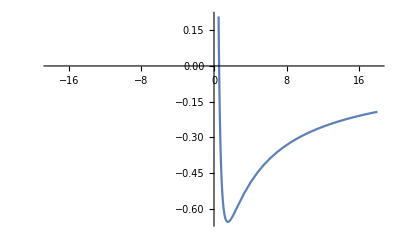

```mathematica
Plot[-(EulerGamma+Log[s])/s,{s,-18.,18.}]
```

```mathematica
LaplaceTransform[Exp[t],t,s]
```

1/(-1+s)

```mathematica
LaplaceTransform[t,t,s]
```

1/s^2

```mathematica
LaplaceTransform[t/(1+t),t,s]
```

(1+ⅇ^s s ExpIntegralEi[-s])/s

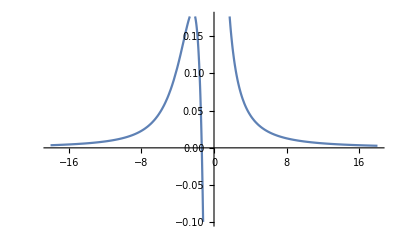

```mathematica
Plot[(1+ⅇ^s s ExpIntegralEi[-s])/s,{s,-18.,18.}]
```

```mathematica
LaplaceTransform[Sin[t^2],t,s]
```

1/2 √(π/2) (Cos[s^2/4] (1-2 FresnelC[s/(√(2 π))])+(1-2 FresnelS[s/(√(2 π))]) Sin[s^2/4])

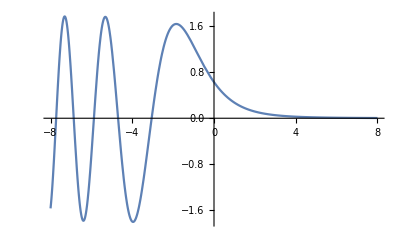

```mathematica
Plot[1/2 √(π/2) (Cos[s^2/4] (1-2 FresnelC[s/(√(2 π))])+(1-2 FresnelS[s/(√(2 π))]) Sin[s^2/4]),{s,-8,8}]
```

```mathematica
Sin[t^2]
```

Sin[t^2]

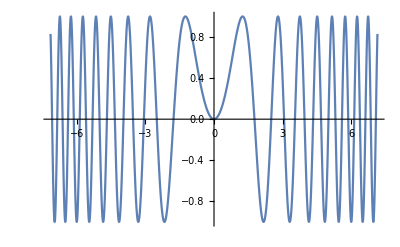

```mathematica
Plot[Sin[t^2],{t,-7.158520453821872,7.158520453821872}]
```

```mathematica
LaplaceTransform[Log[t]^2,t,s]
```

(6 EulerGamma^2+π^2+6 Log[s] (2 EulerGamma+Log[s]))/(6 s)

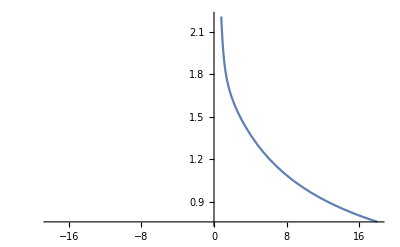

```mathematica
Plot[(6 EulerGamma^2+π^2+6 Log[s] (2 EulerGamma+Log[s]))/(6 s),{s,-18.,18.}]
```

```mathematica
LaplaceTransform[UnitStep[t-1]Cos[t],t,s]
```

$Aborted

```mathematica
UnitStep[t-1]Cos[t]
```

Cos[t] UnitStep[-1+t]

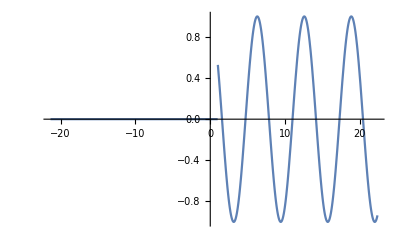

```mathematica
Plot[Cos[t] UnitStep[-1+t],{t,-21.34955592153876,22.34955592153876}]
```

```mathematica
LaplaceTransform[HeavisideTheta[t],t,s]
```

1/s

```mathematica
LaplaceTransform[f[t],t,s]==1/s
```

LaplaceTransform[f[t],t,s]==1/s

```mathematica
FindInstance[LaplaceTransform[f[t],t,s]==1/s,{s,t}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[LaplaceTransform[f[t],t,s]==1/s,{s,t}]

```mathematica
Solve[LaplaceTransform[f[t],t,s]==1/s,f]
```

{}

```mathematica
HeavisideTheta[t]
```

HeavisideTheta[t]

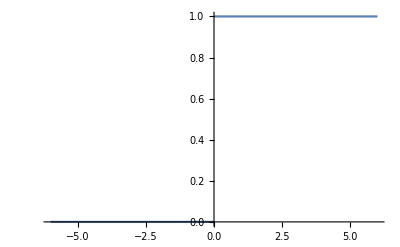

```mathematica
Plot[HeavisideTheta[t],{t,-6.,6.}]
```

```mathematica
LaplaceTransform[Sign[t],t,s]
```

1/s

```mathematica
LaplaceTransform[Sin[t],t,s]
```

1/(1+s^2)

```mathematica
Plot[1/(1+s^2),{s,-8,8}]
```

-Graphics-

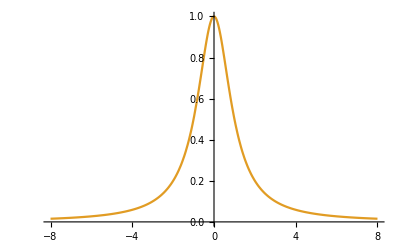

```mathematica
Plot[{Sin[t],1/(1+s^2)},{s,-8,8}]
```

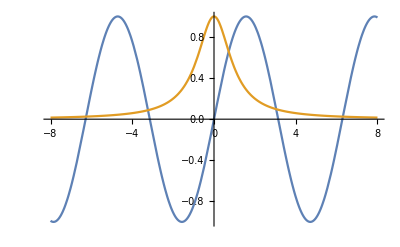

```mathematica
Plot[{Sin[s],1/(1+s^2)},{s,-8,8}]
```

```mathematica
LaplaceTransform[Sin[nt],t,s]
```

Sin[nt]/s

```mathematica
LaplaceTransform[Sin[n t],t,s]
```

n/(n^2+s^2)

```mathematica
FullSimplify[LaplaceTransform[Sin[n t],t,s],{s,n}∈Reals]
```

n/(n^2+s^2)

```mathematica
LaplaceTransform[f'[t]==Log[t],t,s]
```

-f[0]+s LaplaceTransform[f[t],t,s]==-(EulerGamma+Log[s])/s

```mathematica
LaplaceTransform[f'[t]==Sin[t],t,s]
```

-f[0]+s LaplaceTransform[f[t],t,s]==1/(1+s^2)

```mathematica
Reduce[-f[0]+s LaplaceTransform[f[t],t,s]==1/(1+s^2)]
```

1+s^2≠0&&f[0]==(-1+s LaplaceTransform[f[t],t,s]+s^3 LaplaceTransform[f[t],t,s])/(1+s^2)

```mathematica
InverseLaplaceTransform[-f[0]+s LaplaceTransform[f[t],t,s]==1/(1+s^2),s,t]
```

f'[t]==Sin[t]

```mathematica
LaplaceTransform[f[t],t,s]//TraditionalForm
```

ℒ_t[f(t)](s)

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
Normal[1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

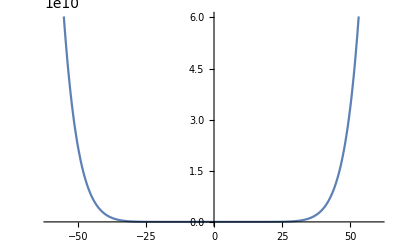

```mathematica
Plot[1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800,{x,-60.,60.}]
```

```mathematica
D[2^x,x]
```

2^x Log[2]

```mathematica
2^x==Exp[x]/Exp[2]
```

2^x==ⅇ^(-2+x)

```mathematica
Log[2,f[x]]==Log[2,2^x]
```

Log[f[x]]/Log[2]==Log[2^x]/Log[2]

```mathematica
Reduce[Log[f[x]]/Log[2]==Log[2^x]/Log[2]]
```

Log[2^x]==Log[f[x]]

```mathematica
Log[2^x]/Log[2]==Log[Exp[1],2^x]/Log[2]
```

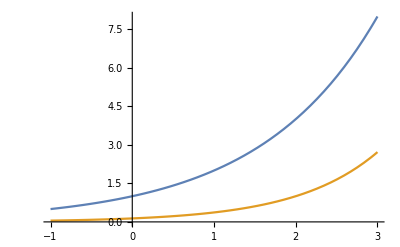

```mathematica
Plot[{2^x,ⅇ^(-2+x)},{x,-1,3}]
```

```mathematica
Solve[Exp[x]==f[x] 2^x,f]
```

{{}}

```mathematica
MultiplySides[Exp[x]==f[x] 2^x,2^x]
```

Piecewise[{{(2 ⅇ)^x==2^(2 x) f[x], 2^x≠0}, {ⅇ^x==2^x f[x], True}}]

```mathematica
MultiplySides[Exp[x]==f[x] 2^x,1/2^x]
```

Piecewise[{{(ⅇ/2)^x==f[x], 2^-x≠0}, {ⅇ^x==2^x f[x], True}}]

```mathematica
Solve[Exp[x]==f[x] 2^x,f[x]]
```

{{f[x]→(ⅇ/2)^x}}

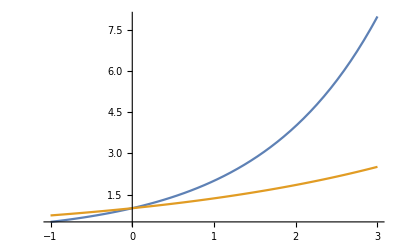

```mathematica
Plot[{2^x,(ⅇ/2)^x},{x,-1,3}]
```

```mathematica
f'[x]==x f[x]
```

f'[x]==x f[x]

```mathematica
DSolve[f'[x]==x f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x^2/2) C[1]}}

```mathematica
Exp[-x]
```

ⅇ^-x

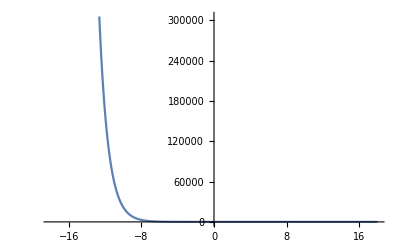

```mathematica
Plot[ⅇ^-x,{x,-18.,18.}]
```

```mathematica
Exp[-x^2]
```

ⅇ^(-x^2)

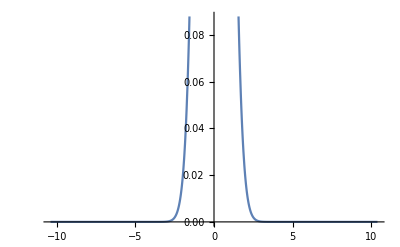

```mathematica
Plot[ⅇ^(-x^2),{x,-10.392304845413262,10.392304845413262}]
```

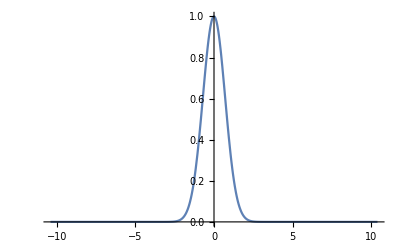

```mathematica
Plot[ⅇ^(-x^2),{x,-10.392304845413262,10.392304845413262},PlotRange->Full]
```

```mathematica
D[f[x],x]
```

f'[x]

```mathematica
D[f[x],{x,2}]
```

f''[x]

```mathematica
D[f[x],{x,-1}]
```

D::dvar: Multiple derivative specifier {x,-1} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

∂_{x,-1} f[x]

```mathematica
D[f[x],{x,1/2}]
```

D::dvar: Multiple derivative specifier {x,1/2} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

∂_{x,1/2} f[x]

```mathematica
Exp[1/(1-t^2)]
```

ⅇ^(1/(1-t^2))

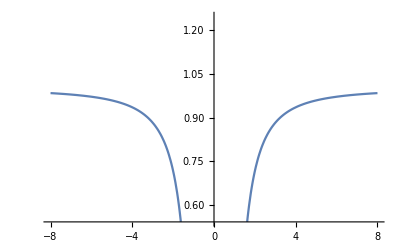

```mathematica
Plot[ⅇ^(1/(1-t^2)),{t,-8,8}]
```

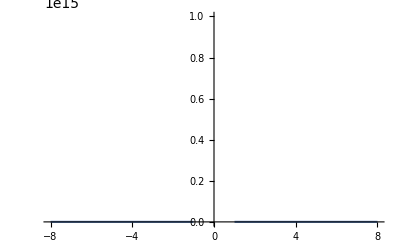

```mathematica
Plot[ⅇ^(1/(1-t^2)),{t,-8,8},PlotRange->Full]
```

```mathematica
Integrate[f[t]g[t],{t,Subscript[t, 1],Subscript[t, 2]}]
```

∫_t_1^t_2 f[t] g[t]ⅆt

```mathematica
LaplaceTransform[Sin[t],t,s]
```

1/(1+s^2)

```mathematica
Plot[1/(1+s^2),{s,-8,8}]
```

-Graphics-

```mathematica
LaplaceTransform[f[t],t,s]
```

LaplaceTransform[f[t],t,s]

```mathematica
LaplaceTransform[Integrate[f[t],{t,0,t}],t,s]
```

Integrate[f[t],{t,0,t},Assumptions→0<t<∞&&s>0&&t>0]/s

```mathematica
LaplaceTransform[Integrate[f[t],{t,0,s}],t,s]
```

Integrate[f[t],{t,0,s},Assumptions→0<t<∞&&s>0&&t>0]/s

```mathematica
LaplaceTransform[Integrate[f[t],{s,0,t}],t,s]
```

LaplaceTransform[t f[t],t,s]

```mathematica
LaplaceTransform[Integrate[f[u],{u,0,t}],t,s]
```

LaplaceTransform[f[t],t,s]/s

```mathematica
x f[x]
```

x f[x]

```mathematica
x Gamma[x]
```

x Gamma[x]

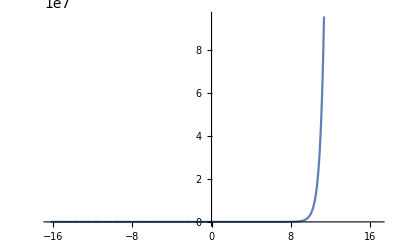

```mathematica
Plot[x Gamma[x],{x,-16.25,16.75}]
```

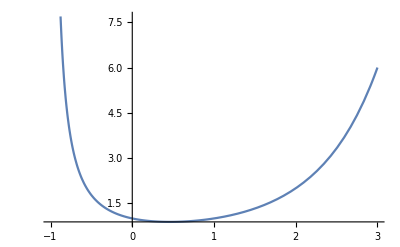

```mathematica
Plot[x Gamma[x],{x,-1,3}]
```

```mathematica
MellinTransform[E^(-a x),x,s]
```

a^-s Gamma[s]

```mathematica
MellinTransform[Sin[x],x,s]
```

Gamma[s] Sin[(π s)/2]

```mathematica
MellinTransform[Integrate[f[u],{u,0,x}],x,s]
```

-MellinTransform[f[x],x,1+s]/s

```mathematica
MellinTransform[E^(x),x,s]
```

MellinTransform[ⅇ^x,x,s]

```mathematica
FinancialData["NASDAQ:AAPL","Volume"]
```

36592936 shares

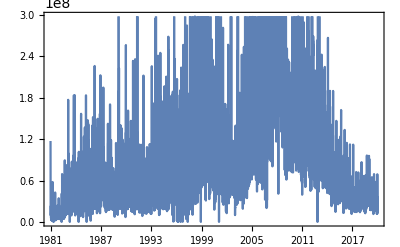

```mathematica
DateListPlot@FinancialData["NASDAQ:AAPL","Volume",All]
```

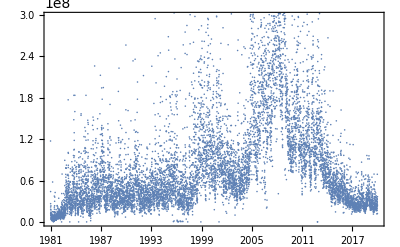

```mathematica
DateListPlot[FinancialData["NASDAQ:AAPL","Volume",All],Joined->False]
```

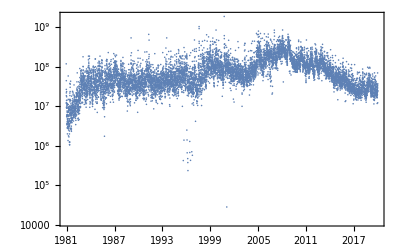

```mathematica
DateListLogPlot[FinancialData["NASDAQ:AAPL","Volume",All],Joined->False]
```

```mathematica
Log[x]
```

Log[x]

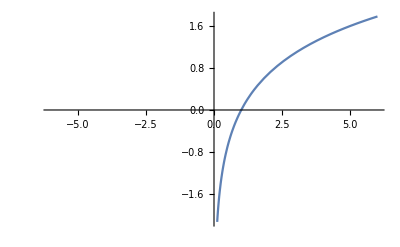

```mathematica
Plot[Log[x],{x,-6,6}]
```

```mathematica
Integrate[Log[x],{x,1,4}]
```

-3+Log[256]

```mathematica
N[-3+Log[256]]
```

2.54518

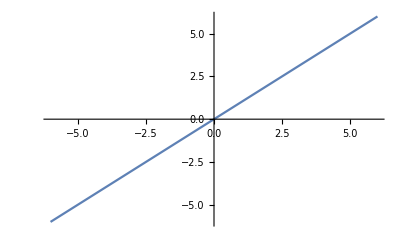

```mathematica
Plot[x,{x,-6,6}]
```

```mathematica
Integrate[x,{x,1,4}]
```

15/2

```mathematica
N[15/2]
```

7.5

```mathematica
Integrate[(f[x]-Integrate[f[x],{x,1,4}])^2,{x,1,4}]
```

∫_1^4 (f[x]-∫_1^4 f[x]ⅆx)^2 ⅆx

```mathematica
With[{f=Identity},
Integrate[(f[x]-Integrate[f[x],{x,1,4}])^2,{x,1,4}]
]
```

309/4

```mathematica
N[309/4]
```

77.25

```mathematica
With[{f=Identity},
Integrate[(f[x]-Integrate[f[x],{x,1,4}]),{x,1,4}]
]
```

-15

```mathematica
ArcLength[{x,f[x]},x]
```

ArcLength::vars: Integration range specification x is not of the form {t, t_min, t_max}.

ArcLength[{x,f[x]},x]

```mathematica
ArcLength[{x,f[x]},{x,1,4}]
```

∫_1^4 √(1+f'[x]^2)ⅆx

```mathematica
Integrate[Integrate[ArcLength[{u,f[u]},{u,Integrate[f[x],{x,1,4}],x}]],{x,1,4}]
```

Integrate::argmu: Integrate called with 1 argument; 2 or more arguments are expected.

∫_1^4 Integrate[Integrate[√(1+f'[u]^2),{u,∫_1^4 f[x]ⅆx,x},Assumptions→∫_1^4 f[x]ⅆx<x]]ⅆx

```mathematica
Integrate[ArcLength[{u,f[u]},{u,Integrate[f[x],{x,1,4}],x}],{x,1,4}]
```

∫_1^4 Integrate[√(1+f'[u]^2),{u,∫_1^4 f[x]ⅆx,x},Assumptions→∫_1^4 f[x]ⅆx<x]ⅆx

```mathematica
Annuity[.4,10]
```

Annuity[0.4,10]

```mathematica
Annuity[1000,10]
```

Annuity[1000,10]

```mathematica
1000/(1.05)^x
```

1000 1.05^-x

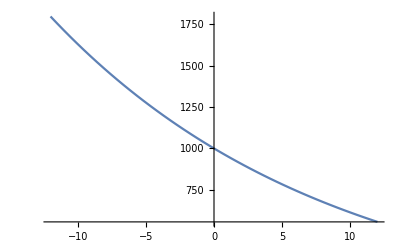

```mathematica
Plot[1000 1.05^-x,{x,-12.,12.}]
```

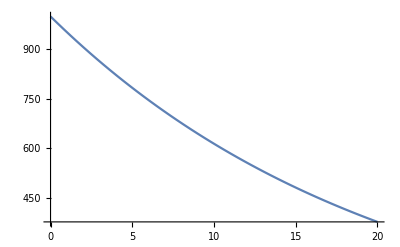

```mathematica
Plot[1000 1.05^-x,{x,0,20}]
```

```mathematica
Plot[1000 1.05^-x,{x,0,20},PlotRange->Full]
```

-Graphics-

```mathematica
D[1000 1.05^-x,x]
```

-48.7902 1.05^-x

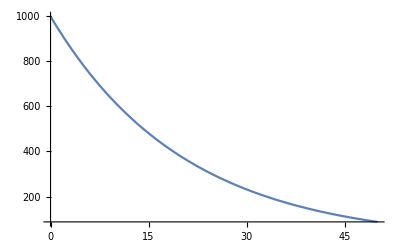

```mathematica
Plot[1000 1.05^-x,{x,0,50},PlotRange->Full]
```

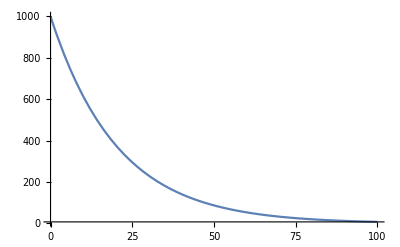

```mathematica
Plot[1000 1.05^-x,{x,0,100},PlotRange->Full]
```

```mathematica
CityData[{"Tokyo", "Tokyo", "Japan"}]
```

Tokyo

```mathematica
WeatherData[Entity["City",{"Tokyo","Tokyo","Japan"}],"WindSpeed"]
```

5.4 km/h

```mathematica
WeatherData[Entity["City",{"Tokyo","Tokyo","Japan"}],"Humidity"]
```

0.753

```mathematica
WeatherData[Entity["City",{"Tokyo","Tokyo","Japan"}],"Pressure"]
```

1021 mbar

```mathematica
WeatherData[Entity["City",{"Tokyo","Tokyo","Japan"}],"Temperature"]
```

4.99999 °C

```mathematica
CityData[Entity["City",{"Tokyo","Tokyo","Japan"}],"TimeZone"]
```

9 h

```mathematica
CityData[Entity["City",{"Tokyo","Tokyo","Japan"}],"Elevation"]
```

19 m

```mathematica
CityData[Entity["City",{"Tokyo","Tokyo","Japan"}],"Population"]
```

13297629 people

```mathematica
WeatherData[Entity["City",{"Tokyo","Tokyo","Japan"}],"Properties"]
```

{AlternateStandardNames,CloudCoverFraction,CloudHeight,CloudTypes,Conditions,Coordinates,DewPoint,Elevation,Humidity,Latitude,Longitude,MaxTemperature,MaxWindSpeed,MeanDewPoint,MeanHumidity,MeanPressure,MeanStationPressure,MeanTemperature,MeanVisibility,MeanWindChill,MeanWindSpeed,Memberships,MinTemperature,NCDCID,PrecipitationAmount,PrecipitationRate,PrecipitationTypes,Pressure,PressureTendency,SnowAccumulation,SnowAccumulationRate,SnowDepth,StationName,StationPressure,Temperature,TotalPrecipitation,Visibility,WBANID,WindChill,WindDirection,WindGusts,WindSpeed,WMOID}

```mathematica
CityData[{"LosAngeles", "California", "UnitedStates"}]
```

Los Angeles

```mathematica
WeatherData[Entity["City",{"LosAngeles","California","UnitedStates"}]]
```

KSMO

```mathematica
Grid@
Table[{w,WeatherData[Entity["City",{"LosAngeles","California","UnitedStates"}],w]},{w,WeatherData[Entity["City",{"LosAngeles","California","UnitedStates"}]]}]
```

Table::iterb: Iterator {w,KSMO} does not have appropriate bounds.

Grid[Table[{w,WeatherData[Los Angeles,w]},{w,KSMO}]]

```mathematica
Grid@
Table[
{w,WeatherData[Entity["City",{"LosAngeles","California","UnitedStates"}],w]},
{w,WeatherData[Entity["City",{"LosAngeles","California","UnitedStates"}],"Properties"]}
]
```

WeatherData::notent: {"LosAngeles", "California", "UnitedStates"} is not a known entity, class, or tag for WeatherData. Use WeatherData[] for a list of entities.

AlternateStandardNames | WeatherData[{LosAngeles,California,UnitedStates},AlternateStandardNames]
CloudCoverFraction | 0
CloudHeight | Missing[NotAvailable]
CloudTypes | {}
Conditions | {}
Coordinates | {34.021,-118.447}
DewPoint | 0.6 °C
Elevation | 53. m
Humidity | 0.541
Latitude | 34.021 °
Longitude | -118.447 °
MaxTemperature | Missing[NotApplicable]
MaxWindSpeed | Missing[NotApplicable]
MeanDewPoint | Missing[NotApplicable]
MeanHumidity | Missing[NotApplicable]
MeanPressure | Missing[NotApplicable]
MeanStationPressure | Missing[NotApplicable]
MeanTemperature | Missing[NotApplicable]
MeanVisibility | Missing[NotApplicable]
MeanWindChill | Missing[NotApplicable]
MeanWindSpeed | Missing[NotApplicable]
Memberships | {NCDC}
MinTemperature | Missing[NotApplicable]
NCDCID | NCDC722885
PrecipitationAmount | Missing[NotAvailable]
PrecipitationRate | Missing[NotAvailable]
PrecipitationTypes | {}
Pressure | 1017.8 mbar
PressureTendency | Missing[NotAvailable]
SnowAccumulation | Missing[NotAvailable]
SnowAccumulationRate | Missing[NotAvailable]
SnowDepth | Missing[NotAvailable]
StationName | KSMO
StationPressure | Missing[NotAvailable]
Temperature | 9.39999 °C
TotalPrecipitation | Missing[NotApplicable]
Visibility | 16.09 km
WBANID | Missing[NotApplicable]
WindChill | 8.96 °C
WindDirection | 40 °
WindGusts | Missing[NotAvailable]
WindSpeed | 5.4 km/h
WMOID | Missing[NotApplicable]

```mathematica
WeatherData[Entity["City",{"Tokyo","Tokyo","Japan"}]]
```

RJTD

```mathematica
WeatherData[]
```

{Entity[WeatherStation,ABBANF],AGGH,AGGL,AGGM,ASLH,AYMO,AYNZ,AYPY,AYVN,AYWK,BGBW,BGGH,BGJN,BGKK,BGSF,BGTL,BIAR,BIEG,BIKF,BIRK,Entity[WeatherStation,C???],CABT,CACP,CACQ,Entity[WeatherStation,CADN],CADS,CAFC,CAFY,CAHR,CAKC,CAOH,CAPR,CAQY,CAWR,CBBC,CERM,Entity[WeatherStation,CGAH],Entity[WeatherStation,CGMG],Entity[WeatherStation,CGVO],CMFM,CMFR,Entity[WeatherStation,CMJK],CMLU,Entity[WeatherStation,CMNT],CNBB,Entity[1],CNCD,7464,ZGZJ,ZHCC,ZHHH,ZJHK,ZJSY,Entity[WeatherStation,ZKHH],ZKKC,ZKPY,Entity[WeatherStation,ZKWS],Entity[WeatherStation,ZLGM],ZLIC,ZLJQ,ZLLL,ZLXN,ZLXY,ZLYA,ZMAT,ZMTL,ZMUB,ZPPP,ZSAM,ZSCN,ZSFZ,ZSGZ,ZSHC,ZSNJ,ZSOF,ZSPD,ZSQD,ZSSS,ZSTN,ZUCK,ZUGY,ZUUU,ZWHM,ZWSH,ZWTN,ZWWW,ZWYN,ZYCC,ZYCY,ZYHB,ZYQQ,ZYTL,ZYTX,ZYYY}
 |  |  |  |

```mathematica
Grid@
Table[
{w,WeatherData[Entity["City",{"Tokyo","Tokyo","Japan"}],w]},
{w,WeatherData[Entity["City",{"Tokyo","Tokyo","Japan"}],"Properties"]}
]
```

WeatherData::notent: {"Tokyo", "Tokyo", "Japan"} is not a known entity, class, or tag for WeatherData. Use WeatherData[] for a list of entities.

AlternateStandardNames | WeatherData[{Tokyo,Tokyo,Japan},AlternateStandardNames]
CloudCoverFraction | 0.25
CloudHeight | Missing[NotAvailable]
CloudTypes | {}
Conditions | {}
Coordinates | {35.553,139.781}
DewPoint | 0.999994 °C
Elevation | 11. m
Humidity | 0.703
Latitude | 35.553 °
Longitude | 139.781 °
MaxTemperature | Missing[NotApplicable]
MaxWindSpeed | Missing[NotApplicable]
MeanDewPoint | Missing[NotApplicable]
MeanHumidity | Missing[NotApplicable]
MeanPressure | Missing[NotApplicable]
MeanStationPressure | Missing[NotApplicable]
MeanTemperature | Missing[NotApplicable]
MeanVisibility | Missing[NotApplicable]
MeanWindChill | Missing[NotApplicable]
MeanWindSpeed | Missing[NotApplicable]
Memberships | {NCDC,WMO}
MinTemperature | Missing[NotApplicable]
NCDCID | NCDC476710
PrecipitationAmount | Missing[NotAvailable]
PrecipitationRate | Missing[NotAvailable]
PrecipitationTypes | {}
Pressure | 1020 mbar
PressureTendency | Missing[NotAvailable]
SnowAccumulation | Missing[NotAvailable]
SnowAccumulationRate | Missing[NotAvailable]
SnowDepth | Missing[NotAvailable]
StationName | RJTT
StationPressure | Missing[NotAvailable]
Temperature | 5.99999 °C
TotalPrecipitation | Missing[NotApplicable]
Visibility | 10 km
WBANID | Missing[NotApplicable]
WindChill | 4. °C
WindDirection | 290 °
WindGusts | Missing[NotAvailable]
WindSpeed | 9.36 km/h
WMOID | WMO47671

```mathematica
CityData[{"Tokyo", "Tokyo", "Japan"}]
```

Tokyo

```mathematica
CityData[{"NewYork", "NewYork", "UnitedStates"}]
```

New York City

```mathematica
Grid@
Table[
{w,WeatherData[Entity["City",{"NewYork","NewYork","UnitedStates"}],w]},
{w,WeatherData[Entity["City",{"NewYork","NewYork","UnitedStates"}],"Properties"]}
]
```

WeatherData::notent: {"NewYork", "NewYork", "UnitedStates"} is not a known entity, class, or tag for WeatherData. Use WeatherData[] for a list of entities.

AlternateStandardNames | WeatherData[{NewYork,NewYork,UnitedStates},AlternateStandardNames]
CloudCoverFraction | 1
CloudHeight | Missing[NotAvailable]
CloudTypes | {}
Conditions | {}
Coordinates | {40.779,-73.969}
DewPoint | -5.60001 °C
Elevation | 48. m
Humidity | 0.539
Latitude | 40.779 °
Longitude | -73.969 °
MaxTemperature | Missing[NotApplicable]
MaxWindSpeed | Missing[NotApplicable]
MeanDewPoint | Missing[NotApplicable]
MeanHumidity | Missing[NotApplicable]
MeanPressure | Missing[NotApplicable]
MeanStationPressure | Missing[NotApplicable]
MeanTemperature | Missing[NotApplicable]
MeanVisibility | Missing[NotApplicable]
MeanWindChill | Missing[NotApplicable]
MeanWindSpeed | Missing[NotApplicable]
Memberships | {NCDC,WMO}
MinTemperature | Missing[NotApplicable]
NCDCID | NCDC725060
PrecipitationAmount | Missing[NotAvailable]
PrecipitationRate | Missing[NotAvailable]
PrecipitationTypes | {}
Pressure | 1006.8 mbar
PressureTendency | Missing[NotAvailable]
SnowAccumulation | Missing[NotAvailable]
SnowAccumulationRate | Missing[NotAvailable]
SnowDepth | Missing[NotAvailable]
StationName | KNYC
StationPressure | Missing[NotAvailable]
Temperature | 2.80001 °C
TotalPrecipitation | Missing[NotApplicable]
Visibility | 16.09 km
WBANID | Missing[NotApplicable]
WindChill | -1.47 °C
WindDirection | 270 °
WindGusts | Missing[NotAvailable]
WindSpeed | 18.36 km/h
WMOID | WMO72506

```mathematica
Entity["WeatherStation","KSMO"]
```

KSMO

```mathematica
CommonName[Entity["WeatherStation","KSMO"]]
```

KSMO

```mathematica
EntityTypeName[Entity["WeatherStation","KSMO"]]
```

WeatherStation

```mathematica
CanonicalName[Entity["WeatherStation","KSMO"]]
```

KSMO

```mathematica
Grid@
Table[
{w,WeatherData[Entity["WeatherStation","KSMO"],w]},
{w,WeatherData[Entity["WeatherStation","KSMO"],"Properties"]}
]
```

AlternateStandardNames | {NCDC722885}
CloudCoverFraction | 0
CloudHeight | Missing[NotAvailable]
CloudTypes | {}
Conditions | {}
Coordinates | {34.021,-118.447}
DewPoint | 0.6 °C
Elevation | 53. m
Humidity | 0.541
Latitude | 34.021 °
Longitude | -118.447 °
MaxTemperature | Missing[NotApplicable]
MaxWindSpeed | Missing[NotApplicable]
MeanDewPoint | Missing[NotApplicable]
MeanHumidity | Missing[NotApplicable]
MeanPressure | Missing[NotApplicable]
MeanStationPressure | Missing[NotApplicable]
MeanTemperature | Missing[NotApplicable]
MeanVisibility | Missing[NotApplicable]
MeanWindChill | Missing[NotApplicable]
MeanWindSpeed | Missing[NotApplicable]
Memberships | {NCDC}
MinTemperature | Missing[NotApplicable]
NCDCID | NCDC722885
PrecipitationAmount | Missing[NotAvailable]
PrecipitationRate | Missing[NotAvailable]
PrecipitationTypes | {}
Pressure | 1017.8 mbar
PressureTendency | Missing[NotAvailable]
SnowAccumulation | Missing[NotAvailable]
SnowAccumulationRate | Missing[NotAvailable]
SnowDepth | Missing[NotAvailable]
StationName | KSMO
StationPressure | Missing[NotAvailable]
Temperature | 9.39999 °C
TotalPrecipitation | Missing[NotApplicable]
Visibility | 16.09 km
WBANID | Missing[NotApplicable]
WindChill | 8.96 °C
WindDirection | 40 °
WindGusts | Missing[NotAvailable]
WindSpeed | 5.4 km/h
WMOID | Missing[NotApplicable]

```mathematica
GeoListPlot@Entity["WeatherStation","KSMO"]
```

-Graphics-

```mathematica
GeoListPlot[Entity["WeatherStation","KSMO"],GeoRange->Quantity[100,"Meters"]]
```

-Graphics-

```mathematica
GeoListPlot[Entity["WeatherStation","KSMO"],GeoRange->Quantity[1,"Kilometers"]]
```

GeoGraphics::tiles: Unable to download 6 tiles of the geo background image.

-Graphics-

```mathematica
GeoListPlot[Entity["WeatherStation","KSMO"],GeoRange->Quantity[1,"Kilometers"],GeoBackground->"Satellite"]
```

-Graphics-

```mathematica
GeoListPlot[Entity["WeatherStation","KSMO"],GeoRange->Quantity[10,"Kilometers"],GeoBackground->"Satellite"]
```

-Graphics-

```mathematica
EntityValue[
EntityClass["City",{EntityProperty["City","Population"]->TakeLargest[30]}],
{EntityProperty["City","Name"],"Population"}
]
```

{{Shanghai,24152700 people},{Beijing,21700000 people},{Lagos,21324000 people},{Tianjin,15469500 people},{Karachi,14916456 people},{Istanbul,14804116 people},{Dhaka,14543124 people},{Chengdu,14427500 people},{Tokyo,13617445 people},{Guangzhou,13501100 people},{Mumbai,12442373 people},{Moscow,12380664 people},{Bengaluru,12339447 people},{Zhoukou,12067600 people},{São Paulo,12038175 people},{Kinshasa,11855000 people},{Nanyang,11675100 people},{Baoding,11194379 people},{Delhi,11034555 people},{Lima,10852210 people},{Shenzhen,10778900 people},{Shijiazhuang,10701600 people},{Wuhan,10607700 people},{Lahore,10355000 people},{Jakarta,10187595 people},{Linyi,10039440 people},{Seoul,9971111 people},{Xuzhou,9576100 people},{Zhengzhou,9568000 people},{Cairo,9500000 people}}

```mathematica
EntityProperty["City","Population"]
```

city population

```mathematica
EntityProperties["City"]
```

{administrative region,number of aggravated assaults,rate of aggravated assault,aggregate home value,aggregate home value, householder 15 to 24 years,aggregate home value, householder 25 to 34 years,aggregate home value, householder 35 to 64 years,aggregate home value, householder 65 years and over,aggregate household income,airport codes,fuel spent in delays,total fuel spent in delays,average annual delay,total annual delay,area,area code,arterial street traffic,arterial street length,average public transit trip distance,number of burglaries,rate of burglary,city sales tax,coordinates,country,county,county sales tax,total rate of crime,total number of crimes,average daily traffic delay,elevation,entity classes,number of rapes,rate of rape,freeway traffic,freeway length,Gini index,has polygon?,FHFA home price index,FHFA home price index annual average,housing affordability index,households,number of larcenies,rate of larceny,latitude,longitude,total magnetic field strength,median age,median home sale price,median home value,median household income,number of motor vehicle thefts,rate of motor vehicle thefts,incidents of murder and nonnegligent manslaughter,rate of murder and nonnegligent manslaughter,name,next daylight saving shift,nicknames,number of owner-occupied housing units,average daily peak period travelers,peak period travelers per capita,average daily peak period vehicles,notable people born in city,notable people who died in city,per capita income,polygon,city population,population by educational attainment,population by migration in previous 12 months,population by language spoken at home,population by marital status,population by poverty status,population by school enrollment,population density,position,last daylight saving shift,total rate of property crime,total number of property crimes,total public transit use,unlinked public transit trips,4 bedroom apartment fair market rent,1 bedroom apartment fair market rent,3 bedroom apartment fair market rent,2 bedroom apartment fair market rent,studio apartment fair market rent,number of robberies,rate of robbery,daily rush hour length,state sales tax,time zone,total daily traffic delay,total sales tax rate,average peak travel time,unemployment rate,unweighted sample housing units,unweighted sample population,total rate of violent crime,total number of violent crimes,ZIP codes}

```mathematica
EntityValue[
EntityClass["City",{EntityProperty["City","Population"]->TakeLargest[50]}],
{EntityProperty["City","Name"],EntityProperty["City","Country"],EntityProperty["City","County"],EntityProperty["City","Population"]}
]
```

{{Shanghai,China,Missing[NotAvailable],24152700 people},{Beijing,China,Missing[NotAvailable],21700000 people},{Lagos,Nigeria,Missing[NotAvailable],21324000 people},{Tianjin,China,Missing[NotAvailable],15469500 people},{Karachi,Pakistan,Missing[NotAvailable],14916456 people},{Istanbul,Turkey,Missing[NotAvailable],14804116 people},{Dhaka,Bangladesh,Missing[NotAvailable],14543124 people},{Chengdu,China,Missing[NotAvailable],14427500 people},{Tokyo,Japan,Missing[NotAvailable],13617445 people},{Guangzhou,China,Missing[NotAvailable],13501100 people},{Mumbai,India,Missing[NotAvailable],12442373 people},{Moscow,Russia,Missing[NotAvailable],12380664 people},{Bengaluru,India,Missing[NotAvailable],12339447 people},{Zhoukou,China,Missing[NotAvailable],12067600 people},{São Paulo,Brazil,Missing[NotAvailable],12038175 people},{Kinshasa,Democratic Republic of the Congo,Missing[NotAvailable],11855000 people},{Nanyang,China,Missing[NotAvailable],11675100 people},{Baoding,China,Missing[NotAvailable],11194379 people},{Delhi,India,Missing[NotAvailable],11034555 people},{Lima,Peru,Missing[NotAvailable],10852210 people},{Shenzhen,China,Missing[NotAvailable],10778900 people},{Shijiazhuang,China,Missing[NotAvailable],10701600 people},{Wuhan,China,Missing[NotAvailable],10607700 people},{Lahore,Pakistan,Missing[NotAvailable],10355000 people},{Jakarta,Indonesia,Missing[NotAvailable],10187595 people},{Linyi,China,Missing[NotAvailable],10039440 people},{Seoul,South Korea,Missing[NotAvailable],9971111 people},{Xuzhou,China,Missing[NotAvailable],9576100 people},{Zhengzhou,China,Missing[NotAvailable],9568000 people},{Cairo,Egypt,Missing[NotAvailable],9500000 people},{Heze,China,Missing[NotAvailable],9394400 people},{Handan,China,Missing[NotAvailable],9174683 people},{Wenzhou,China,Missing[NotAvailable],9122102 people},{Shangqiu,China,Missing[NotAvailable],9108700 people},{Weifang,China,Missing[NotAvailable],9086241 people},{Qingdao,China,Missing[NotAvailable],9046200 people},{Hangzhou,China,Missing[NotAvailable],9018000 people},{Mexico City,Mexico,Missing[NotAvailable],8918653 people},{Tehran,Iran,Missing[NotAvailable],8846782 people},{Baghdad,Iraq,Missing[NotAvailable],8765000 people},{Zhumadian,China,Missing[NotAvailable],8731300 people},{Xian,China,Missing[NotAvailable],8705600 people},{London,United Kingdom,Missing[NotAvailable],8673713 people},{New York City,United States,{Kings County (Brooklyn), New York, United States→30.8 %,Queens County (Queens), New York, United States→27.8 %,New York County (Manhattan), New York, United States→19.2 %,Bronx County (The Bronx), New York, United States→16.6 %,Richmond County (Staten Island), New York, United States→5.5 %},8622698 people},{Xinyang,China,Missing[NotAvailable],8609900 people},{Ho Chi Minh City,Vietnam,Missing[NotAvailable],8426100 people},{Ganzhou,China,Missing[NotAvailable],8368447 people},{Dongguan,China,Missing[NotAvailable],8310000 people},{Nanjing,China,Missing[NotAvailable],8230000 people},{Quanzhou,China,Missing[NotAvailable],8128533 people}}

```mathematica
Grid@
ReverseSortBy[
EntityValue[
EntityClass["City",{EntityProperty["City","Population"]->TakeLargest[50]}],
{EntityProperty["City","Name"],EntityProperty["City","AdministrativeDivision"],EntityProperty["City","Country"],EntityProperty["City","Population"]}
],Last]
```

Shanghai | Shanghai, China | China | 24152700 people
Beijing | Beijing, China | China | 21700000 people
Lagos | Lagos, Nigeria | Nigeria | 21324000 people
Tianjin | Tianjin, China | China | 15469500 people
Karachi | Sindh, Pakistan | Pakistan | 14916456 people
Istanbul | Istanbul, Turkey | Turkey | 14804116 people
Dhaka | Dhaka, Dhaka, Bangladesh | Bangladesh | 14543124 people
Chengdu | Sichuan, China | China | 14427500 people
Tokyo | Tokyo, Japan | Japan | 13617445 people
Guangzhou | Guangdong, China | China | 13501100 people
Mumbai | Maharashtra, India | India | 12442373 people
Moscow | Moscow, Russia | Russia | 12380664 people
Bengaluru | Karnataka, India | India | 12339447 people
Zhoukou | Henan, China | China | 12067600 people
São Paulo | São Paulo, Brazil | Brazil | 12038175 people
Kinshasa | Kinshasa City, Democratic Republic of the Congo | Democratic Republic of the Congo | 11855000 people
Nanyang | Henan, China | China | 11675100 people
Baoding | Hebei, China | China | 11194379 people
Delhi | Delhi, India | India | 11034555 people
Lima | Lima, Peru | Peru | 10852210 people
Shenzhen | Guangdong, China | China | 10778900 people
Shijiazhuang | Hebei, China | China | 10701600 people
Wuhan | Hubei, China | China | 10607700 people
Lahore | Punjab, Pakistan | Pakistan | 10355000 people
Jakarta | Jakarta, Indonesia | Indonesia | 10187595 people
Linyi | Shandong, China | China | 10039440 people
Seoul | Seoul, South Korea | South Korea | 9971111 people
Xuzhou | Jiangsu, China | China | 9576100 people
Zhengzhou | Henan, China | China | 9568000 people
Cairo | Cairo, Egypt | Egypt | 9500000 people
Heze | Shandong, China | China | 9394400 people
Handan | Hebei, China | China | 9174683 people
Wenzhou | Zhejiang, China | China | 9122102 people
Shangqiu | Henan, China | China | 9108700 people
Weifang | Shandong, China | China | 9086241 people
Qingdao | Shandong, China | China | 9046200 people
Hangzhou | Zhejiang, China | China | 9018000 people
Mexico City | Ciudad de México | Mexico | 8918653 people
Tehran | Tehran, Iran | Iran | 8846782 people
Baghdad | Baghdad, Iraq | Iraq | 8765000 people
Zhumadian | Henan, China | China | 8731300 people
Xian | Shaanxi, China | China | 8705600 people
London | Greater London, England, United Kingdom | United Kingdom | 8673713 people
New York City | New York, United States | United States | 8622698 people
Xinyang | Henan, China | China | 8609900 people
Ho Chi Minh City | Ho Chi Minh, Vietnam | Vietnam | 8426100 people
Ganzhou | Jiangxi, China | China | 8368447 people
Dongguan | Guangdong, China | China | 8310000 people
Nanjing | Jiangsu, China | China | 8230000 people
Quanzhou | Fujian, China | China | 8128533 people

```mathematica
Quantity[1,"Kilometers"]^2
```

1 km^2

```mathematica
UnitConvert[Quantity[1,("Kilometers")^2],("Meters")^2]
```

1000000 m^2

```mathematica
CityData[{"LosAngeles", "California", "UnitedStates"}]
```

Los Angeles

```mathematica
(Entity["City",{"LosAngeles","California","UnitedStates"}]["Population"])^2/(Entity["City",{"LosAngeles","California","UnitedStates"}]["Area"])
```

3.413503431304×10^10 people^2/mi^2